```mathematica
Quit[]
```

This notebook contains the quasinormal calcualtions of 
- Reissner-Nordstrom geometry
- Vector mode gravity fluctuatin 
- non zero momentum 
- Eddington-Finkelstein geometry 

This note book does not have the calculation but have derivation of the flucutuation only.

## Different package:

```mathematica
Quit
```

```mathematica
SetDirectory["C:\\Users\\Roshan\\Dropbox\\Electromagnetic branes\\alternative of diffgeo"]
<<EDCRGTCcode.m
```

C:\Users\Roshan\Dropbox\Electromagnetic branes\alternative of diffgeo

```mathematica
coords={v,x,y,z,r};
```

```mathematica
f[r_]:=1-m/r^4+q^2/r^6
```

```mathematica
Subscript[g, vv]=-r^2 f[r];
Subscript[g, xx]=r^2;
Subscript[g, yy]=r^2;
Subscript[g, zz]=r^2;
Subscript[g, rr]=r^2;
Subscript[g, vr]=Subscript[g, rv]=-1;
```

```mathematica
Subscript[g, rx]=Subscript[g, xr]=ϵ hVX[v,z,r]+O[ϵ]^2;
Subscript[g, ry]=Subscript[g, yr]=ϵ hVY[v,z,r]+O[ϵ]^2;
Subscript[g, xz]=Subscript[g, zx]=ϵ hXZ[v,z,r]+O[ϵ]^2;
Subscript[g, zy]=Subscript[g, yz]=ϵ hYZ[v,z,r]+O[ϵ]^2;
```

```mathematica
Subscript[g, vx]=Subscript[g, vy]=Subscript[g, vz]=Subscript[g, vr]=Subscript[g, xy]=Subscript[g, zr]=0;
Subscript[g, xv]=Subscript[g, yv]=Subscript[g, zv]=Subscript[g, rv]=Subscript[g, yx]=Subscript[g, rz]=0;
```

```mathematica
ansatz={{Subscript[g, vv],Subscript[g, vx],Subscript[g, vy],Subscript[g, vz],Subscript[g, vr]},
{Subscript[g, xv],Subscript[g, xx],Subscript[g, xy],Subscript[g, xz],Subscript[g, xr]},
{Subscript[g, yv],Subscript[g, yx],Subscript[g, yy],Subscript[g, yz],Subscript[g, yr]},
{Subscript[g, zv],Subscript[g, zx],Subscript[g, zy],Subscript[g, zz],Subscript[g, zr]},
{Subscript[g, rv],Subscript[g, rx],Subscript[g, ry],Subscript[g, rz],Subscript[g, rr]}};
```

```mathematica
ansatz//MatrixForm
```

(-(1+q^2/r^6-m/r^4) r^2 | 0 | 0 | 0 | 0
0 | r^2 | 0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | hVX[v,z,r] ϵ+O[ϵ]^2
0 | 0 | r^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | hVY[v,z,r] ϵ+O[ϵ]^2
0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | r^2 | 0
0 | hVX[v,z,r] ϵ+O[ϵ]^2 | hVY[v,z,r] ϵ+O[ϵ]^2 | 0 | r^2)

```mathematica
RGtensors[ansatz,coords];
```

gdd = (-(1+q^2/r^6-m/r^4) r^2 | 0 | 0 | 0 | 0
0 | r^2 | 0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | hVX[v,z,r] ϵ+O[ϵ]^2
0 | 0 | r^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | hVY[v,z,r] ϵ+O[ϵ]^2
0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | r^2 | 0
0 | hVX[v,z,r] ϵ+O[ϵ]^2 | hVY[v,z,r] ϵ+O[ϵ]^2 | 0 | r^2)

LineElement = (r^2 d[r]^2-((q^2-m r^2+r^6) d[v]^2)/r^4+r^2 d[x]^2+r^2 d[y]^2+r^2 d[z]^2)+(d[r] (2 d[x] hVX[v,z,r]+2 d[y] hVY[v,z,r])+2 d[x] d[z] hXZ[v,z,r]+2 d[y] d[z] hYZ[v,z,r]) ϵ+O[ϵ]^2

gUU = {{-r^4/(q^2-m r^2+r^6)+O[ϵ]^3,0,0,0,0},{0,1/r^2+((hVX[v,z,r]^2+hXZ[v,z,r]^2) ϵ^2)/r^6+O[ϵ]^3,((hVX[v,z,r] hVY[v,z,r]+hXZ[v,z,r] hYZ[v,z,r]) ϵ^2)/r^6+O[ϵ]^3,-(hXZ[v,z,r] ϵ)/r^4+O[ϵ]^2,-(hVX[v,z,r] ϵ)/r^4+O[ϵ]^2},{0,((hVX[v,z,r] hVY[v,z,r]+hXZ[v,z,r] hYZ[v,z,r]) ϵ^2)/r^6+O[ϵ]^3,1/r^2+((hVY[v,z,r]^2+hYZ[v,z,r]^2) ϵ^2)/r^6+O[ϵ]^3,-(hYZ[v,z,r] ϵ)/r^4+O[ϵ]^2,-(hVY[v,z,r] ϵ)/r^4+O[ϵ]^2},{0,-(hXZ[v,z,r] ϵ)/r^4+O[ϵ]^2,-(hYZ[v,z,r] ϵ)/r^4+O[ϵ]^2,1/r^2+((hXZ[v,z,r]^2+hYZ[v,z,r]^2) ϵ^2)/r^6+O[ϵ]^3,((hVX[v,z,r] hXZ[v,z,r]+hVY[v,z,r] hYZ[v,z,r]) ϵ^2)/r^6+O[ϵ]^3},{0,-(hVX[v,z,r] ϵ)/r^4+O[ϵ]^2,-(hVY[v,z,r] ϵ)/r^4+O[ϵ]^2,((hVX[v,z,r] hXZ[v,z,r]+hVY[v,z,r] hYZ[v,z,r]) ϵ^2)/r^6+O[ϵ]^3,1/r^2+((hVX[v,z,r]^2+hVY[v,z,r]^2) ϵ^2)/r^6+O[ϵ]^3}}

gUU computed in 0.031 sec

Gamma computed in 0.062 sec

Riemann(dddd) computed in 0.485 sec

Riemann(Uddd) computed in 3.906 sec

Ricci computed in 1.563 sec

Weyl computed in 5.875 sec

Einstein computed in 3.375 sec

All tasks completed in 15.312500 seconds

```mathematica
2 r^4 (q^2-m r^2+r^6)Rdd[[2,5]]//Simplify
```

(2 (q^2-2 r^6) hVX[v,z,r]+r (-2 (q^2-m r^2+r^6) hXZ^(0,1,0)[v,z,r]+r ((q^2-m r^2+r^6) hXZ^(0,1,1)[v,z,r]-(q^2-m r^2+r^6) hVX^(0,2,0)[v,z,r]+r^6 hVX^(2,0,0)[v,z,r]))) ϵ+O[ϵ]^2

```mathematica
2 r^6 (q^2-m r^2+r^6)^2 Coefficient[EUd[[2,5]],ϵ]//Simplify
```

2 (6 q^4+2 r^8 (m-3 r^4)+q^2 (-7 m r^2+9 r^6)) hVX[v,z,r]+r (q^2-m r^2+r^6) (-2 (q^2-m r^2+r^6) hXZ^(0,1,0)[v,z,r]+r ((q^2-m r^2+r^6) hXZ^(0,1,1)[v,z,r]-(q^2-m r^2+r^6) hVX^(0,2,0)[v,z,r]+r^6 hVX^(2,0,0)[v,z,r]))

## Setting the metric:

```mathematica
f[r_]:=1-m/r^4+q^2/r^6
```

```mathematica
Solve[0==r^6 f[rH]/.{m->1,q->10},rH]//N
```

{{rH→0.-2.17104 ⅈ},{rH→0.+2.17104 ⅈ},{rH→-1.86585+1.06052 ⅈ},{rH→1.86585-1.06052 ⅈ},{rH→1.86585+1.06052 ⅈ},{rH→-1.86585-1.06052 ⅈ}}

```mathematica
Quit
```

```mathematica
L=1;
```

```mathematica
coord={v,x,y,z,r};
$Assumptions=And[v∈Reals,x∈Reals,y∈Reals,z∈Reals,r>0,Q>0];
metricsign=-1;
tens=DiagonalMatrix[{-r^2 f[r],r^2,r^2,r^2,0}];
tens[[1,5]]=tens[[5,1]]=-1;
tens[[1,2]]=tens[[2,1]]=ϵ hVX[v,z,r]+O[ϵ]^2;
tens[[1,3]]=tens[[3,1]]=ϵ hVY[v,z,r]+O[ϵ]^2;
tens[[4,2]]=tens[[2,4]]=ϵ hXZ[v,z,r]+O[ϵ]^2;
tens[[4,3]]=tens[[3,4]]=ϵ hYZ[v,z,r]+O[ϵ]^2;
metric=tens;
f[r_]:=1-m/r^4+q^2/r^6
SetDirectory["C:\\Users\\Roshan\\Mathematica\\diffgeo"];
<<diffgeo.m
```

```mathematica
metric//MatrixForm//Simplify
```

(-(q^2-m r^2+r^6)/r^4 | hVX[v,z,r] ϵ+O[ϵ]^2 | hVY[v,z,r] ϵ+O[ϵ]^2 | 0 | -1
hVX[v,z,r] ϵ+O[ϵ]^2 | r^2 | 0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | 0
hVY[v,z,r] ϵ+O[ϵ]^2 | 0 | r^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | 0
0 | hXZ[v,z,r] ϵ+O[ϵ]^2 | hYZ[v,z,r] ϵ+O[ϵ]^2 | r^2 | 0
-1 | 0 | 0 | 0 | 0)

```mathematica
einsT=Einstein[[2,5]]
```

-((-4 r hVX[v,z,r]+r^2 hVX^(0,0,1)[v,z,r]+r^3 hVX^(0,0,2)[v,z,r]+2 hXZ^(0,1,0)[v,z,r]-r hXZ^(0,1,1)[v,z,r]) ϵ)/(2 r^3)+O[ϵ]^2

```mathematica
RicciTensor[[2,5]]
```

-((-4 r hVX[v,z,r]+r^2 hVX^(0,0,1)[v,z,r]+r^3 hVX^(0,0,2)[v,z,r]+2 hXZ^(0,1,0)[v,z,r]-r hXZ^(0,1,1)[v,z,r]) ϵ)/(2 r^3)+O[ϵ]^2

```mathematica
Rdd[[2,5]]
```

Part::partd: Part specification Rdd ⟦ 2, 5 ⟧ is longer than depth of object.

Rdd⟦2,5⟧

```mathematica
Rdd[[2,5]]
```

Part::partd: Part specification Rdd ⟦ 2, 5 ⟧ is longer than depth of object.

Rdd⟦2,5⟧

```mathematica
RUd
```

RUd

```mathematica
2 (6 q^4+2 r^8 (m-3 r^4)+q^2 (-7 m r^2+9 r^6)) hVX[v,z,r]+r (q^2-m r^2+r^6) (-2 (q^2-m r^2+r^6) Derivative[0,1,0][hXZ][v,z,r]+r ((q^2-m r^2+r^6) Derivative[0,1,1][hXZ][v,z,r]-(q^2-m r^2+r^6) Derivative[0,2,0][hVX][v,z,r]+r^6 Derivative[2,0,0][hVX][v,z,r]))
```

2 (6 q^4+2 r^8 (m-3 r^4)+q^2 (-7 m r^2+9 r^6)) hVX[v,z,r]+r (q^2-m r^2+r^6) (-2 (q^2-m r^2+r^6) hXZ^(0,1,0)[v,z,r]+r ((q^2-m r^2+r^6) hXZ^(0,1,1)[v,z,r]-(q^2-m r^2+r^6) hVX^(0,2,0)[v,z,r]+r^6 hVX^(2,0,0)[v,z,r]))

## Vector potential

```mathematica
QQ=Sqrt[3]q L/2;
```

```mathematica
av=μ-QQ/(L r^2);
Amu0={av,0,0,0,0};
Amu1=ϵ{0,aX[v,z,r],aY[v,z,r],0,0} +O[ϵ]^2;
Amu=Amu0+Amu1;
%//MatrixForm
```

((-(√3 q)/(2 r^2)+μ)+O[ϵ]^2
aX[v,z,r] ϵ+O[ϵ]^2
aY[v,z,r] ϵ+O[ϵ]^2
O[ϵ]^2
O[ϵ]^2)

```mathematica
Av=Amu[[1]];
Ax=Amu[[2]];
Ay=Amu[[3]];
Az=Amu[[4]];
Ar=Amu[[5]];
```

```mathematica
Fvx=D[Ax,v]-D[Av,x];
Fvy=D[Ay,v]-D[Av,y];
Fvz=D[Az,v]-D[Av,z];
Fvr=D[Ar,v]-D[Av,r];
Fxy=D[Ay,x]-D[Ax,y];
Fxz=D[Az,x]-D[Ax,z];
Fxr=D[Ar,x]-D[Ax,r];
Fyz=D[Az,y]-D[Ay,z];
Fyr=D[Ar,y]-D[Ay,r];
Fzr=D[Ar,z]-D[Az,r];
Fxv=-Fvx;Fyv=-Fvy;Fzv=-Fvz;Frv=-Fvr;Fyx=-Fxy;
Fzx=-Fxz;Frx=-Fxr;Fzy=-Fyz;Fry=-Fyr;Frz=-Fzr;
Fvv=Frr=Fxx=Fyy=Fzz=0;
```

```mathematica
Fmn={{Fvv,Fvx,Fvy,Fvz,Fvr},
{Fxv,Fxx,Fxy,Fxz,Fxr},
{Fyv,Fyx,Fyy,Fyz,Fyr},
{Fzv,Fzx,Fzy,Fzz,Fzr},
{Frv,Frx,Fry,Frz,Frr}};
```

```mathematica
Normal[Fmn]//MatrixForm
```

(0 | ϵ aX^(1,0,0)[v,z,r] | ϵ aY^(1,0,0)[v,z,r] | 0 | -(√3 q)/r^3
-ϵ aX^(1,0,0)[v,z,r] | 0 | 0 | -ϵ aX^(0,1,0)[v,z,r] | -ϵ aX^(0,0,1)[v,z,r]
-ϵ aY^(1,0,0)[v,z,r] | 0 | 0 | -ϵ aY^(0,1,0)[v,z,r] | -ϵ aY^(0,0,1)[v,z,r]
0 | ϵ aX^(0,1,0)[v,z,r] | ϵ aY^(0,1,0)[v,z,r] | 0 | 0
(√3 q)/r^3 | ϵ aX^(0,0,1)[v,z,r] | ϵ aY^(0,0,1)[v,z,r] | 0 | 0)

```mathematica
FMn=raise[Fmn,{1}];
FmN=raise[Fmn,{2}];
FMN=raise[Fmn];
```

```mathematica
Θ= Fmn.FMn;
FTens[x_,y_]:=Θ[[x,y]]
```

```mathematica
Θ/.{ϵ->0}//Normal//MatrixForm
```

(-(3 q^2 (q^2-m r^2+r^6))/r^10 | 0 | 0 | 0 | -(3 q^2)/r^6
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-(3 q^2)/r^6 | 0 | 0 | 0 | 0)

```mathematica
FScl=Tr[Fmn.FMN]
```

(6 q^2)/r^6+O[ϵ]^2

## Fluctuation on Maxwell equation:

```mathematica
gg=Det[metric]//Simplify;
wgtF=Sqrt[-gg]FMN//Simplify;
csTrem[mm_]:=Coefficient[Sum[LeviCivitaTensor[5][[p,q,rr,s,mm]]Fmn[[p,q]]Fmn[[rr,s]],{p,1,5},{q,1,5},{rr,1,5},{s,1,5}],ϵ,1]
maxwell[mm_]:=Coefficient[Sum[D[wgtF[[mm,nn]],coord[[nn]]],{nn,1,5}],ϵ,1]+1/8 γ csTrem[mm]
```

```mathematica
cs0Trem[mm_]:=Coefficient[Sum[LeviCivitaTensor[5][[p,q,rr,s,mm]]Fmn[[p,q]]Fmn[[rr,s]],{p,1,5},{q,1,5},{rr,1,5},{s,1,5}],ϵ,0]
maxwell0[mm_]:=Coefficient[Sum[D[wgtF[[mm,nn]],coord[[nn]]],{nn,1,5}],ϵ,0]+1/8 γ cs0Trem[mm]
```

```mathematica
Table[maxwell0[j],{j,1,5}]
```

{0,0,0,0,0}

```mathematica
xEqn=maxwell[2]//Simplify
yEqn=maxwell[3]//Simplify
```

1/(4 r^4)(8 √3 q r hVX[v,z,r]+4 (3 q^2-r^2 (m+3 r^4)) aX^(0,0,1)[v,z,r]-r (4 √3 q r hVX^(0,0,1)[v,z,r]+4 (q^2-m r^2+r^6) aX^(0,0,2)[v,z,r]+13 √3 γ aY^(0,1,0)[v,z,r]+4 r^2 aX^(0,2,0)[v,z,r]-4 r^3 aX^(1,0,0)[v,z,r]-8 r^4 aX^(1,0,1)[v,z,r]))

1/r^4(2 √3 q r hVY[v,z,r]+(3 q^2-r^2 (m+3 r^4)) aY^(0,0,1)[v,z,r]-r (√3 q r hVY^(0,0,1)[v,z,r]+(q^2-m r^2+r^6) aY^(0,0,2)[v,z,r]-3 √3 γ aX^(0,1,0)[v,z,r]+r^2 aY^(0,2,0)[v,z,r]-r^3 aY^(1,0,0)[v,z,r]-2 r^4 aY^(1,0,1)[v,z,r]))

## Field equation

```mathematica
Rmn[x_, y_]:=RicciTensor[[x, y]]
R=RicciScalar;
gmn[x_, y_]:=metric[[x, y]]
```

```mathematica
eqn[x_, y_]:=Coefficient[Rmn[x,y]-1/2 gmn[x,y] (R+12+FScl)+2 FTens[x,y],ϵ];
```

```mathematica
O1[x_,y_]:=Coefficient[Rmn[x,y]-1/2 gmn[x,y] (R+12+FScl)+2 FTens[x,y],ϵ,0];
```

```mathematica
Table[O1[i,j],{i,1,5},{j,1,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
2 (6 q^4+2 r^8 (m-3 r^4)+q^2 (-7 m r^2+9 r^6)) hVX[v,z,r]+r (q^2-m r^2+r^6)^2 (-2 Derivative[0,1,0][hXZ][v,z,r]+r (Derivative[0,1,1][hXZ][v,z,r]-Derivative[0,2,0][hVX][v,z,r]))
```

2 (6 q^4+2 r^8 (m-3 r^4)+q^2 (-7 m r^2+9 r^6)) hVX[v,z,r]+r (q^2-m r^2+r^6)^2 (-2 hXZ^(0,1,0)[v,z,r]+r (hXZ^(0,1,1)[v,z,r]-hVX^(0,2,0)[v,z,r]))

```mathematica
display[Coefficient[RicciTensor, ϵ, 1]]
```

{x,r}
{r,x} | -(-4 r hVX[v,z,r]+r^2 hVX^(0,0,1)[v,z,r]+r^3 hVX^(0,0,2)[v,z,r]+2 hXZ^(0,1,0)[v,z,r]-r hXZ^(0,1,1)[v,z,r])/(2 r^3)
{y,r}
{r,y} | -(-4 r hVY[v,z,r]+r^2 hVY^(0,0,1)[v,z,r]+r^3 hVY^(0,0,2)[v,z,r]+2 hYZ^(0,1,0)[v,z,r]-r hYZ^(0,1,1)[v,z,r])/(2 r^3)
{x,z}
{z,x} | -1/(2 r^6)(4 (q^2-m r^2+r^6) hXZ[v,z,r]+r ((-5 q^2+3 m r^2+r^6) hXZ^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hXZ^(0,0,2)[v,z,r]+r^4 (hVX^(0,1,0)[v,z,r]+r hVX^(0,1,1)[v,z,r]+hXZ^(1,0,0)[v,z,r]-2 r hXZ^(1,0,1)[v,z,r])))
{y,z}
{z,y} | -1/(2 r^6)(4 (q^2-m r^2+r^6) hYZ[v,z,r]+r ((-5 q^2+3 m r^2+r^6) hYZ^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hYZ^(0,0,2)[v,z,r]+r^4 (hVY^(0,1,0)[v,z,r]+r hVY^(0,1,1)[v,z,r]+hYZ^(1,0,0)[v,z,r]-2 r hYZ^(1,0,1)[v,z,r])))
{v,x}
{x,v} | -1/(2 r^6)(4 (-2 q^2+m r^2+r^6) hVX[v,z,r]+r ((q^2-m r^2+r^6) hVX^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hVX^(0,0,2)[v,z,r]+r^3 (hVX^(0,2,0)[v,z,r]+2 r hVX^(1,0,0)[v,z,r]-r^2 hVX^(1,0,1)[v,z,r]-hXZ^(1,1,0)[v,z,r])))
{v,y}
{y,v} | -1/(2 r^6)(4 (-2 q^2+m r^2+r^6) hVY[v,z,r]+r ((q^2-m r^2+r^6) hVY^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hVY^(0,0,2)[v,z,r]+r^3 (hVY^(0,2,0)[v,z,r]+2 r hVY^(1,0,0)[v,z,r]-r^2 hVY^(1,0,1)[v,z,r]-hYZ^(1,1,0)[v,z,r])))

```mathematica
Coefficient[eqn[2,2],ϵ,0]
```

0

## Listing all fluctuation equations:

```mathematica
vxEqn=eqn[1,2]//Simplify
```

-1/(2 r^7)(-4 r (q^2-m r^2+r^6) hVX[v,z,r]+4 √3 q (q^2-m r^2+r^6) aX^(0,0,1)[v,z,r]+r^2 ((q^2-m r^2+r^6) hVX^(0,0,1)[v,z,r]+r ((q^2-m r^2+r^6) hVX^(0,0,2)[v,z,r]-r (-r hVX^(0,2,0)[v,z,r]+4 √3 q aX^(1,0,0)[v,z,r]+r (-2 r hVX^(1,0,0)[v,z,r]+r^2 hVX^(1,0,1)[v,z,r]+hXZ^(1,1,0)[v,z,r])))))

```mathematica
vyEqn=eqn[1,3]//Simplify
```

-1/(2 r^7)(-4 r (q^2-m r^2+r^6) hVY[v,z,r]+4 √3 q (q^2-m r^2+r^6) aY^(0,0,1)[v,z,r]+r^2 ((q^2-m r^2+r^6) hVY^(0,0,1)[v,z,r]+r ((q^2-m r^2+r^6) hVY^(0,0,2)[v,z,r]-r (-r hVY^(0,2,0)[v,z,r]+4 √3 q aY^(1,0,0)[v,z,r]+r (-2 r hVY^(1,0,0)[v,z,r]+r^2 hVY^(1,0,1)[v,z,r]+hYZ^(1,1,0)[v,z,r])))))

```mathematica
xzEqn=eqn[2,4]//Simplify
```

1/(2 r^6)(4 (-2 q^2+m r^2+r^6) hXZ[v,z,r]-r ((-5 q^2+3 m r^2+r^6) hXZ^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hXZ^(0,0,2)[v,z,r]+r^4 (hVX^(0,1,0)[v,z,r]+r hVX^(0,1,1)[v,z,r]+hXZ^(1,0,0)[v,z,r]-2 r hXZ^(1,0,1)[v,z,r])))

```mathematica
xrEqn=eqn[2,5]//Simplify
```

-1/(2 r^3)(-4 r hVX[v,z,r]+4 √3 q aX^(0,0,1)[v,z,r]+r^2 hVX^(0,0,1)[v,z,r]+r^3 hVX^(0,0,2)[v,z,r]+2 hXZ^(0,1,0)[v,z,r]-r hXZ^(0,1,1)[v,z,r])

```mathematica
yzEqn=eqn[3,4]//Simplify
```

1/(2 r^6)(4 (-2 q^2+m r^2+r^6) hYZ[v,z,r]-r ((-5 q^2+3 m r^2+r^6) hYZ^(0,0,1)[v,z,r]+r (q^2-m r^2+r^6) hYZ^(0,0,2)[v,z,r]+r^4 (hVY^(0,1,0)[v,z,r]+r hVY^(0,1,1)[v,z,r]+hYZ^(1,0,0)[v,z,r]-2 r hYZ^(1,0,1)[v,z,r])))

```mathematica
yrEqn=eqn[3,5]//Simplify
```

-1/(2 r^3)(-4 r hVY[v,z,r]+4 √3 q aY^(0,0,1)[v,z,r]+r^2 hVY^(0,0,1)[v,z,r]+r^3 hVY^(0,0,2)[v,z,r]+2 hYZ^(0,1,0)[v,z,r]-r hYZ^(0,1,1)[v,z,r])

```mathematica
eqn[5,5]
```

0

## Fourier transformation:

```mathematica
xFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]αx[r]
yFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]αy[r]
xzFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]ϕxz[r]
vxFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]ϕvx[r]
yzFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]ϕyz[r]
vyFR[v_,z_,r_]:=Exp[-ⅈ(ω v-κ z)]ϕvy[r]
```

```mathematica
ruleFR={aX->xFR, aY->yFR,hXZ->xzFR, hYZ->yzFR, hVX->vxFR, hVY->vyFR};
eqX=ⅇ^(-ⅈ (z κ-v ω))xEqn/.ruleFR//Simplify
eqY=ⅇ^(-ⅈ (z κ-v ω))yEqn/.ruleFR//Simplify
eqVX=ⅇ^(-ⅈ (z κ-v ω))vxEqn/.ruleFR//Simplify
eqVY=ⅇ^(-ⅈ (z κ-v ω))vyEqn/.ruleFR//Simplify
eqXZ=ⅇ^(-ⅈ (z κ-v ω))xzEqn/.ruleFR//Simplify
eqXR=ⅇ^(-ⅈ (z κ-v ω))xrEqn/.ruleFR//Simplify
eqYZ=ⅇ^(-ⅈ (z κ-v ω))yzEqn/.ruleFR//Simplify
eqYR=ⅇ^(-ⅈ (z κ-v ω))yrEqn/.ruleFR//Simplify
```

1/(4 r^4)(4 r^3 (κ^2-ⅈ r ω) αx[r]-13 ⅈ √3 r γ κ αy[r]-4 (-2 √3 q r ϕvx[r]+(-3 q^2+m r^2+3 r^6+2 ⅈ r^5 ω) αx'[r]+r (√3 q r ϕvx'[r]+(q^2-m r^2+r^6) αx''[r])))

-1/r^4(-3 ⅈ √3 r γ κ αx[r]+r^3 (-κ^2+ⅈ r ω) αy[r]-2 √3 q r ϕvy[r]-3 q^2 αy'[r]+m r^2 αy'[r]+3 r^6 αy'[r]+2 ⅈ r^5 ω αy'[r]+√3 q r^2 ϕvy'[r]+q^2 r αy''[r]-m r^3 αy''[r]+r^7 αy''[r])

-1/(2 r^7)(4 ⅈ √3 q r^4 ω αx[r]-(4 q^2 r-4 m r^3+r^5 (4 r^2+κ^2+2 ⅈ r ω)) ϕvx[r]-r^5 κ ω ϕxz[r]+4 √3 q^3 αx'[r]-4 √3 m q r^2 αx'[r]+4 √3 q r^6 αx'[r]+q^2 r^2 ϕvx'[r]-m r^4 ϕvx'[r]+r^8 ϕvx'[r]+ⅈ r^7 ω ϕvx'[r]+q^2 r^3 ϕvx''[r]-m r^5 ϕvx''[r]+r^9 ϕvx''[r])

-1/(2 r^7)(4 ⅈ √3 q r^4 ω αy[r]-(4 q^2 r-4 m r^3+r^5 (4 r^2+κ^2+2 ⅈ r ω)) ϕvy[r]-r^5 κ ω ϕyz[r]+4 √3 q^3 αy'[r]-4 √3 m q r^2 αy'[r]+4 √3 q r^6 αy'[r]+q^2 r^2 ϕvy'[r]-m r^4 ϕvy'[r]+r^8 ϕvy'[r]+ⅈ r^7 ω ϕvy'[r]+q^2 r^3 ϕvy''[r]-m r^5 ϕvy''[r]+r^9 ϕvy''[r])

1/(2 r^6)(-ⅈ r^5 κ ϕvx[r]+(-8 q^2+4 m r^2+r^5 (4 r+ⅈ ω)) ϕxz[r]-r (ⅈ r^5 κ ϕvx'[r]+(-5 q^2+3 m r^2+r^6+2 ⅈ r^5 ω) ϕxz'[r]+r (q^2-m r^2+r^6) ϕxz''[r]))

-(-4 r ϕvx[r]+2 ⅈ κ ϕxz[r]+4 √3 q αx'[r]+r^2 ϕvx'[r]-ⅈ r κ ϕxz'[r]+r^3 ϕvx''[r])/(2 r^3)

1/(2 r^6)(-ⅈ r^5 κ ϕvy[r]+(-8 q^2+4 m r^2+r^5 (4 r+ⅈ ω)) ϕyz[r]-r (ⅈ r^5 κ ϕvy'[r]+(-5 q^2+3 m r^2+r^6+2 ⅈ r^5 ω) ϕyz'[r]+r (q^2-m r^2+r^6) ϕyz''[r]))

-(-4 r ϕvy[r]+2 ⅈ κ ϕyz[r]+4 √3 q αy'[r]+r^2 ϕvy'[r]-ⅈ r κ ϕyz'[r]+r^3 ϕvy''[r])/(2 r^3)

## Boundary behaviour:

This is the first place where I tried to test the boundary behaviour. Before doing the rescaling. the value of ϕ, δ, γ are assigned myself vanishing the maximum terms in the expression. Directly solving those equation for these variable is not possible.

```mathematica
ruleNO1={γ1->2,γ2->2,γ3->2,γ4->2, γ5->2,γ6->2};
ruleBD1={ϕvx->(#^-γ1 φvx[1/#]&),ϕvy->(#^-γ2 φvy[1/#]&),ϕxz->(#^-γ3 φxz[1/#]&),ϕyz->(#^-γ4 φyz[1/#]&),αx->(#^-γ5 ax[1/#]&),αy->(#^-γ6 ay[1/#]&)};
ruleBD2={φvx->(1+O[#]&),φxz->(1+O[#]&),ax->(1+O[#]&),φvy->(1+O[#]&),φyz->(1+O[#]&),ay->(1+O[#]&)};
```

```mathematica
eqX/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqY/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqXR/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqVX/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqXZ/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqYR/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqVY/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
eqYZ/.r->1/u/.ruleBD1;
%/.ruleBD2//Simplify;
%/.ruleNO1
```

O[u]^2

O[u]^2

O[u]^5

O[u]^3

O[u]^3

O[u]^5

O[u]^3

O[u]^3

## Check for the linear dependence, failed:

```mathematica
Solve[{0==eqXR,0==eqX,0==eqXZ},{ϕvx''[r],ϕxz''[r],α''[r]}][[1]]//Simplify
D[eqVX,r]/.%//FullSimplify
```

$Aborted

ReplaceAll::reps: {$Aborted} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

## Rescaling plus horizon behaviour:

```mathematica
xxx=-u^5 (-8 √3 q u ax[u]+4 ⅈ rH κ φxz[u]-4 √3 q u^2 ax'[u]+5 rH^2 φvx'[u]+ⅈ rH u κ φxz'[u]+rH^2 u φvx''[u]);
xxx/.{q->0}
```

```mathematica
rescale={ϕvx->(#^-2 φvx[rH/#]&),ϕxz->(#^-2 φxz[rH/#]&),αx->(#^-2 ax[rH/#]&),ϕvy->(#^-2 φvy[rH/#]&),ϕyz->(#^-2 φyz[rH/#]&),αy->(#^-2 ay[rH/#]&)};
first=4 rH^7 u^-2 eqX/.r->rH/u/.rescale//PowerExpand//Simplify
second=4 rH^7 u^-2 eqY/.r->rH/u/.rescale//PowerExpand//Simplify
third=2 rH^6 eqXR/.r->rH/u/.rescale//PowerExpand//Simplify
fourth=2 rH^6 eqYR/.r->rH/u/.rescale//PowerExpand//Simplify
fifth=2 rH^10 u^-3 eqVX/.r->rH/u/.rescale//PowerExpand//Simplify
sixth=2 rH^10 u^-3 eqVY/.r->rH/u/.rescale//PowerExpand//Simplify
seventh=2 rH^8 u^-3 eqXZ/.r->rH/u/.rescale//PowerExpand//Simplify
eighth=2 rH^8 u^-3 eqYZ/.r->rH/u/.rescale//PowerExpand//Simplify
```

4 (8 m rH^2 u^3-12 q^2 u^5+rH^4 (u κ^2+3 ⅈ rH ω)) ax[u]-13 ⅈ √3 rH^2 u^3 γ κ ay[u]+4 (4 √3 q rH^2 u^3 φvx[u]+(-3 rH^6+7 m rH^2 u^4-9 q^2 u^6+2 ⅈ rH^5 u ω) ax'[u]+√3 q rH^2 u^4 φvx'[u]-rH^6 u ax''[u]+m rH^2 u^5 ax''[u]-q^2 u^7 ax''[u])

4 (3 ⅈ √3 rH^2 u^3 γ κ ax[u]+(8 m rH^2 u^3-12 q^2 u^5+rH^4 u κ^2+3 ⅈ rH^5 ω) ay[u]+4 √3 q rH^2 u^3 φvy[u]-3 rH^6 ay'[u]+7 m rH^2 u^4 ay'[u]-9 q^2 u^6 ay'[u]+2 ⅈ rH^5 u ω ay'[u]+√3 q rH^2 u^4 φvy'[u]-rH^6 u ay''[u]+m rH^2 u^5 ay''[u]-q^2 u^7 ay''[u])

-u^5 (-8 √3 q u ax[u]+4 ⅈ rH κ φxz[u]-4 √3 q u^2 ax'[u]+5 rH^2 φvx'[u]+ⅈ rH u κ φxz'[u]+rH^2 u φvx''[u])

-u^5 (-8 √3 q u ay[u]+4 ⅈ rH κ φyz[u]-4 √3 q u^2 ay'[u]+5 rH^2 φvy'[u]+ⅈ rH u κ φyz'[u]+rH^2 u φvy''[u])

4 √3 q u (2 rH^6-2 m rH^2 u^4+2 q^2 u^6-ⅈ rH^5 u ω) ax[u]+rH^6 (u κ^2+4 ⅈ rH ω) φvx[u]+rH^6 u κ ω φxz[u]+4 √3 q rH^6 u^2 ax'[u]-4 √3 m q rH^2 u^6 ax'[u]+4 √3 q^3 u^8 ax'[u]-5 rH^8 φvx'[u]+5 m rH^4 u^4 φvx'[u]-5 q^2 rH^2 u^6 φvx'[u]+ⅈ rH^7 u ω φvx'[u]-rH^8 u φvx''[u]+m rH^4 u^5 φvx''[u]-q^2 rH^2 u^7 φvx''[u]

4 √3 q u (2 rH^6-2 m rH^2 u^4+2 q^2 u^6-ⅈ rH^5 u ω) ay[u]+rH^6 (u κ^2+4 ⅈ rH ω) φvy[u]+rH^6 u κ ω φyz[u]+4 √3 q rH^6 u^2 ay'[u]-4 √3 m q rH^2 u^6 ay'[u]+4 √3 q^3 u^8 ay'[u]-5 rH^8 φvy'[u]+5 m rH^4 u^4 φvy'[u]-5 q^2 rH^2 u^6 φvy'[u]+ⅈ rH^7 u ω φvy'[u]-rH^8 u φvy''[u]+m rH^4 u^5 φvy''[u]-q^2 rH^2 u^7 φvy''[u]

ⅈ rH^5 κ φvx[u]+(16 m rH^2 u^3-24 q^2 u^5+5 ⅈ rH^5 ω) φxz[u]+ⅈ rH^5 u κ φvx'[u]-5 rH^6 φxz'[u]+9 m rH^2 u^4 φxz'[u]-11 q^2 u^6 φxz'[u]+2 ⅈ rH^5 u ω φxz'[u]-rH^6 u φxz''[u]+m rH^2 u^5 φxz''[u]-q^2 u^7 φxz''[u]

ⅈ rH^5 κ φvy[u]+(16 m rH^2 u^3-24 q^2 u^5+5 ⅈ rH^5 ω) φyz[u]+ⅈ rH^5 u κ φvy'[u]-5 rH^6 φyz'[u]+9 m rH^2 u^4 φyz'[u]-11 q^2 u^6 φyz'[u]+2 ⅈ rH^5 u ω φyz'[u]-rH^6 u φyz''[u]+m rH^2 u^5 φyz''[u]-q^2 u^7 φyz''[u]

```mathematica
aaX[u_]:=AX[u]/rH^1;
aaY[u_]:=AY[u]/rH^1;
siVX[u_]:=φvx[u]/rH^0;
siVY[u_]:=φvy[u]/rH^0;
ruleScale={q->Q rH^3,m->rH^4(1+Q^2),ω->Ω rH, κ->θ rH,ax->aaX,ay->aaY,φvx->siVX,φvy->siVY,γ->Γ rH^3};
```

```mathematica
(first+ second)/rH^5/.ruleScale//ExpandAll
(first- second)/rH^5/.ruleScale//ExpandAll
```

32 u^3 AX[u]+32 Q^2 u^3 AX[u]-48 Q^2 u^5 AX[u]+(12 ⅈ √3 u^3 γ θ AX[u])/rH^3+4 u θ^2 AX[u]+12 ⅈ Ω AX[u]+32 u^3 AY[u]+32 Q^2 u^3 AY[u]-48 Q^2 u^5 AY[u]-(13 ⅈ √3 u^3 γ θ AY[u])/rH^3+4 u θ^2 AY[u]+12 ⅈ Ω AY[u]+16 √3 Q u^3 φvx[u]+16 √3 Q u^3 φvy[u]-12 AX'[u]+28 u^4 AX'[u]+28 Q^2 u^4 AX'[u]-36 Q^2 u^6 AX'[u]+8 ⅈ u Ω AX'[u]-12 AY'[u]+28 u^4 AY'[u]+28 Q^2 u^4 AY'[u]-36 Q^2 u^6 AY'[u]+8 ⅈ u Ω AY'[u]+4 √3 Q u^4 φvx'[u]+4 √3 Q u^4 φvy'[u]-4 u AX''[u]+4 u^5 AX''[u]+4 Q^2 u^5 AX''[u]-4 Q^2 u^7 AX''[u]-4 u AY''[u]+4 u^5 AY''[u]+4 Q^2 u^5 AY''[u]-4 Q^2 u^7 AY''[u]

32 u^3 AX[u]+32 Q^2 u^3 AX[u]-48 Q^2 u^5 AX[u]-(12 ⅈ √3 u^3 γ θ AX[u])/rH^3+4 u θ^2 AX[u]+12 ⅈ Ω AX[u]-32 u^3 AY[u]-32 Q^2 u^3 AY[u]+48 Q^2 u^5 AY[u]-(13 ⅈ √3 u^3 γ θ AY[u])/rH^3-4 u θ^2 AY[u]-12 ⅈ Ω AY[u]+16 √3 Q u^3 φvx[u]-16 √3 Q u^3 φvy[u]-12 AX'[u]+28 u^4 AX'[u]+28 Q^2 u^4 AX'[u]-36 Q^2 u^6 AX'[u]+8 ⅈ u Ω AX'[u]+12 AY'[u]-28 u^4 AY'[u]-28 Q^2 u^4 AY'[u]+36 Q^2 u^6 AY'[u]-8 ⅈ u Ω AY'[u]+4 √3 Q u^4 φvx'[u]-4 √3 Q u^4 φvy'[u]-4 u AX''[u]+4 u^5 AX''[u]+4 Q^2 u^5 AX''[u]-4 Q^2 u^7 AX''[u]+4 u AY''[u]-4 u^5 AY''[u]-4 Q^2 u^5 AY''[u]+4 Q^2 u^7 AY''[u]

```mathematica
one=rH^-5 first/.ruleScale//ExpandAll
two=rH^-5 second/4/.ruleScale//ExpandAll
θre=rH^-2 u^-5 third/.ruleScale//Simplify
for=rH^-2 u^-5 fourth/.ruleScale//Simplify
fiv=rH^-8 fifth/.ruleScale//Simplify
six=rH^-8 sixth/.ruleScale//Simplify
svn=rH^-6 seventh/.ruleScale//Simplify
ait=rH^-6 eighth/.ruleScale//Simplify
```

32 u^3 AX[u]+32 Q^2 u^3 AX[u]-48 Q^2 u^5 AX[u]+4 u θ^2 AX[u]+12 ⅈ Ω AX[u]-13 ⅈ √3 u^3 Γ θ AY[u]+16 √3 Q u^3 φvx[u]-12 AX'[u]+28 u^4 AX'[u]+28 Q^2 u^4 AX'[u]-36 Q^2 u^6 AX'[u]+8 ⅈ u Ω AX'[u]+4 √3 Q u^4 φvx'[u]-4 u AX''[u]+4 u^5 AX''[u]+4 Q^2 u^5 AX''[u]-4 Q^2 u^7 AX''[u]

3 ⅈ √3 u^3 Γ θ AX[u]+8 u^3 AY[u]+8 Q^2 u^3 AY[u]-12 Q^2 u^5 AY[u]+u θ^2 AY[u]+3 ⅈ Ω AY[u]+4 √3 Q u^3 φvy[u]-3 AY'[u]+7 u^4 AY'[u]+7 Q^2 u^4 AY'[u]-9 Q^2 u^6 AY'[u]+2 ⅈ u Ω AY'[u]+√3 Q u^4 φvy'[u]-u AY''[u]+u^5 AY''[u]+Q^2 u^5 AY''[u]-Q^2 u^7 AY''[u]

8 √3 Q u AX[u]-4 ⅈ θ φxz[u]+4 √3 Q u^2 AX'[u]-5 φvx'[u]-ⅈ u θ φxz'[u]-u φvx''[u]

8 √3 Q u AY[u]-4 ⅈ θ φyz[u]+4 √3 Q u^2 AY'[u]-5 φvy'[u]-ⅈ u θ φyz'[u]-u φvy''[u]

4 √3 Q u (2-2 (1+Q^2) u^4+2 Q^2 u^6-ⅈ u Ω) AX[u]+(u θ^2+4 ⅈ Ω) φvx[u]+u θ Ω φxz[u]+4 √3 Q u^2 AX'[u]-4 √3 Q u^6 AX'[u]-4 √3 Q^3 u^6 AX'[u]+4 √3 Q^3 u^8 AX'[u]-5 φvx'[u]+5 u^4 φvx'[u]+5 Q^2 u^4 φvx'[u]-5 Q^2 u^6 φvx'[u]+ⅈ u Ω φvx'[u]-u φvx''[u]+u^5 φvx''[u]+Q^2 u^5 φvx''[u]-Q^2 u^7 φvx''[u]

4 √3 Q u (2-2 (1+Q^2) u^4+2 Q^2 u^6-ⅈ u Ω) AY[u]+(u θ^2+4 ⅈ Ω) φvy[u]+u θ Ω φyz[u]+4 √3 Q u^2 AY'[u]-4 √3 Q u^6 AY'[u]-4 √3 Q^3 u^6 AY'[u]+4 √3 Q^3 u^8 AY'[u]-5 φvy'[u]+5 u^4 φvy'[u]+5 Q^2 u^4 φvy'[u]-5 Q^2 u^6 φvy'[u]+ⅈ u Ω φvy'[u]-u φvy''[u]+u^5 φvy''[u]+Q^2 u^5 φvy''[u]-Q^2 u^7 φvy''[u]

ⅈ θ φvx[u]+(16 (1+Q^2) u^3-24 Q^2 u^5+5 ⅈ Ω) φxz[u]+ⅈ u θ φvx'[u]-5 φxz'[u]+9 u^4 φxz'[u]+9 Q^2 u^4 φxz'[u]-11 Q^2 u^6 φxz'[u]+2 ⅈ u Ω φxz'[u]-u φxz''[u]+u^5 φxz''[u]+Q^2 u^5 φxz''[u]-Q^2 u^7 φxz''[u]

ⅈ θ φvy[u]+(16 (1+Q^2) u^3-24 Q^2 u^5+5 ⅈ Ω) φyz[u]+ⅈ u θ φvy'[u]-5 φyz'[u]+9 u^4 φyz'[u]+9 Q^2 u^4 φyz'[u]-11 Q^2 u^6 φyz'[u]+2 ⅈ u Ω φyz'[u]-u φyz''[u]+u^5 φyz''[u]+Q^2 u^5 φyz''[u]-Q^2 u^7 φyz''[u]

```mathematica
?ChebyshevT
```

ChebyshevT[n,x] gives the Chebyshev polynomial of the first kind T_n(x).

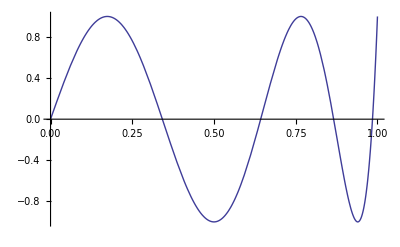

```mathematica
Plot[ChebyshevT[9,x],{x,0,1}]
```

```mathematica
hoe=ϕ''[x]+ω^2 ϕ[x];
phiSub[MM_]:=ϕ:>Function[x,Sum[a[nn] cheby[nn,x], {nn,0,MM}]]
grids[MM_,prec_]:=Table[1/2 (1-Cos[nn Pi/MM])//N[#,prec]&, {nn,0,MM}]
cof[MM_]:=Table[a[n],{n,0,MM}];
geneigs[mtx_]:=Eigensystem[mtx];
frequencies[MM_,prec_]:=SetPrecision[geneigs[cofMatrix],prec];
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((hoe/.phiSub[MM]/.x->#)&/@grids[MM,prec]))/.chebysub;
chebysub={Derivative[0,m_][cheby][n_,u_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,u],
cheby[n_,u_?NumberQ]->ChebyshevT[n,u]};
```

## Solution

```mathematica
Quit
```

```mathematica
eq1=32 u^3 AX[u]+32 Q^2 u^3 AX[u]-48 Q^2 u^5 AX[u]+4 u θ^2 AX[u]+12 ⅈ Ω AX[u]-13 ⅈ √3 u^3 Γ θ AY[u]+16 √3 Q u^3 φvx[u]-12 AX'[u]+28 u^4 AX'[u]+28 Q^2 u^4 AX'[u]-36 Q^2 u^6 AX'[u]+8 ⅈ u Ω AX'[u]+4 √3 Q u^4 φvx'[u]-4 u AX''[u]+4 u^5 AX''[u]+4 Q^2 u^5 AX''[u]-4 Q^2 u^7 AX''[u];
eq2=3 ⅈ √3 u^3 Γ θ AX[u]+8 u^3 AY[u]+8 Q^2 u^3 AY[u]-12 Q^2 u^5 AY[u]+u θ^2 AY[u]+3 ⅈ Ω AY[u]+4 √3 Q u^3 φvy[u]-3 AY'[u]+7 u^4 AY'[u]+7 Q^2 u^4 AY'[u]-9 Q^2 u^6 AY'[u]+2 ⅈ u Ω AY'[u]+√3 Q u^4 φvy'[u]-u AY''[u]+u^5 AY''[u]+Q^2 u^5 AY''[u]-Q^2 u^7 AY''[u];
eq3=8 √3 Q u AX[u]-4 ⅈ θ φxz[u]+4 √3 Q u^2 AX'[u]-5 φvx'[u]-ⅈ u θ φxz'[u]-u φvx''[u];
eq4=8 √3 Q u AY[u]-4 ⅈ θ φyz[u]+4 √3 Q u^2 AY'[u]-5 φvy'[u]-ⅈ u θ φyz'[u]-u φvy''[u];
eq5=4 √3 Q u (2-2 (1+Q^2) u^4+2 Q^2 u^6-ⅈ u Ω) AX[u]+(u θ^2+4 ⅈ Ω) φvx[u]+u θ Ω φxz[u]+4 √3 Q u^2 AX'[u]-4 √3 Q u^6 AX'[u]-4 √3 Q^3 u^6 AX'[u]+4 √3 Q^3 u^8 AX'[u]-5 φvx'[u]+5 u^4 φvx'[u]+5 Q^2 u^4 φvx'[u]-5 Q^2 u^6 φvx'[u]+ⅈ u Ω φvx'[u]-u φvx''[u]+u^5 φvx''[u]+Q^2 u^5 φvx''[u]-Q^2 u^7 φvx''[u];
eq6=4 √3 Q u (2-2 (1+Q^2) u^4+2 Q^2 u^6-ⅈ u Ω) AY[u]+(u θ^2+4 ⅈ Ω) φvy[u]+u θ Ω φyz[u]+4 √3 Q u^2 AY'[u]-4 √3 Q u^6 AY'[u]-4 √3 Q^3 u^6 AY'[u]+4 √3 Q^3 u^8 AY'[u]-5 φvy'[u]+5 u^4 φvy'[u]+5 Q^2 u^4 φvy'[u]-5 Q^2 u^6 φvy'[u]+ⅈ u Ω φvy'[u]-u φvy''[u]+u^5 φvy''[u]+Q^2 u^5 φvy''[u]-Q^2 u^7 φvy''[u];
eq7=ⅈ θ φvx[u]+(16 (1+Q^2) u^3-24 Q^2 u^5+5 ⅈ Ω) φxz[u]+ⅈ u θ φvx'[u]-5 φxz'[u]+9 u^4 φxz'[u]+9 Q^2 u^4 φxz'[u]-11 Q^2 u^6 φxz'[u]+2 ⅈ u Ω φxz'[u]-u φxz''[u]+u^5 φxz''[u]+Q^2 u^5 φxz''[u]-Q^2 u^7 φxz''[u];
eq8=ⅈ θ φvy[u]+(16 (1+Q^2) u^3-24 Q^2 u^5+5 ⅈ Ω) φyz[u]+ⅈ u θ φvy'[u]-5 φyz'[u]+9 u^4 φyz'[u]+9 Q^2 u^4 φyz'[u]-11 Q^2 u^6 φyz'[u]+2 ⅈ u Ω φyz'[u]-u φyz''[u]+u^5 φyz''[u]+Q^2 u^5 φyz''[u]-Q^2 u^7 φyz''[u];
```

```mathematica
eqn1=eq1/.Γ->3/2;
eqn2=eq2/.Γ->3/2;
eqn3=eq5;
eqn4=eq6;
eqn5=eq7;
eqn6=eq8;
```

```mathematica
grids[MM_,prec_]:=Table[1/2 (1-Cos[nn Pi/MM])//N[#,prec]&, {nn,0,MM}]
```

#### code:

```mathematica
XZsub[MM_]:=φxz:>Function[u,Sum[a[nn] cheby[nn,u], {nn,0,MM}]]
VXsub[MM_]:=φvx:>Function[u,Sum[b[mm] cheby[mm,u], {mm,0,MM}]]
AXsub[MM_]:=AX:>Function[u,Sum[c[kk] cheby[kk,u], {kk,0,MM}]]
YZsub[MM_]:=φyz:>Function[u,Sum[d[ll] cheby[ll,u], {ll,0,MM}]]
VYsub[MM_]:=φvy:>Function[u,Sum[e[ii] cheby[ii,u], {ii,0,MM}]]
AYsub[MM_]:=AY:>Function[u,Sum[gg[jj] cheby[jj,u], {jj,0,MM}]]

grids[MM_,prec_]:=Table[1/2 (1-Cos[nn Pi/MM])//N[#,prec]&, {nn,0,MM}]
```

```mathematica
XZcof[MM_]:=Table[a[n],{n,0,MM}];
VXcof[MM_]:=Table[b[n],{n,0,MM}];
AXcof[MM_]:=Table[c[n],{n,0,MM}];
YZcof[MM_]:=Table[d[n],{n,0,MM}];
VYcof[MM_]:=Table[e[n],{n,0,MM}];
AYcof[MM_]:=Table[gg[n],{n,0,MM}];
cof[MM_]:=Flatten[{XZcof[MM],VXcof[MM],AXcof[MM],YZcof[MM],VYcof[MM],AYcof[MM]}];
geneigs[mtx_]:=Eigensystem[{mtx/.Ω->0,Coefficient[mtx,Ω]}];
```

```mathematica
QNMroots[MM_,que_,key_,prec_]:=SetPrecision[Block[{Q=que,θ=key},geneigs[Join[xzMatrix[MM,prec], vxMatrix[MM,prec], axMatrix[MM,prec],yzMatrix[MM,prec], vyMatrix[MM,prec], ayMatrix[MM,prec]]]],prec];
xzMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn1/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
vxMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn2/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
axMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn3/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u-> #)&/@grids[MM,prec]))/.chebysub;
yzMatrix[MM_,prec_]:=
(Coefficient[#,cof[MM]]&/@
((eqn4/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
vyMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn5/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
ayMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn6/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u-> #)&/@grids[MM,prec]))/.chebysub;

chebysub={Derivative[0,m_][cheby][n_,u_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,u],
cheby[n_,u_?NumberQ]->ChebyshevT[n,u]};
```

```mathematica
bigMatrix[MM_,prec_]:=Join[xzMatrix[MM,prec], vxMatrix[MM,prec], axMatrix[MM,prec],yzMatrix[MM,prec], vyMatrix[MM,prec], ayMatrix[MM,prec]]
```

```mathematica
QNMroots[20,0,0,16]
```

{{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,«117»,-0.821996391070481-1.273178925113262 ⅈ,0,0,Indeterminate},{«1»}}

```mathematica
ayMatrix[20,30]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 ⅈ Ω | -5 | -5 ⅈ Ω | 15 | 5 ⅈ Ω | -25 | -5 ⅈ Ω | 35 | 5 ⅈ Ω | -45 | -5 ⅈ Ω | 55 | 5 ⅈ Ω | -65 | -5 ⅈ Ω | 75 | 5 ⅈ Ω | -85 | -5 ⅈ Ω | 95 | 5 ⅈ Ω | ⅈ θ | 0 | -ⅈ θ | 0 | ⅈ θ | 0 | -ⅈ θ | 0 | ⅈ θ | 0 | -ⅈ θ | 0 | ⅈ θ | 0 | -ⅈ θ | 0 | ⅈ θ | 0 | -ⅈ θ | 0 | ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.7323277438387441613567305538×10^-6+3.7321155932575957507120736387×10^-6 Q^2+5. ⅈ Ω | -4.999999964100665648858854627+3.5897429821986614145016686354×10^-8 Q^2+0.043090807917017958334859133073 ⅈ Ω | -0.14774364454963938101844645044-3.7314791736712900989638687335×10^-6 Q^2-4.99931790369214399844837372913733 ⅈ Ω | 14.9968167762093343026010161602987-1.076816246223233893623936075×10^-7 Q^2-0.12926215984975831845813366821 ⅈ Ω | 0.59090366397159609267914768129+3.7295700864089937690882070914×10^-6 Q^2+4.9972717641098068945406596681513 ⅈ Ω | -24.984085273940841664904209138591+1.7943382756400434585640169947×10^-7 Q^2+0.21540272220011782042618345689 ⅈ Ω | -1.3293046558344706794936430287-3.7263888459199514728214731283×10^-6 Q^2-4.9938620292470795659450667000559 ⅈ Ω | 34.955443360445011305415145447541-2.5113271964816566076381871952×10^-7 Q^2-0.301491975651121273314531137 ⅈ Ω | 2.3626481187757297080629650593+3.7219363094841893807089699904×10^-6 Q^2+4.9890894456621129362394909659818 ⅈ Ω | -44.90453410703507323606331794901+3.2275699523418594831219308546×10^-7 Q^2+0.38750941149128599951813420132 ⅈ Ω | -3.6905162696691022026698668913-3.7162136770094736261880233459×10^-6 Q^2-4.9829550583291365645874103481426 ⅈ Ω | 54.825007818576268409311202237903-3.9428536737874840111234246923×10^-7 Q^2-0.47343453585396799222804411929 ⅈ Ω | 5.3123721623712855789239746369+3.7092224907471142599322167748×10^-6 Q^2+4.9754602104313234646428280370852 ⅈ Ω | -64.710524096998213856044831663472+4.6569657317066917378627419753×10^-7 Q^2+0.55924687395385785278460030172 ⅈ Ω | -7.2275598403469048540002607262-3.7009646349266766877225395277×10^-6 Q^2-4.966606543094539937642542708861 ⅈ Ω | 74.5547539023957009761160561144-5.3696937906028390061013009262×10^-7 Q^2-0.64492597431981305592886456671 ⅈ Ω | 9.4353045231347073996234463893+3.6914423353096803269589938827×10^-6 Q^2+4.956395995062030274061740383922 ⅈ Ω | -84.35138161118315495303068368546+6.0808258618218539097029352819×10^-7 Q^2+0.73045141302321376322592621697 ⅈ Ω | -11.934712826609766013426816959-3.6806581586623819023231068009×10^-6 Q^2-4.944830802310097238630321750982 ⅈ Ω | 94.09410707076866191605361303375-6.7901503567010695410196045601×10^-7 Q^2-0.81580279790103022633123717436 ⅈ Ω | 14.724773016988263591914396738+3.6686150121477584663987061716×10^-6 Q^2+4.931913497604850302936543862741 ⅈ Ω | 1. ⅈ θ | 0.012311659404862273809959752307 ⅈ θ | -0.999772634564047999482791243045775 ⅈ θ | -0.036931245886842982685717900189 ⅈ θ | 0.99909059569512695975699756895311 ⅈ θ | 0.061539636234194499922634556508 ⅈ θ | -0.99795405569785277971111690905878 ⅈ θ | -0.086129369185666941662529664894 ⅈ θ | 0.99636330170595771097581262752439 ⅈ θ | 0.11069298772216455578850692889 ⅈ θ | -0.9943187356213573017713356602275 ⅈ θ | -0.13522304076240702337773434567 ⅈ θ | 0.9918208740288607439550611933194 ⅈ θ | 0.15971208485739068183478592771 ⅈ θ | -0.9888703480865412452341122406736 ⅈ θ | -0.18415268588330718002183152263 ⅈ θ | 0.9854679033917877923613873214254 ⅈ θ | 0.20853742073257736798155334841 ⅈ θ | -0.9816143998230644110283264433722 ⅈ θ | -0.23285887900265858097096438345 ⅈ θ | 0.9773108113574077632262550366334 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00023448476495391684923227388355+0.00023427412747153358732057394584 Q^2+5. ⅈ Ω | -4.9999910339833808150202619547+8.9584993977988770931210896426×10^-6 Q^2+0.17130219296696249759246233317 ⅈ Ω | -0.58755565731066390166622517352-0.00023364271959901568698599487448 Q^2-4.9892204093127504448177938117531 ⅈ Ω | 14.949668387506084283051968561196-0.000026833434166662315517893283945 Q^2-0.51326174579726422144199824634 ⅈ Ω | 2.3457674213995958899182902676+0.00023175118503168092926865127633 Q^2+4.956918935880137588786885515467 ⅈ Ω | -24.74868981880855022062713556344+0.000044582343428882243493568586127 Q^2+0.85328890569151996390448489934 ⅈ Ω | -5.2636313673756742217340408182-0.00022860758085500235570197146204 Q^2-4.903207358750470745030439094468 ⅈ Ω | 34.29747772502623546786950067058-0.00006212176482914483974362411444 Q^2-1.1901024255504998422372061873 ⅈ Ω | 9.3224729178549821229228421253+0.00022422530202887597432378917473 Q^2+4.828271587219677347837039573931 ⅈ Ω | -43.49774032058592623899067131837+0.000079369065901513148611623523307 Q^2+1.5224315582112330409497487516 ⅈ Ω | -14.496265259966384359100988405-0.00021862303123518977751136717403 Q^2-4.73237107836352123582386989895 ⅈ Ω | 52.2529785767141327810929731442-0.000096242771863759360815475755911 Q^2-1.8490202117862948667364365991 ⅈ Ω | 20.751746399652514787719213992+0.00021182466890682839622199420807 Q^2+4.61583802399736236524508436267 ⅈ Ω | -60.4689858058204510454525873952+0.00011266288926699316697301905459 Q^2+2.1686310605232440321531654834 ⅈ Ω | -28.04856888908602569446186962-0.00020385924367957260768760737751 Q^2-4.47907630946984644671374048967 ⅈ Ω | 68.0543378352878691604897673174-0.00012855122434020312551834732233 Q^2-2.4800495986971437483952503241 ⅈ Ω | 36.339481652680108160404403087+0.00019476080357598914817485626818 Q^2+4.32256024737267031912486450563 ⅈ Ω | -74.9208717494853442397421017496+0.00014383169488708699969710817363 Q^2+2.7820881252143398834139911001 ⅈ Ω | -45.570543213604830750490809305-0.00018456828829703425368174764539 Q^2-4.14683308991553455549891134842 ⅈ Ω | 80.9841512204830756547535912827-0.00015843063461413672749170233519 Q^2-3.0735896468066798656263955592 ⅈ Ω | 55.681365501594637708902924895+0.00017332538306249644743659495122 Q^2+3.95250532437166503942826174654 ⅈ Ω | 1. ⅈ θ | 0.048943483704846427883560666621 ⅈ θ | -0.99640680310425014827259793725103 ⅈ θ | -0.14659596634958536680144972598 ⅈ θ | 0.9856415580435912890579726214866 ⅈ θ | 0.24354583724939208821928876344 ⅈ θ | -0.9677472535875786392019391551979 ⅈ θ | -0.33932749438301218724039765294 ⅈ θ | 0.942795377466255164899136237338 ⅈ θ | 0.43347953503157334504438191544 ⅈ θ | -0.910885676559502612714063835199 ⅈ θ | -0.52554641670718652816997480029 ⅈ θ | 0.872145822196921670004877615161 ⅈ θ | 0.61508009935674331671969254376 ⅈ θ | -0.826730981599393233287948843237 ⅈ θ | -0.70164166358724421680295699275 ⅈ θ | 0.774823296782903831824758503476 ⅈ θ | 0.78480289973082110862387135352 ⅈ θ | -0.71663127253078167831522601538 ⅈ θ | -0.86414786265498530862773503623 ⅈ θ | 0.65238907532134848961690519909 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0025895929445449853032434185814+0.0025780567180039579925148854214 Q^2+5. ⅈ Ω | -4.9997794931750287210162314926+0.00021958999017969577729787927825 Q^2+0.38147716534071248174101650005 ⅈ Ω | -1.3104766940045075550545429621-0.0025435850838812367739383811331 Q^2-4.946541900037246220607797744785 ⅈ Ω | 14.7498724806404013918413194709-0.00065365530060459648988968814615 Q^2-1.1373101154246387356391300991 ⅈ Ω | 5.1927052409810107565957954032+0.0024408983774438644320361735031 Q^2+4.78708490854086540300366796986 ⅈ Ω | -23.75791796718570094033219595+0.0010724770604352304048560260169 Q^2+1.8718942859814791338927708264 ⅈ Ω | -11.525899849820160922520238813-0.0022721676678130348390101285736 Q^2-4.5243667004543099299244695991 ⅈ Ω | 31.5502568494280751470340624508-0.0014662259836720008951036590943 Q^2-2.5714466289682061140575260004 ⅈ Ω | 20.107493620694374137056125883+0.0020409665725681719654931056723 Q^2+4.16290277569495251054819740025 ⅈ Ω | -37.6843393900600599685130871551+0.0018255661951098579145007133453 Q^2+3.2227522530838083862907086314 ⅈ Ω | -30.660255156721419718442666464-0.0017522048170579161158377793108 Q^2-3.70891625063028645155229535051 ⅈ Ω | 41.7602783542503343704440757543-0.0021418402790960557533050440473 Q^2-3.8133796745448685985613946774 ⅈ Ω | 42.838505295902522972136028516+0.001412036815519379680048194926 Q^2+3.1702410134561428961403069007 ⅈ Ω | -43.4315308756914404519378626068+0.0024072422584471933534985955519 Q^2+4.3318842635477879386002208321 ⅈ Ω | -56.235904985120968640241759332-0.001027746841021273959209002207 Q^2-2.5561996661899928448862253014 ⅈ Ω | 42.414487381842469407565937283-0.0026149754016598703169500827688 Q^2-4.7679968070868098271555133189 ⅈ Ω | 70.394665405813910084675282647+0.0006076127551236992832188150474 Q^2+1.8774580477219794008600324313 ⅈ Ω | -38.496765724843099829507212789+0.0027593920089738142523979464093 Q^2+5.1127943231506682216359656234 ⅈ Ω | -84.816003730320160696342691545-0.000160750640082553731993447802 Q^2-1.145858478686820443575378193 ⅈ Ω | 31.544032196593001981782281331-0.0028361126280967064333078169934 Q^2-5.3588505171329891994887959186 ⅈ Ω | 98.971643233752509922823896529-0.0003030569896526134493918822282 Q^2+0.3742341849078347570650492254 ⅈ Ω | 1. ⅈ θ | 0.10899347581163213764029042859 ⅈ θ | -0.9821806333457487402025992482616 ⅈ θ | -0.32439083449035142761762786718 ⅈ θ | 0.929075344302949007184426604862 ⅈ θ | 0.53206555924159987092814918266 ⅈ θ | -0.841736697888796807546158885367 ⅈ θ | -0.72702231289160867679777556076 ⅈ θ | 0.721899499612124282501656930395 ⅈ θ | 0.90449283910437117827244112173 ⅈ θ | -0.57195190357076101536705217585 ⅈ θ | -1.0600217389769372392757503951 ⅈ θ | 0.39489558387574007757469445134 ⅈ θ | 1.1895472821390896029659634528 ⅈ θ | -0.19429557866893829976965155454 ⅈ θ | -1.2894759611192699780979901279 ⅈ θ | -0.0257794252114249421166319922 ⅈ θ | 1.35674959083711012251340915 ⅈ θ | 0.260825451245264550692038009 ⅈ θ | -1.3889038661267590505523194316 ⅈ θ | -0.50597918596348325194333770874 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.013932022500210303590826331269+0.013741461123121631354551547443 Q^2+5. ⅈ Ω | -4.9979212659909952941695628439+0.0020521967286018823321748624344 Q^2+0.66844051968768401564197303986 ⅈ Ω | -2.3051564058695751976544809736-0.013176727624412112068798075522 Q^2-4.835864712030895112690480565984 ⅈ Ω | 14.2279477295540855533212000174-0.0060097236972141691337085048359 Q^2-1.9670084971874737120511467086 ⅈ Ω | 8.9559542660146063419819349579+0.011519174633741826341904242 Q^2+4.35210638160104002701654083325 ⅈ Ω | -21.2203845670141080650857761103+0.0095355116432486057773558072049 Q^2+3.1525429028314151261987509826 ⅈ Ω | -19.312942530538991664587917285-0.0088766551108964001266711271223 Q^2-3.57425514398455244365475971701 ⅈ Ω | 24.6792979972837721376420947668-0.012370786406910181388392737975 Q^2-4.1559520266061828437606679186 ⅈ Ω | 32.337069167089179538948540815+0.005422068584340601979776556063 Q^2+2.5435049251151779965346755612 ⅈ Ω | -23.589574388472931530326114528+0.014298685877290561264868732251 Q^2+4.9172359079448629287246683262 ⅈ Ω | -46.675426639199126478798573824-0.001383456837346267962250274761 Q^2-1.3147432305140065127301961416 ⅈ Ω | 17.304245464121377176353317481-0.015157780744249409625041774849 Q^2-5.3885283486337143442609972614 ⅈ Ω | 60.755826370475630721480217895-0.002969123911367216756100939805 Q^2-0.0460815447347794821380098262 ⅈ Ω | -5.608486556654427849073368351+0.014852550789950188990679575863 Q^2+5.5365759006288394692838771722 ⅈ Ω | -72.898553229051983998852323504+0.00733926035867820915048496997 Q^2+1.465136254586731350010579535 ⅈ Ω | -11.24407996734540800150038761-0.013360221107079974794860300399 Q^2-5.3445366697589216476084762566 ⅈ Ω | 81.43865056014670142773245658-0.011421537582436087833027664978 Q^2-2.8642786300998890736348695152 ⅈ Ω | 32.525586159655621077389869937+0.0107335497501694759096897415 Q^2+4.8130119543993176054618058113 ⅈ Ω | -84.851375679033852318740037187+0.01491966535029061795106167928 Q^2+4.1648697852674465746373903947 ⅈ Ω | -57.059704027670936502254255612-0.00709936749526828663742471052 Q^2-3.960257868374100887638041758 ⅈ Ω | 81.873153936377924557248362079-0.01756439872778679913903118058 Q^2-5.2916494417428777613251390313 ⅈ Ω | 1. ⅈ θ | 0.19098300562505257589770658282 ⅈ θ | -0.945288237343631704230160188661 ⅈ θ | -0.55901699437494742410229341718 ⅈ θ | 0.784478923788934346249340204383 ⅈ θ | 0.88601716113256605047950039304 ⅈ θ | -0.52738014398455244365475971701 ⅈ θ | -1.1471313728906052840383600314 ⅈ θ | 0.18978054174581310247102091886 ⅈ θ | 1.3211350641214009904022228433 ⅈ θ | 0.2073604044039522268267886387 ⅈ θ | -1.3916321642907553624688673174 ⅈ θ | -0.63899221553015667890215315749 ⅈ θ | 1.3480196823540039549014871486 ⅈ θ | 1.0772724678471648468197564218 ⅈ θ | -1.1861673959080787780778760927 ⅈ θ | -1.4930236316167763365879705878 ⅈ θ | 0.90877716845491603765293599895 ⅈ θ | 1.8572784596952545859605268545 ⅈ θ | -0.5254011777407120198130136341 ⅈ θ | -2.1428400086406590144440944067 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.050252531694167329194089465266+0.048635912065751423025580498947 Q^2+5. ⅈ Ω | -4.9885010736238830412579158947+0.011153668200497563359539914474 Q^2+1.0251262658470836645970447326 ⅈ Ω | -3.5601212985703493178784302211-0.043924737219423235913634611578 Q^2-4.61396103067892771960759925894 ⅈ Ω | 13.165921476490113762751458361-0.031580872062130390000232658683 Q^2-2.9371843353822908385073881684 ⅈ Ω | 13.286426740299788850925119773+0.030511032205251812612536022635 Q^2+3.50367965644035742679746691369 ⅈ Ω | -16.275491543445645769193158831+0.046634673691624166310789133754 Q^2+4.4508252147247766082515831789 ⅈ Ω | -26.948496707044650642474079002-0.01045766373197301207333399171 Q^2-1.8072961799571730212964114611 ⅈ Ω | 11.993050160040469221790402268-0.053588543619001842348154105655 Q^2-5.3525681002002761790171368779 ⅈ Ω | 41.158239729055930215719295511-0.01310728891756650576114890586 Q^2-0.2622745480488707985843793011 ⅈ Ω | 0.587642925213184326206073898+0.050883805414008081713893743266 Q^2+5.5011622709717872132823161231 ⅈ Ω | -51.979819985615565862119507295+0.03641518329654555664232135499 Q^2+2.441389325160601170138457021 ⅈ Ω | -20.693083672358033918382991276-0.03837957860942200515105674082 Q^2-4.8451856733130747368566062153 ⅈ Ω | 55.601194517846380776143212057-0.055575391788909847536925120214 Q^2-4.4456800010290983240872960232 ⅈ Ω | 45.86486142944793192253518018+0.01741724877296318401942612919 Q^2+3.4307739992229792389967258013 ⅈ Ω | -49.022610445285049087809616724+0.06712267392548301820756118439 Q^2+6.0028065511119130204698571911 ⅈ Ω | -72.221621106598146319690524757+0.009312309315002068441717132798 Q^2-1.398532590121948685316223914 ⅈ Ω | 30.66220108619850022818309981-0.068523653740932233722307732809 Q^2-6.8844330355428920086458451895 ⅈ Ω | 94.96231492651164197447936036-0.03808630477051364871756937741 Q^2-1.030178527799746652097335556 ⅈ Ω | -0.786767260657774127852877855+0.05857646447369083437094733696 Q^2+6.933944471381867437535893878 ⅈ Ω | -109.05102786707724729515886534+0.06461684444132098097580682534 Q^2+3.576268119363018210481292048 ⅈ Ω | -38.30404419579959824985326474-0.03764934990578719000542090573 Q^2-6.086829550402675583347240448 ⅈ Ω | 1. ⅈ θ | 0.2928932188134524755991556379 ⅈ θ | -0.871320343559642573202533086315 ⅈ θ | -0.82842712474619009760337744842 ⅈ θ | 0.50367965644035742679746691369 ⅈ θ | 1.2196699141100893566993667284 ⅈ θ | 0.04993686707645816770147763368 ⅈ θ | -1.39124278936389925909598928 ⅈ θ | -0.70834235991434604259282292211 ⅈ θ | 1.2964804192278635481342352105 ⅈ θ | 1.372003509206450058782440941 ⅈ θ | -0.92417478527522339174841682105 ⅈ θ | -1.9352723609434443666801189453 ⅈ θ | 0.301195559810743274459053029 ⅈ θ | 2.299628553163180311394046329 ⅈ θ | 0.5093800874162347363055700353 ⅈ θ | -2.3864374660076848347355017537 ⅈ θ | -1.4145051215501797369254857378 ⅈ θ | 2.1477603783281123298140051678 ⅈ θ | 2.301161710131945614735967071 ⅈ θ | -1.573940597957785291639180463 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.14008788282918604498604475535+0.13116143049546470968073028844 Q^2+5. ⅈ Ω | -4.9548857099395980381801812287+0.042431237239914729234319343718 Q^2+1.4427516169763440479095291588 ⅈ Ω | -5.0598854983183444890456298989-0.10589886518547754440019197814 Q^2-4.23535550797588986674851378041 ⅈ Ω | 11.3113412628343419951790714558-0.11308924854941381158970034861 Q^2-3.9430131731487705200169643991 ⅈ Ω | 17.585961775205119584836496393+0.03777116701134575185865852837 Q^2+2.1290974785548316281645012102 ⅈ Ω | -8.3029203721612585874815530295+0.14513514243598722517643020211 Q^2+5.3768142193176254740426750769 ⅈ Ω | -31.730335401792883547176406442+0.05227997404316832308970830688 Q^2+0.7974500550049312187124619764 ⅈ Ω | -6.373426629441797232802424664-0.12514758889778495944220136827 Q^2-5.3115167985163324267275292353 ⅈ Ω | 39.692641713503698462609907973-0.13564659669495640244524181795 Q^2-3.8056679782646561191565408004 ⅈ Ω | 30.331622631027635877265656257+0.05486593942660560619682858231 Q^2+3.6686940296499587966522560132 ⅈ Ω | -34.499844610457590427303775842+0.1838641855800750002742701434 Q^2+6.1061572569209818552485348327 ⅈ Ω | -56.736257397248269165184524422+0.04856871755235837451807407792 Q^2-0.7526681972828936639432668601 ⅈ Ω | 12.60402027476562497865840357-0.176670780681428050190075768 Q^2-7.040153166412261090166353009 ⅈ Ω | 75.975229055357677035745958205-0.1564812838232782456560759371 Q^2-2.805477280049328581914565254 ⅈ Ω | 24.32110515796401964843032036+0.1082638140356127333081253265 Q^2+6.236978849125010547916098329 ⅈ Ω | -78.387119474888515513508695923+0.2358074757849330336084955489 Q^2+6.178171660180870592025875597 ⅈ Ω | -68.967876572197486129444492272+0.00991631343400617611765899787 Q^2-3.7130494778043504209727451976 ⅈ Ω | 57.356038153312713273676892263-0.2578499335660718609232638173 Q^2-8.5198653179705658422303159006 ⅈ Ω | 109.61440701748751875725828589-0.1507569723004273952011386376 Q^2-0.11051614048758970941284841 ⅈ Ω | -11.9387749661864248558473759+0.2065166484346421262124921702 Q^2+9.157002721979585995691949932 ⅈ Ω | -132.8063191851312538429714331+0.2772530029023589661782425815 Q^2+4.478135640188654280411440411 ⅈ Ω | 1. ⅈ θ | 0.41221474770752687083129404536 ⅈ θ | -0.745118502658629955582837926804 ⅈ θ | -1.0965563602933945675078373807 ⅈ θ | 0.05265687473116296124306174126 ⅈ θ | 1.3963401337265894704475043177 ⅈ θ | 0.87800782954358985483139479087 ⅈ θ | -1.1661239840020043711744096671 ⅈ θ | -1.7680675165121842345754986703 ⅈ θ | 0.4002653270793634707298045047 ⅈ θ | 2.3271625347343037036210903149 ⅈ θ | 0.758514269671995399527422486 ⅈ θ | -2.326359255649319200022690986 ⅈ θ | -2.0455191213251723203021352209 ⅈ θ | 1.659808503075082318043725096 ⅈ θ | 3.13057652335422245998227027 ⅈ θ | -0.3807407417588098441410342471 ⅈ θ | -3.693083424195812174346139771 ⅈ θ | -1.297378453080213873584762921 ⅈ θ | 3.499631785967031095160013621 ⅈ θ | 3.036462253253411627676183984 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.32555966537354853888583951225+0.28916294436838099895470383473 Q^2+5. ⅈ Ω | -4.8611260389097096794313684925+0.12438326441007629133992922305 Q^2+1.9110332509115862295385707177 ⅈ Ω | -6.7684835054834844203675320834-0.19082360382527536718648876063 Q^2-3.65843131531398566467326369516 ⅈ Ω | 8.4038721562702607037834021812-0.29977799777521380221192928834 Q^2-4.8378106729575002066796534946 ⅈ Ω | 20.946171433022632712106868046-0.05171489188905576728626985639 Q^2+0.2114409393915503922585618519 ⅈ Ω | 2.632320930395518572652012151+0.29140576325059061624199185034 Q^2+5.4426880657233141373239170706 ⅈ Ω | -30.29015271367676100729845715+0.30556056666878577373734098456 Q^2+3.8330509217615235279879855375 ⅈ Ω | -26.790630383257147047073063277-0.08167526894003911753096312253 Q^2-3.2535123585441841398589064219 ⅈ Ω | 22.091577293953815410514228962-0.420482142749251498931174011 Q^2-6.6296548892944447387968554936 ⅈ Ω | 52.011909984343681012587727306-0.2396913297174984323730273355 Q^2-1.019650174677089366250478308 ⅈ Ω | 8.362390587816442711419650443+0.3031048713240571849202873983 Q^2+6.7363591537363423392735264503 ⅈ Ω | -60.802515262735489346524197643+0.511159463673262484690047253 Q^2+5.713320401812501838163830554 ⅈ Ω | -52.928741188776996143434574709+0.030799006824128846966730626 Q^2-3.725772678956125990319858006 ⅈ Ω | 39.269323491828097265288229706-0.5715084513003069961928607874 Q^2-8.8226644928098565315667007274 ⅈ Ω | 91.898021000187213187565249541-0.4508405187211194651246117019 Q^2-1.569525521829217276964988271 ⅈ Ω | 14.06260939329881144167634583+0.3386307253412720295679876321 Q^2+8.779711312690984645078671002 ⅈ Ω | -101.64404218676816434837785478+0.7593522593268360097137932292 Q^2+7.28583498710341188796622004 ⅈ Ω | -84.064575765122408164766912822+0.1396780022756215627757652623 Q^2-5.111903085344026327795309258 ⅈ Ω | 65.86656187531394366190066106-0.775115460173138310874807466 Q^2-11.16892774684508325042910503 ⅈ Ω | 142.23047983431660728911761485-0.6880693865273398500267886441 Q^2-1.27232308343769705934245844 ⅈ Ω | 14.361226436058307025736546+0.4201677718727017186278134992 Q^2+11.41007616147389656164743068 ⅈ Ω | 1. ⅈ θ | 0.54600950026045320843959163364 ⅈ θ | -0.55281043843799522155775456505 ⅈ θ | -1.3124688354078110864329353887 ⅈ θ | -0.56655990850355460085917132778 ⅈ θ | 1.2478360584551935074933033171 ⅈ θ | 1.784256486344625715585041063 ⅈ θ | -0.2254683215520667632794967894 ⅈ θ | -2.4174419871963342448275640848 ⅈ θ | -1.4211319598948123687222061393 ⅈ θ | 1.973211909348918805356612462 ⅈ θ | 3.006301474440841576209576488 ⅈ θ | -0.3862131149778510036697618183 ⅈ θ | -3.7546959105821661444055435304 ⅈ θ | -1.902906307839379155017170147 ⅈ θ | 3.122702321246885639521106922 ⅈ θ | 4.0691832812259196231149834422 ⅈ θ | -1.056053037867280614995692723 ⅈ θ | -5.191770828046922309776601329 ⅈ θ | -1.921645913062283700360578924 ⅈ θ | 4.610458356171477070639908532 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.65983005625052575897706582817+0.54168974936508239779569190904 Q^2+5. ⅈ Ω | -4.6438036285392689077484387283+0.29667234954821148462473978804 Q^2+2.4184405196876840156419730399 ⅈ Ω | -8.5972052030948265862054230646-0.2436758059448724817810978397 Q^2-2.8514411867181585211508009433 ⅈ Ω | 4.2381376130126562913259208956-0.60783887068737483370993344351 Q^2-5.4407889043741062097389880921 ⅈ Ω | 22.152886955545291151081589193-0.3944153709346920000882568347 Q^2-2.1124583478507245716303013364 ⅈ Ω | 15.251982495275010245674520746+0.2971785176642038798149463535 Q^2+4.2009423938481245040889492532 ⅈ Ω | -19.78433600746552979444016032+0.7970174768684415532952319594 Q^2+6.3715412570313157198721332285 ⅈ Ω | -41.424976739329270035483857417+0.4620096728411632283626550439 Q^2+0.9190404241746071171343994818 ⅈ Ω | -10.72249411969011925887257176-0.5129877150596321645256141076 Q^2-6.5971221828496252883940221126 ⅈ Ω | 46.913955490008525469002907834-1.070865120772457751676371176 Q^2-6.7895711707140481162479464873 ⅈ Ω | 56.52111730118341385949350996-0.4004543013382367658382784727 Q^2+1.859674706342544328227073598 ⅈ Ω | -11.41958576526149760835948406+0.9275137811065968025545708387 Q^2+9.354842297358561843479038338 ⅈ Ω | -82.77821297685493106155429745+1.33911701821986455347630132 Q^2+5.534974614573053255417657583 ⅈ Ω | -56.74353679538142972716003485+0.093542203163473058825025179 Q^2-6.167499145128823365544824498 ⅈ Ω | 55.6155719975040242341613476-1.522077422302577719276093297 Q^2-11.16753925279020406400594077 ⅈ Ω | 117.16423029439672308549709179-1.446508192847016665307531138 Q^2-1.859138083469650036019244598 ⅈ Ω | 29.10362049969743317414661482+0.5542314318767441086751322565 Q^2+11.039589586283591600435624072 ⅈ Ω | -118.72722719631270890366449317+2.18161632238289226524288408 Q^2+10.596612669437783130915210898 ⅈ Ω | -132.06556501472747756718823187+1.192724339922004219023433933 Q^2-4.107682017946111797472746256 ⅈ Ω | 35.45674826220817741235943534-1.553911158287066525496373111 Q^2-14.813858945470502385363820401 ⅈ Ω | 185.7247569291014514456836962-2.676290885459139969141833155 Q^2-6.691072920091340995486166921 ⅈ Ω | 1. ⅈ θ | 0.69098300562505257589770658282 ⅈ θ | -0.28381372890605284038360031444 ⅈ θ | -1.4131189606246319687160539203 ⅈ θ | -1.2948308900386188908631007075 ⅈ θ | 0.6283259744144075293286994497 ⅈ θ | 2.407145014062631439744266457 ⅈ θ | 1.393648367265552708140653449 ⅈ θ | -1.8744687966677341063815141788 ⅈ θ | -3.3448901664165487774626808164 ⅈ θ | -0.4597780550393955880081625579 ⅈ θ | 3.667325098310514074251358874 ⅈ θ | 3.459143510643389367221685154 ⅈ θ | -1.595730839940907240619291202 ⅈ θ | -5.247230173457394196635652328 ⅈ θ | -2.185044731656021170318669357 ⅈ θ | 4.315742974493153320371356961 ⅈ θ | 5.7218026800619380071110447946 ⅈ θ | -0.557160412748049951241731472 ⅈ θ | -6.7962449612380473066260745626 ⅈ θ | -4.42024443702767152798102631 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.200567213182581161855096287+0.88019458644934891853889491818 Q^2+5. ⅈ Ω | -4.2087834973097474467266872806+0.59415534187808604983349242265 Q^2+2.9524793723591919584646313819 ⅈ Ω | -10.362235752500114003785228347-0.1470547682477893258277917653 Q^2-1.7977873470261733583529363753 ⅈ Ω | -1.213766054733816234909908078-0.9313362221110975627488348549 Q^2-5.5558782808254776802923793562 ⅈ Ω | 19.854048956854812005160755687-1.106864738933819628438045137 Q^2-4.5173899607038559449712735861 ⅈ Ω | 26.667752411129994389031956158-0.2690060712725255295072349549 Q^2+1.458323947867791249977596651 ⅈ Ω | 0.025675525390088148962814686+1.108371334481081462650809794 Q^2+7.1340434405248382700148940442 ⅈ Ω | -40.244049541105695554369254378+1.735462530578585118479996069 Q^2+6.016120348331844395043036972 ⅈ Ω | -45.649298814536175913952736738+0.6512929702748732416669125185 Q^2-2.216935089425332086371308272 ⅈ Ω | 5.790866368088879345672029596-1.476310415042833714126913887 Q^2-9.4758465270621263556918677665 ⅈ Ω | 68.708630818652524079658695098-2.51991290778876547130356903 Q^2-6.959607548073039190603362688 ⅈ Ω | 65.73684209187423443049186032-0.9464635543692414666580450627 Q^2+4.196581540204504787175520715 ⅈ Ω | -21.13039059296462580538855518+2.124958662827010409400378765 Q^2+12.18181449994369552533565726 ⅈ Ω | -107.0301022872755611279778121+3.463935777355326262476251638 Q^2+6.906931824864073456292720166 ⅈ Ω | -82.68088620345356672909302878+1.048227411202328360177493421 Q^2-7.339552518984693386607002582 ⅈ Ω | 51.24913259952292805027821752-3.143987483851379288511910748 Q^2-14.755906660457107260272663049 ⅈ Ω | 154.42854915509611057714716849-4.513795382836302520394869265 Q^2-5.522112564462425326385839462 ⅈ Ω | 89.91249232738956588409486643-0.807105786651582467981016582 Q^2+11.40591139269312786353790684 ⅈ Ω | -100.443565857701059337402425+4.593458580079539438807219787 Q^2+16.66144737537425014551260232 ⅈ Ω | -206.9156926979198117285213494+5.545916187923740408383556274 Q^2+2.62112311493419713565770899 ⅈ Ω | -79.41102323643107738216494487+0.051698027539827149119088193 Q^2-15.99166925014138664070927749 ⅈ Ω | 1. ⅈ θ | 0.84356553495976913098989468053 ⅈ θ | 0.06740421765794221388235454156 ⅈ θ | -1.3301293916967262311145877546 ⅈ θ | -2.0036704663273647702921178152 ⅈ θ | -0.5035178841811311810612025571 ⅈ θ | 2.2721509622929210355322386671 ⅈ θ | 3.1484316886306476014551186799 ⅈ θ | 0.3048157849493811122757122993 ⅈ θ | -3.6860976699597000203973376414 ⅈ θ | -4.005803284173163085847079242 ⅈ θ | 0.602750118373895064324654965 ⅈ θ | 5.355320210179177728141194956 ⅈ θ | 4.328490689428217376498967306 ⅈ θ | -2.196048475589840844376583599 ⅈ θ | -7.0097921408119418936290087597 ⅈ θ | -3.924215975432069539311782944 ⅈ θ | 4.35359307809133042735499105 ⅈ θ | 8.355607581964791161916434391 ⅈ θ | 2.680915371310553804605396261 ⅈ θ | -6.864735271289345211237051141 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.+1.25 Q^2+5. ⅈ Ω | -3.4375+1.015625 Q^2+3.5 ⅈ Ω | -11.75+0.25 Q^2-0.5 ⅈ Ω | -7.625-0.96875 Q^2-5. ⅈ Ω | 13.-2. Q^2-6.5 ⅈ Ω | 32.5625-1.796875 Q^2-2.5 ⅈ Ω | 24.5+0.125 Q^2+5. ⅈ Ω | -16.9375+2.703125 Q^2+9.5 ⅈ Ω | -59.+3.625 Q^2+5.5 ⅈ Ω | -52.625+1.28125 Q^2-5. ⅈ Ω | 15.25-3.125 Q^2-12.5 ⅈ Ω | 91.0625-5.734375 Q^2-8.5 ⅈ Ω | 92.-3.25 Q^2+5. ⅈ Ω | -7.9375+3.265625 Q^2+15.5 ⅈ Ω | -128.75+8.125 Q^2+11.5 ⅈ Ω | -142.625+5.78125 Q^2-5. ⅈ Ω | -5.-3.125 Q^2-18.5 ⅈ Ω | 172.0625-10.796875 Q^2-14.5 ⅈ Ω | 204.5-8.875 Q^2+5. ⅈ Ω | 23.5625+2.703125 Q^2+21.5 ⅈ Ω | -221.+13.75 Q^2+17.5 ⅈ Ω | 1. ⅈ θ | 1. ⅈ θ | 0.5 ⅈ θ | -1. ⅈ θ | -2.5 ⅈ θ | -2. ⅈ θ | 1. ⅈ θ | 4. ⅈ θ | 3.5 ⅈ θ | -1. ⅈ θ | -5.5 ⅈ θ | -5. ⅈ θ | 1. ⅈ θ | 7. ⅈ θ | 6.5 ⅈ θ | -1. ⅈ θ | -8.5 ⅈ θ | -8. ⅈ θ | 1. ⅈ θ | 10. ⅈ θ | 9.5 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.0930936890464974054462677127+1.541898691873694124976511503 Q^2+5. ⅈ Ω | -2.2054998862407809107569095621+1.486480582811271966473846638 Q^2+4.0475206276408080415353686181 ⅈ Ω | -12.316722278010857992158262919+1.03721013982670940395710085 Q^2+1.018033023697982283828959375 ⅈ Ω | -14.142745078559737371423316454-0.283214268279988307268605332 Q^2-3.6365542380445562596288696445 ⅈ Ω | 1.561981872522681598357465263-2.334466018364825311732014711 Q^2-7.4470116215535777240645812789 ⅈ Ω | 28.480342143736464284880945418-3.872579599865616275545590293 Q^2-6.7804851144572663125117758664 ⅈ Ω | 43.471417449735572071073862989-3.126729910314132728419999251 Q^2-0.258064916557318347719227899 ⅈ Ω | 23.00869950785849117986562411+0.596556658860111286818000631 Q^2+8.444510857069677477409104774 ⅈ Ω | -31.03970075309888425846452783+5.484462896419874111117324104 Q^2+12.156935602521595644925234726 ⅈ Ω | -80.30504296559986364553183605+7.652270455098749146034891804 Q^2+6.11880388919177454754430025 ⅈ Ω | -73.29671329560298376533946115+3.97675963125352388492312572 Q^2-6.630732520196179578449734732 ⅈ Ω | 6.43324980099682123616078747-4.482856450633401332581292788 Q^2-16.083660529625169191694286606 ⅈ Ω | 108.8802423959392774139715134-11.76763334587467726797021783 Q^2-13.07532959452721594166369338 ⅈ Ω | 143.1005226719155316832919192-10.8753655680511595970388067 Q^2+1.98031175050848681184917421 ⅈ Ω | 53.97089517735922673321973789-0.074305411572100888872861826 Q^2+17.64836457363238710194610008 ⅈ Ω | -111.410603611037927980264989+13.72854127975885771285937509 Q^2+20.05151610089009211299528501 ⅈ Ω | -218.58741856386046597020228183+18.85611373446003361676973187 Q^2+5.133454820225531928153565129 ⅈ Ω | -151.2998012975502318044419546+8.437921790478955520655970685 Q^2-16.20768972116760961316300833 ⅈ Ω | 71.63257039946623690509215627-11.89827014371078126468120862 Q^2-25.89018552641717820425598124 ⅈ Ω | 280.0393207501302239906467294-26.09583652363725667684003693 Q^2-13.96853153676660902197463375 ⅈ Ω | 277.7018574461462545838673857-20.02308365695032889202190164 Q^2+11.47726976626502481273071674 ⅈ Ω | 1. ⅈ θ | 1.1564344650402308690101053195 ⅈ θ | 1.0060110078993274279429864584 ⅈ θ | -0.3762097060741952015840482457 ⅈ θ | -2.5528438495825591689830011329 ⅈ θ | -3.4785161313401195603017871291 ⅈ θ | -1.401777022927694819523629762 ⅈ θ | 2.838683322893556073227337013 ⅈ θ | 5.7512018980779709588136256025 ⅈ θ | 4.064512480564029566315393647 ⅈ θ | -1.825755891946644566141545209 ⅈ θ | -7.3243040315691289732600239632 ⅈ θ | -7.197503099721825672356459839 ⅈ θ | -0.490430112305535257492724733 ⅈ θ | 7.77181992480465669742653422 ⅈ θ | 10.2893559328635393225188548 ⅈ θ | 3.923923448264670755699561246 ⅈ θ | -6.797934468667379290139568725 ⅈ θ | -12.79208901589414411701576597 ⅈ θ | -8.113237353624999180582801148 ⅈ θ | 4.280049484593466842364138529 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.4860679774997896964091736687+1.603446038876878368645448453 Q^2+5. ⅈ Ω | -0.4122349840090047058304371561+1.836326709521398117667825138 Q^2+4.5815594803123159843580269601 ⅈ Ω | -11.546406094130424802345519026+2.104973602624412112068798076 Q^2+2.710864712030895112690480566 ⅈ Ω | -19.339275854554085553321200017+1.412686969790964169133708505 Q^2-1.407991502812526287948853291 ⅈ Ω | -12.70595426601460634198193496-0.992964487133741826341904242 Q^2-6.7583563816010400270165408333 ⅈ Ω | 12.33537480138910806508577611-4.633574207932311105777355807 Q^2-9.9494179028314151261987509826 ⅈ Ω | 44.49360659303899166458791729-7.376682426920353599873328873 Q^2-7.347619856015447556345240283 ⅈ Ω | 58.519615576934977862357905233-6.344814577362621068611607262 Q^2+1.425483276606182843760667919 ⅈ Ω | 31.19173942666082046105145918-0.12576813792027810197977656 Q^2+11.72797944988482200346532444 ⅈ Ω | -35.60857624629269346967388547+9.081041089208158657485131268 Q^2+16.12377971705513707127533167 ⅈ Ω | -103.9309271205664985212014262+15.46821084941547126796225027 Q^2+9.740036199264006512730196142 ⅈ Ω | -117.3105969350686428013533175+12.86505969534080702681254177 Q^2-5.097555635741285655739002739 ⅈ Ω | -42.77450312828813072148021789-0.22180428307105465824389906 Q^2-19.03082275214022051786199017 ⅈ Ω | 91.43980350459143956782336835-17.48940387086593895852192958 Q^2-21.51747189672258946928387717 ⅈ Ω | 197.8260644442619449363523235-27.10858299471841942008798497 Q^2-8.747637475289856350010579535 ⅈ Ω | 183.0427664717094216733753876-19.38813656179182291827154595 Q^2+12.27828300764954664760847626 ⅈ Ω | 23.1355433943210720097675434+4.80755279082492876361427766 Q^2+27.32688696750223282363486952 ⅈ Ω | -196.7822829203100705402804949+31.6287985357579386631283962 Q^2+24.56286161127451051953819419 ⅈ Ω | -321.45795216177120139219746281+41.52651906322064749240050082 Q^2+3.71991491321888155036260961 ⅈ Ω | -231.4982182909068299162027756+23.00584312323817581074631143 Q^2-22.21151318112541083111195824 ⅈ Ω | 53.4658243541799367708766379-16.5102752991696474354801094 Q^2-34.98497571465971012929986097 ⅈ Ω | 1. ⅈ θ | 1.3090169943749474241022934172 ⅈ θ | 1.5702882373436317042301601887 ⅈ θ | 0.5590169943749474241022934172 ⅈ θ | -1.9407289237889343462493402044 ⅈ θ | -4.354767161132566050479500393 ⅈ θ | -4.300744856015447556345240283 ⅈ θ | -0.7278686271093947159616399686 ⅈ θ | 4.605141333254186897528979081 ⅈ θ | 7.8546461858785990095977771567 ⅈ θ | 5.857581001846047773173211361 ⅈ θ | -1.04879752320924463753113268 ⅈ θ | -8.539474581344843321097846843 ⅈ θ | -10.98119839329150395490148715 ⅈ θ | -5.640962653394039846819756422 ⅈ θ | 4.702891028720578778077876093 ⅈ θ | 13.05051111940974508658797059 ⅈ θ | 12.915342399416177712347064 ⅈ θ | 3.30269087013872978903947315 ⅈ θ | -9.851105627679209855186986366 ⅈ θ | -17.29286183843575700118090559 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.1477288208716126861019247599+1.273913062393616139276902506 Q^2+5. ⅈ Ω | 1.983390078533070991608688748+1.816163758516893553552286619 Q^2+5.0889667490884137704614292823 ⅈ Ω | -8.9741675423121845443517583937+3.04385698427558104295821499 Q^2+4.5133976799978565834140868993 ⅈ Ω | -21.409558683498616710975953186+3.824824562593607199228339931 Q^2+1.639354010131693575396005243 ⅈ Ω | -25.957232207233009747916474106+2.65097104261878690419638393 Q^2-4.002687993293851008564202407 ⅈ Ω | -12.78296220929478398292257508-1.4847011087099187086976862 Q^2-10.348279956762640113344096496 ⅈ Ω | 20.49739275700964412951974937-7.906132108719017236403964824 Q^2-13.37137672338187051974943882 ⅈ Ω | 61.47775874028831538191948561-13.61167718509116127977275478 Q^2-9.589065835834195118351435461 ⅈ Ω | 83.946855611470792638595924176-14.15493900316039797887302161 Q^2+1.03629076149675218773126767 ⅈ Ω | 61.26323619750770179264149613-6.24546052969375810335244502 Q^2+13.92834861898819400827448746 ⅈ Ω | -13.0162953521082094560222194+9.142713423172990557503098896 Q^2+21.72653683489441821325227381 ⅈ Ω | -110.8747848443301327457178874+25.39203437103538636905100428 Q^2+18.48047886745199966273602182 ⅈ Ω | -175.8460499195008468337503629+32.43451410485874209101175015 Q^2+3.82307119923994551494416731 ⅈ Ω | -152.4189303819323709114742566+22.33826599219680152454478096 Q^2-15.6608971537949046583269831 ⅈ Ω | -25.2426530169887355418264896-4.50385351934518363606419392 Q^2-29.25569955631764599401198536 ⅈ Ω | 157.0141829382089938813521466-36.77293422191930866029678669 Q^2-28.00776400025789925456593811 ⅈ Ω | 294.6898241855585238213736124-56.17895035063536991195808755 Q^2-10.45017470955063547048443731 ⅈ Ω | 288.5299145949177561521063597-47.24768743784872431117008388 Q^2+15.42338545745561149542186827 ⅈ Ω | 104.7344656632835819523206895-8.01385434394669377101866435 Q^2+35.65350813545552541015846019 ⅈ Ω | -186.5373391427832443125562673+45.21433549578702442391309943 Q^2+37.84540793837644938190209706 ⅈ Ω | -431.0437599599412673711723223+83.61208863612705769541008707 Q^2+18.67313048120168482641322105 ⅈ Ω | 1. ⅈ θ | 1.4539904997395467915604083664 ⅈ θ | 2.1711325599992855278046956331 ⅈ θ | 1.7857573216529723114206996608 ⅈ θ | -0.5111061143442285246448805363 ⅈ θ | -3.9734285717483432854074929511 ⅈ θ | -6.430103265820376165640177656 ⅈ θ | -5.623626023279260135983472285 ⅈ θ | -0.9429332137183264871161837296 ⅈ θ | 5.668873019128864069583216538 ⅈ θ | 10.44099124142248684745084521 ⅈ θ | 9.921553721894442281289075263 ⅈ θ | 3.324437277978422246320121322 ⅈ θ | -6.457417247666648402907795286 ⅈ θ | -14.04437694797092168470178755 ⅈ θ | -14.52854937741039920117058587 ⅈ θ | -6.571421567053711252431527442 ⅈ θ | 6.278802951882144857563607105 ⅈ θ | 17.08968015729864606149252464 ⅈ θ | 19.28389528266407232275979951 ⅈ θ | 10.5988078894122900564354429 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.0058101509211294104001947416+0.43713122219952247695221023 Q^2+5. ⅈ Ω | 4.9308650705358967495213886122+1.168150750064362021564847978 Q^2+5.5572483830236559520904708412 ⅈ Ω | -4.353196392265986160080712664+3.187796670575451917666073016 Q^2+6.3447790332886264582881934031 ⅈ Ω | -18.6636971723140192440191075+5.802324865414123990117422201 Q^2+5.344232765962138022329123016 ⅈ Ω | -32.931693200358333326743941235+7.528902598946852144246557255 Q^2+0.9332825602748246448562030144 ⅈ Ω | -37.4963316116224349209332248+6.276138439181280763558031365 Q^2-6.606858372831180298070478378 ⅈ Ω | -21.79215496964028849431922999+0.32340937052031744942678193 Q^2-14.57376399422077640036417328 ⅈ Ω | 18.20517342602615482659649982-10.16691648799597693303707382 Q^2-18.79052689827654023305955715 ⅈ Ω | 72.91628252830140032826501713-22.00958459722997213221382954 Q^2-15.695579421735860018589407 ⅈ Ω | 118.06111203994637510315985164-29.30434774025535223169578791 Q^2-4.562438513254918031093683998 ⅈ Ω | 122.9657506250560804551068589-25.69983489135923479702466596 Q^2+11.37546364646861496776431487 ⅈ Ω | 66.54538470941660166098235264-7.99201534713483372451593083 Q^2+25.69876208930956844340726505 ⅈ Ω | -46.32756064462464698906991548+20.66602187994899158914898364 Q^2+31.38628863663805260136634946 ⅈ Ω | -177.9069384800997332647158136+50.02655804101225474871259705 Q^2+24.16970086873245289221539838 ⅈ Ω | -267.19316069426918210716115059+65.76104414716437803975429907 Q^2+5.08599932376127250513708758 ⅈ Ω | -255.5289009279397860428523321+55.71479810319572931292797737 Q^2-19.15115653532480276443281788 ⅈ Ω | -118.3964354416898795197535014+16.9154006429738683542860991 Q^2-38.44366558782312488007554481 ⅈ Ω | 112.2580011351426833311745941-40.23820069922426205976198452 Q^2-43.5157557490968104582352245 ⅈ Ω | 349.4648921971872488251801774-93.56740287553742219500515603 Q^2-30.28300167338182863637361939 ⅈ Ω | 481.3352533851448089453964865-117.1014291839333821432736572 Q^2-2.35779085735178541476414216 ⅈ Ω | 420.7777714717334565272279866-92.88547584523249904185326579 Q^2+29.68031237916277862585733456 ⅈ Ω | 1. ⅈ θ | 1.5877852522924731291687059546 ⅈ θ | 2.781593011096208819429397801 ⅈ θ | 3.2424543940437100228940768776 ⅈ θ | 1.763012068472599521516630575 ⅈ θ | -1.81540877825685367236550589 ⅈ θ | -6.220595926260907161618890409 ⅈ θ | -9.190250559277313464584873414 ⅈ θ | -8.588559338666322983870928936 ⅈ θ | -3.66241523685288847285962248 ⅈ θ | 4.235458843105117220439017009 ⅈ θ | 11.9246794047282455011138537 ⅈ θ | 15.67718967180219363799016681 ⅈ θ | 12.98421952184779878973007079 ⅈ θ | 3.98695928186844859552956871 ⅈ θ | -8.182249565621481479490608153 ⅈ θ | -18.45348564920298865549101686 ⅈ θ | -21.93123631158002094508549197 ⅈ θ | -16.18510395107876087882521829 ⅈ θ | -2.66255462591579463691000069 ⅈ θ | 13.5280271111636300358996015 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.9497474683058326708059105347-0.9236359120657514230255804989 Q^2+5. ⅈ Ω | 8.2697510736238830412579158947-0.265059918200497563359539914 Q^2+5.9748737341529163354029552674 ⅈ Ω | 2.185121298570349317878430221+1.85642473721942323591363461 Q^2+8.1139610306789277196075992589 ⅈ Ω | -10.21279647649011376275145836+5.592127747062130390000232659 Q^2+9.4371843353822908385073881684 ⅈ Ω | -28.78642674029978885092511977+10.43823896779474818738746398 Q^2+7.746320343559642573202533086 ⅈ Ω | -48.66982095655435423080684117+14.68871688880837583368921087 Q^2+1.79917478527522339174841682 ⅈ Ω | -59.895253292955349357525921+15.51827016373197301207333399 Q^2-7.817703820042826978703588539 ⅈ Ω | -50.44226891004046922179040227+9.93981901236900184234815411 Q^2-18.52243189979972382098286312 ⅈ Ω | -12.0957397290559302157192955-3.58454896108243349423885109 Q^2-26.4252254519511292014156207 ⅈ Ω | 53.2229039497868156737939261-23.54673341478900808171389374 Q^2-27.68866227097178721328231612 ⅈ Ω | 129.8626324856155658621195073-44.67704018329654555664232135 Q^2-20.09763932516060117013845702 ⅈ Ω | 190.2760914848580339183829913-58.78693780420307799484894326 Q^2-4.24856432668692526314339378 ⅈ Ω | 203.0550554821536192238567879-57.28426835821109015246307488 Q^2+16.14880500102909832408729602 ⅈ Ω | 145.2713690393020680774648198-34.7273171511167131840194261 Q^2+35.0848510007770207610032742 ⅈ Ω | 14.8448760702850490878096167+7.84840466982451698179243882 Q^2+46.02063094888808697953014281 ⅈ Ω | -162.3494238152768536803094752+61.31560834498187293155828287 Q^2+44.09384509012194868531622391 ⅈ Ω | -334.8926698361985002281830998+109.6713068568659322337223077 Q^2+28.02896428554289200864584519 ⅈ Ω | -439.0151713718241419744793604+134.2942050791845761487175694 Q^2+1.0497097777997466520973356 ⅈ Ω | -419.7596194580922258721471221+120.2776051761513091656290527 Q^2-29.63121009638186743753589388 ⅈ Ω | -253.5951513321415027048411347+62.8505976941328977690241932 Q^2-54.72275249436301821048129205 ⅈ Ω | 35.8606848207995982498532647-28.5369356110317128099945791 Q^2-65.66610013709732441665275955 ⅈ Ω | 1. ⅈ θ | 1.7071067811865475244008443621 ⅈ θ | 3.3713203435596425732025330863 ⅈ θ | 4.8284271247461900976033774484 ⅈ θ | 4.746320343559642573202533086 ⅈ θ | 2.280330085889910643300633272 ⅈ θ | -2.424936867076458167701477634 ⅈ θ | -8.10875721063610074090401072 ⅈ θ | -12.72915764008565395740717708 ⅈ θ | -14.17148041922786354813423521 ⅈ θ | -11.09075350920645005878244094 ⅈ θ | -3.57582521472477660825158318 ⅈ θ | 6.638397360943444366680118945 ⅈ θ | 16.54255444018925672554094697 ⅈ θ | 22.73943394683681968860595367 ⅈ θ | 22.58436991258376526369442996 ⅈ θ | 15.20284371600768483473550175 ⅈ θ | 2.01606762155017973692548574 ⅈ θ | -13.45830725332811232981400517 ⅈ θ | -26.53553671013194561473596707 ⅈ θ | -32.78055158954221470836081954 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.840169943749474241022934172-2.690127249365082397795691909 Q^2+5. ⅈ Ω | 11.733647378539268907748438728-2.432902818298211484624739788 Q^2+6.3315594803123159843580269601 ⅈ Ω | 10.04251770309482658620542306-1.26999606905512751821890216 Q^2+9.7264411867181585211508009433 ⅈ Ω | 3.4083467619873437086740791+1.72935986678112483370993344 Q^2+13.565788904374106209738988092 ⅈ Ω | -11.52788695554529115108158919+7.40125130843469200008825683 Q^2+15.70620834785072457163030134 ⅈ Ω | -35.66824226090001024567452075+15.71501325479673362018505365 Q^2+14.15843260615187549591105075 ⅈ Ω | -65.52328118003447020555983968+25.19327793328780844670476804 Q^2+7.769083742968684280127866771 ⅈ Ω | -92.70618781145197996451614258+32.82027029542055552163734496 Q^2-3.28232167417460711713439948 ⅈ Ω | -105.3590488490598807411274282+34.59463749533306966452561411 Q^2-17.31889344215037471160597789 ⅈ Ω | -91.40385417164915046900290783+26.6740402840415007204263712 Q^2-31.40378820428595188375205351 ⅈ Ω | -42.86373815079278885949351+6.84042622516636176583827847 Q^2-41.9500067375925443282270736 ⅈ Ω | 39.9879108079861069833594841-24.1454600720764454353670708 Q^2-45.57676612548356184347903834 ⅈ Ω | 146.0576319221674310615542974-61.77851292276088017847630132 Q^2-40.01617578644805325541765758 ⅈ Ω | 253.6055239093340664459100349-98.01635907576021378148127518 Q^2-24.8472103275274266344551755 ⅈ Ω | 333.6995849391414835783386524-122.6175712536160013822864067 Q^2-1.8593467335379209359940592 ⅈ Ω | 356.6115737484194390238779082-125.4621461542150942355713751 Q^2+25.0776744604227750360192446 ⅈ Ω | 299.9065513905613558883533852-99.3929511574855697922688823 Q^2+50.65348750111875214956437593 ⅈ Ω | 156.286241457081599284523868-42.8861297567035805129235481 Q^2+69.1629660353962012440847891 ⅈ Ω | -61.0123318186923222374992681+38.2161971104545064010937536 Q^2+75.75252225842462742247274626 ⅈ Ω | -317.1624610127622621901914666+130.555339298614400929488072 Q^2+67.5988883567864203541138204 ⅈ Ω | -560.0897171227354846488086962+215.0194749766099006197765988 Q^2+44.7471580298020343548611669 ⅈ Ω | 1. ⅈ θ | 1.8090169943749474241022934172 ⅈ θ | 3.9088137289060528403836003144 ⅈ θ | 6.4131189606246319687160539203 ⅈ θ | 8.1385808900386188908631007075 ⅈ θ | 7.96542402558559247067130055 ⅈ θ | 5.202229985937368560255733543 ⅈ θ | -0.14364836726555270814065345 ⅈ θ | -7.268109328332265893618485821 ⅈ θ | -14.68245358358345122253731918 ⅈ θ | -20.52215553871060441199183744 ⅈ θ | -22.98861416081051407425135887 ⅈ θ | -20.82315718251838936722168515 ⅈ θ | -13.6978482616215927593807088 ⅈ θ | -2.41973149646448080336434767 ⅈ θ | 11.1175398488435211703186694 ⅈ θ | 24.24565076329981542962864304 ⅈ θ | 34.04706481261384324288895521 ⅈ θ | 37.99058250137109682624173147 ⅈ θ | 34.54067168853296918162607456 ⅈ θ | 23.6001508052832867623560263 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.524121920810293789708992309-4.611247199026974676032321069 Q^2+5. ⅈ Ω | 14.979845926696239733758994505-5.026269622182482392162911325 Q^2+6.6185228346592875182589834999 ⅈ Ω | 18.18990714844109725919843297-5.833014786655989696019607046 Q^2+11.091575535353375301866974541 ⅈ Ω | 20.00069012864970662850647461-5.84206293995430302801003072 Q^2+17.335766778250445366922778351 ⅈ Ω | 16.15069141854546772820671158-3.46356897591065837123484833 Q^2+23.74985691364285608496951898 ⅈ Ω | 2.54771021351070632302031792+2.7902576741149310238567614 Q^2+28.48962896052758264020940703 ⅈ Ω | -23.3334733963687806492040721+13.7585182920401824512416411 Q^2+29.79370716184294357650731864 ⅈ Ω | -61.2391201746658090687180006+29.1634714929239856032829987 Q^2+26.3112074257729227515857141 ⅈ Ω | -107.3989379216514640606696981+47.335936266741176845555606 Q^2+17.38072053250846794063301025 ⅈ Ω | -154.4795829132959816124085521+65.2197359588330480565561772 Q^2+3.2158613402960976325547585 ⅈ Ω | -192.3297490560549746581412091+78.6932713122062468135182619 Q^2-15.0352060527646502145426692 ⅈ Ω | -209.4747986991926369651004771+83.1884631023150519802057231 Q^2-35.37178055406129531345036777 ⅈ Ω | -195.1730399203244271943240928+74.5284149330205950214551453 Q^2-55.15993583428407765963442451 ⅈ Ω | -141.721221147877520953550885+49.855251925829080061173429 Q^2-71.46509198039904497992798782 ⅈ Ω | -46.6160124472771441087175876+8.4877891494584727435733318 Q^2-81.45664069561882274324359434 ⅈ Ω | 85.8422366088091920638481066-47.4583469595204526194952436 Q^2-82.83128260277718670490209591 ⅈ Ω | 243.869435185779478744921797-112.834688459630205628968033 Q^2-74.19642107423308181720104993 ⅈ Ω | 408.6938695540217593216410366-179.707000087604870967325674 Q^2-55.3573999601296311316229748 ⅈ Ω | 556.3147441787164870160360091-238.115715355918960048637115 Q^2-27.4625145981733683056359302 ⅈ Ω | 660.412524055423916837938492-277.299203882729941026784477 Q^2+7.0235019701693561656197017 ⅈ Ω | 696.1013971656773145282394019-287.248245780551305927665427 Q^2+44.5253791819180913068788918 ⅈ Ω | 1. ⅈ θ | 1.8910065241883678623597095714 ⅈ θ | 4.3638585117844584339556581802 ⅈ θ | 7.851102348245190202629863595 ⅈ θ | 11.512319435576149838191758488 ⅈ θ | 14.37589949623944422621883982 ⅈ θ | 15.50734522260004606741477369 ⅈ θ | 14.17896237428745974812244807 ⅈ θ | 10.01504652986962247681942835 ⅈ θ | 3.08956237574646225631393393 ⅈ θ | -6.04051406826677467742790644 ⅈ θ | -16.37433712602595639852145483 ⅈ θ | -26.57690130988790647236572516 ⅈ θ | -35.1472936426911582216545936 ⅈ θ | -40.62467094762866901949056935 ⅈ θ | -41.80489195692696283777027862 ⅈ θ | -37.93793546646493900369881851 ⅈ θ | -28.87737464444788313718381813 ⅈ θ | -15.1582339804659690545121654 ⅈ θ | 2.012003435114852039515182 ⅈ θ | 20.853633870709869264051293 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.853867481484730627764528229-6.349776926822458720220261093 Q^2+5. ⅈ Ω | 17.641199173387082103679054571-7.524067508303674549676260443 Q^2+6.8286978070330375024075376668 ⅈ Ω | 25.34438754789499455079256774-10.75353916267037535757889504 Q^2+12.129796884000013853278114189 ⅈ Ω | 36.06284377197359296578806748-15.19226054124304351621220396 Q^2+20.36204215298389671912983963 ⅈ Ω | 46.87496400375361785198915457-19.5415148921432295770344844 Q^2+30.66820102529020613819241026 ⅈ Ω | 54.18417227134224372904191339-22.2060776854450718709779551 Q^2+41.9392552478220348601233184 ⅈ Ω | 54.15916861380884626322967725-21.4928923776076307701607883 Q^2+52.89827129796631592668215039 ⅈ Ω | 43.2283194237019069383364242-15.8339266577867214626809812 Q^2+62.19839612234337250202429257 ⅈ Ω | 18.5822747153399190862022328-4.0123416641896003413152524 Q^2+68.52844456278083878990890822 ⅈ Ω | -21.3633171042943347414348366+14.629882244384915424850348 Q^2+70.71896917539372619349167923 ⅈ Ω | -76.5914669265071056687020946+40.0239407936541449865279072 Q^2+67.8415704874739244128110202 ⅈ Ω | -145.234858269253559026890801+71.2643756016939387187336722 Q^2+59.2945278822596200872724384 ⅈ Ω | -223.486213842293492777307702+106.57185370204009213264487 Q^2+44.8685929120268461235549192 ⅈ Ω | -305.688120458524406788077557+143.337551602031741855339006 Q^2+24.7879461320436316575460014 ⅈ Ω | -384.6084359383783430968073+178.251751229464587237045263 Q^2-0.2771904376351866063394454 ⅈ Ω | -451.892321910914157447878739+207.512374466794382812643733 Q^2-29.2280568347526740791978074 ⅈ Ω | -498.666865805784930011206409+227.102311492551122722635567 Q^2-60.5848667881905075180765745 ⅈ Ω | -516.260303469031392697140635+233.118052491119345912054692 Q^2-92.5623087329516510829484507 ⅈ Ω | -496.986114342286977847572654+222.126807536586656878366226 Q^2-123.169190417015828348714621 ⅈ Ω | -434.933694909626930325357389+191.525433964827535596049399 Q^2-150.326749842332839465301412 ⅈ Ω | -326.702691140247621643159478+139.872433846266077823368212 Q^2-171.998821271274367476947037 ⅈ Ω | 1. ⅈ θ | 1.9510565162951535721164393334 ⅈ θ | 4.709932294666671284426038063 ⅈ θ | 9.0006979325992699114152102291 ⅈ θ | 14.386189498752646228182335062 ⅈ θ | 20.30052280728087211369871281 ⅈ θ | 26.09158535030489594598943477 ⅈ θ | 31.07070203766233002299968073 ⅈ θ | 34.56617522771225205354729137 ⅈ θ | 35.97710787474195165708543606 ⅈ θ | 34.82385023622008168865395651 ⅈ θ | 30.7915714923069456275286986 ⅈ θ | 23.7638401679002038920276466 ⅈ θ | 13.8436804376206302138523719 ⅈ θ | 1.360322083374612319714655 ⅈ θ | -13.1392634191454967636887051 ⅈ θ | -28.9140008364851678321927074 ⅈ θ | -45.0665195409081129891922396 ⅈ θ | -60.5932065747750873192747928 ⅈ θ | -74.4437544927087511496222779 ⅈ θ | -85.5867791431685659344426907 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.706335365443177593954474644-7.564003874891662721302957291 Q^2+5. ⅈ Ω | 19.390077874506621681422368202-9.336929826321454986800555602 Q^2+6.9569091920829820416651408669 ⅈ Ω | 30.252422268419690637537338188-14.56387664881018114981739092 Q^2+12.779072227020335072972350729 ⅈ Ω | 47.73200577502246729057696529-22.97192976211577528017566068 Q^2+22.321694678719792258379382669 ⅈ Ω | 70.91072962133480885480973045-34.11476979546795809893101116 Q^2+35.346435049866205902827648803 ⅈ Ω | 98.53961318914864301857374852-47.3852823218242239207574437 Q^2+51.52582708891962144402599733 ⅈ Ω | 129.074188633564868908959984-62.0328200926002407680153449 Q^2+70.4493688455112729888280048 ⅈ Ω | 160.7186533597587586559260006-77.184735471918214962216513 Q^2+91.63117816782326202154454318 ⅈ Ω | 191.4778003443918123388577186-91.8717043479101523766905208 Q^2+114.5190883608358956050909628 ⅈ Ω | 219.21556788073821631161554-105.056275668078249544839132 Q^2+138.505033688688055147759957 ⅈ Ω | 241.718894442437723009537078-115.664004627887318043971741 Q^2+162.936552691362531447209672 ⅈ Ω | 256.765434119466850610934636-122.616463961677786006455731 Q^2+187.1292182346162948078587201 ⅈ Ω | 262.193586142353810011866069-124.865378043240684227658095 Q^2+210.3797871221963121905550164 ⅈ Ω | 255.973220530084212727405499-121.427089652203755759610467 Q^2+231.9798492266296001102949561 ⅈ Ω | 236.275442478726817453094139-111.41655008582416278805326 Q^2+251.2297466471525250814102385 ⅈ Ω | 201.539731777560418096928179-94.080020294612480272819446 Q^2+267.452527537567739344751119 ⅈ Ω | 150.53682072298027469083883-68.825684101433964246001081 Q^2+280.007697066492564123029769 ⅈ Ω | 82.425734511801576089217001-35.251404235228950666400563 Q^2+288.304529526021770728759625 ⅈ Ω | -3.196488863221040831927582+6.831102519256605250643471 Q^2+291.814710884766834386855654 ⅈ Ω | -106.25375802192028615024236+57.376333971397374000482799 Q^2+290.084090024063010323957617 ⅈ Ω | -226.15977239692803927424436+116.08990286495369311675252 Q^2+282.743329383142074385537424 ⅈ Ω | 1. ⅈ θ | 1.9876883405951377261900402477 ⅈ θ | 4.9263574090067783576574502431 ⅈ θ | 9.7432703436577644153843539005 ⅈ θ | 16.318694963183481259645988151 ⅈ θ | 24.48812183709916192220755576 ⅈ θ | 34.0453183710971277538890298 ⅈ θ | 44.74616864109693909491837053 ⅈ θ | 56.313235686699604190557512 ⅈ θ | 68.44097092758862076284605162 ⅈ θ | 80.80148448280729499374746106 ⅈ θ | 93.05078062262525071261165681 ⅈ θ | 104.8353545160253823524008749 ⅈ θ | 115.7990399818208103651609405 ⅈ θ | 125.5899932122296335511633402 ⅈ θ | 133.867694493041456128649733 ⅈ θ | 140.309848846201641566382829 ⅈ θ | 144.619067293033130266905519 ⅈ θ | 146.529213075713585618231862 ⅈ θ | 145.811301649289722345586286 ⅈ θ | 142.278849507044450278963351 ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16.-8. Q^2+5. ⅈ Ω | 20.-10. Q^2+7. ⅈ Ω | 32.-16. Q^2+13. ⅈ Ω | 52.-26. Q^2+23. ⅈ Ω | 80.-40. Q^2+37. ⅈ Ω | 116.-58. Q^2+55. ⅈ Ω | 160.-80. Q^2+77. ⅈ Ω | 212.-106. Q^2+103. ⅈ Ω | 272.-136. Q^2+133. ⅈ Ω | 340.-170. Q^2+167. ⅈ Ω | 416.-208. Q^2+205. ⅈ Ω | 500.-250. Q^2+247. ⅈ Ω | 592.-296. Q^2+293. ⅈ Ω | 692.-346. Q^2+343. ⅈ Ω | 800.-400. Q^2+397. ⅈ Ω | 916.-458. Q^2+455. ⅈ Ω | 1040.-520. Q^2+517. ⅈ Ω | 1172.-586. Q^2+583. ⅈ Ω | 1312.-656. Q^2+653. ⅈ Ω | 1460.-730. Q^2+727. ⅈ Ω | 1616.-808. Q^2+805. ⅈ Ω | 1. ⅈ θ | 2. ⅈ θ | 5. ⅈ θ | 10. ⅈ θ | 17. ⅈ θ | 26. ⅈ θ | 37. ⅈ θ | 50. ⅈ θ | 65. ⅈ θ | 82. ⅈ θ | 101. ⅈ θ | 122. ⅈ θ | 145. ⅈ θ | 170. ⅈ θ | 197. ⅈ θ | 226. ⅈ θ | 257. ⅈ θ | 290. ⅈ θ | 325. ⅈ θ | 362. ⅈ θ | 401. ⅈ θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[bigMatrix[20,16]/.Ω->0,Coefficient[bigMatrix[20,16],Ω]]
```

Eigenvalues::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Eigenvalues[{{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -12, 0, 36, 0, -60, 0, 84, « 76 »}, « 49 », « 76 »}, {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 12\ ⅈ, 0, -12\ ⅈ, 0, 12\ ⅈ, 0, -12\ ⅈ, 0, « 76 »}, « 49 », « 76 »}].

Eigenvalues[{«1»},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12 ⅈ,0,-12 ⅈ,0,12 ⅈ,0,-12 ⅈ,0,12 ⅈ,0,-12 ⅈ,0,«18»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«125»}]

#### Constraints check

```mathematica
cofMatrix[2,3]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ⅈ Ω | -3 | -3 ⅈ Ω
0 | 0 | 0 | 0 | 0 | 0 | 0.97 ⅈ θ | 0.49 ⅈ θ | -0.49 ⅈ θ | 0 | 0 | 0 | 0.87 Q | 0.54 Q | -0.2 Q | 1.+0.63 Q^2+0.5 θ^2+3. ⅈ Ω | -2.1+0.61 Q^2+0.25 θ^2+2.5 ⅈ Ω | -7.5+0.4 Q^2-0.25 θ^2+0.5 ⅈ Ω
0 | 0 | 0 | 0 | 0 | 0 | 7.8 ⅈ θ | 7.8 ⅈ θ | 7.8 ⅈ θ | 0 | 0 | 0 | 6.9 Q | 8.7 Q | 14. Q | 8.-4. Q^2+1. θ^2+3. ⅈ Ω | 12.-6. Q^2+1. θ^2+5. ⅈ Ω | 24.-10. Q^2+1. θ^2+11. ⅈ Ω)

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn2/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,16][[2,120]];
%/.Ω->-QNMroots[20,0,0,16][[1,120]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(6.148×10^-28-5.1699×10^-27 ⅈ
2.73×10^-27-1.049×10^-27 ⅈ
2.472×10^-27+1.217×10^-27 ⅈ
4.3×10^-29-4.23×10^-28 ⅈ
1.88×10^-28+1.24×10^-28 ⅈ
1.11×10^-28+1.14×10^-28 ⅈ
-8.3×10^-29-1.1×10^-28 ⅈ
2.×10^-30-2.×10^-30 ⅈ
1.1×10^-28+1.3×10^-28 ⅈ
-1.4×10^-28-1.7×10^-28 ⅈ
8.1×10^-29+9.7×10^-29 ⅈ
1.×10^-29+1.×10^-29 ⅈ
-6.×10^-29-8.×10^-29 ⅈ
8.×10^-29+1.×10^-28 ⅈ
-1.3×10^-28-1.6×10^-28 ⅈ
2.6×10^-28+3.2×10^-28 ⅈ
-4.1×10^-28-5.×10^-28 ⅈ
4.×10^-28+5.×10^-28 ⅈ
-3.×10^-28-4.×10^-28 ⅈ
7.×10^-29+8.×10^-29 ⅈ
8.×10^-30+1.×10^-29 ⅈ)

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn2/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,16][[1,126]];
%/.Ω->-QNMroots[20,0,0,30][[2,126]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(-7.298389484635588595465864421×10^-17+1.253607853748459046608968878×10^-16 ⅈ
-7.08966889972442×10^-17+1.21777137237126×10^-16 ⅈ
-5.4776893516293×10^-17+9.4091171599124×10^-17 ⅈ
-5.53708608146×10^-18+9.510962651483×10^-18 ⅈ
6.4223923078701×10^-17-1.1032746387517×10^-16 ⅈ
6.990947013597×10^-17-1.201003005504×10^-16 ⅈ
-4.653272597874×10^-17+7.993510822581×10^-17 ⅈ
-1.103079236913×10^-16+1.895070569949×10^-16 ⅈ
6.445563778283×10^-17-1.107293384951×10^-16 ⅈ
1.294472621353×10^-16-2.223980312158×10^-16 ⅈ
-1.420465401367×10^-16+2.440410797768×10^-16 ⅈ
-6.3159167813×10^-17+1.08518502363×10^-16 ⅈ
2.11028918466×10^-16-3.625730754289×10^-16 ⅈ
-1.22724120438×10^-16+2.10853499261×10^-16 ⅈ
-8.93369664545×10^-17+1.53499239639×10^-16 ⅈ
2.03735373796×10^-16-3.50053688617×10^-16 ⅈ
-1.40921040188×10^-16+2.42126524027×10^-16 ⅈ
2.837384967×10^-18-4.873245938×10^-18 ⅈ
7.8499602374×10^-17-1.348786635×10^-16 ⅈ
-7.8087086779×10^-17+1.3416954452×10^-16 ⅈ
9.7867468433×10^-17-1.6815636554×10^-16 ⅈ)

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn1/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,30][[1,126]];
%/.Ω->-QNMroots[20,0,0,30][[2,126]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(9.35815005434205870544760705×10^-12+6.807606138578273246764071105×10^-11 ⅈ
9.09034757917721×10^-12+6.61293126891078×10^-11 ⅈ
7.0227468772674×10^-12+5.10920571668×10^-11 ⅈ
7.078912320384×10^-13+5.156879832307×10^-12 ⅈ
-8.2375782057688×10^-12-5.9922336135069×10^-11 ⅈ
-8.964323752693×10^-12-6.522080030474×10^-11 ⅈ
5.969858337641×10^-12+4.342007129418×10^-11 ⅈ
1.414519393627×10^-11+1.02914232214×10^-10 ⅈ
-8.269914437366×10^-12-6.014914024044×10^-11 ⅈ
-1.659822363296×10^-11-1.207708810415×10^-10 ⅈ
1.822136771338×10^-11+1.325509614771×10^-10 ⅈ
8.09267184304×10^-12+5.89087937174×10^-11 ⅈ
-2.706394130595×10^-11-1.969081943265×10^-10 ⅈ
1.57492346618×10^-11+1.14547418048×10^-10 ⅈ
1.1446158521×10^-11+8.33234348968×10^-11 ⅈ
-2.61285098064×10^-11-1.90108107145×10^-10 ⅈ
1.808640897×10^-11+1.31543336824×10^-10 ⅈ
-3.816617562×10^-13-2.709663966×10^-12 ⅈ
-1.0058683767×10^-11-7.3219554069×10^-11 ⅈ
1.0019956768×10^-11+7.2884615318×10^-11 ⅈ
-1.2592340794×10^-11-9.1467978615×10^-11 ⅈ)

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq1/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,30][[1,2]];
%/.Ω->-QNMroots[20,0,0,30][[2,2]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(-46.21033727051798059177286815+7.06502527478214806978031709 ⅈ
-45.5939553792755+21.075245821061 ⅈ
-37.153796662098+56.624944237599 ⅈ
-7.224198169071+79.27556945751 ⅈ
39.03788588492+21.86059671296 ⅈ
48.08875059161-113.3078918264 ⅈ
-24.5403462094-120.5332816284 ⅈ
-73.47479401617+129.6609870378 ⅈ
34.0502963861+189.4625678581 ⅈ
87.7818967028-205.2859200029 ⅈ
-84.2653793555-158.653042863 ⅈ
-49.9968364428+338.0407685276 ⅈ
134.708673065-67.2999140962 ⅈ
-67.9020444896-317.35711364 ⅈ
-67.133594424+379.561486465 ⅈ
129.957686173-61.674276046 ⅈ
-79.539923065-326.924445616 ⅈ
-10.66580072+449.075545667 ⅈ
55.78782497-231.42473516 ⅈ
-46.17858493-108.6207319 ⅈ
36.198224273+928.925879589 ⅈ)

#### Constraint: eq3

```mathematica
cofMatrix3[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq3/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
```

```mathematica
QNMs=QNMroots[20,0,0,30];
```

```mathematica
residue3[xx_]:=Max[Abs[cofMatrix3[20,30].QNMs[[1,xx]]]]/.{Ω->-QNMs[[2,xx]],Q->0, θ->0}
```

```mathematica
res3=Table[residue3[ii],{ii,1,126}]
```

{5.6366563651352457422040579×10^-24,1.0812435835286839512269202×10^-37,1.0537853483025044296875494×10^-38,5.6360674765394880635438124×10^-24,7.6803964407676261536290276×10^-25,5.989817525154276312427127×10^-21,7.8932319130476030073441721×10^-25,8.6077045209259897621841926×10^-22,1.0719051696276771516756876×10^-20,1.7597554073546232299403161×10^-20,8.5629136385880561086188096×10^-24,7.8221585228955072815511024×10^-24,2.3418913168516948275020062×10^-20,1.9521780330753498838500308×10^-23,1.848488931193984820801092×10^-23,1.5960078092272762444974738×10^-20,5.9250933946002046527897329×10^-28,1.8762509908581326502070285×10^-26,9.3482870257777063077766914×10^-29,3.28165670250969526340867×10^-30,6.8541512581571799171689441×10^-16,3.5492897453676451959423558×10^-23,3.9307452486782328873387214×10^-23,9.1002944911438791924618034×10^-16,2.9353074024730328911636947×10^-17,2.8763016174300234005456266×10^-23,2.528412599716805306446825×10^-23,8.6375769731637230588865322×10^-18,6.2588094506063408361693558×10^-46,2.4686380724421638615562239×10^-48,842.95819304290032738691344,882.92772745469437203357484,2.7399040617175777407602035×10^-14,4.1490653811131599685956416×10^-23,3.8741893244152103056747168×10^-23,2.3751924845402275877219833×10^-15,8.1070900521605910583428891×10^-22,1.6462025978979023430587025×10^-25,5.2599554603000691518399425×10^-25,8.332985315077403649997997×10^-26,3.2318995646543286802964054×10^-20,1271.8117981115276748901853,1345.0770678313349164260477,6.1641058503426389918089248×10^-21,1.3079171101348539484008165×10^-14,7.5532590268711118969884693×10^-15,6.1014645224969731782253124×10^-23,5.3036431826071263955250929×10^-23,7.9862842136815550696270378×10^-15,4.4694315793076597329893907×10^-20,5.4073072264716420966623422×10^-23,8.1119417951298932206804517×10^-15,2.8502520480499307743459187×10^-22,9.5640358691928814571077489×10^-22,3.5174782956917076310162169×10^-25,6.8895446882256854983504652×10^-22,1.563536301577701901346616×10^-20,75.550942035840477703174845,9.6030607175565313329354456,3.8868303293621184869433923×10^-20,5.6970571338669522747169628×10^-22,4.6211310631129487601170068×10^-23,8.4572080666224918802410292×10^-22,4.0944991951957225520630436×10^-22,8.695280116358911710186203×10^-22,4.17806213371813466237341×10^-23,2.9225322994747362746073253×10^-22,5.5618757336617551205867648×10^-22,4.2735710846587446662865007×10^-22,8.0293479809067382963405966×10^-22,4.8456438898774590482579111×10^-22,5.4213950010674614046442248×10^-23,185.87867069103559194819792,78.256178692418972945338626,1.9669167323610636618763435×10^-20,3.4796767464801091247137826×10^-20,2172.2961045608949878956928,2268.0781043243348212689486,2.1963247634901164294520276×10^-20,3.8383801457716624883128168×10^-20,7.9126521706685627995414621×10^-22,6.3693730719173087171688773×10^-22,1.675525133611936098489623×10^-23,1.8103195717383144479388621×10^-22,6.2965755224372975563688422×10^-22,8.68265169060371180301583×10^-23,3.2453089394464166904048419×10^-20,2.7306042833196697956004526×10^-20,2226.5890906880297529610155,2235.3864030359156205048247,3175.6636798448982249594073,2.57615359860792730508931×10^-20,1.9389822224185150861478534×10^-20,3.149198239717817005205107×10^-20,1327.5050773300036515837878,2230.806404957271577588735,5.9692976916911850073099326×10^-23,4.7629060421211376826495191×10^-22,8.8259815183271422478934305×10^-22,3.6549989348975402866410121×10^-22,3.1690243353796620381264058×10^-20,1.8432871643426089063904815×10^-20,136.55578159977352293142964,1778.3953426407527055219786,1.273260192461575684121997×10^-14,2.543690710684964688261301×10^-19,7.4007424730788517758576075×10^-22,3.8676294424323213361443016×10^-22,9.727090051666544659489981×10^-23,6.8054726055782826729924587×10^-22,2317.545912338961979646819,1.4945282972724998260339799×10^-20,2.0473455653949292692680801×10^-20,2008.5735837000655872757367,1.6218441926945773530804843×10^-22,4.3337918968775332811811535×10^-22,2.6544001734958156659535099×10^-22,3.9116319379596003767942624×10^-22,5.7619077380486062431034291×10^-22,1.326804499311902649935073×10^-11,1.3021115719297206599426391×10^-20,8.9642510222377454093541717×10^-21,5700.65822481017241196561391,5865.3928108293014758859954,5.4555420906622223393066385×10^-10,5.2393448276225666434156849×10^-11}

```mathematica
true3=Transpose[{Reverse[res3],QNMs[[2]]}];
```

```mathematica
QNMs[[2]]
```

{-29.133337125094782324984372124-6.4904858141305597766497956553 ⅈ,29.1333371250947823249843695025-6.4904858141305597766497982943 ⅈ,-29.1333371250947823249843694997-6.4904858141305597766497982987 ⅈ,29.133337125094782324984211149-6.4904858141305597766500374938 ⅈ,-22.9467566450003876474011123682-8.7552799187331369515223066468 ⅈ,22.9467566450003876474009682243-8.7552799187331369515222676485 ⅈ,22.9467566450003876474009791532-8.7552799187331369515219017883 ⅈ,-22.94675664500038764740034743-8.7552799187331369515212366124 ⅈ,-18.0103692245611220069853158337-10.274932299862540383001431857 ⅈ,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,-18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,13.7946244384640236073846845126-11.409654122626602282215714393 ⅈ,-13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,-13.7946244384640236073846708804-11.409654122626602282215715185 ⅈ,-15.7848887723836075045835932723-2.6461300415071409558668979798 ⅈ,15.784888772383607504583593272-2.6461300415071409558668979807 ⅈ,15.7848887723836075045835932728-2.6461300415071409558668979689 ⅈ,-15.7848887723836075045835932727-2.6461300415071409558668979689 ⅈ,-7.559814960621235717228182177-14.045456141352078947881284864 ⅈ,7.5598149606212357172281597723-14.0454561413520789478812869137 ⅈ,-7.5598149606212357172281599357-14.0454561413520789478812868094 ⅈ,7.5598149606212357172244172221-14.0454561413520789478817861866 ⅈ,-10.06256228358972702261297036-12.3710399916108125816450964635 ⅈ,10.06256228358972702261297393-12.3710399916108125816450821331 ⅈ,-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ,10.06256228358972702261296604-12.3710399916108125816450444243 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-5.8934597076962899520683339092-12.8197894843043961983967315704 ⅈ,-5.8934597076962899441093245639-12.819789484304396194351917312 ⅈ,5.8934597076962899441093245805-12.8197894843043961943519172975 ⅈ,5.8934597076962899492098726734-12.8197894843043961884374130403 ⅈ,12.699007311698338258746810248-4.0709620700283630158900929134 ⅈ,-12.6990073116983382587467753618-4.070962070028363015890150817 ⅈ,-12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ,12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ,12.1660405358211249244165719221-4.4372717593693833994805832816 ⅈ,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,-12.1660405358211249244165719182-4.4372717593693833994805832826 ⅈ,-3.1049437963009611417425383328-12.3039142314249376691434407208 ⅈ,3.1049437963009610179913255963-12.30391423142493753781090927 ⅈ,3.1049437963009613083048782445-12.3039142314249373513379788654 ⅈ,-3.104943796300961308304878244-12.3039142314249373513379788635 ⅈ,-0.80482953370490733142831479-11.6544764900449918172454188018 ⅈ,0.8048295337049071497563063188-11.6544764900449915293945214049 ⅈ,-0.8048295337049070271592488362-11.6544764900449915182500376265 ⅈ,0.8048295337049070271593511714-11.6544764900449915182484059296 ⅈ,-10.2321297704807696818459521723-5.0437836885533711920497219541 ⅈ,10.2321297704807696818459357612-5.0437836885533711920497226523 ⅈ,-10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,-9.71077687826770393038043720438-5.3146920578586932780468824373 ⅈ,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043644665-5.3146920578586932780468646672 ⅈ,8.11083571659139854753157331029-5.7657529132266942197591634289 ⅈ,-8.11083571659139854753157328933-5.765752913226694219759163452 ⅈ,8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,-8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,4.3169108447074533944751509843-8.87682979840011085588320500291 ⅈ,-4.3169108447074533880485717443-8.87682979840011085591827052889 ⅈ,4.316910844707453388056680585-8.87682979840011085589886504262 ⅈ,-4.3169108447074533880564266885-8.87682979840011085589882487102 ⅈ,5.540740018747855263876895453-7.98806299314209148515335697721 ⅈ,5.5407400187478552638769732076-7.98806299314209148515328008639 ⅈ,-5.540740018747855263876974017-7.9880629931420914851532783553 ⅈ,-5.540740018747855263876974944-7.98806299314209148515327447572 ⅈ,7.5994452981710202419597806773-6.0015130234936485366814712404 ⅈ,-7.59944529817102024195976011086-6.0015130234936485366814384581 ⅈ,-7.59944529817102024195976007943-6.0015130234936485366814384265 ⅈ,7.59944529817102024195976001486-6.001513023493648536681438019 ⅈ,4.2664892909100925160405721983-8.60726137032825403413325221142 ⅈ,-4.2664892909100925537568131818-8.6072613703282539776693248032 ⅈ,-4.26648929091009256011436952-8.60726137032825396937232629658 ⅈ,4.26648929091009256011426832-8.60726137032825396937212431417 ⅈ,2.2418640971352611779729364796-9.327676420154039122895573758 ⅈ,-2.2418640971352611781282380869-9.32767642015403912226718576172 ⅈ,-2.2418640971352611781166555048-9.32767642015403912225919931791 ⅈ,2.2418640971352611310479669671-9.32767642015403902834108432936 ⅈ,1.7844714839×10^-18-9.53017353371601463629152912546 ⅈ,-9.78029725922×10^-17-9.53017353371601458408859529494 ⅈ,2.2671233810932492394791864018-9.13485933320856987983872681185 ⅈ,-2.267123381093249239467667557-9.13485933320856987983287902922 ⅈ,2.2671233810932492319218272221-9.13485933320856987425424009018 ⅈ,-2.2671233810932492327233066186-9.13485933320856987332555673711 ⅈ,-9.931527×10^-23-9.3502182855898355447262991372 ⅈ,0.-9.35021828558983554472613259017 ⅈ,-5.5821403282120721161879224335-7.46952899111846210878460676399 ⅈ,5.5821403282120721161961868141-7.46952899111846210877772095648 ⅈ,-5.5821403282120721161748217241-7.46952899111846210876426060329 ⅈ,5.5821403282120720675566915738-7.46952899111846208796424757636 ⅈ,-6.58585006639690888299869608235-6.4449521793323292387792718584 ⅈ,-6.58585006639690888299869608536-6.4449521793323292387792718526 ⅈ,6.58585006639690888299869577383-6.4449521793323292387792718293 ⅈ,6.58585006639690888300097989935-6.4449521793323292387742826798 ⅈ,5.95470364884195257015092849036-5.9291458387556648677883403999 ⅈ,-5.95470364884195257015092832396-5.929145838755664867788340517 ⅈ,-5.95470364884195257015089748126-5.9291458387556648677879906457 ⅈ,5.9547036488419525701117398732-5.9291458387556648677119287912 ⅈ,-7.99994301175551064451387238585 ⅈ,-4.2381565093×10^-18-7.99994301175551064060874975043 ⅈ,5.16998035224286569955119487908-4.7641398684669715200022565239 ⅈ,-5.16998035224286569955199202386-4.7641398684669715200006417895 ⅈ,-5.16998035224286569955199197276-4.7641398684669715200006416647 ⅈ,5.16998035224286569955199190758-4.7641398684669715200006416547 ⅈ,3.9999923400431795687384896571-4.00000864916282739462962505798 ⅈ,-3.9999923400431795687382037741-4.00000864916282739462928649418 ⅈ,3.9999923400431795687382037368-4.00000864916282739462928649282 ⅈ,-3.9999923400431795687381556936-4.00000864916282739462904454017 ⅈ,-3.11945159664383661849988268783-2.7466757277160200466428276346 ⅈ,3.11945159664383661849987974534-2.7466757277160200466428249125 ⅈ,-3.11945159664383661849987963002-2.7466757277160200466428249304 ⅈ,3.11945159664383661849987962545-2.74667572771602004664282492 ⅈ,-8.×10^-29-4.00000000006437738177564457447 ⅈ,-4.00000000006437738177564457361 ⅈ,2.00000000010145866298756347156-2.00000000000896057081542058817 ⅈ,-2.00000000010145866298756347167-2.00000000000896057081542058771 ⅈ,-2.00000000010145866298748378917-2.00000000000896057081538405817 ⅈ,2.00000000010145866298744899233-2.00000000000896057081514169994 ⅈ,0,0}

```mathematica
true3
```

{{5.2393448276225666434156849×10^-11,-29.133337125094782324984372124-6.4904858141305597766497956553 ⅈ},{5.4555420906622223393066385×10^-10,29.1333371250947823249843695025-6.4904858141305597766497982943 ⅈ},{5865.3928108293014758859954,-29.1333371250947823249843694997-6.4904858141305597766497982987 ⅈ},{5700.65822481017241196561391,29.133337125094782324984211149-6.4904858141305597766500374938 ⅈ},{8.9642510222377454093541717×10^-21,-22.9467566450003876474011123682-8.7552799187331369515223066468 ⅈ},{1.3021115719297206599426391×10^-20,22.9467566450003876474009682243-8.7552799187331369515222676485 ⅈ},{1.326804499311902649935073×10^-11,22.9467566450003876474009791532-8.7552799187331369515219017883 ⅈ},{5.7619077380486062431034291×10^-22,-22.94675664500038764740034743-8.7552799187331369515212366124 ⅈ},{3.9116319379596003767942624×10^-22,-18.0103692245611220069853158337-10.274932299862540383001431857 ⅈ},{2.6544001734958156659535099×10^-22,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ},{4.3337918968775332811811535×10^-22,18.010369224561122006985315825-10.274932299862540383001431838 ⅈ},{1.6218441926945773530804843×10^-22,-18.010369224561122006985315825-10.274932299862540383001431838 ⅈ},{2008.5735837000655872757367,13.7946244384640236073846845126-11.409654122626602282215714393 ⅈ},{2.0473455653949292692680801×10^-20,-13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ},{1.4945282972724998260339799×10^-20,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ},{2317.545912338961979646819,-13.7946244384640236073846708804-11.409654122626602282215715185 ⅈ},{6.8054726055782826729924587×10^-22,-15.7848887723836075045835932723-2.6461300415071409558668979798 ⅈ},{9.727090051666544659489981×10^-23,15.784888772383607504583593272-2.6461300415071409558668979807 ⅈ},{3.8676294424323213361443016×10^-22,15.7848887723836075045835932728-2.6461300415071409558668979689 ⅈ},{7.4007424730788517758576075×10^-22,-15.7848887723836075045835932727-2.6461300415071409558668979689 ⅈ},{2.543690710684964688261301×10^-19,-7.559814960621235717228182177-14.045456141352078947881284864 ⅈ},{1.273260192461575684121997×10^-14,7.5598149606212357172281597723-14.0454561413520789478812869137 ⅈ},{1778.3953426407527055219786,-7.5598149606212357172281599357-14.0454561413520789478812868094 ⅈ},{136.55578159977352293142964,7.5598149606212357172244172221-14.0454561413520789478817861866 ⅈ},{1.8432871643426089063904815×10^-20,-10.06256228358972702261297036-12.3710399916108125816450964635 ⅈ},{3.1690243353796620381264058×10^-20,10.06256228358972702261297393-12.3710399916108125816450821331 ⅈ},{3.6549989348975402866410121×10^-22,-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ},{8.8259815183271422478934305×10^-22,10.06256228358972702261296604-12.3710399916108125816450444243 ⅈ},{4.7629060421211376826495191×10^-22,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{5.9692976916911850073099326×10^-23,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{2230.806404957271577588735,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{1327.5050773300036515837878,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{3.149198239717817005205107×10^-20,-5.8934597076962899520683339092-12.8197894843043961983967315704 ⅈ},{1.9389822224185150861478534×10^-20,-5.8934597076962899441093245639-12.819789484304396194351917312 ⅈ},{2.57615359860792730508931×10^-20,5.8934597076962899441093245805-12.8197894843043961943519172975 ⅈ},{3175.6636798448982249594073,5.8934597076962899492098726734-12.8197894843043961884374130403 ⅈ},{2235.3864030359156205048247,12.699007311698338258746810248-4.0709620700283630158900929134 ⅈ},{2226.5890906880297529610155,-12.6990073116983382587467753618-4.070962070028363015890150817 ⅈ},{2.7306042833196697956004526×10^-20,-12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ},{3.2453089394464166904048419×10^-20,12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ},{8.68265169060371180301583×10^-23,12.1660405358211249244165719221-4.4372717593693833994805832816 ⅈ},{6.2965755224372975563688422×10^-22,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ},{1.8103195717383144479388621×10^-22,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ},{1.675525133611936098489623×10^-23,-12.1660405358211249244165719182-4.4372717593693833994805832826 ⅈ},{6.3693730719173087171688773×10^-22,-3.1049437963009611417425383328-12.3039142314249376691434407208 ⅈ},{7.9126521706685627995414621×10^-22,3.1049437963009610179913255963-12.30391423142493753781090927 ⅈ},{3.8383801457716624883128168×10^-20,3.1049437963009613083048782445-12.3039142314249373513379788654 ⅈ},{2.1963247634901164294520276×10^-20,-3.104943796300961308304878244-12.3039142314249373513379788635 ⅈ},{2268.0781043243348212689486,-0.80482953370490733142831479-11.6544764900449918172454188018 ⅈ},{2172.2961045608949878956928,0.8048295337049071497563063188-11.6544764900449915293945214049 ⅈ},{3.4796767464801091247137826×10^-20,-0.8048295337049070271592488362-11.6544764900449915182500376265 ⅈ},{1.9669167323610636618763435×10^-20,0.8048295337049070271593511714-11.6544764900449915182484059296 ⅈ},{78.256178692418972945338626,-10.2321297704807696818459521723-5.0437836885533711920497219541 ⅈ},{185.87867069103559194819792,10.2321297704807696818459357612-5.0437836885533711920497226523 ⅈ},{5.4213950010674614046442248×10^-23,-10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ},{4.8456438898774590482579111×10^-22,10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ},{8.0293479809067382963405966×10^-22,-9.71077687826770393038043720438-5.3146920578586932780468824373 ⅈ},{4.2735710846587446662865007×10^-22,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ},{5.5618757336617551205867648×10^-22,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ},{2.9225322994747362746073253×10^-22,9.71077687826770393038043644665-5.3146920578586932780468646672 ⅈ},{4.17806213371813466237341×10^-23,8.11083571659139854753157331029-5.7657529132266942197591634289 ⅈ},{8.695280116358911710186203×10^-22,-8.11083571659139854753157328933-5.765752913226694219759163452 ⅈ},{4.0944991951957225520630436×10^-22,8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ},{8.4572080666224918802410292×10^-22,-8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ},{4.6211310631129487601170068×10^-23,4.3169108447074533944751509843-8.87682979840011085588320500291 ⅈ},{5.6970571338669522747169628×10^-22,-4.3169108447074533880485717443-8.87682979840011085591827052889 ⅈ},{3.8868303293621184869433923×10^-20,4.316910844707453388056680585-8.87682979840011085589886504262 ⅈ},{9.6030607175565313329354456,-4.3169108447074533880564266885-8.87682979840011085589882487102 ⅈ},{75.550942035840477703174845,5.540740018747855263876895453-7.98806299314209148515335697721 ⅈ},{1.563536301577701901346616×10^-20,5.5407400187478552638769732076-7.98806299314209148515328008639 ⅈ},{6.8895446882256854983504652×10^-22,-5.540740018747855263876974017-7.9880629931420914851532783553 ⅈ},{3.5174782956917076310162169×10^-25,-5.540740018747855263876974944-7.98806299314209148515327447572 ⅈ},{9.5640358691928814571077489×10^-22,7.5994452981710202419597806773-6.0015130234936485366814712404 ⅈ},{2.8502520480499307743459187×10^-22,-7.59944529817102024195976011086-6.0015130234936485366814384581 ⅈ},{8.1119417951298932206804517×10^-15,-7.59944529817102024195976007943-6.0015130234936485366814384265 ⅈ},{5.4073072264716420966623422×10^-23,7.59944529817102024195976001486-6.001513023493648536681438019 ⅈ},{4.4694315793076597329893907×10^-20,4.2664892909100925160405721983-8.60726137032825403413325221142 ⅈ},{7.9862842136815550696270378×10^-15,-4.2664892909100925537568131818-8.6072613703282539776693248032 ⅈ},{5.3036431826071263955250929×10^-23,-4.26648929091009256011436952-8.60726137032825396937232629658 ⅈ},{6.1014645224969731782253124×10^-23,4.26648929091009256011426832-8.60726137032825396937212431417 ⅈ},{7.5532590268711118969884693×10^-15,2.2418640971352611779729364796-9.327676420154039122895573758 ⅈ},{1.3079171101348539484008165×10^-14,-2.2418640971352611781282380869-9.32767642015403912226718576172 ⅈ},{6.1641058503426389918089248×10^-21,-2.2418640971352611781166555048-9.32767642015403912225919931791 ⅈ},{1345.0770678313349164260477,2.2418640971352611310479669671-9.32767642015403902834108432936 ⅈ},{1271.8117981115276748901853,1.7844714839×10^-18-9.53017353371601463629152912546 ⅈ},{3.2318995646543286802964054×10^-20,-9.78029725922×10^-17-9.53017353371601458408859529494 ⅈ},{8.332985315077403649997997×10^-26,2.2671233810932492394791864018-9.13485933320856987983872681185 ⅈ},{5.2599554603000691518399425×10^-25,-2.267123381093249239467667557-9.13485933320856987983287902922 ⅈ},{1.6462025978979023430587025×10^-25,2.2671233810932492319218272221-9.13485933320856987425424009018 ⅈ},{8.1070900521605910583428891×10^-22,-2.2671233810932492327233066186-9.13485933320856987332555673711 ⅈ},{2.3751924845402275877219833×10^-15,-9.931527×10^-23-9.3502182855898355447262991372 ⅈ},{3.8741893244152103056747168×10^-23,0.-9.35021828558983554472613259017 ⅈ},{4.1490653811131599685956416×10^-23,-5.5821403282120721161879224335-7.46952899111846210878460676399 ⅈ},{2.7399040617175777407602035×10^-14,5.5821403282120721161961868141-7.46952899111846210877772095648 ⅈ},{882.92772745469437203357484,-5.5821403282120721161748217241-7.46952899111846210876426060329 ⅈ},{842.95819304290032738691344,5.5821403282120720675566915738-7.46952899111846208796424757636 ⅈ},{2.4686380724421638615562239×10^-48,-6.58585006639690888299869608235-6.4449521793323292387792718584 ⅈ},{6.2588094506063408361693558×10^-46,-6.58585006639690888299869608536-6.4449521793323292387792718526 ⅈ},{8.6375769731637230588865322×10^-18,6.58585006639690888299869577383-6.4449521793323292387792718293 ⅈ},{2.528412599716805306446825×10^-23,6.58585006639690888300097989935-6.4449521793323292387742826798 ⅈ},{2.8763016174300234005456266×10^-23,5.95470364884195257015092849036-5.9291458387556648677883403999 ⅈ},{2.9353074024730328911636947×10^-17,-5.95470364884195257015092832396-5.929145838755664867788340517 ⅈ},{9.1002944911438791924618034×10^-16,-5.95470364884195257015089748126-5.9291458387556648677879906457 ⅈ},{3.9307452486782328873387214×10^-23,5.9547036488419525701117398732-5.9291458387556648677119287912 ⅈ},{3.5492897453676451959423558×10^-23,-7.99994301175551064451387238585 ⅈ},{6.8541512581571799171689441×10^-16,-4.2381565093×10^-18-7.99994301175551064060874975043 ⅈ},{3.28165670250969526340867×10^-30,5.16998035224286569955119487908-4.7641398684669715200022565239 ⅈ},{9.3482870257777063077766914×10^-29,-5.16998035224286569955199202386-4.7641398684669715200006417895 ⅈ},{1.8762509908581326502070285×10^-26,-5.16998035224286569955199197276-4.7641398684669715200006416647 ⅈ},{5.9250933946002046527897329×10^-28,5.16998035224286569955199190758-4.7641398684669715200006416547 ⅈ},{1.5960078092272762444974738×10^-20,3.9999923400431795687384896571-4.00000864916282739462962505798 ⅈ},{1.848488931193984820801092×10^-23,-3.9999923400431795687382037741-4.00000864916282739462928649418 ⅈ},{1.9521780330753498838500308×10^-23,3.9999923400431795687382037368-4.00000864916282739462928649282 ⅈ},{2.3418913168516948275020062×10^-20,-3.9999923400431795687381556936-4.00000864916282739462904454017 ⅈ},{7.8221585228955072815511024×10^-24,-3.11945159664383661849988268783-2.7466757277160200466428276346 ⅈ},{8.5629136385880561086188096×10^-24,3.11945159664383661849987974534-2.7466757277160200466428249125 ⅈ},{1.7597554073546232299403161×10^-20,-3.11945159664383661849987963002-2.7466757277160200466428249304 ⅈ},{1.0719051696276771516756876×10^-20,3.11945159664383661849987962545-2.74667572771602004664282492 ⅈ},{8.6077045209259897621841926×10^-22,-8.×10^-29-4.00000000006437738177564457447 ⅈ},{7.8932319130476030073441721×10^-25,-4.00000000006437738177564457361 ⅈ},{5.989817525154276312427127×10^-21,2.00000000010145866298756347156-2.00000000000896057081542058817 ⅈ},{7.6803964407676261536290276×10^-25,-2.00000000010145866298756347167-2.00000000000896057081542058771 ⅈ},{5.6360674765394880635438124×10^-24,-2.00000000010145866298748378917-2.00000000000896057081538405817 ⅈ},{1.0537853483025044296875494×10^-38,2.00000000010145866298744899233-2.00000000000896057081514169994 ⅈ},{1.0812435835286839512269202×10^-37,0},{5.6366563651352457422040579×10^-24,0}}

```mathematica
AA3={};
For[i=1,i<127,i++,If[true3[[i,1]]<10^-20, AppendTo[AA3,{true3[[i,2]],true3[[i,1]]}]]]
```

```mathematica
AA3
```

{{-22.9467566450003876474011123682-8.7552799187331369515223066468 ⅈ,8.9642510222377454093541717×10^-21},{-22.94675664500038764740034743-8.7552799187331369515212366124 ⅈ,5.7619077380486062431034291×10^-22},{-18.0103692245611220069853158337-10.274932299862540383001431857 ⅈ,3.9116319379596003767942624×10^-22},{18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,2.6544001734958156659535099×10^-22},{18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,4.3337918968775332811811535×10^-22},{-18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,1.6218441926945773530804843×10^-22},{-15.7848887723836075045835932723-2.6461300415071409558668979798 ⅈ,6.8054726055782826729924587×10^-22},{15.784888772383607504583593272-2.6461300415071409558668979807 ⅈ,9.727090051666544659489981×10^-23},{15.7848887723836075045835932728-2.6461300415071409558668979689 ⅈ,3.8676294424323213361443016×10^-22},{-15.7848887723836075045835932727-2.6461300415071409558668979689 ⅈ,7.4007424730788517758576075×10^-22},{-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ,3.6549989348975402866410121×10^-22},{10.06256228358972702261296604-12.3710399916108125816450444243 ⅈ,8.8259815183271422478934305×10^-22},{15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,4.7629060421211376826495191×10^-22},{-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,5.9692976916911850073099326×10^-23},{12.1660405358211249244165719221-4.4372717593693833994805832816 ⅈ,8.68265169060371180301583×10^-23},{-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,6.2965755224372975563688422×10^-22},{12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,1.8103195717383144479388621×10^-22},{-12.1660405358211249244165719182-4.4372717593693833994805832826 ⅈ,1.675525133611936098489623×10^-23},{-3.1049437963009611417425383328-12.3039142314249376691434407208 ⅈ,6.3693730719173087171688773×10^-22},{3.1049437963009610179913255963-12.30391423142493753781090927 ⅈ,7.9126521706685627995414621×10^-22},{-10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,5.4213950010674614046442248×10^-23},{10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,4.8456438898774590482579111×10^-22},{-9.71077687826770393038043720438-5.3146920578586932780468824373 ⅈ,8.0293479809067382963405966×10^-22},{-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,4.2735710846587446662865007×10^-22},{9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,5.5618757336617551205867648×10^-22},{9.71077687826770393038043644665-5.3146920578586932780468646672 ⅈ,2.9225322994747362746073253×10^-22},{8.11083571659139854753157331029-5.7657529132266942197591634289 ⅈ,4.17806213371813466237341×10^-23},{-8.11083571659139854753157328933-5.765752913226694219759163452 ⅈ,8.695280116358911710186203×10^-22},{8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,4.0944991951957225520630436×10^-22},{-8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,8.4572080666224918802410292×10^-22},{4.3169108447074533944751509843-8.87682979840011085588320500291 ⅈ,4.6211310631129487601170068×10^-23},{-4.3169108447074533880485717443-8.87682979840011085591827052889 ⅈ,5.6970571338669522747169628×10^-22},{-5.540740018747855263876974017-7.9880629931420914851532783553 ⅈ,6.8895446882256854983504652×10^-22},{-5.540740018747855263876974944-7.98806299314209148515327447572 ⅈ,3.5174782956917076310162169×10^-25},{7.5994452981710202419597806773-6.0015130234936485366814712404 ⅈ,9.5640358691928814571077489×10^-22},{-7.59944529817102024195976011086-6.0015130234936485366814384581 ⅈ,2.8502520480499307743459187×10^-22},{7.59944529817102024195976001486-6.001513023493648536681438019 ⅈ,5.4073072264716420966623422×10^-23},{-4.26648929091009256011436952-8.60726137032825396937232629658 ⅈ,5.3036431826071263955250929×10^-23},{4.26648929091009256011426832-8.60726137032825396937212431417 ⅈ,6.1014645224969731782253124×10^-23},{-2.2418640971352611781166555048-9.32767642015403912225919931791 ⅈ,6.1641058503426389918089248×10^-21},{2.2671233810932492394791864018-9.13485933320856987983872681185 ⅈ,8.332985315077403649997997×10^-26},{-2.267123381093249239467667557-9.13485933320856987983287902922 ⅈ,5.2599554603000691518399425×10^-25},{2.2671233810932492319218272221-9.13485933320856987425424009018 ⅈ,1.6462025978979023430587025×10^-25},{-2.2671233810932492327233066186-9.13485933320856987332555673711 ⅈ,8.1070900521605910583428891×10^-22},{0.-9.35021828558983554472613259017 ⅈ,3.8741893244152103056747168×10^-23},{-5.5821403282120721161879224335-7.46952899111846210878460676399 ⅈ,4.1490653811131599685956416×10^-23},{-6.58585006639690888299869608235-6.4449521793323292387792718584 ⅈ,2.4686380724421638615562239×10^-48},{-6.58585006639690888299869608536-6.4449521793323292387792718526 ⅈ,6.2588094506063408361693558×10^-46},{6.58585006639690888300097989935-6.4449521793323292387742826798 ⅈ,2.528412599716805306446825×10^-23},{5.95470364884195257015092849036-5.9291458387556648677883403999 ⅈ,2.8763016174300234005456266×10^-23},{5.9547036488419525701117398732-5.9291458387556648677119287912 ⅈ,3.9307452486782328873387214×10^-23},{-7.99994301175551064451387238585 ⅈ,3.5492897453676451959423558×10^-23},{5.16998035224286569955119487908-4.7641398684669715200022565239 ⅈ,3.28165670250969526340867×10^-30},{-5.16998035224286569955199202386-4.7641398684669715200006417895 ⅈ,9.3482870257777063077766914×10^-29},{-5.16998035224286569955199197276-4.7641398684669715200006416647 ⅈ,1.8762509908581326502070285×10^-26},{5.16998035224286569955199190758-4.7641398684669715200006416547 ⅈ,5.9250933946002046527897329×10^-28},{-3.9999923400431795687382037741-4.00000864916282739462928649418 ⅈ,1.848488931193984820801092×10^-23},{3.9999923400431795687382037368-4.00000864916282739462928649282 ⅈ,1.9521780330753498838500308×10^-23},{-3.11945159664383661849988268783-2.7466757277160200466428276346 ⅈ,7.8221585228955072815511024×10^-24},{3.11945159664383661849987974534-2.7466757277160200466428249125 ⅈ,8.5629136385880561086188096×10^-24},{-8.×10^-29-4.00000000006437738177564457447 ⅈ,8.6077045209259897621841926×10^-22},{-4.00000000006437738177564457361 ⅈ,7.8932319130476030073441721×10^-25},{2.00000000010145866298756347156-2.00000000000896057081542058817 ⅈ,5.989817525154276312427127×10^-21},{-2.00000000010145866298756347167-2.00000000000896057081542058771 ⅈ,7.6803964407676261536290276×10^-25},{-2.00000000010145866298748378917-2.00000000000896057081538405817 ⅈ,5.6360674765394880635438124×10^-24},{2.00000000010145866298744899233-2.00000000000896057081514169994 ⅈ,1.0537853483025044296875494×10^-38},{0,1.0812435835286839512269202×10^-37},{0,5.6366563651352457422040579×10^-24}}

#### Dyn en 5

```mathematica
QNMs=QNMroots[30,0,0,30]
```

{{46.1909596369991391069700828432-8.6936742365022124391696407634 ⅈ,«184»,0},{«1»}}

```mathematica
cofMatrix1[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq1/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue1[xx_]:=Max[Abs[cofMatrix1[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx1=cofMatrix1[30,30];
residue1[xx_]:=Max[Abs[xxx1.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res1=Table[residue1[ii],{ii,1,186}]
Max[res1]
```

{1.632955302963×10^-20,1.39762295461×10^-19,1.20664303212×10^-20,1.213697319834×10^-19,1.09142278739×10^-19,1.282567015713×10^-19,1.27101267262×10^-20,8.381760892565×10^-20,9.8265357453×10^-20,1.085774974323×10^-19,8.505569937716×10^-20,9.90734767778×10^-20,1.07275315259×10^-19,1.534737245512×10^-19,1.08121954263×10^-19,7.585422437002×10^-20,1.395378471629×10^-19,9.72690440783×10^-20,6.85671120439×10^-20,9.45758814838×10^-20,1.141866840988×10^-19,1.138649877517×10^-19,5.554617723119×10^-20,9.295633886612×10^-20,6.034189285855×10^-20,5.32561608787×10^-20,8.3593745449×10^-20,1.169453834626×10^-19,7.630847296×10^-33,3.2550295676×10^-22,1.841138919086×10^-22,5.930689256831×10^-32,2.68596136×10^-22,1.741327×10^-21,4.27779×10^-21,3.48116×10^-21,9.50311447499×10^-20,9.267283607204×10^-20,8.242293885663×10^-20,7.4010148835×10^-20,6.17008655484×10^-20,1.004412266461×10^-19,9.163597234068×10^-20,9.088846294003×10^-20,2.5073082802×10^-27,3.05152183263×10^-26,2.97227082541×10^-22,1.547475380533×10^-22,3.53739×10^-21,7.88274×10^-22,2.080297×10^-21,3.83466×10^-21,7.236712539633×10^-20,6.430740973661×10^-20,9.559398006972×10^-20,1.124118062231×10^-19,8.717283586567×10^-20,9.537677777436×10^-20,4.640879131538×10^-20,7.282817474184×10^-20,5.2262173501×10^-26,2.36698830276×10^-22,7.546738802886×10^-25,5.78194342541×10^-27,3.47719×10^-21,3.61913×10^-21,9.44400876×10^-23,1.73783892672×10^-21,1.147309776938×10^-19,1.085809630497×10^-19,6.057131419094×10^-20,6.953547080978×10^-20,8.559102097942×10^-20,8.886112632733×10^-20,5.358800078017×10^-20,6.696192703133×10^-20,1.4462222576×10^-26,2.10734675822×10^-22,1.502869173214×10^-22,1.09845518234×10^-25,1.75908×10^-22,1.80415×10^-21,3.78332×10^-21,3.80367×10^-21,9.087263168611×10^-20,5.446403789265×10^-20,2.59558143504×10^-26,2.10741340698×10^-22,1.509087957068×10^-22,1.41414473167×10^-25,2.09442311×10^-21,2.71834817×10^-22,4.41911×10^-21,3.57716×10^-21,3.35649449075×10^-24,4.8421631113×10^-24,1.743005198617×10^-22,1.632337608895×10^-22,1.806601371355×10^-22,1.466886024027×10^-22,4.912411448951×10^-24,8.40171717482×10^-24,3.878464×10^-21,4.00913×10^-21,3.85454×10^-21,3.44524×10^-21,1.714900260464×10^-22,1.792626969861×10^-22,1.65763923057×10^-25,4.69198085158×10^-26,1.636515081714×10^-22,4.006054076742×10^-24,5.47404017102×10^-24,1.379911650655×10^-22,1.119962×10^-20,4.11593×10^-21,3.97978×10^-21,8.30034386×10^-21,1.58900934541×10^-22,3.67834970631×10^-24,3.423600153344×10^-24,1.497193415575×10^-22,4.3856×10^-21,2.49997×10^-21,3.38323×10^-21,4.04717×10^-21,7.78277×10^-22,1.889343×10^-21,3.79993×10^-21,3.95609×10^-21,3.58280806842×10^-24,1.956337336947×10^-22,3.69662×10^-21,3.93066×10^-21,4.7728×10^-21,3.39305×10^-21,3.37337×10^-21,4.88668×10^-21,1.606851738452×10^-22,1.1413605395×10^-24,2.080253354816×10^-22,5.94626079043×10^-25,1.942158×10^-21,1.2451×10^-21,3.936×10^-21,3.63874×10^-21,8.82121783521×10^-26,1.435310107997×10^-22,2.203228175106×10^-22,3.01091379173×10^-26,6.588458505697×10^-20,1.143163738187×10^-19,4.24875×10^-22,3.89614×10^-21,4.37345×10^-21,1.8414931×10^-21,4.27976336395×10^-25,2.327081936218×10^-22,1.721200575803×10^-22,2.65657035879×10^-25,2.5068953×10^-22,4.11137×10^-21,4.02271×10^-21,2.10828811×10^-21,4.619306104515×10^-20,1.188054243955×10^-19,1.673268121208×10^-22,1.678099513499×10^-22,1.11709632115×10^-24,7.835899625308×10^-25,2.075761×10^-22,3.89328×10^-21,3.87623×10^-21,1.51551183×10^-21,1.588413038847×10^-22,5.296714193725×10^-24,4.615164778391×10^-24,1.648490728492×10^-22,3.159358306139×10^-20,3.372848774251×10^-20,2.146705305×10^-21,4.213729×10^-21,4.726744×10^-21,4.37923197×10^-22,7.129164008307×10^-21,2.145583111712×10^-20}

1.534737245512×10^-19

```mathematica
cofMatrix2[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq2/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue2[xx_]:=Max[Abs[cofMatrix2[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx2=cofMatrix2[30,30];
residue2[xx_]:=Max[Abs[xxx2.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res2=Table[residue2[ii],{ii,1,186}]
Max[res2]
```

{8.910330306×10^-37,5.94556928193×10^-35,1.47254706×10^-37,5.03534488579×10^-35,4.9270825325×10^-35,2.75156554153×10^-34,2.0299393975×10^-36,3.87190279365×10^-35,4.31836525812×10^-35,3.94471214174×10^-31,4.293705669901×10^-34,9.31418386624×10^-32,1.85077040874×10^-31,3.75276557244×10^-30,1.14670405814×10^-30,5.11876908046×10^-31,2.10931523079×10^-29,5.3651221255×10^-30,4.6017957147×10^-30,4.27744373693×10^-30,1.8323676054×10^-27,4.12698038338×10^-27,4.78454629317×10^-27,7.1528534707×10^-27,8.65150603535×10^-29,5.9726447501×10^-29,1.0351805504×10^-28,1.00766625738×10^-28,1.4750292594×10^-50,5.313934128×10^-22,5.0007271825×10^-22,8.1424241091×10^-51,9.9×10^-26,1.2×10^-25,6.936670940516×10^-31,3.256851015×10^-36,1.22975328143×10^-27,4.5743638614×10^-28,2.0534393882×10^-27,1.7409831942×10^-27,1.30921420814×10^-26,2.4945760353×10^-26,4.6462066769×10^-27,1.07220899523×10^-26,1.380699004×10^-45,7.6256839029×10^-28,5.4225907002×10^-22,4.4320740245×10^-22,2.7744×10^-32,1.×10^-25,1.3×10^-25,6.8662×10^-31,3.7975473837×10^-26,4.07902587872×10^-26,1.7139485502×10^-26,3.1727849358×10^-26,4.5865515341×10^-26,5.08440534733×10^-26,5.15519728035×10^-26,6.93020839×10^-26,2.29331943109×10^-27,4.6927408348×10^-22,2.31083347729×10^-24,1.8483417426×10^-27,7.86464260216×10^-31,3.05×10^-31,9.4×10^-26,1.1×10^-25,8.86078577742×10^-26,8.5985940401×10^-26,1.03249815396×10^-25,1.20825321726×10^-25,1.02586951171×10^-25,1.04595764972×10^-25,1.43661292419×10^-25,1.78009471469×10^-25,7.5320140994×10^-27,4.466809598×10^-22,4.51045986965×10^-22,9.18068872361×10^-27,9.7×10^-26,1.×10^-25,1.×10^-26,3.7×10^-28,2.33993496094×10^-25,4.15357309236×10^-25,1.8637298809×10^-26,4.7249746129×10^-22,4.5601797631×10^-22,2.0354026137×10^-26,1.2×10^-25,9.9×10^-26,2.187×10^-30,1.1308×10^-30,3.92461176088×10^-24,3.68181358816×10^-24,6.2787635356×10^-22,4.2906838844×10^-22,5.4271537998×10^-22,5.47651662651×10^-22,5.89129452766×10^-24,6.38384636956×10^-24,7.1×10^-25,5.3×10^-25,2.9×10^-29,5.9×10^-26,5.18526676926×10^-22,4.2260114891×10^-22,5.17953014856×10^-26,5.4294782755×10^-26,4.37204881111×10^-22,4.65579758255×10^-24,4.83647001919×10^-24,5.03857676969×10^-22,2.13×10^-24,1.69×10^-26,6.062737649×10^-29,1.93×10^-24,4.83851040138×10^-22,3.54283303069×10^-24,3.78623674801×10^-24,5.35771459272×10^-22,6.9×10^-25,5.8×10^-25,2.19789×10^-29,8.6×10^-26,1.2×10^-25,1.1×10^-25,5.6×10^-29,1.9×10^-26,3.72017007029×10^-24,6.5872001117×10^-22,7.×10^-25,6.38×10^-25,1.76×10^-25,1.4×10^-25,3.8×10^-25,4.3×10^-25,4.95629497361×10^-22,1.14314119462×10^-24,5.30761118324×10^-22,8.68525100637×10^-25,1.5×10^-25,1.1×10^-25,3.73×10^-30,1.6×10^-26,1.8867254859×10^-25,4.33201861868×10^-22,5.38957417708×10^-22,1.8650077538×10^-25,4.53645964714×10^-24,5.86406639846×10^-24,1.5×10^-25,2.350832678×10^-30,1.4×10^-29,9.9×10^-26,5.01834889208×10^-25,5.91170371861×10^-22,5.03741392994×10^-22,5.31126488058×10^-25,2.5×10^-25,2.735488×10^-29,2.66796×10^-29,3.1×10^-25,4.48474404643×10^-23,1.38621382501×10^-23,4.37479315622×10^-22,4.75094669297×10^-22,2.41681421215×10^-24,2.40625765398×10^-24,1.66×10^-24,8.5743626×10^-28,1.58359003×10^-27,1.49×10^-24,4.41433601915×10^-22,2.01303917716×10^-23,2.03180076053×10^-23,4.46971858528×10^-22,6.3723792259×10^-22,5.30659082106×10^-22,2.533×10^-23,2.49531833×10^-25,5.2717412977×10^-26,2.376×10^-23,1.6918379369×10^-21,1.778284704×10^-21}

1.778284704×10^-21

```mathematica
cofMatrix3[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq3/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue3[xx_]:=Max[Abs[cofMatrix3[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx3=cofMatrix3[30,30];
residue3[xx_]:=Max[Abs[xxx3.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res3=Table[residue3[ii],{ii,1,186}]
Max[res3]
```

{2.551428073881×10^-15,1.216924354281×10^-15,1.904953751238×10^-15,2.070863341684×10^-15,4.23369246063958×10^-14,9.0039100161195×10^-14,9.39972065189825×10^-14,3.78242666185949×10^-14,1.836807623898039×10^-12,1.827811131773299×10^-12,2.188672328422907×10^-12,9.115678546069356×10^-13,4.0258882330759103×10^-11,3.87198131747737458×10^-11,2.4396074986750244×10^-11,3.68129239378989249×10^-11,3.81154959783935058×10^-10,5.605933578190297966×10^-10,5.479154425701376407×10^-10,3.235192489966596574×10^-10,6.00339513165713253829×10^-8,5.85950341321199104214×10^-8,1.03646172702519601219×10^-7,1.35907937334886483886×10^-7,7.5287837535868934114×10^-9,6.5554565958591311394×10^-9,7.4992397664620417374×10^-9,4.2907520327371299937×10^-9,3.603486127139×10^-29,2.299852947015×10^-18,5.629023846669×10^-19,4.313879384678×10^-30,3.083963452177×10^-23,1.64122267434×10^-21,1.71769718973×10^-19,5.255341170987×10^-19,1.70317350236313754506×10^-8,6.08631891248146874213×10^-8,1.23382250957587753589×10^-7,1.35389170699314811993×10^-7,9.981581746988125139765×10^-7,1.341495321877320219899×10^-6,4.506351505275767400136×10^-7,9.979867937907325326046×10^-8,2.729048498523×10^-24,1.440821760126×10^-24,2.671558960833×10^-18,5.893434746133×10^-19,3.59667075018×10^-19,8.01469299383×10^-20,1.41350625916×10^-21,1.38173685171×10^-19,2.891827109090577728961×10^-6,2.36845074889005608683×10^-6,6.821687410137401242139×10^-7,2.259909399546097049531×10^-7,2.6852953019800115094851×10^-7,9.31377010611549828605×10^-7,4.3197789917926136112801×10^-6,5.4530396753501554933125×10^-6,2.458121333803×10^-24,2.02254034131×10^-18,2.873485926009×10^-21,5.224846358021×10^-24,1.13705064432×10^-19,2.831886206×10^-19,6.07955979905×10^-24,8.54195035875×10^-24,3.31874278460660848534×10^-12,5.7877459458404741397123×10^-8,8.8745471289616645082693×10^-6,0.000010618711852821427379957,2.868514665743642682008×10^-10,3.0231257384491513986423×10^-10,0.000014426905688927531521434,0.000017735868107828323648091,8.413730336201×10^-24,1.539156179352×10^-18,4.927219047963×10^-19,5.100680232444×10^-24,8.51949377038×10^-22,1.11324015277×10^-20,1.1515567706×10^-19,2.43256321583×10^-19,8.2034102721705484871×10^-13,0.000049524203349213770712807,1.02641208319×10^-23,1.288194629172×10^-18,4.526146891904×10^-19,6.435590933339×10^-24,4.44712955092×10^-23,3.203871707809×10^-23,1.24303914174×10^-19,1.95508263218×10^-19,2.261929912558×10^-22,1.599078682321×10^-22,7.79171581148×10^-19,1.156190958903×10^-18,1.249829284029×10^-18,6.24940805183×10^-19,3.303881117093×10^-22,2.658880969152×10^-22,3.77578437876×10^-21,4.58647197024×10^-20,1.95499823288×10^-19,1.01642706826×10^-19,4.949009110542×10^-19,9.372837829655×10^-19,7.399781513292×10^-24,1.185362183166×10^-23,9.93843178784×10^-19,2.257642745822×10^-22,1.924196240562×10^-22,6.097552422917×10^-19,1.42674115678×10^-20,1.24076250308×10^-19,1.84312231198×10^-19,1.977588137415×10^-22,8.842865206647×10^-19,1.412436840395×10^-22,1.691745721298×10^-22,7.039515531464×10^-19,6.56867226557×10^-20,4.7185483599×10^-20,1.57507850992×10^-19,1.27072321162×10^-19,4.32846622592×10^-20,1.18728741076×10^-21,1.09138658052×10^-19,1.89665900086×10^-19,1.552359063044×10^-22,9.986179890596×10^-19,1.32931313615×10^-19,1.03280268481×10^-19,1.61062611039×10^-19,1.5381828862×10^-19,1.56090840219×10^-19,1.73335282239×10^-19,5.077224708552×10^-19,2.426768001095×10^-23,1.112861058058×10^-18,2.41041143994×10^-23,6.01417504255×10^-21,6.20457545882×10^-20,1.14580241799×10^-19,1.67711036158×10^-19,7.33801873385×10^-24,3.64381615151×10^-19,9.02761003481×10^-19,5.271773624127×10^-24,0.00133414246351322513494315,0.001090499022409127959333958,5.89954711816×10^-21,1.16278875602×10^-19,1.82209985859×10^-19,1.16214906038×10^-22,1.095284078334×10^-23,4.91170774824×10^-19,2.75908156039×10^-19,1.464979107536×10^-23,5.41608743568×10^-23,1.64876432158×10^-19,1.24770761632×10^-19,1.2616844873×10^-23,0.0314637991980846229610039764,0.0198830805000454330581572096,1.81763944658×10^-19,1.64301841901×10^-19,2.450131404389×10^-23,2.764525807773×10^-23,9.23802951729×10^-22,1.4967267627×10^-19,1.2533695335×10^-19,2.0595013759×10^-23,9.1792104256×10^-20,7.971295495913×10^-23,7.846994233928×10^-23,9.49733143536×10^-20,0.7890770365610519498515447232,0.709111406306722649019656492,1.66367999659×10^-23,1.434166784×10^-19,1.73954238201×10^-19,9.63358424233×10^-23,8.32283124021×10^-20,2.6630878586×10^-20}

0.7890770365610519498515447232

```mathematica
true3=Transpose[{res3,QNMs[[1]]}]//MatrixForm
```

(2.551428073881×10^-15 | 46.1909596369991391069700828432-8.6936742365022124391696407634 ⅈ
1.216924354281×10^-15 | -46.1907215736668331479214483639-8.6938841184613039632657455875 ⅈ
1.904953751238×10^-15 | -46.1902772770987407515383712019-8.69369710398251291952307926 ⅈ
2.070863341684×10^-15 | 46.1900405403859414236223755283-8.6932420428763311741176924487 ⅈ
4.23369246063958×10^-14 | -39.0029500814156226952894559975-11.439087491120932123354901689 ⅈ
9.0039100161195×10^-14 | 39.0029294825158434752375639155-11.439097257883090625852402784 ⅈ
9.39972065189825×10^-14 | -39.0029292913461903167714964338-11.43909716505207306129383469 ⅈ
3.78242666185949×10^-14 | 39.0029269227076580799189119171-11.439101714483059453261294765 ⅈ
1.836807623898039×10^-12 | -33.1893974016468153145505300352-13.380770123441630468690467885 ⅈ
1.827811131773299×10^-12 | 33.1893974000703135188530344029-13.38077011368385867584068224 ⅈ
2.188672328422907×10^-12 | 33.1893974000702854674212687796-13.380770113683870547177159527 ⅈ
9.115678546069356×10^-13 | -33.1893974000701346686059678425-13.380770113683969090047233982 ⅈ
4.0258882330759103×10^-11 | -28.1442335298889171068410694964-14.89234139196171896684692956 ⅈ
3.87198131747737458×10^-11 | 28.14423352988891704272834456-14.892341391961718940486290492 ⅈ
2.4396074986750244×10^-11 | -28.1442335298889170357909630555-14.892341391961718942514930565 ⅈ
3.68129239378989249×10^-11 | 28.1442335298889161666252626854-14.892341391961718466094814149 ⅈ
3.81154959783935058×10^-10 | 23.6289138951338418613088087165-16.121338990722643073946037515 ⅈ
5.605933578190297966×10^-10 | -23.628913895133841858299158745-16.12133899072264307186810773 ⅈ
5.479154425701376407×10^-10 | 23.6289138951338418476644574081-16.121338990722643086073834459 ⅈ
3.235192489966596574×10^-10 | -23.6289138951338418608497536073-16.121338990722643057336301644 ⅈ
6.00339513165713253829×10^-8 | -12.723808381123753717012266821-22.8467461253841310108704624605 ⅈ
5.85950341321199104214×10^-8 | 12.723808381123753717001100381-22.8467461253841310108637213184 ⅈ
1.03646172702519601219×10^-7 | 12.723808381123753717083791711-22.8467461253841310105342641684 ⅈ
1.35907937334886483886×10^-7 | -12.723808381123753717085610559-22.8467461253841310105263305654 ⅈ
7.5287837535868934114×10^-9 | 19.5080719814481382196514641916-17.153222633870561987355671556 ⅈ
6.5554565958591311394×10^-9 | -19.508071981448138217768700597-17.153222633870561989016570904 ⅈ
7.4992397664620417374×10^-9 | -19.5080719814481382176531063541-17.153222633870561988687645241 ⅈ
4.2907520327371299937×10^-9 | 19.5080719814481382177564220425-17.153222633870561988565187176 ⅈ
3.603486127139×10^-29 | -24.3039246537770642693883981685-3.6976166793358541390997511652 ⅈ
2.299852947015×10^-18 | -24.3074349159614335012848044592-3.6597224281872105662623118206 ⅈ
5.629023846669×10^-19 | 24.3074347983859394343491921216-3.6597220227712937364188294807 ⅈ
4.313879384678×10^-30 | 24.307079435823682315900630584-3.6595033611058145271166791474 ⅈ
3.083963452177×10^-23 | -23.7729527927459777363918403283-4.2117434488388593216023208747 ⅈ
1.64122267434×10^-21 | 23.77295279221736826908878201-4.2117434492797476796467619896 ⅈ
1.71769718973×10^-19 | 23.7729527751537606658858942265-4.2117402635032603178391441035 ⅈ
5.255341170987×10^-19 | -23.7729477978523007967891716706-4.2117415889035729156870659453 ⅈ
1.70317350236313754506×10^-8 | 15.666109101895377135703749232-18.0436794320907769203093774637 ⅈ
6.08631891248146874213×10^-8 | -15.666109101895377135682617232-18.0436794320907769203241357954 ⅈ
1.23382250957587753589×10^-7 | -15.666109101895377135620373993-18.0436794320907769203508850792 ⅈ
1.35389170699314811993×10^-7 | 15.666109101895377135600185689-18.0436794320907769203609592651 ⅈ
9.981581746988125139765×10^-7 | 11.988461859963326213040345629-18.6992041217266775682763987502 ⅈ
1.341495321877320219899×10^-6 | -11.988461859963326213038947724-18.6992041217266775682710626283 ⅈ
4.506351505275767400136×10^-7 | -11.988461859963326213033438285-18.6992041217266775682500318413 ⅈ
9.979867937907325326046×10^-8 | 11.98846185996332621303204038-18.6992041217266775682446957194 ⅈ
2.729048498523×10^-24 | -20.7359644838354900616211913702-5.2643348241323966236627894964 ⅈ
1.440821760126×10^-24 | 20.7347630288061394652498016823-5.2664354007524436396357860984 ⅈ
2.671558960833×10^-18 | -20.7347624203086128744848607481-5.2664356863679094418066711099 ⅈ
5.893434746133×10^-19 | 20.7347624202102569328563049257-5.2664356862261066781603442156 ⅈ
3.59667075018×10^-19 | -20.2027841451341845616790212557-5.7129450088308660552229498562 ⅈ
8.01469299383×10^-20 | -20.2027841449237449307762049678-5.7129450087896355920830158847 ⅈ
1.41350625916×10^-21 | 20.2027841449237449315840214392-5.7129450087896355692096589118 ⅈ
1.38173685171×10^-19 | 20.2027841449237449301552698917-5.7129450087896355728372957114 ⅈ
2.891827109090577728961×10^-6 | 8.8628053599761163966713744864-18.8980845053943575653059040431 ⅈ
2.36845074889005608683×10^-6 | -8.8628053599761163966563293144-18.8980845053943575653068940912 ⅈ
6.821687410137401242139×10^-7 | -8.8628053599761163964669849161-18.8980845053943575653193539067 ⅈ
2.259909399546097049531×10^-7 | 8.862805359976116396451939744-18.8980845053943575653203439548 ⅈ
2.6852953019800115094851×10^-7 | -6.3473267578843576132450653376-18.6325223547437258288988841292 ⅈ
9.31377010611549828605×10^-7 | 6.3473267578843576132550451427-18.6325223547437258288933100783 ⅈ
4.3197789917926136112801×10^-6 | 6.3473267578843576136694602165-18.6325223547437258286618455204 ⅈ
5.4530396753501554933125×10^-6 | -6.3473267578843576136749261517-18.6325223547437258286587926145 ⅈ
2.458121333803×10^-24 | 17.8419993708297875151131439299-6.4083832513883052230672515412 ⅈ
2.02254034131×10^-18 | -17.8419993708129594679253791971-6.4083832514180308968016641456 ⅈ
2.873485926009×10^-21 | 17.8419993708129594679253788637-6.4083832514180308968016645335 ⅈ
5.224846358021×10^-24 | -17.8419312930099002453925549475-6.4084028725890360503464596232 ⅈ
1.13705064432×10^-19 | 17.3123429755139028917628203271-6.7767412481860024498873642928 ⅈ
2.831886206×10^-19 | -17.3123429755139028917413709083-6.7767412481860024498783446188 ⅈ
6.07955979905×10^-24 | -17.3123429755138649879455247632-6.7767412481860194796909531276 ⅈ
8.54195035875×10^-24 | 17.3123429755138229067303183358-6.77674124818604316700993692 ⅈ
3.31874278460660848534×10^-12 | 3.8794888063949529195711390307-18.0514660056115812029632374823 ⅈ
5.7877459458404741397123×10^-8 | -3.8794888063949529195711446693-18.051466005611581202963231646 ⅈ
8.8745471289616645082693×10^-6 | -3.8794888063949529200029141007-18.0514660056115812024917298581 ⅈ
0.000010618711852821427379957 | 3.8794888063949529200029171452-18.0514660056115812024917266692 ⅈ
2.868514665743642682008×10^-10 | -1.4288661059506810700466217908-17.4224467337970768800281321004 ⅈ
3.0231257384491513986423×10^-10 | 1.4288661059506810700466207889-17.4224467337970768800281306795 ⅈ
0.000014426905688927531521434 | 1.4288661059506810703902034158-17.4224467337970768793200329992 ⅈ
0.000017735868107828323648091 | -1.4288661059506810703902023302-17.4224467337970768793200314111 ⅈ
8.413730336201×10^-24 | -15.3251009159923401844900259333-7.3050347745770443790836124178 ⅈ
1.539156179352×10^-18 | -15.3251008278226688126444562218-7.3050346174497913887885497692 ⅈ
4.927219047963×10^-19 | 15.3251008278226688126444561835-7.3050346174497913887885498005 ⅈ
5.100680232444×10^-24 | 15.3251008278226687537588971065-7.3050346174497912012654026346 ⅈ
8.51949377038×10^-22 | -14.8001812525977595140742898469-7.6086513217955775217393807226 ⅈ
1.11324015277×10^-20 | 14.8001812525977595140658117405-7.6086513217955775217324637739 ⅈ
1.1515567706×10^-19 | 14.8001812525977595139272597957-7.6086513217955775218190989426 ⅈ
2.43256321583×10^-19 | -14.8001812525977595139183167512-7.6086513217955775218122112513 ⅈ
8.2034102721705484871×10^-13 | 0.-15.950542031422054880874393385 ⅈ
0.000049524203349213770712807 | 0.-15.9505420314220548807676613774 ⅈ
1.02641208319×10^-23 | -13.0664952781212082978305407384-8.0406831832629948047444693633 ⅈ
1.288194629172×10^-18 | -13.0664952779769475997838411183-8.0406831834351984147036517971 ⅈ
4.526146891904×10^-19 | 13.0664952779769475997838411183-8.0406831834351984147036517971 ⅈ
6.435590933339×10^-24 | 13.0664952779769475986055298539-8.0406831834351984151735894043 ⅈ
4.44712955092×10^-23 | 12.5483223296765697452747597893-8.28846931479032153529855391 ⅈ
3.203871707809×10^-23 | -12.5483223296765697452747596549-8.2884693147903215352985521387 ⅈ
1.24303914174×10^-19 | 12.5483223296765697452369889762-8.2884693147903215352569893461 ⅈ
1.95508263218×10^-19 | -12.5483223296765697452369889765-8.2884693147903215352569893343 ⅈ
2.261929912558×10^-22 | -7.0190469214662695910204090285-12.6440184174434423382448256294 ⅈ
1.599078682321×10^-22 | 7.0190469214662695910204132903-12.6440184174434423382448162459 ⅈ
7.79171581148×10^-19 | 7.019046921466269588460376779-12.6440184174434423370183421832 ⅈ
1.156190958903×10^-18 | -7.019046921466269572690844367-12.6440184174434422972108045338 ⅈ
1.249829284029×10^-18 | -7.5171722054820744189620195241-12.2113151133698255349464795926 ⅈ
6.24940805183×10^-19 | 7.5171722054820743969628882584-12.2113151133698255039743900734 ⅈ
3.303881117093×10^-22 | -7.5171722054820743941738877524-12.2113151133698255040243279244 ⅈ
2.658880969152×10^-22 | 7.5171722054820743941740053885-12.2113151133698255040242177169 ⅈ
3.77578437876×10^-21 | -6.7634648700933232310609816317-12.5303417341510119593611596024 ⅈ
4.58647197024×10^-20 | 6.7634648700933232310266225773-12.5303417341510119593430593948 ⅈ
1.95499823288×10^-19 | -6.7634648700933232306758331765-12.5303417341510119583413449386 ⅈ
1.01642706826×10^-19 | 6.7634648700933232306523488243-12.5303417341510119582937787207 ⅈ
4.949009110542×10^-19 | 10.9969181386475513751141599855-8.6771132390859464248693546522 ⅈ
9.372837829655×10^-19 | -10.9969181386475513751129444649-8.6771132390859464248693018408 ⅈ
7.399781513292×10^-24 | 10.9969181386475513751128142378-8.6771132390859464248688516219 ⅈ
1.185362183166×10^-23 | -10.9969181386474273740252834511-8.6771132390859153827669152667 ⅈ
9.93843178784×10^-19 | -4.5986706454828089901117383411-13.1084064908968991081705707445 ⅈ
2.257642745822×10^-22 | -4.5986706454828089901121438543-13.1084064908968991081696704856 ⅈ
1.924196240562×10^-22 | 4.5986706454828089901121437838-13.1084064908968991081696703615 ⅈ
6.097552422917×10^-19 | 4.5986706454828089901120678547-13.1084064908968991081691744567 ⅈ
1.42674115678×10^-20 | 7.6438306113636454806121126335-11.4972632559553329998745757643 ⅈ
1.24076250308×10^-19 | 7.6438306113636454807577825921-11.4972632559553329997105123286 ⅈ
1.84312231198×10^-19 | -7.6438306113636454807571762598-11.4972632559553329997103505087 ⅈ
1.977588137415×10^-22 | -7.643830611363645480592242092-11.4972632559553329993888879003 ⅈ
8.842865206647×10^-19 | -2.3297494373022407766798289096-13.5543309385746378596716897966 ⅈ
1.412436840395×10^-22 | 2.3297494373022407766688700408-13.5543309385746378596678877668 ⅈ
1.691745721298×10^-22 | -2.3297494373022407766688700927-13.554330938574637859667887599 ⅈ
7.039515531464×10^-19 | 2.3297494373022407766625571896-13.5543309385746378596591433841 ⅈ
6.56867226557×10^-20 | 4.6488122222605346118697519354-12.9304772325015348550810179416 ⅈ
4.7185483599×10^-20 | -4.6488122222605346118344635116-12.9304772325015348549878742471 ⅈ
1.57507850992×10^-19 | -4.6488122222605346112774097447-12.9304772325015348546287621203 ⅈ
1.27072321162×10^-19 | 4.6488122222605346112308239698-12.930477232501534854616835346 ⅈ
4.32846622592×10^-20 | -10.5093302483983565059199857963-8.8433347734199792166168332278 ⅈ
1.18728741076×10^-21 | 10.5093302483983565059183063962-8.8433347734199792165989544808 ⅈ
1.09138658052×10^-19 | 10.5093302483983565059352053131-8.8433347734199792164803433248 ⅈ
1.89665900086×10^-19 | -10.5093302483983565059334350346-8.8433347734199792164618450578 ⅈ
1.552359063044×10^-22 | 0.-13.7080673626422355262152191846 ⅈ
9.986179890596×10^-19 | 0.-13.7080673626422355262152191846 ⅈ
1.32931313615×10^-19 | -2.3588164063272952736208532526-13.3912997702169473271051655378 ⅈ
1.03280268481×10^-19 | 2.3588164063272952736207686099-13.3912997702169473271050156527 ⅈ
1.61062611039×10^-19 | 2.3588164063272952731452117838-13.3912997702169473269135701072 ⅈ
1.5381828862×10^-19 | -2.3588164063272952731453122626-13.3912997702169473269135407217 ⅈ
1.56090840219×10^-19 | 1.746842965×10^-19-13.5543172145150579447213394673 ⅈ
1.73335282239×10^-19 | -1.746842965×10^-19-13.5543172145150579447213394673 ⅈ
5.077224708552×10^-19 | 8.8019454826324270673655975161-10.1199463792350187969150892769 ⅈ
2.426768001095×10^-23 | 8.8019454826324270672221011645-10.1199463792350187965701011414 ⅈ
1.112861058058×10^-18 | -8.80194548263242706691490136-10.1199463792350187961434209077 ⅈ
2.41041143994×10^-23 | -8.8019454826324267571917477619-10.1199463792350188481575714155 ⅈ
6.01417504255×10^-21 | 8.9176636035807556834968802577-9.71996506685687648745958646694 ⅈ
6.20457545882×10^-20 | -8.9176636035807556837609613983-9.71996506685687648709267197778 ⅈ
1.14580241799×10^-19 | 8.9176636035807556836802698393-9.71996506685687648693129057629 ⅈ
1.67711036158×10^-19 | -8.9176636035807556836711122213-9.71996506685687648692183436656 ⅈ
7.33801873385×10^-24 | -9.18741455953923780542819688652-8.6693560188454000047047891877 ⅈ
3.64381615151×10^-19 | 9.18741455953923759262815593508-8.6693560188454001076269281877 ⅈ
9.02761003481×10^-19 | -9.18741455953923759269251443932-8.6693560188454001074326361002 ⅈ
5.271773624127×10^-24 | 9.18741455953923759268797732782-8.6693560188454001074358679122 ⅈ
0.00133414246351322513494315 | -12.0000013283565962246174671916 ⅈ
0.001090499022409127959333958 | -12.000001328356596224617300571 ⅈ
5.89954711816×10^-21 | -8.00351082443366513380228657055-7.9996746627285165804872685063 ⅈ
1.16278875602×10^-19 | 8.0035108244336651337501385671-7.9996746627285165804365075623 ⅈ
1.82209985859×10^-19 | -8.00351082443366513375013794115-7.9996746627285165804365079069 ⅈ
1.16214906038×10^-22 | 8.00351082443366513385262390875-7.9996746627285165803051388843 ⅈ
1.095284078334×10^-23 | 7.18790575598050374832372127363-6.7695696199077873264727370943 ⅈ
4.91170774824×10^-19 | -7.18790575598050374830385181602-6.7695696199077873264933730261 ⅈ
2.75908156039×10^-19 | 7.18790575598050374833551314278-6.7695696199077873264573286289 ⅈ
1.464979107536×10^-23 | -7.18790575598050374339384370354-6.7695696199077873140670434057 ⅈ
5.41608743568×10^-23 | -5.99999989701282173616476275566-5.9999995810609242519989535599 ⅈ
1.64876432158×10^-19 | -5.9999998970128217361647628606-5.9999995810609242519989530458 ⅈ
1.24770761632×10^-19 | 5.99999989701282173616476286061-5.9999995810609242519989530458 ⅈ
1.2616844873×10^-23 | 5.99999989701282173616476231826-5.9999995810609242519989535879 ⅈ
0.0314637991980846229610039764 | 1.439018×10^-22-7.99999999999355887018012631021 ⅈ
0.0198830805000454330581572096 | -7.99999999999355887017828079159 ⅈ
1.81763944658×10^-19 | -5.16952097639412666496274186942-4.7635701181043900787503110363 ⅈ
1.64301841901×10^-19 | 5.1695209763941266649684762034-4.7635701181043900787383219824 ⅈ
2.450131404389×10^-23 | 5.1695209763941266649609883138-4.7635701181043900787412591496 ⅈ
2.764525807773×10^-23 | -5.16952097639412666494902935333-4.7635701181043900787376439978 ⅈ
9.23802951729×10^-22 | -3.99999999998861154128541452982-4.00000000000510938725910548335 ⅈ
1.4967267627×10^-19 | -3.99999999998861154128540098448-4.00000000000510938725910338305 ⅈ
1.2533695335×10^-19 | 3.99999999998861154128540098448-4.00000000000510938725910338305 ⅈ
2.0595013759×10^-23 | 3.99999999998861154128549113189-4.00000000000510938725896823521 ⅈ
9.1792104256×10^-20 | -3.11945159116590774139845833973-2.7466757443405997693688986658 ⅈ
7.971295495913×10^-23 | 3.1194515911659077413972809568-2.7466757443405997693689969657 ⅈ
7.846994233928×10^-23 | -3.11945159116590774139724528348-2.746675744340599769368956413 ⅈ
9.49733143536×10^-20 | 3.11945159116590774139722705733-2.7466757443405997693689330888 ⅈ
0.7890770365610519498515447232 | -3.99999999999999987845242883776 ⅈ
0.709111406306722649019656492 | -4.482536×10^-23-3.99999999999999987845178298866 ⅈ
1.66367999659×10^-23 | 2.00000000000000002239700227254-2.00000000000000002348782631392 ⅈ
1.434166784×10^-19 | 2.00000000000000002239700226945-2.00000000000000002348782631433 ⅈ
1.73954238201×10^-19 | -2.00000000000000002239700226941-2.00000000000000002348782631429 ⅈ
9.63358424233×10^-23 | -2.00000000000000002239700169084-2.00000000000000002348782157977 ⅈ
8.32283124021×10^-20 | 0
2.6630878586×10^-20 | 0)

```mathematica
cofMatrix4[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq4/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue4[xx_]:=Max[Abs[cofMatrix4[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx4=cofMatrix4[30,30];
residue4[xx_]:=Max[Abs[xxx4.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res4=Table[residue4[ii],{ii,1,186}]
Max[res4]
```

{1.438027342245×10^-15,2.11011444572×10^-15,1.09189344606×10^-15,1.186939468555×10^-15,8.69388778218064×10^-14,5.13491217259592×10^-14,5.71079302020085×10^-14,7.76723342164332×10^-14,1.446585268874398×10^-12,1.470654395171844×10^-12,1.723697921987618×10^-12,1.872189237074339×10^-12,2.6991839574761451×10^-11,3.2160906047935129×10^-11,3.62078333669313299×10^-11,2.46814737090668354×10^-11,6.551419614464187506×10^-10,3.548210216257053876×10^-10,3.386240589137907683×10^-10,5.044422432058536514×10^-10,1.24190610154932466854×10^-7,1.1582035118478256278×10^-7,5.24416577357510570085×10^-8,6.56935483401942899511×10^-8,4.2487429538542015024×10^-9,7.8145044037161857544×10^-9,4.2320702998829086232×10^-9,7.9781379084756115395×10^-9,2.065578545389×10^-29,3.709611841756×10^-18,9.082984010688×10^-19,2.472787847656×10^-30,3.166715393265×10^-23,1.59247520942×10^-21,1.64572281584×10^-19,5.532567006715×10^-19,1.29786727859498501621×10^-7,1.19852852161736108636×10^-7,6.26850828137485918352×10^-8,1.77548938420138900345×10^-8,9.687466120706892906062×10^-8,6.167901503612960282509×10^-7,9.800184202524872803293×10^-7,1.028425423458972634517×10^-6,1.564336264658×10^-24,8.22736799475×10^-25,4.309206834287×10^-18,9.504867988414×10^-19,4.381261070781×10^-19,9.763539309393×10^-20,1.41245530717×10^-21,1.40329071842×10^-19,2.211829583376186331184×10^-7,6.674918984949052096193×10^-7,2.40609590628933775538×10^-6,2.986188717238554016268×10^-6,4.2295576750457505763286×10^-6,4.2288259830763827388938×10^-6,5.1826159985252417578926×10^-7,3.3947515495344156544191×10^-7,1.374541852405×10^-24,3.262417702162×10^-18,4.630106623291×10^-21,2.998374296375×10^-24,1.18823155205×10^-19,3.551310377748×10^-19,3.81175680687×10^-24,2.117022911183×10^-23,0.000010731165213019805902993,0.000010093516694483233728239,2.1422288720898782798548×10^-8,1.2329648525672111099×10^-12,0.000014086171877698324421719,0.000014675215664422337502847,4.856968439090664712063×10^-11,5.407899526361662055953×10^-11,4.866635965104×10^-24,2.482710524909×10^-18,7.945168110408×10^-19,2.820817423066×10^-24,1.06018429728×10^-21,1.18090559635×10^-20,1.22465695713×10^-19,3.038555134131×10^-19,0.0000458637380336334899372568,0.0000147148532073764959989878,6.056687142676×10^-24,2.077934071895×10^-18,7.298232912364×10^-19,3.555159746289×10^-24,2.8707367632×10^-23,2.88297774424×10^-23,1.32140402329×10^-19,2.380321191369×10^-19,9.915312439769×10^-23,6.154076459839×10^-23,1.256035420327×10^-18,1.865182093804×10^-18,2.016450006145×10^-18,1.00706562167×10^-18,1.503255516229×10^-22,1.072535733803×10^-22,3.618113543895×10^-21,4.73958554062×10^-20,1.937948886096×10^-19,1.04880006512×10^-19,7.98081363507×10^-19,1.511867704945×10^-18,4.207026794628×10^-24,7.424759155189×10^-24,1.603114878882×10^-18,8.61529452696×10^-23,6.788070684599×10^-23,9.832089533376×10^-19,1.4156706238×10^-20,1.2447676457×10^-19,1.89682617063×10^-19,9.85780246788×10^-23,1.4262904909×10^-18,4.831357439213×10^-23,5.952479508778×10^-23,1.13522021719×10^-18,6.12741537363×10^-20,4.39355120908×10^-20,1.46880606925×10^-19,1.18373916681×10^-19,5.068063555395×10^-20,1.14107159211×10^-21,1.06897851142×10^-19,2.22003601449×10^-19,5.264810515721×10^-23,1.61056962357×10^-18,1.14926425594×10^-19,8.69861675019×10^-20,1.3552153939×10^-19,1.33049656814×10^-19,1.24003722424×10^-19,1.37625175413×10^-19,8.189240033046×10^-19,1.36505651773×10^-23,1.795020100325×10^-18,1.525212295455×10^-23,5.68008480543×10^-21,6.873240716896×10^-20,1.08520810317×10^-19,1.857452158839×10^-19,4.644663164051×10^-24,5.876499117437×10^-19,1.45614606045×10^-18,3.186211601218×10^-24,0.0002927452419043659565744914,0.001333314377075973571847393,5.98309296988×10^-21,9.26927527675×10^-20,1.84716905438×10^-19,9.51929244455×10^-23,6.529370023184×10^-24,7.92190895567×10^-19,4.44988790278×10^-19,9.88687651603×10^-24,5.26781473219×10^-23,1.53304770861×10^-19,9.49735544144×10^-20,1.26954479883×10^-23,0.00331378265168641857191365291,0.0370779218122339940857907935,2.93112475368×10^-19,2.65009505884×10^-19,1.157564265605×10^-23,1.284554265863×10^-23,8.03884454564×10^-22,1.3049650572×10^-19,9.59979012227×10^-20,1.7994559205×10^-23,1.4806811692×10^-19,3.827926872016×10^-23,3.343825185451×10^-23,1.53194015219×10^-19,0.07423187415525695106312691396,0.02367271904748155612632415571,1.83638940007×10^-23,1.10913516677×10^-19,1.43074494745×10^-19,7.84178337646×10^-23,6.39051953013×10^-20,2.88377474911×10^-20}

0.07423187415525695106312691396

```mathematica
true4=Transpose[{res4,QNMs[[1]]}]//MatrixForm
```

(1.438027342245×10^-15 | 46.1909596369991391069700828432-8.6936742365022124391696407634 ⅈ
2.11011444572×10^-15 | -46.1907215736668331479214483639-8.6938841184613039632657455875 ⅈ
1.09189344606×10^-15 | -46.1902772770987407515383712019-8.69369710398251291952307926 ⅈ
1.186939468555×10^-15 | 46.1900405403859414236223755283-8.6932420428763311741176924487 ⅈ
8.69388778218064×10^-14 | -39.0029500814156226952894559975-11.439087491120932123354901689 ⅈ
5.13491217259592×10^-14 | 39.0029294825158434752375639155-11.439097257883090625852402784 ⅈ
5.71079302020085×10^-14 | -39.0029292913461903167714964338-11.43909716505207306129383469 ⅈ
7.76723342164332×10^-14 | 39.0029269227076580799189119171-11.439101714483059453261294765 ⅈ
1.446585268874398×10^-12 | -33.1893974016468153145505300352-13.380770123441630468690467885 ⅈ
1.470654395171844×10^-12 | 33.1893974000703135188530344029-13.38077011368385867584068224 ⅈ
1.723697921987618×10^-12 | 33.1893974000702854674212687796-13.380770113683870547177159527 ⅈ
1.872189237074339×10^-12 | -33.1893974000701346686059678425-13.380770113683969090047233982 ⅈ
2.6991839574761451×10^-11 | -28.1442335298889171068410694964-14.89234139196171896684692956 ⅈ
3.2160906047935129×10^-11 | 28.14423352988891704272834456-14.892341391961718940486290492 ⅈ
3.62078333669313299×10^-11 | -28.1442335298889170357909630555-14.892341391961718942514930565 ⅈ
2.46814737090668354×10^-11 | 28.1442335298889161666252626854-14.892341391961718466094814149 ⅈ
6.551419614464187506×10^-10 | 23.6289138951338418613088087165-16.121338990722643073946037515 ⅈ
3.548210216257053876×10^-10 | -23.628913895133841858299158745-16.12133899072264307186810773 ⅈ
3.386240589137907683×10^-10 | 23.6289138951338418476644574081-16.121338990722643086073834459 ⅈ
5.044422432058536514×10^-10 | -23.6289138951338418608497536073-16.121338990722643057336301644 ⅈ
1.24190610154932466854×10^-7 | -12.723808381123753717012266821-22.8467461253841310108704624605 ⅈ
1.1582035118478256278×10^-7 | 12.723808381123753717001100381-22.8467461253841310108637213184 ⅈ
5.24416577357510570085×10^-8 | 12.723808381123753717083791711-22.8467461253841310105342641684 ⅈ
6.56935483401942899511×10^-8 | -12.723808381123753717085610559-22.8467461253841310105263305654 ⅈ
4.2487429538542015024×10^-9 | 19.5080719814481382196514641916-17.153222633870561987355671556 ⅈ
7.8145044037161857544×10^-9 | -19.508071981448138217768700597-17.153222633870561989016570904 ⅈ
4.2320702998829086232×10^-9 | -19.5080719814481382176531063541-17.153222633870561988687645241 ⅈ
7.9781379084756115395×10^-9 | 19.5080719814481382177564220425-17.153222633870561988565187176 ⅈ
2.065578545389×10^-29 | -24.3039246537770642693883981685-3.6976166793358541390997511652 ⅈ
3.709611841756×10^-18 | -24.3074349159614335012848044592-3.6597224281872105662623118206 ⅈ
9.082984010688×10^-19 | 24.3074347983859394343491921216-3.6597220227712937364188294807 ⅈ
2.472787847656×10^-30 | 24.307079435823682315900630584-3.6595033611058145271166791474 ⅈ
3.166715393265×10^-23 | -23.7729527927459777363918403283-4.2117434488388593216023208747 ⅈ
1.59247520942×10^-21 | 23.77295279221736826908878201-4.2117434492797476796467619896 ⅈ
1.64572281584×10^-19 | 23.7729527751537606658858942265-4.2117402635032603178391441035 ⅈ
5.532567006715×10^-19 | -23.7729477978523007967891716706-4.2117415889035729156870659453 ⅈ
1.29786727859498501621×10^-7 | 15.666109101895377135703749232-18.0436794320907769203093774637 ⅈ
1.19852852161736108636×10^-7 | -15.666109101895377135682617232-18.0436794320907769203241357954 ⅈ
6.26850828137485918352×10^-8 | -15.666109101895377135620373993-18.0436794320907769203508850792 ⅈ
1.77548938420138900345×10^-8 | 15.666109101895377135600185689-18.0436794320907769203609592651 ⅈ
9.687466120706892906062×10^-8 | 11.988461859963326213040345629-18.6992041217266775682763987502 ⅈ
6.167901503612960282509×10^-7 | -11.988461859963326213038947724-18.6992041217266775682710626283 ⅈ
9.800184202524872803293×10^-7 | -11.988461859963326213033438285-18.6992041217266775682500318413 ⅈ
1.028425423458972634517×10^-6 | 11.98846185996332621303204038-18.6992041217266775682446957194 ⅈ
1.564336264658×10^-24 | -20.7359644838354900616211913702-5.2643348241323966236627894964 ⅈ
8.22736799475×10^-25 | 20.7347630288061394652498016823-5.2664354007524436396357860984 ⅈ
4.309206834287×10^-18 | -20.7347624203086128744848607481-5.2664356863679094418066711099 ⅈ
9.504867988414×10^-19 | 20.7347624202102569328563049257-5.2664356862261066781603442156 ⅈ
4.381261070781×10^-19 | -20.2027841451341845616790212557-5.7129450088308660552229498562 ⅈ
9.763539309393×10^-20 | -20.2027841449237449307762049678-5.7129450087896355920830158847 ⅈ
1.41245530717×10^-21 | 20.2027841449237449315840214392-5.7129450087896355692096589118 ⅈ
1.40329071842×10^-19 | 20.2027841449237449301552698917-5.7129450087896355728372957114 ⅈ
2.211829583376186331184×10^-7 | 8.8628053599761163966713744864-18.8980845053943575653059040431 ⅈ
6.674918984949052096193×10^-7 | -8.8628053599761163966563293144-18.8980845053943575653068940912 ⅈ
2.40609590628933775538×10^-6 | -8.8628053599761163964669849161-18.8980845053943575653193539067 ⅈ
2.986188717238554016268×10^-6 | 8.862805359976116396451939744-18.8980845053943575653203439548 ⅈ
4.2295576750457505763286×10^-6 | -6.3473267578843576132450653376-18.6325223547437258288988841292 ⅈ
4.2288259830763827388938×10^-6 | 6.3473267578843576132550451427-18.6325223547437258288933100783 ⅈ
5.1826159985252417578926×10^-7 | 6.3473267578843576136694602165-18.6325223547437258286618455204 ⅈ
3.3947515495344156544191×10^-7 | -6.3473267578843576136749261517-18.6325223547437258286587926145 ⅈ
1.374541852405×10^-24 | 17.8419993708297875151131439299-6.4083832513883052230672515412 ⅈ
3.262417702162×10^-18 | -17.8419993708129594679253791971-6.4083832514180308968016641456 ⅈ
4.630106623291×10^-21 | 17.8419993708129594679253788637-6.4083832514180308968016645335 ⅈ
2.998374296375×10^-24 | -17.8419312930099002453925549475-6.4084028725890360503464596232 ⅈ
1.18823155205×10^-19 | 17.3123429755139028917628203271-6.7767412481860024498873642928 ⅈ
3.551310377748×10^-19 | -17.3123429755139028917413709083-6.7767412481860024498783446188 ⅈ
3.81175680687×10^-24 | -17.3123429755138649879455247632-6.7767412481860194796909531276 ⅈ
2.117022911183×10^-23 | 17.3123429755138229067303183358-6.77674124818604316700993692 ⅈ
0.000010731165213019805902993 | 3.8794888063949529195711390307-18.0514660056115812029632374823 ⅈ
0.000010093516694483233728239 | -3.8794888063949529195711446693-18.051466005611581202963231646 ⅈ
2.1422288720898782798548×10^-8 | -3.8794888063949529200029141007-18.0514660056115812024917298581 ⅈ
1.2329648525672111099×10^-12 | 3.8794888063949529200029171452-18.0514660056115812024917266692 ⅈ
0.000014086171877698324421719 | -1.4288661059506810700466217908-17.4224467337970768800281321004 ⅈ
0.000014675215664422337502847 | 1.4288661059506810700466207889-17.4224467337970768800281306795 ⅈ
4.856968439090664712063×10^-11 | 1.4288661059506810703902034158-17.4224467337970768793200329992 ⅈ
5.407899526361662055953×10^-11 | -1.4288661059506810703902023302-17.4224467337970768793200314111 ⅈ
4.866635965104×10^-24 | -15.3251009159923401844900259333-7.3050347745770443790836124178 ⅈ
2.482710524909×10^-18 | -15.3251008278226688126444562218-7.3050346174497913887885497692 ⅈ
7.945168110408×10^-19 | 15.3251008278226688126444561835-7.3050346174497913887885498005 ⅈ
2.820817423066×10^-24 | 15.3251008278226687537588971065-7.3050346174497912012654026346 ⅈ
1.06018429728×10^-21 | -14.8001812525977595140742898469-7.6086513217955775217393807226 ⅈ
1.18090559635×10^-20 | 14.8001812525977595140658117405-7.6086513217955775217324637739 ⅈ
1.22465695713×10^-19 | 14.8001812525977595139272597957-7.6086513217955775218190989426 ⅈ
3.038555134131×10^-19 | -14.8001812525977595139183167512-7.6086513217955775218122112513 ⅈ
0.0000458637380336334899372568 | 0.-15.950542031422054880874393385 ⅈ
0.0000147148532073764959989878 | 0.-15.9505420314220548807676613774 ⅈ
6.056687142676×10^-24 | -13.0664952781212082978305407384-8.0406831832629948047444693633 ⅈ
2.077934071895×10^-18 | -13.0664952779769475997838411183-8.0406831834351984147036517971 ⅈ
7.298232912364×10^-19 | 13.0664952779769475997838411183-8.0406831834351984147036517971 ⅈ
3.555159746289×10^-24 | 13.0664952779769475986055298539-8.0406831834351984151735894043 ⅈ
2.8707367632×10^-23 | 12.5483223296765697452747597893-8.28846931479032153529855391 ⅈ
2.88297774424×10^-23 | -12.5483223296765697452747596549-8.2884693147903215352985521387 ⅈ
1.32140402329×10^-19 | 12.5483223296765697452369889762-8.2884693147903215352569893461 ⅈ
2.380321191369×10^-19 | -12.5483223296765697452369889765-8.2884693147903215352569893343 ⅈ
9.915312439769×10^-23 | -7.0190469214662695910204090285-12.6440184174434423382448256294 ⅈ
6.154076459839×10^-23 | 7.0190469214662695910204132903-12.6440184174434423382448162459 ⅈ
1.256035420327×10^-18 | 7.019046921466269588460376779-12.6440184174434423370183421832 ⅈ
1.865182093804×10^-18 | -7.019046921466269572690844367-12.6440184174434422972108045338 ⅈ
2.016450006145×10^-18 | -7.5171722054820744189620195241-12.2113151133698255349464795926 ⅈ
1.00706562167×10^-18 | 7.5171722054820743969628882584-12.2113151133698255039743900734 ⅈ
1.503255516229×10^-22 | -7.5171722054820743941738877524-12.2113151133698255040243279244 ⅈ
1.072535733803×10^-22 | 7.5171722054820743941740053885-12.2113151133698255040242177169 ⅈ
3.618113543895×10^-21 | -6.7634648700933232310609816317-12.5303417341510119593611596024 ⅈ
4.73958554062×10^-20 | 6.7634648700933232310266225773-12.5303417341510119593430593948 ⅈ
1.937948886096×10^-19 | -6.7634648700933232306758331765-12.5303417341510119583413449386 ⅈ
1.04880006512×10^-19 | 6.7634648700933232306523488243-12.5303417341510119582937787207 ⅈ
7.98081363507×10^-19 | 10.9969181386475513751141599855-8.6771132390859464248693546522 ⅈ
1.511867704945×10^-18 | -10.9969181386475513751129444649-8.6771132390859464248693018408 ⅈ
4.207026794628×10^-24 | 10.9969181386475513751128142378-8.6771132390859464248688516219 ⅈ
7.424759155189×10^-24 | -10.9969181386474273740252834511-8.6771132390859153827669152667 ⅈ
1.603114878882×10^-18 | -4.5986706454828089901117383411-13.1084064908968991081705707445 ⅈ
8.61529452696×10^-23 | -4.5986706454828089901121438543-13.1084064908968991081696704856 ⅈ
6.788070684599×10^-23 | 4.5986706454828089901121437838-13.1084064908968991081696703615 ⅈ
9.832089533376×10^-19 | 4.5986706454828089901120678547-13.1084064908968991081691744567 ⅈ
1.4156706238×10^-20 | 7.6438306113636454806121126335-11.4972632559553329998745757643 ⅈ
1.2447676457×10^-19 | 7.6438306113636454807577825921-11.4972632559553329997105123286 ⅈ
1.89682617063×10^-19 | -7.6438306113636454807571762598-11.4972632559553329997103505087 ⅈ
9.85780246788×10^-23 | -7.643830611363645480592242092-11.4972632559553329993888879003 ⅈ
1.4262904909×10^-18 | -2.3297494373022407766798289096-13.5543309385746378596716897966 ⅈ
4.831357439213×10^-23 | 2.3297494373022407766688700408-13.5543309385746378596678877668 ⅈ
5.952479508778×10^-23 | -2.3297494373022407766688700927-13.554330938574637859667887599 ⅈ
1.13522021719×10^-18 | 2.3297494373022407766625571896-13.5543309385746378596591433841 ⅈ
6.12741537363×10^-20 | 4.6488122222605346118697519354-12.9304772325015348550810179416 ⅈ
4.39355120908×10^-20 | -4.6488122222605346118344635116-12.9304772325015348549878742471 ⅈ
1.46880606925×10^-19 | -4.6488122222605346112774097447-12.9304772325015348546287621203 ⅈ
1.18373916681×10^-19 | 4.6488122222605346112308239698-12.930477232501534854616835346 ⅈ
5.068063555395×10^-20 | -10.5093302483983565059199857963-8.8433347734199792166168332278 ⅈ
1.14107159211×10^-21 | 10.5093302483983565059183063962-8.8433347734199792165989544808 ⅈ
1.06897851142×10^-19 | 10.5093302483983565059352053131-8.8433347734199792164803433248 ⅈ
2.22003601449×10^-19 | -10.5093302483983565059334350346-8.8433347734199792164618450578 ⅈ
5.264810515721×10^-23 | 0.-13.7080673626422355262152191846 ⅈ
1.61056962357×10^-18 | 0.-13.7080673626422355262152191846 ⅈ
1.14926425594×10^-19 | -2.3588164063272952736208532526-13.3912997702169473271051655378 ⅈ
8.69861675019×10^-20 | 2.3588164063272952736207686099-13.3912997702169473271050156527 ⅈ
1.3552153939×10^-19 | 2.3588164063272952731452117838-13.3912997702169473269135701072 ⅈ
1.33049656814×10^-19 | -2.3588164063272952731453122626-13.3912997702169473269135407217 ⅈ
1.24003722424×10^-19 | 1.746842965×10^-19-13.5543172145150579447213394673 ⅈ
1.37625175413×10^-19 | -1.746842965×10^-19-13.5543172145150579447213394673 ⅈ
8.189240033046×10^-19 | 8.8019454826324270673655975161-10.1199463792350187969150892769 ⅈ
1.36505651773×10^-23 | 8.8019454826324270672221011645-10.1199463792350187965701011414 ⅈ
1.795020100325×10^-18 | -8.80194548263242706691490136-10.1199463792350187961434209077 ⅈ
1.525212295455×10^-23 | -8.8019454826324267571917477619-10.1199463792350188481575714155 ⅈ
5.68008480543×10^-21 | 8.9176636035807556834968802577-9.71996506685687648745958646694 ⅈ
6.873240716896×10^-20 | -8.9176636035807556837609613983-9.71996506685687648709267197778 ⅈ
1.08520810317×10^-19 | 8.9176636035807556836802698393-9.71996506685687648693129057629 ⅈ
1.857452158839×10^-19 | -8.9176636035807556836711122213-9.71996506685687648692183436656 ⅈ
4.644663164051×10^-24 | -9.18741455953923780542819688652-8.6693560188454000047047891877 ⅈ
5.876499117437×10^-19 | 9.18741455953923759262815593508-8.6693560188454001076269281877 ⅈ
1.45614606045×10^-18 | -9.18741455953923759269251443932-8.6693560188454001074326361002 ⅈ
3.186211601218×10^-24 | 9.18741455953923759268797732782-8.6693560188454001074358679122 ⅈ
0.0002927452419043659565744914 | -12.0000013283565962246174671916 ⅈ
0.001333314377075973571847393 | -12.000001328356596224617300571 ⅈ
5.98309296988×10^-21 | -8.00351082443366513380228657055-7.9996746627285165804872685063 ⅈ
9.26927527675×10^-20 | 8.0035108244336651337501385671-7.9996746627285165804365075623 ⅈ
1.84716905438×10^-19 | -8.00351082443366513375013794115-7.9996746627285165804365079069 ⅈ
9.51929244455×10^-23 | 8.00351082443366513385262390875-7.9996746627285165803051388843 ⅈ
6.529370023184×10^-24 | 7.18790575598050374832372127363-6.7695696199077873264727370943 ⅈ
7.92190895567×10^-19 | -7.18790575598050374830385181602-6.7695696199077873264933730261 ⅈ
4.44988790278×10^-19 | 7.18790575598050374833551314278-6.7695696199077873264573286289 ⅈ
9.88687651603×10^-24 | -7.18790575598050374339384370354-6.7695696199077873140670434057 ⅈ
5.26781473219×10^-23 | -5.99999989701282173616476275566-5.9999995810609242519989535599 ⅈ
1.53304770861×10^-19 | -5.9999998970128217361647628606-5.9999995810609242519989530458 ⅈ
9.49735544144×10^-20 | 5.99999989701282173616476286061-5.9999995810609242519989530458 ⅈ
1.26954479883×10^-23 | 5.99999989701282173616476231826-5.9999995810609242519989535879 ⅈ
0.00331378265168641857191365291 | 1.439018×10^-22-7.99999999999355887018012631021 ⅈ
0.0370779218122339940857907935 | -7.99999999999355887017828079159 ⅈ
2.93112475368×10^-19 | -5.16952097639412666496274186942-4.7635701181043900787503110363 ⅈ
2.65009505884×10^-19 | 5.1695209763941266649684762034-4.7635701181043900787383219824 ⅈ
1.157564265605×10^-23 | 5.1695209763941266649609883138-4.7635701181043900787412591496 ⅈ
1.284554265863×10^-23 | -5.16952097639412666494902935333-4.7635701181043900787376439978 ⅈ
8.03884454564×10^-22 | -3.99999999998861154128541452982-4.00000000000510938725910548335 ⅈ
1.3049650572×10^-19 | -3.99999999998861154128540098448-4.00000000000510938725910338305 ⅈ
9.59979012227×10^-20 | 3.99999999998861154128540098448-4.00000000000510938725910338305 ⅈ
1.7994559205×10^-23 | 3.99999999998861154128549113189-4.00000000000510938725896823521 ⅈ
1.4806811692×10^-19 | -3.11945159116590774139845833973-2.7466757443405997693688986658 ⅈ
3.827926872016×10^-23 | 3.1194515911659077413972809568-2.7466757443405997693689969657 ⅈ
3.343825185451×10^-23 | -3.11945159116590774139724528348-2.746675744340599769368956413 ⅈ
1.53194015219×10^-19 | 3.11945159116590774139722705733-2.7466757443405997693689330888 ⅈ
0.07423187415525695106312691396 | -3.99999999999999987845242883776 ⅈ
0.02367271904748155612632415571 | -4.482536×10^-23-3.99999999999999987845178298866 ⅈ
1.83638940007×10^-23 | 2.00000000000000002239700227254-2.00000000000000002348782631392 ⅈ
1.10913516677×10^-19 | 2.00000000000000002239700226945-2.00000000000000002348782631433 ⅈ
1.43074494745×10^-19 | -2.00000000000000002239700226941-2.00000000000000002348782631429 ⅈ
7.84178337646×10^-23 | -2.00000000000000002239700169084-2.00000000000000002348782157977 ⅈ
6.39051953013×10^-20 | 0
2.88377474911×10^-20 | 0)

```mathematica
cofMatrix5[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq5/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue5[xx_]:=Max[Abs[cofMatrix5[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx5=cofMatrix5[30,30];
residue5[xx_]:=Max[Abs[xxx5.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res5=Table[residue5[ii],{ii,1,186}]
Max[res5]
```

{9.92025×10^-21,3.4079225×10^-20,8.313734×10^-20,4.841587×10^-20,5.9658443×10^-20,5.138125×10^-20,1.011092×10^-19,6.0923951×10^-20,6.7838727×10^-20,6.0213444×10^-20,9.4206429×10^-20,5.4876652×10^-20,8.1296083×10^-20,4.656631×10^-20,8.5932072×10^-20,8.2834107×10^-20,8.1423229×10^-20,7.0647366×10^-20,7.8580188×10^-20,7.7144297×10^-20,8.6532845×10^-20,6.2993918×10^-20,6.49818×10^-20,8.275998×10^-20,7.1840201×10^-20,1.0087873×10^-19,6.2826759×10^-20,6.1922402×10^-20,1.72097184165×10^-29,1.072945425×10^-19,1.009728878×10^-19,6.48706914518×10^-30,7.14736114×10^-24,1.4505786196×10^-21,1.5123727273×10^-19,1.231708267×10^-19,5.3466066×10^-20,7.1042539×10^-20,6.3084033×10^-20,7.098289×10^-20,6.1458584×10^-20,8.289008×10^-20,7.0704791×10^-20,5.0825443×10^-20,1.49119844693×10^-24,1.907721827319×10^-24,1.096661039×10^-19,8.95907686×10^-20,1.2489134009×10^-19,2.783093668×10^-20,1.3800284644×10^-21,1.3563128722×10^-19,7.3874128×10^-20,6.1632334×10^-20,6.8184183×10^-20,6.1297823×10^-20,5.29311015×10^-20,3.7235396×10^-20,6.1345575×10^-20,7.9156407×10^-20,3.11239359729×10^-24,9.505134961×10^-20,4.677523143×10^-22,3.16413898153×10^-24,1.2304496103×10^-19,1.2753139679×10^-19,2.0832741585×10^-24,4.8081766641×10^-24,6.65108763513×10^-20,6.855915295×10^-20,6.363519×10^-20,7.2652975×10^-20,5.31104803559×10^-20,5.34208531207×10^-20,5.5850087×10^-20,7.0117733×10^-20,5.54523521966×10^-24,9.059509353×10^-20,9.15182987×10^-20,6.195603758701×10^-24,4.6753841374×10^-22,1.3122102403×10^-20,1.3585987151×10^-19,1.337945041×10^-19,5.64877975403×10^-20,7.1346066×10^-20,7.2756813689×10^-24,9.588331814×10^-20,9.281516394×10^-20,7.503546618956×10^-24,4.2547427581×10^-23,1.8844948582×10^-23,1.5646502226×10^-19,1.2557593066×10^-19,1.90725666976×10^-22,1.66892103737×10^-22,1.10259543×10^-19,8.671932943×10^-20,9.471625186×10^-20,9.27633786×10^-20,2.75664306808×10^-22,2.79430651864×10^-22,2.5995295311×10^-21,5.476510914×10^-20,1.3602897929×10^-19,1.2129228867×10^-19,1.058780837×10^-19,8.560099615×10^-20,8.32902090588×10^-24,8.97371628653×10^-24,9.100771038×10^-20,2.010756763343×10^-22,1.980541263342×10^-22,8.617953481×10^-20,1.7204328429×10^-20,1.4961477154×10^-19,1.310337579×10^-19,7.804014746×10^-23,9.18975032×10^-20,1.442668346269×10^-22,1.58326085121×10^-22,9.188605595×10^-20,7.2939504918×10^-20,3.6234732494×10^-20,1.2100783553×10^-19,1.410362661×10^-19,3.144048079×10^-20,1.4628729466×10^-21,1.3448745641×10^-19,1.3775003702×10^-19,1.524872579903×10^-22,1.170002996×10^-19,1.1125714886×10^-19,1.0409459757×10^-19,1.622867857×10^-19,1.2875520443×10^-19,1.4308073166×10^-19,1.5886375183×10^-19,9.990261193×10^-20,2.56292384647×10^-23,1.047280045×10^-19,2.01069297222×10^-23,7.2929090298×10^-21,4.6938728752×10^-20,1.3895462316×10^-19,1.2686633505×10^-19,5.64361759306×10^-24,8.812254316×10^-20,1.091118149×10^-19,6.104045662876×10^-24,8.3746721×10^-20,9.3644908×10^-20,4.9557602998×10^-21,1.3794090019×10^-19,1.5306253311×10^-19,1.3843050479×10^-22,1.13770845302×10^-23,1.184430214×10^-19,1.031186806×10^-19,1.258043480386×10^-23,4.7329448473×10^-23,1.4390440793×10^-19,1.4221074737×10^-19,1.1213169885×10^-23,7.5504601×10^-20,1.1226649×10^-19,8.736746338×10^-20,9.814126499×10^-20,2.51908770387×10^-23,2.465466852074×10^-23,8.4138363005×10^-22,1.363037143×10^-19,1.3695051295×10^-19,2.2346649462×10^-23,8.496942477×10^-20,7.962520239875×10^-23,7.311366990482×10^-23,9.4203234628×10^-20,1.4765053×10^-19,1.3365979×10^-19,1.6790737756×10^-23,1.4990577996×10^-19,1.6572420612×10^-19,9.1518811373×10^-23,8.3078120953×10^-20,2.66307856002×10^-20}

1.6572420612×10^-19

```mathematica
cofMatrix6[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq6/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue6[xx_]:=Max[Abs[cofMatrix6[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx6=cofMatrix6[30,30];
residue6[xx_]:=Max[Abs[xxx6.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res6=Table[residue6[ii],{ii,1,186}]
Max[res6]
```

{7.28788×10^-21,4.332846×10^-20,6.7137859×10^-20,5.612214×10^-20,5.5803031×10^-20,5.953224×10^-20,8.239987×10^-20,5.5353348×10^-20,7.104638×10^-20,6.8111878×10^-20,9.2872899×10^-20,5.1086925×10^-20,8.4530405×10^-20,6.309991×10^-20,5.045301×10^-20,8.3117497×10^-20,5.658429×10^-20,7.4386952×10^-20,7.8874911×10^-20,4.397835×10^-20,3.883309×10^-20,4.958236×10^-20,6.8768783×10^-20,8.2328894×10^-20,7.2162454×10^-20,6.5186527×10^-20,6.6073294×10^-20,4.440516×10^-20,9.86711770906×10^-30,1.73075446×10^-19,1.628763505×10^-19,3.718241118672×10^-30,5.347815479×10^-24,1.132775161×10^-21,1.1816728611×10^-19,9.6198942968×10^-20,3.9243671×10^-20,4.070403×10^-20,6.6840637×10^-20,6.3109304×10^-20,5.71813854×10^-20,8.660727×10^-20,3.584221×10^-20,3.6415002×10^-20,8.54928697294×10^-25,1.16109074488×10^-24,1.769010321×10^-19,1.445160162×10^-19,9.7544489972×10^-20,2.1737198186×10^-20,1.0788542837×10^-21,1.0597517895×10^-19,7.18351616×10^-20,6.15443573×10^-20,3.09266×10^-20,4.656187×10^-20,2.949992×10^-20,3.184618×10^-20,5.85878724×10^-20,6.89729519×10^-20,1.90170479775×10^-24,1.533261249×10^-19,7.545292972×10^-22,1.81150711837×10^-24,9.6141853073×10^-20,9.9607382419×10^-20,1.8889953416×10^-24,7.382339587×10^-24,4.450223×10^-20,3.4222322×10^-20,6.04994781×10^-20,7.33270690841×10^-20,2.820031×10^-20,3.232978×10^-20,5.62497639205×10^-20,6.898266812701×10^-20,3.18243708046×10^-24,1.461377321×10^-19,1.476252796×10^-19,3.81825225571×10^-24,3.6445148239×10^-22,1.0250549887×10^-20,1.0615600008×10^-19,1.0449934051×10^-19,3.212828×10^-20,7.22719442×10^-20,4.22371063007×10^-24,1.546680562×10^-19,1.497172136×10^-19,4.71073193961×10^-24,3.1816518911×10^-23,1.4509918592×10^-23,1.2225645907×10^-19,9.8079888125×10^-20,7.96753108414×10^-23,7.79612166944×10^-23,1.778662798×10^-19,1.39878142×10^-19,1.527734371×10^-19,1.496460647×10^-19,1.1824226015×10^-22,1.34110702333×10^-22,2.0216915626×10^-21,4.2818487944×10^-20,1.062337449×10^-19,9.4820259056×10^-20,1.707885364×10^-19,1.380817977×10^-19,5.47267098904×10^-24,5.45736898585×10^-24,1.467964144×10^-19,7.47178571944×10^-23,8.03991340074×10^-23,1.39018828×10^-19,1.3427611107×10^-20,1.1700172013×10^-19,1.0222109644×10^-19,6.8715950247×10^-23,1.482337711×10^-19,5.32658661188×10^-23,5.58082047066×10^-23,1.482213928×10^-19,5.7020319356×10^-20,2.8299485703×10^-20,9.4526730645×10^-20,1.1023796834×10^-19,2.4557684905×10^-20,1.1388222604×10^-21,1.0508340816×10^-19,1.0758765277×10^-19,5.35780770267×10^-23,1.887290916×10^-19,8.6919878349×10^-20,8.1362580776×10^-20,1.2683160294×10^-19,1.0059809494×10^-19,1.1181236583×10^-19,1.2413641456×10^-19,1.611492099×10^-19,1.52666121191×10^-23,1.689354399×10^-19,1.084781402898×10^-23,5.6954948286×10^-21,3.6662753127×10^-20,1.0856942032×10^-19,9.9088947887×10^-20,3.73340426122×10^-24,1.421477752×10^-19,1.760064735×10^-19,3.837028322676×10^-24,8.66251709×10^-20,9.9883484×10^-20,3.8715476791×10^-21,1.0778167651×10^-19,1.1954854593×10^-19,1.0760142616×10^-22,7.903514932993×10^-24,1.91058625×10^-19,1.663371788×10^-19,7.795122252215×10^-24,3.7797990875×10^-23,1.1239977285×10^-19,1.1111365679×10^-19,1.4205121929×10^-23,7.77167579×10^-20,8.0041408×10^-20,1.409311798×10^-19,1.583080243×10^-19,1.21498333694×10^-23,1.07763560758×10^-23,6.56412193088×10^-22,1.06466332172×10^-19,1.0700113341×10^-19,1.89656407147×10^-23,1.370640745×10^-19,3.91048920236×10^-23,3.059243194791×10^-23,1.519541688×10^-19,1.100459651×10^-19,1.035759447×10^-19,1.79515910983×10^-23,1.1713396896×10^-19,1.29445687392×10^-19,7.10671289929×10^-23,6.39039085162×10^-20,2.88371668187×10^-20}

1.91058625×10^-19

```mathematica
cofMatrix7[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq7/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue7[xx_]:=Max[Abs[cofMatrix7[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx7=cofMatrix7[30,30];
residue7[xx_]:=Max[Abs[xxx7.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res7=Table[residue7[ii],{ii,1,186}]
Max[res7]
```

{9.9738879537×10^-20,2.692629855×10^-20,7.4833776836×10^-20,4.4246876735×10^-20,5.303403356×10^-20,4.6856979105×10^-20,9.1581567631×10^-20,5.5890920366×10^-20,6.280199773×10^-20,5.6086056573×10^-20,8.8710139461×10^-20,4.884502961×10^-20,7.5825155083×10^-20,4.1764050199×10^-20,5.434685857×10^-20,7.8358486382×10^-20,5.587847612×10^-20,6.601024682×10^-20,7.4552504713×10^-20,4.9590127353×10^-20,4.9719248571×10^-20,4.4224580792×10^-20,6.5227009008×10^-20,7.6839440803×10^-20,6.828424507×10^-20,8.2226022305×10^-20,5.8873726909×10^-20,4.2992375141×10^-20,9.44114×10^-19,1.2671603×10^-22,1.899675802×10^-21,1.1449431×10^-18,7.54996464×10^-25,1.665008585×10^-22,1.738725243×10^-20,1.343728×10^-20,4.51910788637×10^-20,4.5424592212×10^-20,5.9363592053×10^-20,5.7680563513×10^-20,5.2544038474×10^-20,7.7786757698×10^-20,4.35597525×10^-20,4.24242622003×10^-20,8.5415652×10^-19,1.1431228×10^-18,1.1963653×10^-22,3.4355275×10^-19,1.427320512×10^-20,3.180690322×10^-21,1.5865962718×10^-22,1.5562547871×10^-20,6.587304863×10^-20,5.7214895171×10^-20,4.0577581472×10^-20,5.17067854504×10^-20,3.8239041254×10^-20,3.07170734159×10^-20,5.7464162003×10^-20,6.7141938131×10^-20,8.905738×10^-19,9.9225361×10^-23,1.0185091×10^-18,8.5917366×10^-19,1.4094345246×10^-20,1.4563390402×10^-20,2.4102666992×10^-25,4.5715807376×10^-26,5.01162713219×10^-20,4.7610133743×10^-20,5.7896235126×10^-20,7.0099385103×10^-20,3.7605206437×10^-20,3.9087217245×10^-20,5.3933280926×10^-20,6.5991132299×10^-20,9.3508845×10^-19,1.9436184281×10^-22,2.1425941×10^-21,1.1076264×10^-18,5.3374604893×10^-23,1.5026180787×10^-21,1.5557049223×10^-20,1.5286227189×10^-20,4.03684431145×10^-20,6.8037521266×10^-20,8.6090261×10^-19,2.04872134×10^-22,1.6554965053×10^-22,9.475774×10^-19,4.6416919241×10^-24,2.0954477935×10^-24,1.7912527011×10^-20,1.4352264185×10^-20,8.9260206×10^-19,8.4615145×10^-19,6.3142387×10^-20,4.4029825×10^-20,3.0903382×10^-20,2.9101817×10^-20,8.3569164×10^-19,9.1654866×10^-19,2.9645145961×10^-22,6.2680972908×10^-21,1.5554083604×10^-20,1.3882742925×10^-20,1.91553584×10^-22,2.652576×10^-21,8.6283155×10^-19,8.7139049×10^-19,1.3283077×10^-20,1.1128378×10^-18,1.1651904×10^-18,5.2536096×10^-20,1.9668485321×10^-21,1.71227451828×10^-20,1.4970577538×10^-20,7.1904887392×10^-24,8.8156176×10^-21,8.3705575×10^-19,8.9096339×10^-19,4.8836766×10^-21,8.34768523244×10^-21,4.1437620866×10^-21,1.3840156208×10^-20,1.61409321801×10^-20,3.5942375659×10^-21,1.6727384111×10^-22,1.53939933064×10^-20,1.5746968375×10^-20,8.6767199×10^-19,2.12753853165×10^-22,1.272670341×10^-20,1.19119989003×10^-20,1.8570564965×10^-20,1.47291939043×10^-20,1.63708496252×10^-20,1.8175994636×10^-20,2.1428382×10^-20,1.1692991×10^-18,4.4102572×10^-21,8.6557645×10^-19,8.3467558258×10^-22,5.3664251024×10^-21,1.59024591026×10^-20,1.45041235×10^-20,8.6281024×10^-19,2.7127738×10^-22,1.8610413×10^-21,8.9232374×10^-19,7.71762767154×10^-20,9.00931450994×10^-20,5.667082905×10^-22,1.5789136367×10^-20,1.7502991433×10^-20,1.55583780503×10^-23,8.5724537×10^-19,1.370646×10^-22,1.42877384×10^-22,8.6789309×10^-19,5.4960595877×10^-24,1.6461292402×10^-20,1.62789827511×10^-20,1.36389031799×10^-24,6.2207148284×10^-20,5.75553513845×10^-20,2.98376786×10^-20,1.7942730966×10^-22,1.00049589×10^-18,9.39872889×10^-19,9.62139052667×10^-23,1.5596573487×10^-20,1.56776611633×10^-20,2.4126743224×10^-24,1.05927484×10^-20,8.89347313×10^-19,8.55813283×10^-19,1.74087213516×10^-22,6.53138731205×10^-20,5.68847550481×10^-20,1.57565631304×10^-24,1.71630538266×10^-20,1.89684320777×10^-20,1.04209025169×10^-23,1.65983344313×10^-20,2.29703736184×10^-20}

1.1692991×10^-18

```mathematica
cofMatrix8[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq8/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
residue8[xx_]:=Max[Abs[cofMatrix8[30,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
xxx8=cofMatrix8[30,30];
residue8[xx_]:=Max[Abs[xxx8.QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],θ->0,Q->0}
res8=Table[residue8[ii],{ii,1,186}]
Max[res8]
```

{5.96261795×10^-37,8.74771695×10^-37,4.52549037×10^-37,4.9206102×10^-37,7.58577955×10^-37,4.48078412×10^-37,4.98232633×10^-37,6.77944753×10^-37,4.69970443×10^-37,4.78006612×10^-37,5.60360984×10^-37,6.08329668×10^-37,4.34499913×10^-37,3.641196508259×10^-30,1.36497262×10^-36,3.97630611×10^-37,6.215707474681×10^-29,1.618042472359×10^-30,2.112379612919×10^-30,5.64156159963×10^-30,9.626890150539×10^-27,1.91243949253×10^-26,2.382665698032×10^-27,2.617904769789×10^-27,4.265346964136×10^-29,1.128669857041×10^-28,3.290023090961×10^-29,5.301597655285×10^-28,1.6429988455×10^-49,1.452×10^-22,1.3665×10^-22,6.21720306145×10^-50,5.3277810381×10^-43,1.2010820888×10^-40,1.2321635882×10^-38,1.0016260962×10^-38,4.840864399256×10^-27,2.400857575609×10^-27,7.087406569824×10^-28,4.41922661621×10^-27,2.808340694948×10^-26,9.245555036649×10^-27,2.288009358285×10^-26,3.496966218419×10^-26,1.4254070013×10^-44,2.1673847306×10^-44,1.4838×10^-22,1.2124×10^-22,1.49092169062×10^-24,3.32203051621×10^-25,1.661412385089×10^-26,1.614696178013×10^-24,6.990749887017×10^-26,2.22762333168×10^-26,5.482900673461×10^-26,8.985415939839×10^-26,7.330652847976×10^-26,1.047374343226×10^-25,8.411001679087×10^-26,7.986066943889×10^-26,1.679500049376×10^-28,1.2859×10^-22,6.3292×10^-25,1.64362660392×10^-28,3.112032311296×10^-24,3.235207536105×10^-24,3.85199126306×10^-28,4.38611675457×10^-28,2.164514024095×10^-25,1.641180904489×10^-25,1.06022175924×10^-25,1.503555834516×10^-25,2.040954560394×10^-25,2.301891798177×10^-25,1.611952708852×10^-25,1.866480110118×10^-25,6.696625959197×10^-28,1.2256×10^-22,1.2379×10^-22,7.798086570455×10^-28,1.908095163402×10^-26,5.428088139656×10^-25,5.616646254629×10^-24,5.549724032724×10^-24,4.607569556145×10^-25,2.115256215942×10^-25,1.656866731065×10^-27,1.2974×10^-22,1.2548×10^-22,1.784626541093×10^-27,2.84930154426×10^-27,2.07928568762×10^-27,9.484931194665×10^-24,7.641097572707×10^-24,3.471191791907×10^-25,3.224600418334×10^-25,1.5748×10^-22,1.1944×10^-22,1.4324×10^-22,1.4692×10^-22,5.212560422974×10^-25,5.591259932656×10^-25,2.763185065242×10^-24,5.778649695819×10^-23,1.443947295573×10^-22,1.281228012078×10^-22,1.4303×10^-22,1.159×10^-22,4.620436008789×10^-27,4.823577004966×10^-27,1.1998×10^-22,4.112043167511×10^-25,4.244666328964×10^-25,1.2106×10^-22,4.636674920209×10^-23,4.019480846032×10^-22,3.53907616851×10^-22,7.02380116661×10^-25,1.2345×10^-22,3.11460954245×10^-25,3.339291786226×10^-25,1.2792×10^-22,7.086441983549×10^-23,3.538887158942×10^-23,1.181722405213×10^-22,1.372322209267×10^-22,2.482351882487×10^-24,1.144819192133×10^-25,1.056207310612×10^-23,1.086675391469×10^-23,3.275953725555×10^-25,1.6029×10^-22,1.070264214974×10^-22,9.985294317665×10^-23,1.558505671594×10^-22,1.238585702161×10^-22,1.377165873034×10^-22,1.529856760717×10^-22,1.3494×10^-22,1.005695235565×10^-25,1.4232×10^-22,7.694140047151×10^-26,9.077582443033×10^-25,5.899160158233×10^-24,1.729878048163×10^-23,1.595849297287×10^-23,1.672287661641×10^-26,1.1912×10^-22,1.4769×10^-22,1.653140683864×10^-26,2.267125329093×10^-24,1.892176687555×10^-24,3.563238394075×10^-25,9.831568013925×10^-24,1.091430408378×10^-23,2.09043515457×10^-26,4.419965532396×10^-26,1.6073×10^-22,1.3909×10^-22,4.702083020839×10^-26,8.62987673914×10^-26,5.837782693747×10^-24,5.544856133283×10^-24,1.07367646897×10^-25,2.328624703426×10^-23,6.244965816617×10^-23,1.1873×10^-22,1.3211×10^-22,2.131410285099×10^-25,2.129938286257×10^-25,5.87243444686×10^-25,2.728895401921×10^-23,2.661809615256×10^-23,5.04569042891×10^-25,1.1652×10^-22,1.7763404734494×10^-24,1.7995098848932×10^-24,1.2597×10^-22,2.6810315684286×10^-22,2.9089409464351×10^-22,8.59203782787×10^-24,1.9579437630617×10^-22,2.2066679159699×10^-22,8.08827763157×10^-24,6.926691056731×10^-22,1.4583992704×10^-21}

1.4583992704×10^-21

```mathematica
cofMatrix5[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq5/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
```

```mathematica
residue5[xx_]:=Max[Abs[cofMatrix5[20,30].QNMs[[2,xx]]]]/.{Ω->-QNMs[[1,xx]],Q->0, θ->0}
```

```mathematica
QNMs[[1,3]]
```

29.1333371250947823247802756596-6.4904858141305597765783046304 ⅈ

```mathematica
Max[res5]
```

1.636537452881808486×10^-20

```mathematica
res5=Table[residue5[ii],{ii,1,126}]
```

{1.167×10^-22,1.16×10^-24,1.38×10^-23,3.9161042×10^-21,7.51×10^-24,1.653×10^-22,1.4×10^-24,1.4926×10^-22,1.954×10^-23,2.049×10^-23,1.3203×10^-22,1.4465×10^-22,8.255185×10^-22,8.250843×10^-22,1.6259×10^-22,5.484×10^-23,1.8521072777125039×10^-26,1.6864490156258096×10^-26,1.966621740881978991613×10^-84,2.000515665635105049067×10^-84,4.5422×10^-22,8.171214×10^-22,8.675365×10^-22,3.1699×10^-22,2.9753×10^-22,3.1384×10^-22,8.955601×10^-22,8.93628×10^-22,1.226964316326496645×10^-20,1.359440385815255076×10^-20,1.3716972931531314×10^-29,1.2394132973510022×10^-29,5.5958×10^-22,3.5211×10^-22,7.54983×10^-22,7.28326×10^-22,1.544380838651972208561×10^-83,1.265358834405707453691×10^-83,1.7011319791143493×10^-26,1.5999964966019137×10^-26,1.2985462923076548×10^-29,7.984925464688802734×10^-29,1.014285477583913888×10^-20,1.130578870986281587×10^-20,5.5807×10^-22,5.0664×10^-22,1.22834×10^-21,1.07214×10^-21,8.027291×10^-22,7.575027×10^-22,5.39183×10^-22,4.56597×10^-22,7.287219291913527439534×10^-83,1.8796801016114131×10^-26,1.9274639839064003×10^-26,8.451897660847299398514×10^-83,2.443850742453871629×10^-26,8.828425558659156589×10^-27,1.270627531694786586×10^-20,1.01719380625940682×10^-20,4.708783571294528897835×10^-82,2.204900591258798×10^-26,1.658385706152896×10^-26,5.390059782526635264904×10^-82,2.60361533947626×10^-25,2.10922280580571×10^-25,1.64979459176473808584×10^-81,1.67137416200973447363×10^-81,3.186006089018797532967×10^-81,4.109552267289281963517×10^-81,2.57223375397665×10^-25,3.31071547978911×10^-25,4.598840921838155162×10^-24,1.080046403725746786×10^-20,1.079942489746155213×10^-20,1.2246257634198518×10^-27,3.533706761713143584×10^-24,1.105338367463503369×10^-20,1.009474682199798253×10^-20,2.28269482621680582×10^-26,1.112386889283698609762×10^-81,2.73685166038654×10^-25,2.92903066198895×10^-25,1.189006213517326795169×10^-81,3.99568443302622×10^-25,1.3347590715360191144487×10^-81,1.914047242779901288×10^-22,1.090639801502053292×10^-20,1.045561570176748332×10^-20,1.924150206505528806×10^-23,1.049599304314317689×10^-20,8.240547305084886835×10^-22,1.995832189878898457×10^-22,9.523317932017382493×10^-21,1.13700054297862888×10^-20,8.5731271344387036×10^-27,8.83332925493851×10^-26,2.256925298078968262085×10^-81,1.10102595025328×10^-25,2.527219011926941533892×10^-81,1.244776253706295206×10^-20,5.28153851052518605×10^-24,1.230314823426997043×10^-20,2.20897691644891244×10^-26,7.29257×10^-22,1.55003×10^-21,5.00513230993184×10^-25,1.586209771811927535419×10^-80,6.34832561562784×10^-25,1.8296872417559555161657×10^-80,6.2350395829712051×10^-25,1.00572204454030375×10^-20,1.168358292599371779×10^-20,3.7527249098407426×10^-25,1.21728414991359×10^-23,3.0677403559156089857053×10^-79,7.46345521652329×10^-24,2.507088044744655599468×10^-79,8.907821×10^-22,1.38373×10^-21,2.432223570120048×10^-23,1.1295018209543265228×10^-20,2.5846591610410663×10^-23,1.636537452881808486×10^-20,1.416558396734180391×10^-22,1.64571851641578843×10^-21}

```mathematica
true5=Transpose[{Reverse[res5],QNMs[[2]]}]
```

{{1.71275535901713740802024913×10^-12,-29.133337125094782324984372124-6.4904858141305597766497956553 ⅈ},{1.78312457720806491922987136×10^-11,29.1333371250947823249843695025-6.4904858141305597766497982943 ⅈ},{361.015427799909991457818401,-29.1333371250947823249843694997-6.4904858141305597766497982987 ⅈ},{350.875999979264432821604592,29.133337125094782324984211149-6.4904858141305597766500374938 ⅈ},{2.91662274801151676122909553×10^-22,-22.9467566450003876474011123682-8.7552799187331369515223066468 ⅈ},{4.2367209536920614062706448×10^-22,22.9467566450003876474009682243-8.7552799187331369515222676485 ⅈ},{4.3138294854317056162819606×10^-13,22.9467566450003876474009791532-8.7552799187331369515219017883 ⅈ},{1.87480590358746494071635359×10^-23,-22.94675664500038764740034743-8.7552799187331369515212366124 ⅈ},{1.2714319786590334665694691×10^-23,-18.0103692245611220069853158337-10.274932299862540383001431857 ⅈ},{8.6281200704883998419286966×10^-24,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ},{1.4050597202246043182584905×10^-23,18.010369224561122006985315825-10.274932299862540383001431838 ⅈ},{5.2405180651187263345264951×10^-24,-18.010369224561122006985315825-10.274932299862540383001431838 ⅈ},{76.772402008423593691640558236,13.7946244384640236073846845126-11.409654122626602282215714393 ⅈ},{6.6432855934404788640017461×10^-22,-13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ},{4.8492821664247505104145121×10^-22,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ},{88.582050415751370159828183704,-13.7946244384640236073846708804-11.409654122626602282215715185 ⅈ},{2.2058930974260550669954682×10^-23,-15.7848887723836075045835932723-2.6461300415071409558668979798 ⅈ},{3.1336546336569243588490327×10^-24,15.784888772383607504583593272-2.6461300415071409558668979807 ⅈ},{1.2536422265831892293056796×10^-23,15.7848887723836075045835932728-2.6461300415071409558668979689 ⅈ},{2.3992920366892015889407624×10^-23,-15.7848887723836075045835932727-2.6461300415071409558668979689 ⅈ},{7.64240583701893457518049×10^-21,-7.559814960621235717228182177-14.045456141352078947881284864 ⅈ},{3.833010649012505152813446×10^-16,7.5598149606212357172281597723-14.0454561413520789478812869137 ⅈ},{55.7322578189598909117359455,-7.5598149606212357172281599357-14.0454561413520789478812868094 ⅈ},{4.27945454214200536750710562,7.5598149606212357172244172221-14.0454561413520789478817861866 ⅈ},{5.9651314228993036793686182×10^-22,-10.06256228358972702261297036-12.3710399916108125816450964635 ⅈ},{1.0255311428021474185427948×10^-21,10.06256228358972702261297393-12.3710399916108125816450821331 ⅈ},{1.242905234506530106489027×10^-23,-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ},{3.000896825993301325953212×10^-23,10.06256228358972702261296604-12.3710399916108125816450444243 ⅈ},{1.61941737217663661147813×10^-23,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{2.029497931933193061229418×10^-24,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{76.777354951938973586220809,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{45.688558315134964139175992,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ},{1.08355564460249212860082×10^-21,-5.8934597076962899520683339092-12.8197894843043961983967315704 ⅈ},{6.671510590279150151286386×10^-22,-5.8934597076962899441093245639-12.819789484304396194351917312 ⅈ},{8.887891994027603439451335×10^-22,5.8934597076962899441093245805-12.8197894843043961943519172975 ⅈ},{109.6233703219118907853228,5.8934597076962899492098726734-12.8197894843043961884374130403 ⅈ},{77.648282583721514079580692,12.699007311698338258746810248-4.0709620700283630158900929134 ⅈ},{77.342699533633090860061953,-12.6990073116983382587467753618-4.070962070028363015890150817 ⅈ},{9.482989876936294090101762×10^-22,-12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ},{1.12704893099111377622653×10^-21,12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ},{3.052359524285652862048999×10^-24,12.1660405358211249244165719221-4.4372717593693833994805832816 ⅈ},{2.214166936794341248098404×10^-23,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ},{6.407407532741054181377592×10^-24,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ},{5.9256894598173615644884×10^-25,-12.1660405358211249244165719182-4.4372717593693833994805832826 ⅈ},{2.254603785226962290689969×10^-23,-3.1049437963009611417425383328-12.3039142314249376691434407208 ⅈ},{2.800889383268187909593636×10^-23,3.1049437963009610179913255963-12.30391423142493753781090927 ⅈ},{1.360585727079284052293858×10^-21,3.1049437963009613083048782445-12.3039142314249373513379788654 ⅈ},{7.785276454388142064155293×10^-22,-3.104943796300961308304878244-12.3039142314249373513379788635 ⅈ},{80.405514751139280102096695,-0.80482953370490733142831479-11.6544764900449918172454188018 ⅈ},{77.009952234932571559696233,0.8048295337049071497563063188-11.6544764900449915293945214049 ⅈ},{1.243303599098652538952018×10^-21,-0.8048295337049070271592488362-11.6544764900449915182500376265 ⅈ},{7.027849699092772458873194×10^-22,0.8048295337049070271593511714-11.6544764900449915182484059296 ⅈ},{2.795310000203209641828635,-10.2321297704807696818459521723-5.0437836885533711920497219541 ⅈ},{6.639584448013251993296277,10.2321297704807696818459357612-5.0437836885533711920497226523 ⅈ},{1.944587774786640635202111×10^-24,-10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ},{1.738173422098084513453415×10^-23,10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ},{2.880199178169639438835221×10^-23,-9.71077687826770393038043720438-5.3146920578586932780468824373 ⅈ},{1.532985054592182364653445×10^-23,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ},{2.025728557453528375360275×10^-23,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ},{1.064390171152604524917075×10^-23,9.71077687826770393038043644665-5.3146920578586932780468646672 ⅈ},{1.521582175566449123672566×10^-24,8.11083571659139854753157331029-5.7657529132266942197591634289 ⅈ},{3.16696962288334440803368×10^-23,-8.11083571659139854753157328933-5.765752913226694219759163452 ⅈ},{1.503447891241826790486173×10^-23,8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ},{3.105392609875702307959697×10^-23,-8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ},{1.696774746529264904231462×10^-24,4.3169108447074533944751509843-8.87682979840011085588320500291 ⅈ},{2.091874437271762647015627×10^-23,-4.3169108447074533880485717443-8.87682979840011085591827052889 ⅈ},{1.5876375386691435501721867×10^-21,4.316910844707453388056680585-8.87682979840011085589886504262 ⅈ},{0.3922606436479405479744661,-4.3169108447074533880564266885-8.87682979840011085589882487102 ⅈ},{3.086064122973465339184262,5.540740018747855263876895453-7.98806299314209148515335697721 ⅈ},{6.386472755071055634825816×10^-22,5.5407400187478552638769732076-7.98806299314209148515328008639 ⅈ},{2.899977057514534702307478×10^-23,-5.540740018747855263876974017-7.9880629931420914851532783553 ⅈ},{1.480562874150263520746034×10^-26,-5.540740018747855263876974944-7.98806299314209148515327447572 ⅈ},{4.025763760705309511639959×10^-23,7.5994452981710202419597806773-6.0015130234936485366814712404 ⅈ},{1.199740859783312574533097×10^-23,-7.59944529817102024195976011086-6.0015130234936485366814384581 ⅈ},{3.4977365296695787585378078×10^-16,-7.59944529817102024195976007943-6.0015130234936485366814384265 ⅈ},{2.3314565076009383440350071×10^-24,7.59944529817102024195976001486-6.001513023493648536681438019 ⅈ},{1.9271446142495908423697267×10^-21,4.2664892909100925160405721983-8.60726137032825403413325221142 ⅈ},{3.443554883587490229212459×10^-16,-4.2664892909100925537568131818-8.6072613703282539776693248032 ⅈ},{2.4837535966173815049465449×10^-24,-4.26648929091009256011436952-8.60726137032825396937232629658 ⅈ},{2.8573820171862505587513265×10^-24,4.26648929091009256011426832-8.60726137032825396937212431417 ⅈ},{3.5373135498572209866374419×10^-16,2.2418640971352611779729364796-9.327676420154039122895573758 ⅈ},{6.1251881038572589971875172×10^-16,-2.2418640971352611781282380869-9.32767642015403912226718576172 ⅈ},{2.945397658909823552588753×10^-22,-2.2418640971352611781166555048-9.32767642015403912225919931791 ⅈ},{64.27084209879662675154283,2.2418640971352611310479669671-9.32767642015403902834108432936 ⅈ},{60.77006084684985238277492,1.7844714839×10^-18-9.53017353371601463629152912546 ⅈ},{1.54431480362762736756348×10^-21,-9.78029725922×10^-17-9.53017353371601458408859529494 ⅈ},{4.1003394951215566476409461×10^-27,2.2671233810932492394791864018-9.13485933320856987983872681185 ⅈ},{2.588185438638949145174768×10^-26,-2.267123381093249239467667557-9.13485933320856987983287902922 ⅈ},{8.100276325085473555123217×10^-27,2.2671233810932492319218272221-9.13485933320856987425424009018 ⅈ},{3.989206321684481576794814×10^-23,-2.2671233810932492327233066186-9.13485933320856987332555673711 ⅈ},{1.2367319021491925791211039×10^-16,-9.931527×10^-23-9.3502182855898355447262991372 ⅈ},{2.0172257938271216706210726×10^-24,0.-9.35021828558983554472613259017 ⅈ},{2.1603491739979122373961504×10^-24,-5.5821403282120721161879224335-7.46952899111846210878460676399 ⅈ},{1.426632580888862562671526×10^-15,5.5821403282120721161961868141-7.46952899111846210877772095648 ⅈ},{50.686587111403563091461242,-5.5821403282120721161748217241-7.46952899111846210876426060329 ⅈ},{48.39203997603840137440349,5.5821403282120720675566915738-7.46952899111846208796424757636 ⅈ},{1.4172481732884628210420155×10^-49,-6.58585006639690888299869608235-6.4449521793323292387792718584 ⅈ},{3.5932169101477346933106382×10^-47,-6.58585006639690888299869608536-6.4449521793323292387792718526 ⅈ},{5.0828019482828567052540272×10^-19,6.58585006639690888299869577383-6.4449521793323292387792718293 ⅈ},{1.4878413820718535363050052×10^-24,6.58585006639690888300097989935-6.4449521793323292387742826798 ⅈ},{1.692556260086631529130371×10^-24,5.95470364884195257015092849036-5.9291458387556648677883403999 ⅈ},{1.7272883071267611658043773×10^-18,-5.95470364884195257015092832396-5.929145838755664867788340517 ⅈ},{5.3566070487484219289422443×10^-17,-5.95470364884195257015089748126-5.9291458387556648677879906457 ⅈ},{2.3136947498530283666675811×10^-24,5.9547036488419525701117398732-5.9291458387556648677119287912 ⅈ},{2.0891644026856492948283688×10^-24,-7.99994301175551064451387238585 ⅈ},{4.0344848316712879821450488×10^-17,-4.2381565093×10^-18-7.99994301175551064060874975043 ⅈ},{1.938017549588945166856659×10^-31,5.16998035224286569955119487908-4.7641398684669715200022565239 ⅈ},{5.5208724111356471286976609×10^-30,-5.16998035224286569955199202386-4.7641398684669715200006417895 ⅈ},{1.1080684946056022456615729×10^-27,-5.16998035224286569955199197276-4.7641398684669715200006416647 ⅈ},{3.499127429419107135230071×10^-29,5.16998035224286569955199190758-4.7641398684669715200006416547 ⅈ},{1.054223311872200192151557×10^-21,3.9999923400431795687384896571-4.00000864916282739462962505798 ⅈ},{1.2210655753777221640921942×10^-24,-3.9999923400431795687382037741-4.00000864916282739462928649418 ⅈ},{1.2895600038336108482874575×10^-24,3.9999923400431795687382037368-4.00000864916282739462928649282 ⅈ},{1.546849448637025870593162×10^-21,-3.9999923400431795687381556936-4.00000864916282739462904454017 ⅈ},{5.9849164432982559876475298×10^-25,-3.11945159664383661849988268783-2.7466757277160200466428276346 ⅈ},{6.5516855083062294519395265×10^-25,3.11945159664383661849987974534-2.7466757277160200466428249125 ⅈ},{1.346276589938250341374769×10^-21,-3.11945159664383661849987963002-2.7466757277160200466428249304 ⅈ},{8.20101266761110025566498×10^-22,3.11945159664383661849987962545-2.74667572771602004664282492 ⅈ},{7.8005507891877704195941472×10^-23,-8.×10^-29-4.00000000006437738177564457447 ⅈ},{7.1533851938847958853018951×10^-26,-4.00000000006437738177564457361 ⅈ},{5.427253450595021089311085×10^-22,2.00000000010145866298756347156-2.00000000000896057081542058817 ⅈ},{6.9604991704012638651937238×10^-26,-2.00000000010145866298756347167-2.00000000000896057081542058771 ⅈ},{6.2074019699910593496311346×10^-25,-2.00000000010145866298748378917-2.00000000000896057081538405817 ⅈ},{1.1606087532134864065487458×10^-39,2.00000000010145866298744899233-2.00000000000896057081514169994 ⅈ},{1.1908504606037689752779237×10^-38,0},{6.2080505548855141475499811×10^-25,0}}

```mathematica
cofMatrix540[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq5/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
```

```mathematica
QNM4040=QNMroots[40,0,0,40]
```

{{{-4.711758058511288079891358765637172866298×10^-26+3.82231254792732377984737139526447187673×10^-27 ⅈ,«95»-«94» ⅈ,«242»,-«93»-«93» ⅈ,«93»+«91» ⅈ},«244»,{«1»}},{«78»-«1»,«244»,0}}

```mathematica
41 6
```

246

```mathematica
residue540[xx_]:=Max[Abs[cofMatrix540[40,40].QNM4040[[1,xx]]]]/.{Ω->-QNM4040[[2,xx]],Q->0, θ->0}
```

```mathematica
Length[QNM4040[[2]]]
```

246

```mathematica
Dimensions[cofMatrix540[40,40]]
```

$Aborted

```mathematica
residue540[246]
```

7.88343762536704627323853354590589569×10^-10

```mathematica
res540=Table[residue540[ii],{ii,1,246}]
```

$Aborted

```mathematica
true540=Transpose[{Reverse[res540],QNM4040[[2]]}]
```

```mathematica
Sort[res540, Greater]
```

{361.015427799909991457818401,350.875999979264432821604592,109.6233703219118907853228,88.582050415751370159828183704,80.405514751139280102096695,77.648282583721514079580692,77.342699533633090860061953,77.009952234932571559696233,76.777354951938973586220809,76.772402008423593691640558236,64.27084209879662675154283,60.77006084684985238277492,55.7322578189598909117359455,50.686587111403563091461242,48.39203997603840137440349,45.688558315134964139175992,6.639584448013251993296277,4.27945454214200536750710562,3.086064122973465339184262,2.795310000203209641828635,0.3922606436479405479744661,1.78312457720806491922987136×10^-11,1.71275535901713740802024913×10^-12,4.3138294854317056162819606×10^-13,1.426632580888862562671526×10^-15,6.1251881038572589971875172×10^-16,3.833010649012505152813446×10^-16,3.5373135498572209866374419×10^-16,3.4977365296695787585378078×10^-16,3.443554883587490229212459×10^-16,1.2367319021491925791211039×10^-16,5.3566070487484219289422443×10^-17,4.0344848316712879821450488×10^-17,1.7272883071267611658043773×10^-18,5.0828019482828567052540272×10^-19,7.64240583701893457518049×10^-21,1.9271446142495908423697267×10^-21,1.5876375386691435501721867×10^-21,1.546849448637025870593162×10^-21,1.54431480362762736756348×10^-21,1.360585727079284052293858×10^-21,1.346276589938250341374769×10^-21,1.243303599098652538952018×10^-21,1.12704893099111377622653×10^-21,1.08355564460249212860082×10^-21,1.054223311872200192151557×10^-21,1.0255311428021474185427948×10^-21,9.482989876936294090101762×10^-22,8.887891994027603439451335×10^-22,8.20101266761110025566498×10^-22,7.785276454388142064155293×10^-22,7.027849699092772458873194×10^-22,6.671510590279150151286386×10^-22,6.6432855934404788640017461×10^-22,6.386472755071055634825816×10^-22,5.9651314228993036793686182×10^-22,5.427253450595021089311085×10^-22,4.8492821664247505104145121×10^-22,4.2367209536920614062706448×10^-22,2.945397658909823552588753×10^-22,2.91662274801151676122909553×10^-22,7.8005507891877704195941472×10^-23,4.025763760705309511639959×10^-23,3.989206321684481576794814×10^-23,3.16696962288334440803368×10^-23,3.105392609875702307959697×10^-23,3.000896825993301325953212×10^-23,2.899977057514534702307478×10^-23,2.880199178169639438835221×10^-23,2.800889383268187909593636×10^-23,2.3992920366892015889407624×10^-23,2.254603785226962290689969×10^-23,2.214166936794341248098404×10^-23,2.2058930974260550669954682×10^-23,2.091874437271762647015627×10^-23,2.025728557453528375360275×10^-23,1.87480590358746494071635359×10^-23,1.738173422098084513453415×10^-23,1.61941737217663661147813×10^-23,1.532985054592182364653445×10^-23,1.503447891241826790486173×10^-23,1.4050597202246043182584905×10^-23,1.2714319786590334665694691×10^-23,1.2536422265831892293056796×10^-23,1.242905234506530106489027×10^-23,1.199740859783312574533097×10^-23,1.064390171152604524917075×10^-23,8.6281200704883998419286966×10^-24,6.407407532741054181377592×10^-24,5.2405180651187263345264951×10^-24,3.1336546336569243588490327×10^-24,3.052359524285652862048999×10^-24,2.8573820171862505587513265×10^-24,2.4837535966173815049465449×10^-24,2.3314565076009383440350071×10^-24,2.3136947498530283666675811×10^-24,2.1603491739979122373961504×10^-24,2.0891644026856492948283688×10^-24,2.029497931933193061229418×10^-24,2.0172257938271216706210726×10^-24,1.944587774786640635202111×10^-24,1.696774746529264904231462×10^-24,1.692556260086631529130371×10^-24,1.521582175566449123672566×10^-24,1.4878413820718535363050052×10^-24,1.2895600038336108482874575×10^-24,1.2210655753777221640921942×10^-24,6.5516855083062294519395265×10^-25,6.2080505548855141475499811×10^-25,6.2074019699910593496311346×10^-25,5.9849164432982559876475298×10^-25,5.9256894598173615644884×10^-25,7.1533851938847958853018951×10^-26,6.9604991704012638651937238×10^-26,2.588185438638949145174768×10^-26,1.480562874150263520746034×10^-26,8.100276325085473555123217×10^-27,4.1003394951215566476409461×10^-27,1.1080684946056022456615729×10^-27,3.499127429419107135230071×10^-29,5.5208724111356471286976609×10^-30,1.938017549588945166856659×10^-31,1.1908504606037689752779237×10^-38,1.1606087532134864065487458×10^-39,3.5932169101477346933106382×10^-47,1.4172481732884628210420155×10^-49}

```mathematica
Max[res540]
```

361.015427799909991457818401

#### Dynamical: eq1

```mathematica
cofMatrix1[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eq1/.{Γ->3/2}/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
```

```mathematica
residue[xx_]:=Max[Abs[cofMatrix1[20,30].QNMs[[1,xx]]]]/.{Ω->-QNMs[[2,xx]],Q->0, θ->0}
```

```mathematica
res1=Table[residue[ii],{ii,1,126}]
```

{918.49626172459969693674129,1.7618919812303467983438534×10^-11,1.7171777500266287106648419×10^-12,918.40030200331505575994392,1102.0464293609999334018106,0.017808014417834178871018014,1132.5858128519994867615979,0.000020096362332229289039867421,6.9080769707542691931254453,12.064343697828592598522355,1205.5604271579972469682309,1101.2705684270347025566518,5.815549731674878191776001,1202.8523545016726773639302,1138.9633657795224589995401,0.00041461009545110852129992845,1.6560399832387107559858932×10^-28,3.1634732708077850336386351×10^-28,2.947741375781122436415456×10^-26,2.9393534784851097200178456×10^-26,957.71396792394986233665171,1041.7208532186318652965575,1153.6785069646549305685272,1005.1875129237131356513097,0.94183226211956119138495336,1036.8092146879951508637535,911.40701866411663636824135,941.79587290989885829835177,3.9697891262357211528989713×10^-20,3.3649612256791099311876191×10^-22,3.4026958282444975739857517×10^-19,2.0780309979886742053765571×10^-24,797.95898935186209338547822,898.48230664145917365207167,838.95619430282376715876732,818.80155943884410121031846,6.3373914922250261105843459×10^-24,5.3158230992819045788152676×10^-26,1.6374542623616755464887715×10^-21,3.1594332380167653181508234×10^-21,2.0310908586451682360373774×10^-20,6.1286756378028646626475459×10^-21,2.2899852080247840829379679×10^-19,4.7833514565918572219652523×10^-22,745.7106622471599957462776,800.12739911800933897199765,965.66187746187260280384598,839.59136158228158507947585,743.92689203384464592034606,745.65212878385993573416678,732.20908964193007218153894,771.08091728466690643859811,4.7713228507278244308350759×10^-25,6.6755810993001190302516285×10^-24,2.0622249739081895143450268×10^-21,3.5098374857835511552528536×10^-21,1.4746622377661739541966028×10^-19,1.4234952232506201170611058×10^-19,1.376368451720005265932832×10^-20,1.3262974547825478884678062×10^-20,2.698528096627189850224228×10^-21,1.865848664223184776182632×10^-21,4.8127922038949716961577903×10^-24,7.8599485428638368486348501×10^-25,4.45931932771985748991226×10^-22,1.1847706844679524933735467×10^-21,1.7619656236713242808713537×10^-21,8.842945756766375529900786×10^-23,2.0385001164642045834723143×10^-21,3.282222602599639015112581×10^-22,3.0032429314183549495859175×10^-23,1.3734740528448387165649295×10^-21,2.13368066306058621921477×10^-18,2.0731923402302083357084774×10^-19,1.9897740089675989055017051×10^-19,7.0740062499913849276487352×10^-19,7.608826092812851785313213×10^-13,4.916061080470148145182129×10^-14,1.8849722707327657894290668×10^-19,9.689023600553739637471617×10^-19,8.004298099645476611079812×10^-22,9.006637002637652045849567×10^-22,7.583633949989300549604476×10^-22,1.267016127099000890844042×10^-21,1.598155047484956995050673×10^-21,7.747629665541801517471689×10^-22,6.089354469754513919956049×10^-19,2.074428460118031851813412×10^-19,8.646931620332949601864954×10^-13,2.394107590083613896860773×10^-13,1.8584657459540606239326683×10^-12,2.948467277194234974651401×10^-19,1.7514150939971884234928983×10^-19,8.4482568472712636554833223×10^-19,1.609128074033273814643428×10^-18,5.349359210443936435718073×10^-13,1.60449626991801148325091×10^-21,9.8998288557186325563377162×10^-25,1.8693525900305539477016064×10^-22,2.4811975538941356838467285×10^-21,9.4345767387681747669447384×10^-19,1.6387178453593328785393836×10^-19,2.6349955598486371631770457×10^-19,3.329999112462261399892171×10^-13,596.86606249554136240275887,566.09706593705724754084586,7.984665715608929598616936×10^-22,4.196192682021327833346731×10^-23,1.7276059308701371215900041×10^-21,5.612193432523453007845294×10^-22,6.0388978449752470912675594×10^-13,9.83955108439615741704126643×10^-20,9.3224857691529697705319871×10^-19,1.5339120806435653374103304×10^-16,3.2008273883418142154768198×10^-21,3.4211397277575531751897541×10^-21,5.23487929312546089524778724×10^-24,2.1763498457707469349629985×10^-21,679.6712374639511988024453531,160.0324121875317876793431236,4.8529787396064926688366774×10^-20,6.346698802110647583846942×10^-20,7.8627558479871392393408×10^-14,1.1498510875450790043020173×10^-12,4705.62567379416447331742418,0.812644565471197983222665178}

```mathematica
true1=Transpose[{Reverse[res1],QNMs[[2]]}];
```

```mathematica
Re[QNMs[[2]]]
```

{-29.133337125094782324984372124,29.1333371250947823249843695025,-29.1333371250947823249843694997,29.133337125094782324984211149,-22.9467566450003876474011123682,22.9467566450003876474009682243,22.9467566450003876474009791532,-22.94675664500038764740034743,-18.0103692245611220069853158337,18.0103692245611220069853158335,18.010369224561122006985315825,-18.010369224561122006985315825,13.7946244384640236073846845126,-13.7946244384640236073846796231,13.7946244384640236073846796231,-13.7946244384640236073846708804,-15.7848887723836075045835932723,15.784888772383607504583593272,15.7848887723836075045835932728,-15.7848887723836075045835932727,-7.559814960621235717228182177,7.5598149606212357172281597723,-7.5598149606212357172281599357,7.5598149606212357172244172221,-10.06256228358972702261297036,10.06256228358972702261297393,-10.062562283589727022612973844,10.06256228358972702261296604,15.2379026567692712181992634244,-15.2379026567692712181992634244,15.2379026567692712181992634244,-15.2379026567692712181992634244,-5.8934597076962899520683339092,-5.8934597076962899441093245639,5.8934597076962899441093245805,5.8934597076962899492098726734,12.699007311698338258746810248,-12.6990073116983382587467753618,-12.6990073116983382587467753557,12.6990073116983382587467753557,12.1660405358211249244165719221,-12.1660405358211249244165719222,12.1660405358211249244165719222,-12.1660405358211249244165719182,-3.1049437963009611417425383328,3.1049437963009610179913255963,3.1049437963009613083048782445,-3.104943796300961308304878244,-0.80482953370490733142831479,0.8048295337049071497563063188,-0.8048295337049070271592488362,0.8048295337049070271593511714,-10.2321297704807696818459521723,10.2321297704807696818459357612,-10.2321297704807696818459357552,10.2321297704807696818459357552,-9.71077687826770393038043720438,-9.71077687826770393038043800258,9.71077687826770393038043800258,9.71077687826770393038043644665,8.11083571659139854753157331029,-8.11083571659139854753157328933,8.11083571659139854753157330505,-8.11083571659139854753157330505,4.3169108447074533944751509843,-4.3169108447074533880485717443,4.316910844707453388056680585,-4.3169108447074533880564266885,5.540740018747855263876895453,5.5407400187478552638769732076,-5.540740018747855263876974017,-5.540740018747855263876974944,7.5994452981710202419597806773,-7.59944529817102024195976011086,-7.59944529817102024195976007943,7.59944529817102024195976001486,4.2664892909100925160405721983,-4.2664892909100925537568131818,-4.26648929091009256011436952,4.26648929091009256011426832,2.2418640971352611779729364796,-2.2418640971352611781282380869,-2.2418640971352611781166555048,2.2418640971352611310479669671,1.7844714839×10^-18,-9.78029725922×10^-17,2.2671233810932492394791864018,-2.267123381093249239467667557,2.2671233810932492319218272221,-2.2671233810932492327233066186,-9.931527×10^-23,0.,-5.5821403282120721161879224335,5.5821403282120721161961868141,-5.5821403282120721161748217241,5.5821403282120720675566915738,-6.58585006639690888299869608235,-6.58585006639690888299869608536,6.58585006639690888299869577383,6.58585006639690888300097989935,5.95470364884195257015092849036,-5.95470364884195257015092832396,-5.95470364884195257015089748126,5.9547036488419525701117398732,0,-4.2381565093×10^-18,5.16998035224286569955119487908,-5.16998035224286569955199202386,-5.16998035224286569955199197276,5.16998035224286569955199190758,3.9999923400431795687384896571,-3.9999923400431795687382037741,3.9999923400431795687382037368,-3.9999923400431795687381556936,-3.11945159664383661849988268783,3.11945159664383661849987974534,-3.11945159664383661849987963002,3.11945159664383661849987962545,-8.×10^-29,0,2.00000000010145866298756347156,-2.00000000010145866298756347167,-2.00000000010145866298748378917,2.00000000010145866298744899233,0,0}

```mathematica
Re[QNMs[[1,1]]];
Precision[%]
```

28.83

```mathematica
Precision[res1]
Precision[Re[QNMs[[2]]]]
```

25.8089

0.

```mathematica
AA={};
For[i=1,i<127,i++,If[true1[[i,1]]<10^-10, AppendTo[AA,true1[[i,2]]]]]
```

```mathematica
AA
```

{-29.1333371250947823249843694997-6.4904858141305597766497982987 ⅈ,29.133337125094782324984211149-6.4904858141305597766500374938 ⅈ,-22.9467566450003876474011123682-8.7552799187331369515223066468 ⅈ,22.9467566450003876474009682243-8.7552799187331369515222676485 ⅈ,-18.0103692245611220069853158337-10.274932299862540383001431857 ⅈ,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,-18.010369224561122006985315825-10.274932299862540383001431838 ⅈ,13.7946244384640236073846845126-11.409654122626602282215714393 ⅈ,-13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,-13.7946244384640236073846708804-11.409654122626602282215715185 ⅈ,-15.7848887723836075045835932723-2.6461300415071409558668979798 ⅈ,15.784888772383607504583593272-2.6461300415071409558668979807 ⅈ,15.7848887723836075045835932728-2.6461300415071409558668979689 ⅈ,-15.7848887723836075045835932727-2.6461300415071409558668979689 ⅈ,-7.5598149606212357172281599357-14.0454561413520789478812868094 ⅈ,7.5598149606212357172244172221-14.0454561413520789478817861866 ⅈ,-10.06256228358972702261297036-12.3710399916108125816450964635 ⅈ,10.06256228358972702261297393-12.3710399916108125816450821331 ⅈ,-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ,10.06256228358972702261296604-12.3710399916108125816450444243 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-5.8934597076962899520683339092-12.8197894843043961983967315704 ⅈ,-5.8934597076962899441093245639-12.819789484304396194351917312 ⅈ,5.8934597076962899441093245805-12.8197894843043961943519172975 ⅈ,5.8934597076962899492098726734-12.8197894843043961884374130403 ⅈ,12.699007311698338258746810248-4.0709620700283630158900929134 ⅈ,-12.6990073116983382587467753618-4.070962070028363015890150817 ⅈ,-12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ,12.6990073116983382587467753557-4.0709620700283630158901508278 ⅈ,12.1660405358211249244165719221-4.4372717593693833994805832816 ⅈ,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,-12.1660405358211249244165719182-4.4372717593693833994805832826 ⅈ,-3.1049437963009611417425383328-12.3039142314249376691434407208 ⅈ,3.1049437963009610179913255963-12.30391423142493753781090927 ⅈ,3.1049437963009613083048782445-12.3039142314249373513379788654 ⅈ,-3.104943796300961308304878244-12.3039142314249373513379788635 ⅈ,-0.80482953370490733142831479-11.6544764900449918172454188018 ⅈ,0.8048295337049071497563063188-11.6544764900449915293945214049 ⅈ,-0.8048295337049070271592488362-11.6544764900449915182500376265 ⅈ,0.8048295337049070271593511714-11.6544764900449915182484059296 ⅈ,-10.2321297704807696818459521723-5.0437836885533711920497219541 ⅈ,10.2321297704807696818459357612-5.0437836885533711920497226523 ⅈ,-10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,10.2321297704807696818459357552-5.0437836885533711920497226631 ⅈ,-9.71077687826770393038043720438-5.3146920578586932780468824373 ⅈ,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043644665-5.3146920578586932780468646672 ⅈ,8.11083571659139854753157331029-5.7657529132266942197591634289 ⅈ,-8.11083571659139854753157328933-5.765752913226694219759163452 ⅈ,8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,-8.11083571659139854753157330505-5.7657529132266942197591634276 ⅈ,4.3169108447074533944751509843-8.87682979840011085588320500291 ⅈ,-4.3169108447074533880485717443-8.87682979840011085591827052889 ⅈ,4.316910844707453388056680585-8.87682979840011085589886504262 ⅈ,-4.3169108447074533880564266885-8.87682979840011085589882487102 ⅈ,5.540740018747855263876895453-7.98806299314209148515335697721 ⅈ,5.5407400187478552638769732076-7.98806299314209148515328008639 ⅈ,-5.540740018747855263876974017-7.9880629931420914851532783553 ⅈ,-5.540740018747855263876974944-7.98806299314209148515327447572 ⅈ,7.5994452981710202419597806773-6.0015130234936485366814712404 ⅈ,-7.59944529817102024195976011086-6.0015130234936485366814384581 ⅈ,-2.2418640971352611781166555048-9.32767642015403912225919931791 ⅈ,2.2418640971352611310479669671-9.32767642015403902834108432936 ⅈ,1.7844714839×10^-18-9.53017353371601463629152912546 ⅈ,-9.78029725922×10^-17-9.53017353371601458408859529494 ⅈ,2.2671233810932492394791864018-9.13485933320856987983872681185 ⅈ,-2.267123381093249239467667557-9.13485933320856987983287902922 ⅈ,2.2671233810932492319218272221-9.13485933320856987425424009018 ⅈ,-2.2671233810932492327233066186-9.13485933320856987332555673711 ⅈ,-5.5821403282120721161748217241-7.46952899111846210876426060329 ⅈ,5.5821403282120720675566915738-7.46952899111846208796424757636 ⅈ,-6.58585006639690888299869608235-6.4449521793323292387792718584 ⅈ,-6.58585006639690888299869608536-6.4449521793323292387792718526 ⅈ,5.16998035224286569955119487908-4.7641398684669715200022565239 ⅈ,-5.16998035224286569955199202386-4.7641398684669715200006417895 ⅈ,-5.16998035224286569955199197276-4.7641398684669715200006416647 ⅈ,5.16998035224286569955199190758-4.7641398684669715200006416547 ⅈ,2.00000000010145866298744899233-2.00000000000896057081514169994 ⅈ,0}

```mathematica
Length[AA]
```

8

```mathematica
Dimensions[AA]
```

{8}

#### Solutions

```mathematica
QNMs=QNMroots[30,0,0,30]
Sum[ChebyshevT[nn,z]Reverse[QNMs[[2,-30]]][[nn+1]],{nn,0,30}];
Plot[Re[%], {z,-1,1}, WorkingPrecision->30,PlotRange->All,Axes->->{True,False}]
```

{{46.1909596369991391069700828432-8.6936742365022124391696407634 ⅈ,«184»,0},{«1»}}

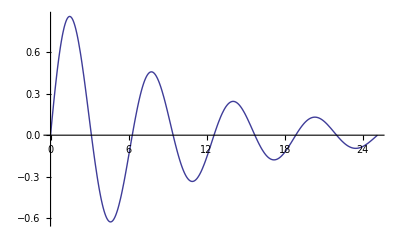

```mathematica
Plot[Exp[-x/10]Sin[x],{x,0,8Pi}]
```

{{46.1909596369991391069700828432,-8.6936742365022124391696407634},{-46.1907215736668331479214483639,-8.6938841184613039632657455875},{-46.1902772770987407515383712019,-8.69369710398251291952307926},{46.1900405403859414236223755283,-8.6932420428763311741176924487},{-39.0029500814156226952894559975,-11.439087491120932123354901689},{39.0029294825158434752375639155,-11.439097257883090625852402784},{-39.0029292913461903167714964338,-11.43909716505207306129383469},{39.0029269227076580799189119171,-11.439101714483059453261294765},{-33.1893974016468153145505300352,-13.380770123441630468690467885},{33.1893974000703135188530344029,-13.38077011368385867584068224},{33.1893974000702854674212687796,-13.380770113683870547177159527},{-33.1893974000701346686059678425,-13.380770113683969090047233982},{-28.1442335298889171068410694964,-14.89234139196171896684692956},{28.14423352988891704272834456,-14.892341391961718940486290492},{-28.1442335298889170357909630555,-14.892341391961718942514930565},{28.1442335298889161666252626854,-14.892341391961718466094814149},{23.6289138951338418613088087165,-16.121338990722643073946037515},{-23.628913895133841858299158745,-16.12133899072264307186810773},{23.6289138951338418476644574081,-16.121338990722643086073834459},{-23.6289138951338418608497536073,-16.121338990722643057336301644},{-12.723808381123753717012266821,-22.8467461253841310108704624605},{12.723808381123753717001100381,-22.8467461253841310108637213184},{12.723808381123753717083791711,-22.8467461253841310105342641684},{-12.723808381123753717085610559,-22.8467461253841310105263305654},{19.5080719814481382196514641916,-17.153222633870561987355671556},{-19.508071981448138217768700597,-17.153222633870561989016570904},{-19.5080719814481382176531063541,-17.153222633870561988687645241},{19.5080719814481382177564220425,-17.153222633870561988565187176},{-24.3039246537770642693883981685,-3.6976166793358541390997511652},{-24.3074349159614335012848044592,-3.6597224281872105662623118206},{24.3074347983859394343491921216,-3.6597220227712937364188294807},{24.307079435823682315900630584,-3.6595033611058145271166791474},{-23.7729527927459777363918403283,-4.2117434488388593216023208747},{23.77295279221736826908878201,-4.2117434492797476796467619896},{23.7729527751537606658858942265,-4.2117402635032603178391441035},{-23.7729477978523007967891716706,-4.2117415889035729156870659453},{15.666109101895377135703749232,-18.0436794320907769203093774637},{-15.666109101895377135682617232,-18.0436794320907769203241357954},{-15.666109101895377135620373993,-18.0436794320907769203508850792},{15.666109101895377135600185689,-18.0436794320907769203609592651},{11.988461859963326213040345629,-18.6992041217266775682763987502},{-11.988461859963326213038947724,-18.6992041217266775682710626283},{-11.988461859963326213033438285,-18.6992041217266775682500318413},{11.98846185996332621303204038,-18.6992041217266775682446957194},{-20.7359644838354900616211913702,-5.2643348241323966236627894964},{20.7347630288061394652498016823,-5.2664354007524436396357860984},{-20.7347624203086128744848607481,-5.2664356863679094418066711099},{20.7347624202102569328563049257,-5.2664356862261066781603442156},{-20.2027841451341845616790212557,-5.7129450088308660552229498562},{-20.2027841449237449307762049678,-5.7129450087896355920830158847},{20.2027841449237449315840214392,-5.7129450087896355692096589118},{20.2027841449237449301552698917,-5.7129450087896355728372957114},{8.8628053599761163966713744864,-18.8980845053943575653059040431},{-8.8628053599761163966563293144,-18.8980845053943575653068940912},{-8.8628053599761163964669849161,-18.8980845053943575653193539067},{8.862805359976116396451939744,-18.8980845053943575653203439548},{-6.3473267578843576132450653376,-18.6325223547437258288988841292},{6.3473267578843576132550451427,-18.6325223547437258288933100783},{6.3473267578843576136694602165,-18.6325223547437258286618455204},{-6.3473267578843576136749261517,-18.6325223547437258286587926145},{17.8419993708297875151131439299,-6.4083832513883052230672515412},{-17.8419993708129594679253791971,-6.4083832514180308968016641456},{17.8419993708129594679253788637,-6.4083832514180308968016645335},{-17.8419312930099002453925549475,-6.4084028725890360503464596232},{17.3123429755139028917628203271,-6.7767412481860024498873642928},{-17.3123429755139028917413709083,-6.7767412481860024498783446188},{-17.3123429755138649879455247632,-6.7767412481860194796909531276},{17.3123429755138229067303183358,-6.77674124818604316700993692},{3.8794888063949529195711390307,-18.0514660056115812029632374823},{-3.8794888063949529195711446693,-18.051466005611581202963231646},{-3.8794888063949529200029141007,-18.0514660056115812024917298581},{3.8794888063949529200029171452,-18.0514660056115812024917266692},{-1.4288661059506810700466217908,-17.4224467337970768800281321004},{1.4288661059506810700466207889,-17.4224467337970768800281306795},{1.4288661059506810703902034158,-17.4224467337970768793200329992},{-1.4288661059506810703902023302,-17.4224467337970768793200314111},{-15.3251009159923401844900259333,-7.3050347745770443790836124178},{-15.3251008278226688126444562218,-7.3050346174497913887885497692},{15.3251008278226688126444561835,-7.3050346174497913887885498005},{15.3251008278226687537588971065,-7.3050346174497912012654026346},{-14.8001812525977595140742898469,-7.6086513217955775217393807226},{14.8001812525977595140658117405,-7.6086513217955775217324637739},{14.8001812525977595139272597957,-7.6086513217955775218190989426},{-14.8001812525977595139183167512,-7.6086513217955775218122112513},{0.,-15.950542031422054880874393385},{0.,-15.9505420314220548807676613774},{-13.0664952781212082978305407384,-8.0406831832629948047444693633},{-13.0664952779769475997838411183,-8.0406831834351984147036517971},{13.0664952779769475997838411183,-8.0406831834351984147036517971},{13.0664952779769475986055298539,-8.0406831834351984151735894043},{12.5483223296765697452747597893,-8.28846931479032153529855391},{-12.5483223296765697452747596549,-8.2884693147903215352985521387},{12.5483223296765697452369889762,-8.2884693147903215352569893461},{-12.5483223296765697452369889765,-8.2884693147903215352569893343},{-7.0190469214662695910204090285,-12.6440184174434423382448256294},{7.0190469214662695910204132903,-12.6440184174434423382448162459},{7.019046921466269588460376779,-12.6440184174434423370183421832},{-7.019046921466269572690844367,-12.6440184174434422972108045338},{-7.5171722054820744189620195241,-12.2113151133698255349464795926},{7.5171722054820743969628882584,-12.2113151133698255039743900734},{-7.5171722054820743941738877524,-12.2113151133698255040243279244},{7.5171722054820743941740053885,-12.2113151133698255040242177169},{-6.7634648700933232310609816317,-12.5303417341510119593611596024},{6.7634648700933232310266225773,-12.5303417341510119593430593948},{-6.7634648700933232306758331765,-12.5303417341510119583413449386},{6.7634648700933232306523488243,-12.5303417341510119582937787207},{10.9969181386475513751141599855,-8.6771132390859464248693546522},{-10.9969181386475513751129444649,-8.6771132390859464248693018408},{10.9969181386475513751128142378,-8.6771132390859464248688516219},{-10.9969181386474273740252834511,-8.6771132390859153827669152667},{-4.5986706454828089901117383411,-13.1084064908968991081705707445},{-4.5986706454828089901121438543,-13.1084064908968991081696704856},{4.5986706454828089901121437838,-13.1084064908968991081696703615},{4.5986706454828089901120678547,-13.1084064908968991081691744567},{7.6438306113636454806121126335,-11.4972632559553329998745757643},{7.6438306113636454807577825921,-11.4972632559553329997105123286},{-7.6438306113636454807571762598,-11.4972632559553329997103505087},{-7.643830611363645480592242092,-11.4972632559553329993888879003},{-2.3297494373022407766798289096,-13.5543309385746378596716897966},{2.3297494373022407766688700408,-13.5543309385746378596678877668},{-2.3297494373022407766688700927,-13.554330938574637859667887599},{2.3297494373022407766625571896,-13.5543309385746378596591433841},{4.6488122222605346118697519354,-12.9304772325015348550810179416},{-4.6488122222605346118344635116,-12.9304772325015348549878742471},{-4.6488122222605346112774097447,-12.9304772325015348546287621203},{4.6488122222605346112308239698,-12.930477232501534854616835346},{-10.5093302483983565059199857963,-8.8433347734199792166168332278},{10.5093302483983565059183063962,-8.8433347734199792165989544808},{10.5093302483983565059352053131,-8.8433347734199792164803433248},{-10.5093302483983565059334350346,-8.8433347734199792164618450578},{0.,-13.7080673626422355262152191846},{0.,-13.7080673626422355262152191846},{-2.3588164063272952736208532526,-13.3912997702169473271051655378},{2.3588164063272952736207686099,-13.3912997702169473271050156527},{2.3588164063272952731452117838,-13.3912997702169473269135701072},{-2.3588164063272952731453122626,-13.3912997702169473269135407217},{1.746842965×10^-19,-13.5543172145150579447213394673},{-1.746842965×10^-19,-13.5543172145150579447213394673},{8.8019454826324270673655975161,-10.1199463792350187969150892769},{8.8019454826324270672221011645,-10.1199463792350187965701011414},{-8.80194548263242706691490136,-10.1199463792350187961434209077},{-8.8019454826324267571917477619,-10.1199463792350188481575714155},{8.9176636035807556834968802577,-9.71996506685687648745958646694},{-8.9176636035807556837609613983,-9.71996506685687648709267197778},{8.9176636035807556836802698393,-9.71996506685687648693129057629},{-8.9176636035807556836711122213,-9.71996506685687648692183436656},{-9.18741455953923780542819688652,-8.6693560188454000047047891877},{9.18741455953923759262815593508,-8.6693560188454001076269281877},{-9.18741455953923759269251443932,-8.6693560188454001074326361002},{9.18741455953923759268797732782,-8.6693560188454001074358679122},{0,-12.0000013283565962246174671916},{0,-12.000001328356596224617300571},{-8.00351082443366513380228657055,-7.9996746627285165804872685063},{8.0035108244336651337501385671,-7.9996746627285165804365075623},{-8.00351082443366513375013794115,-7.9996746627285165804365079069},{8.00351082443366513385262390875,-7.9996746627285165803051388843},{7.18790575598050374832372127363,-6.7695696199077873264727370943},{-7.18790575598050374830385181602,-6.7695696199077873264933730261},{7.18790575598050374833551314278,-6.7695696199077873264573286289},{-7.18790575598050374339384370354,-6.7695696199077873140670434057},{-5.99999989701282173616476275566,-5.9999995810609242519989535599},{-5.9999998970128217361647628606,-5.9999995810609242519989530458},{5.99999989701282173616476286061,-5.9999995810609242519989530458},{5.99999989701282173616476231826,-5.9999995810609242519989535879},{1.439018×10^-22,-7.99999999999355887018012631021},{0,-7.99999999999355887017828079159},{-5.16952097639412666496274186942,-4.7635701181043900787503110363},{5.1695209763941266649684762034,-4.7635701181043900787383219824},{5.1695209763941266649609883138,-4.7635701181043900787412591496},{-5.16952097639412666494902935333,-4.7635701181043900787376439978},{-3.99999999998861154128541452982,-4.00000000000510938725910548335},{-3.99999999998861154128540098448,-4.00000000000510938725910338305},{3.99999999998861154128540098448,-4.00000000000510938725910338305},{3.99999999998861154128549113189,-4.00000000000510938725896823521},{-3.11945159116590774139845833973,-2.7466757443405997693688986658},{3.1194515911659077413972809568,-2.7466757443405997693689969657},{-3.11945159116590774139724528348,-2.746675744340599769368956413},{3.11945159116590774139722705733,-2.7466757443405997693689330888},{0,-3.99999999999999987845242883776},{-4.482536×10^-23,-3.99999999999999987845178298866},{2.00000000000000002239700227254,-2.00000000000000002348782631392},{2.00000000000000002239700226945,-2.00000000000000002348782631433},{-2.00000000000000002239700226941,-2.00000000000000002348782631429},{-2.00000000000000002239700169084,-2.00000000000000002348782157977},{0,0},{0,0}}

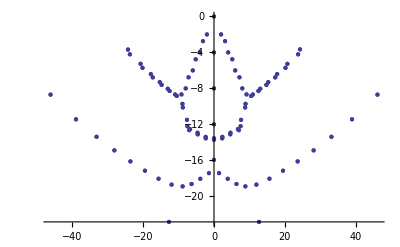

```mathematica
QNMroots[30,0,0,30][[1]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

```mathematica
Sum[ChebyshevT[nn,z]Reverse[QNMs[[2,-30]]][[nn+1]],{nn,0,30}];
Plot[Re[%], {z,-1,1}, WorkingPrecision->30,PlotRange->All,Axes->->{True,False}]
```

{{-46.190831265033817483294016673247677668186908130205,-8.693808653243133833348998277958034731458670816223},{46.190831265033817483294016673247677668177613000993,-8.693808653243133833348998277958034731462815350083},{-46.19083126503381748329401667324767766817761264901,-8.693808653243133833348998277958034731462815472587},{46.19083126503381748329401667324767766813841154583,-8.693808653243133833348998277958034731580111864165},{39.002929482515939265237289526759374143718452877543,-11.43909725788364669720378295816268491579964401399},{-39.002929482515939265237289526759374143699327682554,-11.43909725788364669720378295816268491579103946933},{-39.002929482515939265237289526759374143687165508959,-11.43909725788364669720378295816268491581020113433},{39.002929482515939265237289526759374143687165488605,-11.43909725788364669720378295816268491581020107724},{33.189397400070309215950932555787844747668969975336,-13.38077011368386356737124293180435461000134442209},{-33.189397400070309215950932555787844747668969975336,-13.38077011368386356737124293180435461000134442209},{-33.189397400070309215950932555787844747652503724442,-13.38077011368386356737124293180435461002814116297},{33.189397400070309215950932555787844747652503724442,-13.38077011368386356737124293180435461002814116297},{-28.144233529888917042261676845949371153444506340149,-14.89234139196171894075689935556139687186673000843},{28.144233529888917042261676845949371153444506332861,-14.89234139196171894075689935556139687186673001193},{28.144233529888917042261676845949371153424635233826,-14.89234139196171894075689935556139687189495906619},{-28.144233529888917042261676845949371153424635233826,-14.89234139196171894075689935556139687189495906619},{-23.628913895133841858694838032875993767007376702947,-16.12133899072264307078804556115210410763830088794},{23.628913895133841858694838032875993767007376702947,-16.12133899072264307078804556115210410763830088794},{-23.628913895133841858694838032875993766982793433469,-16.1213389907226430707880455611521041076645423017},{23.628913895133841858694838032875993766982793433469,-16.1213389907226430707880455611521041076645423017},{12.72380838112375371710763374278622417483608920164,-22.846746125384131010421447374945091170342404915037},{-12.72380838112375371710763374278622417483651460537,-22.846746125384131010421447374945091170341798676154},{-12.72380838112375371710763374278622417447566638347,-22.846746125384131010421447374945091170434384229419},{12.72380838112375371710763374278622417453208278114,-22.846746125384131010421447374945091170400939071222},{19.50807198144813821757790108845394394643534019228,-17.15322263387056198868741740564995400883442931233},{-19.508071981448138217577901088453943946435339987517,-17.15322263387056198868741740564995400883442885802},{19.508071981448138217577901088453943946406054284916,-17.1532226338705619886874174056499540088570911838},{-19.508071981448138217577901088453943946406054284854,-17.15322263387056198868741740564995400885709118377},{24.307434875141817135719678152680683522889747987485,-3.659722347929160567982866649957857652039408316355},{-24.307434875141817135719678152680683522889722814098,-3.659722347929160567982866649957857652039413376668},{-24.307434875141817135719678152680683522867846554338,-3.659722347929160567982866649957857652032333662197},{24.307434875141817135719678152680683522867821380951,-3.659722347929160567982866649957857652032338722511},{-23.772952792897186993617218202235404306163368289202,-4.211743449166065617914179211776674043109311276636},{23.772952792897186993617218202235404306163368289202,-4.211743449166065617914179211776674043109311276636},{23.772952792897186993617218202235404306163368198054,-4.211743449166065617914179211776674043109311417663},{-23.772952792897186993617218202235404306163368180298,-4.21174344916606561791417921177667404310931050313},{-15.66610910189537713559833842651500681644978819001,-18.043679432090776920361825822452826866040570788},{15.66610910189537713559833842651500681644957902985,-18.043679432090776920361825822452826866040504682037},{15.66610910189537713559833842651500681641996321161,-18.043679432090776920361825822452826866060178841823},{-15.66610910189537713559833842651500681640657282622,-18.043679432090776920361825822452826866044046105307},{-11.98846185996332621304037298744894662228047283467,-18.699204121726677568276712971848856115947090676073},{11.98846185996332621304037298744894662228047283467,-18.699204121726677568276712971848856115947090676073},{11.98846185996332621304037298744894662231794542771,-18.69920412172667756827671297184885611590767658682},{-11.98846185996332621304037298744894662231794542775,-18.699204121726677568276712971848856115907676586778},{-20.734762420234175283418023141302419756026324119617,-5.266435686417929299079195385387901893720130187988},{20.734762420234175283418023141302419756026322693174,-5.266435686417929299079195385387901893720131842328},{20.734762420234175283418023141302419755996671182044,-5.2664356864179292990791953853879018937226436449},{-20.734762420234175283418023141302419755996669755601,-5.26643568641792929907919538538790189372264529924},{-20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{-20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{-8.862805359976116396672570804054901663222915181565,-18.898084505394357565305954830767432638791820142476},{8.862805359976116396672570804054901663222914791974,-18.898084505394357565305954830767432638791819789338},{8.862805359976116396672570804054901663320826677374,-18.898084505394357565305954830767432638720778385488},{-8.862805359976116396672570804054901663912322739662,-18.898084505394357565305954830767432637943784690305},{-6.347326757884357613676662792901603547777676935844,-18.632522354743725828658074595368518169840740730285},{6.3473267578843576136766627929016035477776766366,-18.632522354743725828658074595368518169840739110168},{6.347326757884357613676662792901603547883894520602,-18.632522354743725828658074595368518169714515582474},{-6.347326757884357613676662792901603547353420652343,-18.632522354743725828658074595368518169522137835346},{17.841999370812959467925379197105120325830559591659,-6.408383251418030896801664145569933369893109956512},{-17.841999370812959467925379197105120325830558323023,-6.408383251418030896801664145569933369893109144344},{-17.841999370812959467925379197105120325800926648072,-6.408383251418030896801664145569933369903547146811},{17.841999370812959467925379197105120325800926632429,-6.408383251418030896801664145569933369903547167421},{17.312342975513902891750891931934257361201617174702,-6.776741248186002449896951769791367914076164813906},{17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{-17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{-17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{3.879488806394952920003121707397474760207170032038,-18.051466005611581202491805472608256011491749445612},{3.87948880639495292000312170739747475971745708374,-18.051466005611581202491805472608256011425985244922},{-3.879488806394952920003121707397474759438371998917,-18.051466005611581202491805472608256011207810121363},{-3.879488806394952920003121707397474759522296976416,-18.05146600561158120249180547260825601106605805407},{1.428866105950681070390407725460114668566074911333,-17.422446733797076879319869371376609018446788057078},{-1.428866105950681070390407725460114668300858872333,-17.422446733797076879319869371376609018465151442598},{1.428866105950681070390407725460114668630857646201,-17.422446733797076879319869371376609018273567281872},{-1.428866105950681070390407725460114668630429548958,-17.422446733797076879319869371376609018273560660686},{-15.325100827822668812644456183397344311508007065973,-7.305034617449791388788549800636125688482152191539},{15.325100827822668812644456183397344311508005175269,-7.30503461744979138878854980063612568848215359007},{15.325100827822668812644456183397344311481023379556,-7.305034617449791388788549800636125688496344491631},{-15.325100827822668812644456183397344311481023368603,-7.305034617449791388788549800636125688496344446256},{-14.800181252597759513915117252325215971294938569088,-7.608651321795577521842360447697609394968031557256},{14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{-14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{0,-15.95054203142205488076760952661524978666972000085},{-2.96×10^-46,-15.950542031422054880767609526615249786647472373323},{-13.066495277976947599783841118913939384591933078755,-8.040683183435198414703651797087579947319369633008},{13.066495277976947599783841118913939384591929993193,-8.040683183435198414703651797087579947319371394423},{13.066495277976947599783841118913939384567436430785,-8.04068318343519841470365179708757994733478602503},{-13.066495277976947599783841118913939384567433345221,-8.040683183435198414703651797087579947334787786447},{12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{-12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{-12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{12.54832232967656974524472818436080827972912363294,-8.28846931479032153529877623201414781145136768458},{-7.019046921466269591020413290008966189201417739262,-12.644018417443442338244816269563488001932799288281},{7.019046921466269591020413290008966189289577834385,-12.644018417443442338244816269563488001753549279685},{-7.019046921466269591020413290008966189289577834384,-12.644018417443442338244816269563488001753549279684},{7.019046921466269591020413290008966752965201935145,-12.644018417443442338244816269563487010867366807453},{7.51717220548207439417400538049887838267748488767,-12.211315113369825504024217694476095354528625259117},{-7.517172205482074394174005380498878250348286955294,-12.211315113369825504024217694476094338822492334366},{7.51717220548207439417400538049887825034828695468,-12.211315113369825504024217694476094338822492333921},{-7.517172205482074394174005380498878250328151427902,-12.211315113369825504024217694476094338733526759069},{6.76346487009332323084035999237269649731584774684,-12.530341734151011958425160367785590745976484749286},{-6.763464870093323230840359992372696497228816056416,-12.530341734151011958425160367785590745999372982101},{6.76346487009332323084035999237269649722847080969,-12.530341734151011958425160367785590745999182817342},{-6.763464870093323230840359992372696497227991795006,-12.530341734151011958425160367785590745999212808785},{-10.996918138647551375112944463685486964482197871822,-8.677113239085946424869301839475656616652635791895},{10.99691813864755137511294446368548696448219787301,-8.67711323908594642486930183947565661665263579002},{10.996918138647551375112944463685486964460018322853,-8.677113239085946424869301839475656616668994653659},{-10.996918138647551375112944463685486964460018324041,-8.677113239085946424869301839475656616668994651784},{4.598670645482808990112143785304047204223398636878,-13.10840649089689910816967036272415472887269375061},{-4.598670645482808990112143785304047204224205197257,-13.108406490896899108169670362724154728872383150965},{4.598670645482808990112143785304047204230054318197,-13.108406490896899108169670362724154728792176980957},{-4.598670645482808990112143785304047204230054318197,-13.108406490896899108169670362724154728792176980955},{-7.64383061136364548075849878360599947539068826993,-11.497263255955332999739352304840085274400726991537},{-7.643830611363645480758498783605999475390682821205,-11.49726325595533299973935230484008527440072362063},{7.643830611363645480758498783605999475390894888596,-11.497263255955332999739352304840085274400546937794},{7.643830611363645480758498783605999475390690592767,-11.497263255955332999739352304840085274400581416301},{-2.329749437302240776668870039788522142335102695984,-13.554330938574637859667887765054961525202984343937},{2.329749437302240776668870039788522142335102759933,-13.554330938574637859667887765054961525202984118795},{2.329749437302240776668870039788522142337532325467,-13.55433093857463785966788776505496152512756147635},{-2.329749437302240776668870039788522142337532325467,-13.55433093857463785966788776505496152512756147635},{-4.648812222260534611400135742855415071776815505504,-12.930477232501534854569670872943706210093580820598},{-4.648812222260534611400135742855415071766251685557,-12.93047723250153485456967087294370621005467522014},{4.648812222260534611400135742855415071766228679256,-12.93047723250153485456967087294370621005467001543},{4.648812222260534611400135742855415071766228679281,-12.93047723250153485456967087294370621005467001532},{10.509330248398356505952274669700339748661635014894,-8.843334773419979216521089347751033988973950866098},{10.509330248398356505952274669700339748735407746091,-8.843334773419979216521089347751033987503674625673},{-10.509330248398356505952274669700339748735051540061,-8.843334773419979216521089347751033987503370378311},{-10.509330248398356505952274669700339748735051534675,-8.843334773419979216521089347751033987503370374014},{-3.8858×10^-44,-13.708067362642235526215219186567408912107532016769},{0.,-13.70806736264223552621521918656740891203369849624},{-2.358816406327295273290622584715905629867048091949,-13.391299770216947326816006879551466681256197746721},{-2.358816406327295273290622584715905629867045599324,-13.391299770216947326816006879551466681256197686006},{2.358816406327295273290622584715905629867045599451,-13.3912997702169473268160068795514666812561976839},{2.358816406327295273290622584715905629866966647753,-13.391299770216947326816006879551466681256200227275},{-7.6696342×10^-41,-13.554317214515057944545003685781980569169250571972},{0.,-13.554317214515057944545003685781980569169222749909},{-8.801945482632427067222101166535150665617862768651,-10.119946379235018796570101141541885243347339019467},{8.801945482632427067222101166535150665617862551183,-10.119946379235018796570101141541885243347339083085},{8.80194548263242706722210116653515066562243971225,-10.119946379235018796570101141541885243321305694308},{-8.801945482632427067222101166535150665622439712246,-10.119946379235018796570101141541885243321305694309},{8.917663603580755683720793264855802775078221871665,-9.7199650668568764869487950592451580591854303385101},{8.917663603580755683720793264855802775078210517802,-9.7199650668568764869487950592451580591854211257628},{-8.917663603580755683720793264855802775078210300349,-9.7199650668568764869487950592451580591854210240535},{-8.917663603580755683720793264855802774867444855338,-9.7199650668568764869487950592451580591412577934585},{-9.1874145595392375926881230963428366835863036422054,-8.669356018845400107435617959360321923024941541409},{9.1874145595392375926881230963428366835863036422051,-8.669356018845400107435617959360321923024941541409},{-9.1874145595392375926881230963428366835810312309252,-8.669356018845400107435617959360321923028789791005},{9.1874145595392375926881230963428366835810312190729,-8.669356018845400107435617959360321923028789792083},{4.169×10^-45,-12.000001328356596224617471006819802940525285177329},{0,-12.000001328356596224617471006819802940525284232459},{-8.0035108244336651337495526496791788722771516342299,-7.999674662728516580436800741094062430333728319332},{-8.0035108244336651337495526496791788722305885464981,-7.999674662728516580436800741094062430329708785756},{8.0035108244336651337495526496791788722305885392939,-7.999674662728516580436800741094062430329708781785},{8.0035108244336651337495526496791788722305861143378,-7.999674662728516580436800741094062430329707473614},{-7.1879057559805037483237212738888915293041911679845,-6.769569619907787326472737094350326266292229401423},{7.1879057559805037483237212738888915293041911044426,-6.76956961990778732647273709435032626629222908163},{7.1879057559805037483237212738888915293041896237728,-6.769569619907787326472737094350326266292228002211},{-7.1879057559805037483237212738888915293041896237728,-6.769569619907787326472737094350326266292228002211},{5.9999998970128217361647629347342417359766468213855,-5.999999581060924251998953122299616929610574326225},{-5.9999998970128217361647629347342417359640678489214,-5.999999581060924251998953122299616929579779182934},{5.9999998970128217361647629347342417359640672051674,-5.999999581060924251998953122299616929579778551047},{-5.9999998970128217361647629347342417359640672205105,-5.999999581060924251998953122299616929579778525311},{2.80622277×10^-40,-7.9999999999935588701784609679058503543015491782403},{0,-7.9999999999935588701784609679058503543015432153055},{-5.1695209763941266649609883133433096188854343204442,-4.763570118104390078741259146318029632936740632249},{5.1695209763941266649609883133433096188854343031422,-4.763570118104390078741259146318029632936740636449},{-5.169520976394126664960988313343309618885434303151,-4.76357011810439007874125914631802963293674063642},{5.1695209763941266649609883133433096188853445534616,-4.763570118104390078741259146318029632936498218785},{3.9999999999886115412854009844787305432480461131884,-4.0000000000051093872591033830438012933059072558641},{3.9999999999886115412854009844787305432468904045341,-4.000000000005109387259103383043801293306158904696},{-3.9999999999886115412854009844787305432468904042318,-4.0000000000051093872591033830438012933061589042669},{-3.9999999999886115412854009844787305432468868134677,-4.0000000000051093872591033830438012933061614173875},{-3.11945159116590774139724538829847592958163743287,-2.746675744340599769368956399708465834988810349197},{-3.119451591165907741397245388298475929581628057016,-2.746675744340599769368956399708465834988800749844},{3.1194515911659077413972453882984759295816285809545,-2.746675744340599769368956399708465834988799373823},{3.1194515911659077413972453882984759295816142241741,-2.74667574434059976936895639970846583498879564823},{0,-3.9999999999999998784523046393468584453796714419354},{0,-3.999999999999999878452304639346858445379671441934},{-2.0000000000000000223970022694468340810523038252307,-2.0000000000000000234878263143369990158907370558693},{-2.0000000000000000223970022694468340810523037529154,-2.0000000000000000234878263143369990158907367787914},{2.0000000000000000223970022694468340810523037529154,-2.0000000000000000234878263143369990158907367787914},{2.000000000000000022397002269446834081052303708389,-2.0000000000000000234878263143369990158907367246052},{0,0},{0,0}}

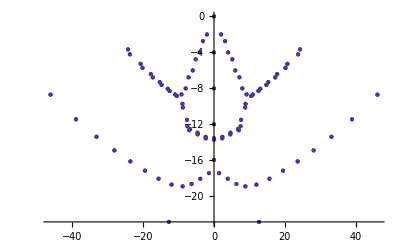

```mathematica
QNMroots[30,0,0,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

```mathematica
QNMroots[30,0,0,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{-46.190831265033817483294016673247677668186908130205,-8.693808653243133833348998277958034731458670816223},{46.190831265033817483294016673247677668177613000993,-8.693808653243133833348998277958034731462815350083},{-46.19083126503381748329401667324767766817761264901,-8.693808653243133833348998277958034731462815472587},{46.19083126503381748329401667324767766813841154583,-8.693808653243133833348998277958034731580111864165},{39.002929482515939265237289526759374143718452877543,-11.43909725788364669720378295816268491579964401399},{-39.002929482515939265237289526759374143699327682554,-11.43909725788364669720378295816268491579103946933},{-39.002929482515939265237289526759374143687165508959,-11.43909725788364669720378295816268491581020113433},{39.002929482515939265237289526759374143687165488605,-11.43909725788364669720378295816268491581020107724},{33.189397400070309215950932555787844747668969975336,-13.38077011368386356737124293180435461000134442209},{-33.189397400070309215950932555787844747668969975336,-13.38077011368386356737124293180435461000134442209},{-33.189397400070309215950932555787844747652503724442,-13.38077011368386356737124293180435461002814116297},{33.189397400070309215950932555787844747652503724442,-13.38077011368386356737124293180435461002814116297},{-28.144233529888917042261676845949371153444506340149,-14.89234139196171894075689935556139687186673000843},{28.144233529888917042261676845949371153444506332861,-14.89234139196171894075689935556139687186673001193},{28.144233529888917042261676845949371153424635233826,-14.89234139196171894075689935556139687189495906619},{-28.144233529888917042261676845949371153424635233826,-14.89234139196171894075689935556139687189495906619},{-23.628913895133841858694838032875993767007376702947,-16.12133899072264307078804556115210410763830088794},{23.628913895133841858694838032875993767007376702947,-16.12133899072264307078804556115210410763830088794},{-23.628913895133841858694838032875993766982793433469,-16.1213389907226430707880455611521041076645423017},{23.628913895133841858694838032875993766982793433469,-16.1213389907226430707880455611521041076645423017},{12.72380838112375371710763374278622417483608920164,-22.846746125384131010421447374945091170342404915037},{-12.72380838112375371710763374278622417483651460537,-22.846746125384131010421447374945091170341798676154},{-12.72380838112375371710763374278622417447566638347,-22.846746125384131010421447374945091170434384229419},{12.72380838112375371710763374278622417453208278114,-22.846746125384131010421447374945091170400939071222},{19.50807198144813821757790108845394394643534019228,-17.15322263387056198868741740564995400883442931233},{-19.508071981448138217577901088453943946435339987517,-17.15322263387056198868741740564995400883442885802},{19.508071981448138217577901088453943946406054284916,-17.1532226338705619886874174056499540088570911838},{-19.508071981448138217577901088453943946406054284854,-17.15322263387056198868741740564995400885709118377},{24.307434875141817135719678152680683522889747987485,-3.659722347929160567982866649957857652039408316355},{-24.307434875141817135719678152680683522889722814098,-3.659722347929160567982866649957857652039413376668},{-24.307434875141817135719678152680683522867846554338,-3.659722347929160567982866649957857652032333662197},{24.307434875141817135719678152680683522867821380951,-3.659722347929160567982866649957857652032338722511},{-23.772952792897186993617218202235404306163368289202,-4.211743449166065617914179211776674043109311276636},{23.772952792897186993617218202235404306163368289202,-4.211743449166065617914179211776674043109311276636},{23.772952792897186993617218202235404306163368198054,-4.211743449166065617914179211776674043109311417663},{-23.772952792897186993617218202235404306163368180298,-4.21174344916606561791417921177667404310931050313},{-15.66610910189537713559833842651500681644978819001,-18.043679432090776920361825822452826866040570788},{15.66610910189537713559833842651500681644957902985,-18.043679432090776920361825822452826866040504682037},{15.66610910189537713559833842651500681641996321161,-18.043679432090776920361825822452826866060178841823},{-15.66610910189537713559833842651500681640657282622,-18.043679432090776920361825822452826866044046105307},{-11.98846185996332621304037298744894662228047283467,-18.699204121726677568276712971848856115947090676073},{11.98846185996332621304037298744894662228047283467,-18.699204121726677568276712971848856115947090676073},{11.98846185996332621304037298744894662231794542771,-18.69920412172667756827671297184885611590767658682},{-11.98846185996332621304037298744894662231794542775,-18.699204121726677568276712971848856115907676586778},{-20.734762420234175283418023141302419756026324119617,-5.266435686417929299079195385387901893720130187988},{20.734762420234175283418023141302419756026322693174,-5.266435686417929299079195385387901893720131842328},{20.734762420234175283418023141302419755996671182044,-5.2664356864179292990791953853879018937226436449},{-20.734762420234175283418023141302419755996669755601,-5.26643568641792929907919538538790189372264529924},{-20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{-20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{20.202784144923744930960242756437982977143065343788,-5.712945008789635569568233712203050231621105924373},{-8.862805359976116396672570804054901663222915181565,-18.898084505394357565305954830767432638791820142476},{8.862805359976116396672570804054901663222914791974,-18.898084505394357565305954830767432638791819789338},{8.862805359976116396672570804054901663320826677374,-18.898084505394357565305954830767432638720778385488},{-8.862805359976116396672570804054901663912322739662,-18.898084505394357565305954830767432637943784690305},{-6.347326757884357613676662792901603547777676935844,-18.632522354743725828658074595368518169840740730285},{6.3473267578843576136766627929016035477776766366,-18.632522354743725828658074595368518169840739110168},{6.347326757884357613676662792901603547883894520602,-18.632522354743725828658074595368518169714515582474},{-6.347326757884357613676662792901603547353420652343,-18.632522354743725828658074595368518169522137835346},{17.841999370812959467925379197105120325830559591659,-6.408383251418030896801664145569933369893109956512},{-17.841999370812959467925379197105120325830558323023,-6.408383251418030896801664145569933369893109144344},{-17.841999370812959467925379197105120325800926648072,-6.408383251418030896801664145569933369903547146811},{17.841999370812959467925379197105120325800926632429,-6.408383251418030896801664145569933369903547167421},{17.312342975513902891750891931934257361201617174702,-6.776741248186002449896951769791367914076164813906},{17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{-17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{-17.312342975513902891750891931934257361200952198848,-6.776741248186002449896951769791367914075697822891},{3.879488806394952920003121707397474760207170032038,-18.051466005611581202491805472608256011491749445612},{3.87948880639495292000312170739747475971745708374,-18.051466005611581202491805472608256011425985244922},{-3.879488806394952920003121707397474759438371998917,-18.051466005611581202491805472608256011207810121363},{-3.879488806394952920003121707397474759522296976416,-18.05146600561158120249180547260825601106605805407},{1.428866105950681070390407725460114668566074911333,-17.422446733797076879319869371376609018446788057078},{-1.428866105950681070390407725460114668300858872333,-17.422446733797076879319869371376609018465151442598},{1.428866105950681070390407725460114668630857646201,-17.422446733797076879319869371376609018273567281872},{-1.428866105950681070390407725460114668630429548958,-17.422446733797076879319869371376609018273560660686},{-15.325100827822668812644456183397344311508007065973,-7.305034617449791388788549800636125688482152191539},{15.325100827822668812644456183397344311508005175269,-7.30503461744979138878854980063612568848215359007},{15.325100827822668812644456183397344311481023379556,-7.305034617449791388788549800636125688496344491631},{-15.325100827822668812644456183397344311481023368603,-7.305034617449791388788549800636125688496344446256},{-14.800181252597759513915117252325215971294938569088,-7.608651321795577521842360447697609394968031557256},{14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{-14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{14.800181252597759513915117252325215971294727308014,-7.608651321795577521842360447697609394968170084236},{0,-15.95054203142205488076760952661524978666972000085},{-2.96×10^-46,-15.950542031422054880767609526615249786647472373323},{-13.066495277976947599783841118913939384591933078755,-8.040683183435198414703651797087579947319369633008},{13.066495277976947599783841118913939384591929993193,-8.040683183435198414703651797087579947319371394423},{13.066495277976947599783841118913939384567436430785,-8.04068318343519841470365179708757994733478602503},{-13.066495277976947599783841118913939384567433345221,-8.040683183435198414703651797087579947334787786447},{12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{-12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{-12.548322329676569745244728184360808279729123632944,-8.288469314790321535298776232014147811451367684577},{12.54832232967656974524472818436080827972912363294,-8.28846931479032153529877623201414781145136768458},{-7.019046921466269591020413290008966189201417739262,-12.644018417443442338244816269563488001932799288281},{7.019046921466269591020413290008966189289577834385,-12.644018417443442338244816269563488001753549279685},{-7.019046921466269591020413290008966189289577834384,-12.644018417443442338244816269563488001753549279684},{7.019046921466269591020413290008966752965201935145,-12.644018417443442338244816269563487010867366807453},{7.51717220548207439417400538049887838267748488767,-12.211315113369825504024217694476095354528625259117},{-7.517172205482074394174005380498878250348286955294,-12.211315113369825504024217694476094338822492334366},{7.51717220548207439417400538049887825034828695468,-12.211315113369825504024217694476094338822492333921},{-7.517172205482074394174005380498878250328151427902,-12.211315113369825504024217694476094338733526759069},{6.76346487009332323084035999237269649731584774684,-12.530341734151011958425160367785590745976484749286},{-6.763464870093323230840359992372696497228816056416,-12.530341734151011958425160367785590745999372982101},{6.76346487009332323084035999237269649722847080969,-12.530341734151011958425160367785590745999182817342},{-6.763464870093323230840359992372696497227991795006,-12.530341734151011958425160367785590745999212808785},{-10.996918138647551375112944463685486964482197871822,-8.677113239085946424869301839475656616652635791895},{10.99691813864755137511294446368548696448219787301,-8.67711323908594642486930183947565661665263579002},{10.996918138647551375112944463685486964460018322853,-8.677113239085946424869301839475656616668994653659},{-10.996918138647551375112944463685486964460018324041,-8.677113239085946424869301839475656616668994651784},{4.598670645482808990112143785304047204223398636878,-13.10840649089689910816967036272415472887269375061},{-4.598670645482808990112143785304047204224205197257,-13.108406490896899108169670362724154728872383150965},{4.598670645482808990112143785304047204230054318197,-13.108406490896899108169670362724154728792176980957},{-4.598670645482808990112143785304047204230054318197,-13.108406490896899108169670362724154728792176980955},{-7.64383061136364548075849878360599947539068826993,-11.497263255955332999739352304840085274400726991537},{-7.643830611363645480758498783605999475390682821205,-11.49726325595533299973935230484008527440072362063},{7.643830611363645480758498783605999475390894888596,-11.497263255955332999739352304840085274400546937794},{7.643830611363645480758498783605999475390690592767,-11.497263255955332999739352304840085274400581416301},{-2.329749437302240776668870039788522142335102695984,-13.554330938574637859667887765054961525202984343937},{2.329749437302240776668870039788522142335102759933,-13.554330938574637859667887765054961525202984118795},{2.329749437302240776668870039788522142337532325467,-13.55433093857463785966788776505496152512756147635},{-2.329749437302240776668870039788522142337532325467,-13.55433093857463785966788776505496152512756147635},{-4.648812222260534611400135742855415071776815505504,-12.930477232501534854569670872943706210093580820598},{-4.648812222260534611400135742855415071766251685557,-12.93047723250153485456967087294370621005467522014},{4.648812222260534611400135742855415071766228679256,-12.93047723250153485456967087294370621005467001543},{4.648812222260534611400135742855415071766228679281,-12.93047723250153485456967087294370621005467001532},{10.509330248398356505952274669700339748661635014894,-8.843334773419979216521089347751033988973950866098},{10.509330248398356505952274669700339748735407746091,-8.843334773419979216521089347751033987503674625673},{-10.509330248398356505952274669700339748735051540061,-8.843334773419979216521089347751033987503370378311},{-10.509330248398356505952274669700339748735051534675,-8.843334773419979216521089347751033987503370374014},{-3.8858×10^-44,-13.708067362642235526215219186567408912107532016769},{0.,-13.70806736264223552621521918656740891203369849624},{-2.358816406327295273290622584715905629867048091949,-13.391299770216947326816006879551466681256197746721},{-2.358816406327295273290622584715905629867045599324,-13.391299770216947326816006879551466681256197686006},{2.358816406327295273290622584715905629867045599451,-13.3912997702169473268160068795514666812561976839},{2.358816406327295273290622584715905629866966647753,-13.391299770216947326816006879551466681256200227275},{-7.6696342×10^-41,-13.554317214515057944545003685781980569169250571972},{0.,-13.554317214515057944545003685781980569169222749909},{-8.801945482632427067222101166535150665617862768651,-10.119946379235018796570101141541885243347339019467},{8.801945482632427067222101166535150665617862551183,-10.119946379235018796570101141541885243347339083085},{8.80194548263242706722210116653515066562243971225,-10.119946379235018796570101141541885243321305694308},{-8.801945482632427067222101166535150665622439712246,-10.119946379235018796570101141541885243321305694309},{8.917663603580755683720793264855802775078221871665,-9.7199650668568764869487950592451580591854303385101},{8.917663603580755683720793264855802775078210517802,-9.7199650668568764869487950592451580591854211257628},{-8.917663603580755683720793264855802775078210300349,-9.7199650668568764869487950592451580591854210240535},{-8.917663603580755683720793264855802774867444855338,-9.7199650668568764869487950592451580591412577934585},{-9.1874145595392375926881230963428366835863036422054,-8.669356018845400107435617959360321923024941541409},{9.1874145595392375926881230963428366835863036422051,-8.669356018845400107435617959360321923024941541409},{-9.1874145595392375926881230963428366835810312309252,-8.669356018845400107435617959360321923028789791005},{9.1874145595392375926881230963428366835810312190729,-8.669356018845400107435617959360321923028789792083},{4.169×10^-45,-12.000001328356596224617471006819802940525285177329},{0,-12.000001328356596224617471006819802940525284232459},{-8.0035108244336651337495526496791788722771516342299,-7.999674662728516580436800741094062430333728319332},{-8.0035108244336651337495526496791788722305885464981,-7.999674662728516580436800741094062430329708785756},{8.0035108244336651337495526496791788722305885392939,-7.999674662728516580436800741094062430329708781785},{8.0035108244336651337495526496791788722305861143378,-7.999674662728516580436800741094062430329707473614},{-7.1879057559805037483237212738888915293041911679845,-6.769569619907787326472737094350326266292229401423},{7.1879057559805037483237212738888915293041911044426,-6.76956961990778732647273709435032626629222908163},{7.1879057559805037483237212738888915293041896237728,-6.769569619907787326472737094350326266292228002211},{-7.1879057559805037483237212738888915293041896237728,-6.769569619907787326472737094350326266292228002211},{5.9999998970128217361647629347342417359766468213855,-5.999999581060924251998953122299616929610574326225},{-5.9999998970128217361647629347342417359640678489214,-5.999999581060924251998953122299616929579779182934},{5.9999998970128217361647629347342417359640672051674,-5.999999581060924251998953122299616929579778551047},{-5.9999998970128217361647629347342417359640672205105,-5.999999581060924251998953122299616929579778525311},{2.80622277×10^-40,-7.9999999999935588701784609679058503543015491782403},{0,-7.9999999999935588701784609679058503543015432153055},{-5.1695209763941266649609883133433096188854343204442,-4.763570118104390078741259146318029632936740632249},{5.1695209763941266649609883133433096188854343031422,-4.763570118104390078741259146318029632936740636449},{-5.169520976394126664960988313343309618885434303151,-4.76357011810439007874125914631802963293674063642},{5.1695209763941266649609883133433096188853445534616,-4.763570118104390078741259146318029632936498218785},{3.9999999999886115412854009844787305432480461131884,-4.0000000000051093872591033830438012933059072558641},{3.9999999999886115412854009844787305432468904045341,-4.000000000005109387259103383043801293306158904696},{-3.9999999999886115412854009844787305432468904042318,-4.0000000000051093872591033830438012933061589042669},{-3.9999999999886115412854009844787305432468868134677,-4.0000000000051093872591033830438012933061614173875},{-3.11945159116590774139724538829847592958163743287,-2.746675744340599769368956399708465834988810349197},{-3.119451591165907741397245388298475929581628057016,-2.746675744340599769368956399708465834988800749844},{3.1194515911659077413972453882984759295816285809545,-2.746675744340599769368956399708465834988799373823},{3.1194515911659077413972453882984759295816142241741,-2.74667574434059976936895639970846583498879564823},{0,-3.9999999999999998784523046393468584453796714419354},{0,-3.999999999999999878452304639346858445379671441934},{-2.0000000000000000223970022694468340810523038252307,-2.0000000000000000234878263143369990158907370558693},{-2.0000000000000000223970022694468340810523037529154,-2.0000000000000000234878263143369990158907367787914},{2.0000000000000000223970022694468340810523037529154,-2.0000000000000000234878263143369990158907367787914},{2.000000000000000022397002269446834081052303708389,-2.0000000000000000234878263143369990158907367246052},{0,0},{0,0}}

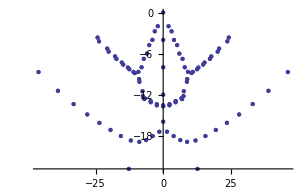
```mathematica
-Graphics--Graphics-
```

```mathematica
QNMroots[30,0,0,50][[2]];
{Re[%],Im[%]};
Transpose[%];
ListPlot[%]
```

-Graphics-

{{-45.7291446819274312014490574303,-12.785856553234508927285460682},{45.7291446819274311999329092931,-12.785856553234508923059806525},{45.7291432943048487954919115422,-12.785859609193076680433004019},{-45.7291432943048487939520933662,-12.785859609193076676207203632},{-37.0601204934320842731387169721,-15.217316739761049313933511161},{37.0601204934320842723013660626,-15.217316739761049314088201317},{37.0601091079171829856147219528,-15.2173169260799774804992884},{-37.0601091079171829847657302633,-15.217316926079977480722321801},{-30.183068982596557276834173085,-16.754779388274313429447894413},{30.1830689825965572730839783158,-16.754779388274313431011868881},{30.1830467043268557441982550927,-16.75477269494473881200274412},{-30.183046704326855740766643879,-16.754772694944738815564322577},{24.267920786783379265785709608,-17.805736015859958695178828961},{-24.2679207867833792643811561985,-17.805736015859958692642262202},{-24.2678837328064269110360034995,-17.805716206799644029786570977},{24.2678837328064269093374375856,-17.805716206799644028823211193},{-13.973602005207323356354736464,-26.0704072623492402602654147409},{13.973602005207323356337526069,-26.0704072623492402601979849416},{13.973608035293673593059435809,-26.0703721214158427446110214756},{-13.973608035293673592691669831,-26.0703721214158427418482144238},{18.9482752392693384419300621685,-18.522054973299186952185975451},{-18.9482752392693384407379546758,-18.522054973299186951059280263},{-18.9482129784563831227761032167,-18.522013246459967919184606962},{18.9482129784563831226635844725,-18.522013246459967919209259093},{-24.4074826211312416512458376677,-5.5429582554114601993906553182},{24.4074826211312416508077227476,-5.5429582554114601990900919753},{24.4074799087864164735817761934,-5.5429554911697129358945056403},{-24.4074799087864164731766078634,-5.5429554911697129359717927638},{23.6954174366646332203038956641,-6.0958743083345706902188882705},{-23.6954174366646332202498284818,-6.0958743083345706903578533894},{23.6847297899868463407043968064,-6.1361278041442513902533007448},{-23.6847297899868463406746397041,-6.1361278041442513902711674184},{14.010243294006389073564403653,-18.8976636357933307889337199724},{-14.010243294006389073326729334,-18.8976636357933307891006643508},{14.010142842344967769101477129,-18.8975955843720806702793497639},{-14.010142842344967768934463705,-18.8975955843720806702382752752},{9.5720258864335011425240665151,-19.1204469418233992089552674554},{-9.5720258864335011320225946613,-19.120446941823399206337378835},{9.5719560650644070323560164337,-19.1203333449055088273822743389},{-9.5719560650644070326685975191,-19.1203333449055088262616962115},{-20.0294279523707923684158363885,-7.0425121228676431611592422032},{20.0294279523707923679478370843,-7.0425121228676431608002271144},{-20.02942173115744167234764488,-7.0425080881984405630213607469},{20.0294217311574416718373728568,-7.0425080881984405626988956213},{19.3396226404060418337864529147,-7.5012561778256444698344757988},{-19.339622640406041833098071053,-7.5012561778256444696098260971},{-19.3513166221072427860502060374,-7.4545037962532303982752494783},{19.351316622107242785690056023,-7.4545037962532303982916463007},{-7.2279103126020105578375282098,-19.4243290363237242000648771228},{7.2279103126020105593490947619,-19.424329036323724198852890701},{7.2275586831023599941304428699,-19.4242625047911986879556355426},{-7.2275586831023599548023561981,-19.4242625047911986748605702997},{-16.5528036626248899285249362339,-8.0262666144922907363657284486},{16.5528036626248899279865023364,-8.0262666144922907362387221843},{16.5527913452165626034723548411,-8.0262637157437062998795656303},{-16.552791345216562603378728548,-8.0262637157437063000586906761},{-4.6163630882278007860061095615,-17.7131638528479895062963510265},{4.6163630882278007860561700015,-17.7131638528479895058613206051},{-4.6162635021083239003347775578,-17.7130492523609693839650737008},{4.6162635021083238831830026363,-17.7130492523609693798370334564},{15.8902383615661096033168811334,-8.381308354920104198902700437},{-15.8902383615661096032559407115,-8.381308354920104198886337639},{-15.9008316570182069081925357162,-8.327794478695034089233806249},{15.9008316570182069081938394777,-8.327794478695034089228403467},{-1.8812705497634897775341241172,-16.5604755957587967464997025174},{1.8812705497634897773718122144,-16.5604755957587967463740813667},{-1.8809891102555099211282426028,-16.5603061196793029025405529959},{1.8809891102555099210758706776,-16.5603061196793029024968521867},{-8.2739641455753604647449321283,-14.4568077289675104376083651705},{8.2739641455753604587222937817,-14.4568077289675104026789944617},{8.2739235597003786172987984095,-14.4567735174926517216626798041},{-8.2739235597003786842373539487,-14.4567735174926514954973913969},{13.5570471265757303202521575011,-8.7275243251600523107913600205},{-13.557047126575730317427962126,-8.7275243251600523055832999749},{13.5570293946145110139267882738,-8.7275274613451390945292871719},{-13.5570293946145110135862593011,-8.727527461345139094575812671},{-7.6885605034174865813440080652,-13.8958342343420006774352892449},{7.6885605034174865820988581125,-13.89583423434200067578723207},{7.6344319611578362793717992053,-13.8447313474250683857380320685},{-7.6344319611578363142397609167,-13.8447313474250683615362381029},{-12.9206554216088169253617660733,-8.9966736552537851243708923687},{12.9206554216088169231273818644,-8.9966736552537851152106271519},{12.9283157825345288170080456609,-8.9362046984224732159209286201},{-12.9283157825345288177653315592,-8.9362046984224732128843483713},{2.35539452422×10^-17,-15.4036062411597244366895900765},{-3.9214848662×10^-18,-15.4032508377075171084866610309},{-10.8608288277790141620714557392,-9.2380241581903152237501365994},{10.8608288277790141618721103651,-9.2380241581903152236397856847},{-10.8608530183020793684467514839,-9.2378210048544474771903949595},{10.8608530183020793693266457202,-9.2378210048544474745780482957},{-10.2267836492029444803440547725,-9.4380962474958027860485462673},{10.2267836492029444770490102792,-9.4380962474958027878155955712},{10.1884083322905312301132812306,-9.3731725325267319881137360648},{-10.188408332290531229742651447,-9.3731725325267319881288188863},{-7.0302820790966252016868429202,-11.3874496251925076972202802732},{7.030282079096625201958262266,-11.3874496251925076966119368362},{3.192405×10^-19,-13.3001189496948951069525331197},{8.930793×10^-22,-13.2996365278273206518963800237},{4.3804517579721100080540736609,-12.4213583323626498964768767457},{-4.3804517579721100112689698786,-12.4213583323626498908091826393},{6.7598318065714328035446625182,-11.107983088396201876466567488},{-6.7598318065714335135343707263,-11.1079830883962013218471288683},{-5.2416310213282495183403407486,-11.8964217201553959781279793643},{5.2416310213282495035102338466,-11.8964217201553959554142840609},{-5.2434860489848568851378059635,-11.8938535941755223816264984426},{5.2434860489848568900998213055,-11.8938535941755223749216466637},{-4.2335748586014399939643880163,-12.1398691202382510036819763065},{4.2335748586014399300548242146,-12.1398691202382508869681009844},{-7.2750893997938963640810916199,-10.4246084946092825892646052731},{7.2750893997938963330621365456,-10.4246084946092824724612595079},{-7.2745495484756186645646605226,-10.4190802006886412687765419349},{7.2745495484756186657923241721,-10.4190802006886412552602544083},{8.5983951767027830871787582901,-9.22204120008638797077724462291},{-8.5983951767027829003873690419,-9.22204120008638787749893799814},{-8.4467152923127683165709864239,-9.28750261874665455075873361314},{8.4467152923127683078343407013,-9.2875026187466545578658561412},{-8.42644574441136690478845596,-9.30148937452116369719737294993},{8.4264457444113667989151779405,-9.3014893745211636462182158182},{1.7002263720834419365243147393,-12.3391732954897695375241949784},{-1.7002263720834434408059991006,-12.3391732954897690505310685732},{-8.1975652983606613711205803112,-9.36600291507774732368076327615},{8.1975652983606613711284187444,-9.36600291507774730075320390697},{2.8897097071788809583395245708,-11.9925086018640279905654807155},{-2.8897097071788811001393180999,-11.9925086018640279276227688363},{2.8934194572294727894205282927,-11.9890829339866854609232490315},{-2.8934194572294727407043897171,-11.9890829339866853431078402681},{-1.5811304755327054137189699234,-12.0694108576840604877111292048},{1.5811304755327057026626307994,-12.0694108576840603496679027241},{-2.81977781131×10^-17,-11.6700429305817278284990300547},{-1.3625372844589×10^-15,-11.6572923128379231534223703191},{-3.408791×10^-22,-11.1453855269013940513980038321},{0.0252598150781179663556621958,-11.1256318428690438142860766719},{-0.0252598150781179182671382402,-11.1256318428690415212074332248},{1.40011379×10^-20,-10.4941072353404260251371860951},{4.87065204×10^-20,-10.4747352890629221318214413848},{2.80808918×10^-20,-10.4381182078848277350265587632},{-6.70031093068503495592745839334,-6.3784974305365302897072784561},{6.70031093068503493691400224595,-6.3784974305365302948190781745},{-3.57961×10^-23,-9.21387526049862883712643448843},{-4.29354×10^-23,-9.21385410670958239517615953376},{-6.0947973384075931100586658003,-6.77686975171252443432152941032},{6.0947973384075931096788037758,-6.77686975171252443197705727014},{5.9156264527902730927099435462,-6.77597387308633198946676542999},{-5.9156264527902730885731964802,-6.77597387308633199007636982061},{-5.9137696946695258946014795334,-6.77704661446470253895450095101},{5.9137696946695258944520138907,-6.7770466144647025389158422728},{5.603713×10^-23,-7.80898990381511171550191168611},{1.390195×10^-22,-7.36104732009326086096897624344},{1.430432×10^-22,-7.3591779955301155401047716532},{1.0292589×10^-21,-7.31257702382948382923617227308},{-3.6455388×10^-21,-7.29923743284643053857186831331},{-6.0358919×10^-22,-7.28426396759075806704846835734},{4.76232399097591070540817442759,-3.5089319067773117112194537957},{-4.76232399097591070540609487234,-3.5089319067773117112213408287},{8.0462×10^-24,-5.86184342861125259803543563074},{-3.8734665721878516339261623079,-3.94073495294196429615346704356},{3.873466572187851633924504626,-3.94073495294196429615326620525},{2.0687×10^-24,-5.52007189732844233883507989802},{7.5573×10^-25,-5.51980771813304906584791783012},{5.1676938×10^-22,-5.44762658410423168416024376741},{-5.3628259×10^-22,-5.44602794929496775167568472929},{-5.769282×10^-23,-5.41974012792376728531261039828},{-3.5858477858348542738483037937,-3.88181179124638161057318891248},{3.5858477858348542738492769998,-3.88181179124638161057038297264},{3.5829889758379975317203838518,-3.88325067745541902644457342101},{-3.5829889758379975317179816577,-3.88325067745541902643854858334},{-1.834003×10^-22,-4.3827272059642728922749442307},{-1.9172658×10^-21,-3.95933928875663199530491045669},{-1.41500995×10^-20,-3.95856510816616813105360203751},{-9.0669068×10^-22,-3.89671980521132863366647804499},{4.924296×10^-23,-3.68000060996525264416106892882},{-2.439639×10^-21,-3.68000052957144993934688244607},{3.18901858038616445552475519685,-0.94411171838290795032602160141},{-3.18901858038616445552454066162,-0.94411171838290795032604683187},{-4.567909×10^-23,-2.98831870607183027951709780046},{-1.521271×10^-22,-2.56842619383841178623494241761},{1.6149×10^-24,-2.5681082502741285398696693588},{-7.06515×10^-24,-2.3984369873327607157836989093},{1.75811906203882277690847919278,-1.2974954508688942106961748949},{-1.75811906203882277690220796199,-1.2974954508688942106801217425},{1.187617×10^-21,-1.83999999997262138792258958775},{-2.8693995×10^-22,-1.83999999928807962990734080006},{-4.421×10^-26,-1.27306113490453938349153111395},{3.07×10^-27,-1.2715668242230451240185013586},{-1.729701×10^-24,-0.165850542958693377604933712563},{-4.69982914×10^-23,-0.0271852764819839942607037553576}}

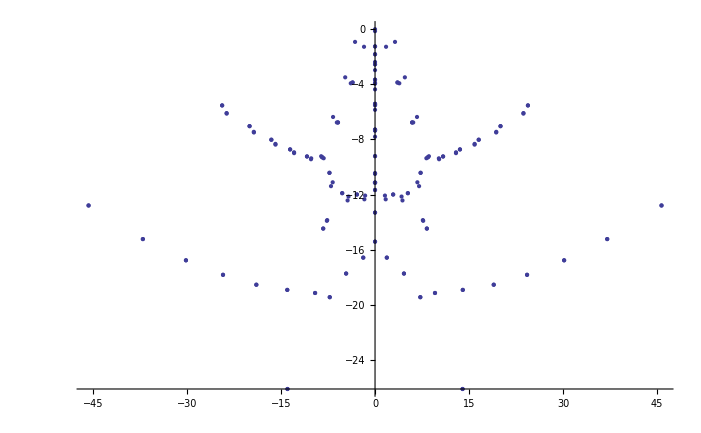

```mathematica
QNMroots[30,9/(5 √3),1,30][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{80.889346304299460209114969875812884531758700586844,-19.84458863663851168793352429351916022734906926645},{-80.889346304299459800941235181476663436502012241359,-19.84458863663850954697141215442207419197081505899},{80.889346223672167574388463221664360680027473229532,-19.84458883631795287612627897493393818009439385781},{-80.889346223672164880597739843550857091992793280573,-19.84458883631795919964054784211942124502819684729},{70.40405418100067290972171745779242068945280666425,-23.01397513113493311321533649742416376427689405272},{-70.404054181000671687935000901671909446400361954285,-23.01397513113493017966898997825376346447425676837},{-70.404053806966941929855932473609891404493771129054,-23.01397516287049964645112313449578204621352142269},{70.4040538069669417444029952045207525161223517469,-23.01397516287049258978772341127905720601994052357},{61.990471190420886536819921836174913523338560418826,-25.20346453823821117852018201004230756657851876076},{-61.99047119042088402410780378494705746381344407875,-25.20346453823820861630218688205375853791900345504},{-61.99047055212223680400898975688720156476511900729,-25.20346437655546398477544137406288735127612325232},{61.990470552122234172880423819537929899664704881979,-25.20346437655545776133064304685041581932531739157},{54.691581733237892058529830701793479936542668017762,-26.85461144896354200300312485457864298985568135224},{-54.691581733237888806495001711694184814516133869768,-26.85461144896354050804303180466390410161142324702},{-54.691580834933483414775126650684979690153102808372,-26.85461105544265116131595725114929877712526578256},{54.691580834933479285943746121926152878963130558391,-26.85461105544264660987144099892506189241484219985},{48.133655601995771247490394085304687418197664242311,-28.14153734461677365420459147896954549680789248409},{-48.133655601995767896201380014999736153201808795434,-28.14153734461677330444247815285494056844639690956},{-48.133654427647409270742961446356264455255452813693,-28.14153666574157566651816618804068564475273790372},{48.133654427647404633517153185489223874108271825044,-28.14153666574157293378461182374486525014261376378},{-26.43971722442395643661852047555472225646402203545,-47.156775606763470387251400684909770621138536954226},{26.4397172244239505355524932022137973065920257803,-47.156775606763469471314864304625741960574613188068},{-26.43971779475270103975901001532888526601537850676,-47.156773405208423121767484940405527226805053904328},{26.43971779475270514435611656414913668592661257251,-47.156773405208420273107978448801138472067707793153},{42.115044391062915722274592494782359161648752487593,-29.15505820885917058708220467240482714545789917034},{-42.1150443910629126965005444948341284288006387939,-29.15505820885917116339164285233443784426774686619},{-42.115042889982590924012866167246242242926228982684,-29.15505717736829220602282365065031089956024074249},{42.115042889982586489506115766022987155682252153307,-29.15505717736829100743158609697893529512578661724},{36.504744336446390279568059225996053480275513347176,-29.9467132617896346584125440630039728264545029459},{-36.504744336446387788275239597609642001264351496351,-29.94671326178963586262374660619102554186007163049},{-36.504742404305636080781577102741177374339427126456,-29.94671182107370714397838868259317317828568073594},{36.504742404305632222897352947362549768153037743523,-29.94671182107370705122419174932414793057767391894},{31.2080941402537584868580776381982350281733019857,-30.54259977594613815276228527438992994370135105395},{-31.208094140253756575401104528486637936385366362378,-30.54259977594613970808461207356650464329978893916},{-31.208091604810261906512441660221850693976402500496,-30.54259793843946664008680597318498279698220855859},{31.2080916048102587342774863994410551279325619039,-30.54259793843946725705640915066521366775697883875},{-18.71701931143534722075178224403200892079288622559,-38.699519910576002967498355275566738946175635223256},{18.71701931143535095144846385932863525330802905879,-38.699519910575995482164909389909881740175424376556},{18.71701639480382133288827379854843078248451608433,-38.69951353583900097604867732579518214156804899471},{-18.71701639480382880932195069797337489117959242001,-38.699513535838995957881013458156683318586064610568},{-41.98899779670928319231944407625416167921778618935,-8.952204419929528480777475825778387510745572339546},{41.988997796709179747158656091561390713846657347956,-8.952204419929431533963469405493752073235098088976},{-41.988997737077059214135870945547215042769478912691,-8.952204346475215775246091023779667622334406228385},{41.988997737076947279345472678446201569013091006591,-8.952204346475406014116600184934790873071682479358},{41.275306720815429950172090093481027168916261621821,-9.599709951088769355887839753329127929959567954368},{-41.275306720815429937132041294323345964456887269831,-9.599709951088769367660586526722026538855438897714},{-41.271953932425764442141274361724549389148899375211,-9.611642976463074882834268490755759600721384624763},{41.271953932425764419297739614723483949372103971146,-9.61164297646307490138431569619212822719349316981},{-26.15433605138928286691423654344459603226774340511,-30.952751960645787547166440068360703345818408895154},{26.15433605138928425864945824621152306730097387602,-30.952751960645785858018263996743415680477904407809},{-26.154332624765089287190698146240513483123860136,-30.952749962663790175394708579249863725456867766135},{26.15433262476508675942638884078961404434262965588,-30.952749962663791205397501957005662339347313516039},{-36.72376130047904347118738491098067561059060402011,-10.75014087678985545413009808622748018167260916479},{36.723761300478927404749960791863970535488269191668,-10.75014087678982193641472531410471462724304313229},{-36.723761194597795000521768566453441307197864997117,-10.75014077109988245686398295995944649256011335717},{36.723761194597704843144417928683651398785351358096,-10.75014077110006630284767122230204604633471181498},{-36.023881136122795350048745441237468443041810351124,-11.30778920621622320000842639479058320213863656565},{36.023881136122795326751011808715656581626338014171,-11.30778920621622322767108391577338264037585892401},{36.027630638180462408996063914363661141023340358265,-11.29454883160681986840549005474662235367109663101},{-36.02763063818046239408190590684651681749285495415,-11.29454883160681988493728158702604078699596595721},{-21.28273163118338814258189289328987957239753309822,-31.169047978515553640196421531987700254159715081166},{21.28273163118338908944335995818373325229536678377,-31.169047978515551904718750206053654008923482029607},{-21.28272688163351113769076342508139591262553925988,-31.169046729869608987495023288138884831219007641478},{21.28272688163350916317823977567321069449390765082,-31.169046729869610328486915494122816244972987679718},{-16.61928427068734382018917701320515015079995595711,-31.193218653311301228348031245314985881025398750008},{16.61928427068734493097681663462880575150146472775,-31.19321865331129930999758295476806786318977486854},{16.61927997374785882439001466467643105375682969184,-31.19322077326245609081419673809640313288838432877},{-16.61927997374786095734098971215369647928168444342,-31.193220773262454525214966273249050458093692668741},{-12.92653531257570228229197993046483731971338951262,-32.290219226943021721929182210596223952584843130023},{12.92653531257570494014383993662481453335850410986,-32.290219226943011860531512938130232581526231728069},{12.9265344396725850433583508567594988836513320829,-32.290206320273723056445786930664115713772860171407},{-12.92653443967259157901026758147704174828804226962,-32.290206320273713423182095954466521386980363477441},{-32.497596803239564114401894932007830291769096334058,-12.0096359182291688281331432543594879198281992398},{32.497596803239468675895608649504801427677477345174,-12.00963591822917413781911224608123267801596726035},{-32.497596626072014540538801608724432735450066077537,-12.00963579040474630340449533650927009528946670908},{32.497596626071945903856494044219711048233430910221,-12.0096357904049207004587789943896480251066209035},{-31.81182432528674348626983474404447255048938211344,-12.4879857017043378394128274190256805411386647309},{31.81182432528674346403043426065990444582662676975,-12.48798570170433787700082213676949316075095857617},{31.815688720600711176284313093323667459563793467155,-12.4734603397066526141206467678841358231940221726},{-31.815688720600711159861032005884401895266465123185,-12.47346033970665263662597280784589857311905912637},{11.3786039553331002381261564410152810817192250075,-30.681107954445034413450003229637905550687427233397},{-11.37860395533309723692280644779805605641585982092,-30.68110795444502901834788847855172070824723086029},{-11.3786121511609423814850486118614319491670407708,-30.681102505460512589203745909299060759936778119815},{11.37861215116093861822553490409818413010225101667,-30.681102505460508870036222368626692094450379020855},{-28.828246059723465800767618118609099113219242153081,-12.97430186436334971707781967204394659702939731568},{28.828246059723398049109174878046268727273119306296,-12.97430186436336763175356422241335526222936526145},{28.828245781465633747856764076816633132417509647128,-12.97430173693576873948363022165365519763682292162},{-28.828245781465686176641761527461931752264162319929,-12.97430173693560692092928367649971372075642322373},{28.156056241397106280461354496123904329876771243601,-13.38528693512446562226564472519341622561216366348},{-28.156056241397106300177959460607227287671527202653,-13.38528693512446557367908616594299864655218578955},{28.159805276678789554432429471981886336045894396397,-13.36945180834809613339420985208994439560246793723},{-28.159805276678789536666115287849605948714460299813,-13.36945180834809616377622747176951505360502392518},{-8.115811403231460612521773166498771512296700952298,-29.485795439886010158181182759695225445778439852039},{8.115811403231458019232877037878409648155936755941,-29.485795439886004323601851347522318972172913692641},{8.115810815082605808732320689440378379035467436381,-29.485793920016263646553699326986552573131346178063},{-8.115810815082604174067070599466780621631215723206,-29.48579392001625632639418149991502250585120597481},{14.6145259135074041115108749649769064521820853839,-25.076813687749518385810243435608609023995599571984},{-14.61452591350757015924080083560118047875988987112,-25.076813687749109589003435731674372614533262334329},{-14.61452525626411488449414103962472911147846635906,-25.076813137787475389170603234697250708604031297863},{14.61452525626399053583127646101064749056254005199,-25.076813137787359294173808387215277794951189331293},{-25.528195217803372529576471553291469914802452553665,-13.7397782145110980080272229167281138422462388798},{25.528195217803326243473634298559719032147896154677,-13.73977821451111261108760275143939342521597248091},{25.528194807798155448848746207247294213891737217357,-13.73977812961622615844539836497336847572639315216},{-25.528194807798197479596829411009852014406580633085,-13.73977812961607679738505748386265387853867557137},{-5.472128382954735315805799331940183873576673248135,-28.394888654858560444364464079829154102984383824098},{5.472128382954730522427524042906223686142458482267,-28.394888654858554393398734145650753413591521394883},{5.472124475500598039018594694311415068702644864138,-28.394885444574602957469617710356610014250861062707},{-5.472124475500593320400581708033707674302466099565,-28.394885444574595080433010205195178890101917720098},{24.8696787060113708639801649481471391676377543711,-14.09137009279218036850418434531311738355086227707},{-24.869678706011370879555861120783377999471650454759,-14.09137009279218030747659502980627179227007381548},{-24.873083614914317625518541843449032527390715376131,-14.07417005144423563978048590305994644581007830857},{24.873083614914317643784047808369348350756421449762,-14.07417005144423559869613338835608842125981014517},{13.96627188500348980155136918623483033279141019813,-24.451220103944846389255147016949815125800337458448},{-13.96627188500349020929556928299115605286356435825,-24.451220103944846155266176182393394037112237932171},{13.94921990271994032202476406853542966067004451383,-24.436022158814278702045125409254953897681017042783},{-13.94921990271993976053099116407220361982896296217,-24.436022158814278986489840646178614236599550829331},{-2.944660757106052491172996049231463438211017320832,-27.062128125629978847785684192376037708604040963886},{2.944660757106046475044713214639343492466751627035,-27.062128125629973415913575579241473496317396919935},{2.944659216670712382996532720494366567909907392646,-27.062126106809384529009946579670827393925292837111},{-2.944659216670705515023347815295182355287087562644,-27.062126106809377433060332797608671185340524527184},{-22.49712991538022157651170506083328371365147937618,-14.3555319328052325906966228827414904019536687974},{22.497129915380188026382336473651036587648512051127,-14.3555319328052378941925208621422770505282930101},{22.497129350435005834008630074618945862567199566299,-14.35553195993805945499052878788740083652253407701},{-22.497129350435041601025511705655693969322670040369,-14.35553195993792073421618095252823932794481559056},{21.852294906661652521598044808202077744058515652524,-14.6538527605281129795818023483181455078753568169},{-21.852294906661652530956835860291055500112463976728,-14.65385276052811290458816855851059174555237694663},{-21.85511324347904438719817705497522358294393970948,-14.63520062547074212238298991130164237584779343021},{21.855113243479044403872111583685878057148825300956,-14.63520062547074206747760410691077585564799101181},{-0.45786211222021511210379125270474419924968568723,-25.524687014326516386947382091424485067669297742272},{0.457862112220209779759610415861053212030751374565,-25.52468701432650734992620269452156938290804771782},{0.45786126127931295430253781038920161875041954539,-25.524683624728835742461538748271111148448306737652},{-0.457861261279306347060098593552701472151551042779,-25.524683624728824329504230751648769924206483432364},{-19.67097472154684277504092815101315371362003700486,-14.84973244112273878001075896657331258710447786747},{19.670974721546815216733808748657293176266531068666,-14.84973244112273461903887476544252864994456268195},{19.670973967627566675954102874012842710200623435895,-14.8497326745937817650981639814872178165720565742},{-19.670973967627598587173676015266585676810766419483,-14.84973267459365126459114852322412077994802855298},{19.03922878010271583482372590186922294241611979623,-15.09975188884497998327858449695036468968829530308},{-19.039228780102715835392466402533062229754172088624,-15.0997518888449798933917300185221057408007125894},{-19.041209830394387118708253898468568498914395519402,-15.07948934892214005397822051995651929249625315246},{19.041209830394387130446748532787438883239838625434,-15.07948934892213998281241865634555198339155647545},{-10.60290910658081663697919081296673389706401037992,-20.7554407626030626486700109955883163811349616138},{10.60290910658069155171387756173679183253287492892,-20.755440762602958466937364691023157195633488277471},{10.60291520995643430534529554703782769815301035988,-20.755431305974386458399582705977399679647667272428},{-10.60291520995651833107078926624858389873420210584,-20.755431305973815977745327434856506201466025640667},{17.005735511150025106839169713036759931248788162426,-15.23808242539487914117480477157773038636208326931},{-17.005735511150053928018911409456709701595628751204,-15.23808242539475449930659774657928541297365063518},{-17.005734812747786140438714640964560900717567306535,-15.23808296948863503396836844053475438145057418275},{17.005734812747760540581382048181759089169230692913,-15.23808296948862389364810528591376691261327571926},{-5.0884188613348106560442562124553×10^-17,-22.756757937401870967231352522067279945410135808117},{8.4505722166724505724184504635078×10^-17,-22.756756492775943465884315644152109530914763067671},{10.03913193737434601842967122853585127996366690916,-20.30388156130864861826402057648424128953360560218},{-10.03913193737434643095949961384776885650303828544,-20.303881561308648040289401658021646294016605548697},{-10.01039332001164074497873287350409956681311137751,-20.26765129962369788731506162829222115271921092919},{10.01039332001164129387559729827297503749948077581,-20.267651299623697215559311102017689543241023797761},{16.388310583259072631725119709523817628117710365411,-15.44652341741909297711782086384352676659504295679},{-16.388310583259072620339288295107677560357521963166,-15.44652341741909287220169395457094776829207223577},{-16.39046482440152138191509537750021377188887566934,-15.4258377259511526931989918344798966785951104831},{16.390464824401521384126593308072319752824111228396,-15.42583772595115260561452115559195118446684744744},{-11.00421646349294474960138663658675159236313251817,-18.253260579009302780623536699189079555245252883919},{11.00421646349294472768440684410017607768821470164,-18.253260579009302621034156552166755248525183670857},{14.41770898079537302552864793097445941084334278111,-15.564918246753550609299072066552614128377674683808},{-14.41770898079540122363295853834631176862089451862,-15.56491824675341607987411087094398370327531807486},{-14.41768365356206678124919694346752473439879641982,-15.564830193685080635417832163684615554937932330434},{14.41768365356203846759944318009982368822879929429,-15.564830193685064127693743260330095657044062285105},{10.88687246741456118529748793697566853995694294343,-18.159735147174657076938007333745286639153002921469},{-10.88687246741456110823650640847632804618242833381,-18.159735147174656881039549013738678165060023407422},{7.665147191686489728985428878002558151942157057247,-19.729518097859746086896400306842443039225175185603},{-7.665147191686489768577010282031695292122590019823,-19.729518097859745817697212889359568899449762391205},{-7.607897239628921052339702996077550811579721028412,-19.612734032064241022550786146501533855017945119425},{7.607897239628920937239698396019093371942154514256,-19.612734032064240523075480070957463115526899863271},{-8.703925255696492004883432496075257265171637479334,-19.13595882398778502614589565472920047662373104452},{8.703925255696406627934990968739289926610755980466,-19.13595882398780409802009704548291459456392987204},{8.70409064464304978680574507491716729886307501155,-19.135655284531471423799086598243702973217058065875},{-8.704090644642790308627826921318732754069740529512,-19.13565528453122472198121830413757262166983900497},{-13.44326470561095032475943890061355812444886260709,-15.891461252623251130634896449032964473829442728084},{13.44326470561095031795993533302116361758385449567,-15.891461252623251098601069302511233618875280853784},{13.5853737440738396060245361136254225468928892248,-15.757655568454498676747679242413596656872036885226},{-13.58537374407383963526446815407113033689519681849,-15.757655568454498542248298673598699865003107388978},{-11.32490511541818179476197938289888621926364649568,-17.377715214839319785748443588737686451044064808505},{11.32490511541814382326062266569693595255979030441,-17.377715214839327318299544270547048381147891177875},{11.324912133928754877767453101261308629062510997,-17.377362491644787250036704265670955680531071511677},{-11.32491213392866637109519971824028657537852378903,-17.377362491644660110238310699885650481896160645953},{-1.087721253776590079610384119558×10^-17,-20.523753179309753334261969335835940361599336589384},{3.2492899676936044757949511683948×10^-17,-20.523749003506937726384093153541065866015349991332},{-6.091661062986035294305032045167547174734373532173,-19.485902877297205874529528765692926083315972010607},{6.091661062985930688808632789745768860141703478347,-19.485902877297215850293314757641503284087414962901},{6.091909663269608952335645444494271701370893267723,-19.485664976980972804610393226386920691632127575644},{-6.091909663269237323994639061957911715554947559312,-19.485664976980662542222314536207678849838781832085},{4.923871526509621161809451251647469081517033893182,-19.794574945643673305562048087011360372317793851321},{-4.92387152650962109733617989582921395044656314549,-19.794574945643672979633607356261883739239351643108},{-4.872989493138898495268617209669430335627985190121,-19.681596059584746955476010520736280089346063813242},{4.872989493138898180093427063530294661704963911594,-19.681596059584746447756330764573151541837404317555},{-13.18723959840194408137603749009408377113752675486,-15.283137269047027156148438844399623238445850459207},{13.18723959840194428478902749532909349448089755079,-15.28313726904702689451302767577112495616364663853},{12.86252908305831457793454359938343557378824518106,-15.466536714824225888690085134936379946578576193216},{-12.86252908305831441997885082625780925402713283422,-15.466536714824225724146983064012938236096521129221},{-12.66438676952495810824712221419384007097060987322,-15.2165717714824119054565779756800539947048594721},{12.66438676952494832815153492917488122545825387032,-15.216571771482413917236163648709488529663109638576},{12.66347617970963414840537761384937393720505057575,-15.216619089552363938469855490702593902170380221956},{-12.66347617970961188607933507728186508795340232471,-15.216619089552329588983776779851045327671089616042},{-3.441183383361853139786305006004284188910052543779,-19.313503466258026276641936716691227210288471360732},{3.441183383361760310807800279615779537966839156095,-19.313503466258028690114686464135983822150311844123},{3.441456070875622027250205076444135553879422037051,-19.313239133056033344031776694605376867844548210461},{-3.441456070875169404524174145737220056519630282763,-19.313239133055779959078152975856079664835546550563},{2.226855062752599084637427741583643189815523906665,-19.467620632898971601563573139936114702864501482292},{-2.226855062752598876300651483418141660540533680082,-19.467620632898971301623813683717258561076413495673},{-2.171552834948281375222166438566966480431286506349,-19.346961501166878810381696498968917594140900754785},{2.171552834948280842633641120190412206371687057452,-19.346961501166878435889668192245547967834848968709},{-2.4582653767399193708019229025414×10^-17,-18.989368060813315281528863390118643317994842927884},{-2.58950917836188713891905526082962×10^-16,-18.817390599193971337606299121639478596417713856975},{-0.930048815990522982060515749475989661916032245066,-18.758965293289850150668705476880349515295541790691},{0.930048815990457230789944560353488888968987758737,-18.758965293289835114059250031728180454440649726338},{0.930230711959626772494745365020682122451941820233,-18.758835405286646744514148807060712717021228290256},{-0.930230711959191952746458493906021556500642068357,-18.758835405286462494692607653923647430150990031683},{-1.16412745880206539822519507401×10^-18,-18.483841579627722438884281197895956633986893826943},{9.900102822325133653395751318692×10^-18,-18.483793756190743062633698039054401841820809080811},{-1.703829959625067214827034340834×10^-18,-16.575715817081400638458442041616270104622083247563},{1.8313773500042146741566535766×10^-18,-16.575712277780943518086887571332709210541717491997},{-10.85897339150620405648580359226502460974327626778,-12.269098233337369589289819905759655011364878686206},{10.85897339150620405655262790785481389213087123541,-12.269098233337369589166106429545612717639374465479},{10.6646590011248859553324468382829534148831215184,-12.421921616537647781877483519996859257325868016111},{-10.66465900112488595524670842680181462133125604185,-12.421921616537647781718323833708536094637212930112},{10.50299983861041653630767248628098338584512895982,-12.478821386050233568281152667427924259269152207213},{-10.50299983861041653777975293903044523449587227097,-12.478821386050233562634932449925772422357545978625},{10.50296917107700783958362456436224612369578500931,-12.478844964765511089509822856640089912723541389164},{-10.5029691710770078167385084469759499970067495914,-12.478844964765511090967726361935139366020486758383},{4.2631457598779790540388469395944×10^-17,-15.292223457696171279499662162078179811787817268901},{-2.891767761725136921666874322132×10^-18,-15.045820918210285448712906546482694751257180577007},{-1.96878517496865907561498212299811×10^-16,-14.901698184792203096834587823715794025557460235536},{7.977667991204994847089909671662291×10^-15,-14.901195353024364893101022317434048918727142798817},{1.25364066974500839143267233105×10^-19,-14.721780012059847120087969016371918354903116650159},{-3.30078696793074020117186312855×10^-19,-14.721767456266601131801169618431923685532937398552},{2.5418031991080294930875730922×10^-20,-12.880115533569108196204665032166745212023728840765},{-6.384723090152994624093840178×10^-21,-12.880115143206386918572107982438123620367328893227},{-8.639372159191630712264719461521102368285270578802,-9.409782682356476217551626524728152610964946168737},{8.639372159191630712264721390006395074817298423527,-9.4097826823564762175516105794192506137873309399901},{8.399967746108110284837013151843966491940000323058,-9.5877917176063232467641511262143113272262068461358},{-8.399967746108110284836990543887854923549131493321,-9.5877917176063232467641354874513162457443147948486},{8.196423666265383161957880435833921283628198936225,-9.6484328567013141513419064522560356514912609774615},{-8.196423666265383161957807196790173269599755071505,-9.6484328567013141513410187956232553588623716635641},{8.19638712496587564462963020740551774111289393026,-9.6484616979481854234578167221766811931255211481478},{-8.196387124965875644626824309216208208099929171397,-9.648461697948185423457933930238692411290580904957},{2.5425852567670921444803595241442×10^-17,-12.294260801659556083333953852995711519881668398744},{4.658324084900813254596641091319×10^-18,-12.090567925630855458235132950811331247491846934635},{2.61185639452990352413333233267538×10^-16,-12.005687920286775853074376631193485851649001877564},{3.775069668817775493496658803106388×10^-15,-12.005297309614340189157184198676913860161953001316},{7.02076559272446827624089016×10^-22,-11.04000562144436390328219828114040371915150069744},{-2.015810647898276870278635523×10^-21,-11.040005551009794409778483407036782011046172608931},{8.929363884790027520218585139427×10^-18,-10.220077506377492342349137095672288511553879302499},{4.536415521051531158683195457521×10^-18,-10.045093031799994367644069636554555653938096720467},{1.52456803820156135072807290458584×10^-16,-9.9874713408569376630306061689679100523283092213669},{1.068096543763486513340512196344108×10^-15,-9.9873044942965132455328962315240906469529211555304},{-7.916475779755167691525142007×10^-22,-9.200000213073102326724069667888162076831572425606},{-3.31621045802488951631370206×10^-22,-9.2000001973375454611412590349976932454574892409261},{-6.473529963972849004344611341264360279482076826573,-6.5359243346258019997272938893728621584672915185769},{6.473529963972849004344611339201879967417494659094,-6.5359243346258019997272938874462777565299158466237},{-6.157142786440018512450621592023966166007007786801,-6.7471960486860574652864554281823549527111939460822},{6.157142786440018512450621586769602574918821285216,-6.7471960486860574652864554178737543258126803365869},{-5.879164356266860528000386557053694260855495274057,-6.8071539229990364851617795656442868259345712899871},{5.879164356266860528000387120055948979858854718566,-6.8071539229990364851617786946838696431546980515091},{-5.879115996928283578438391108115448513450836068703,-6.8071911726839108732221953049541966785611374094463},{5.879115996928283578438390355150448904581224898975,-6.8071911726839108732221930083171230929237239383771},{1.010356398381041496738680955616×10^-18,-8.6113108916329048890995088195706053766036081831473},{7.006003684376426946732430005621×10^-19,-8.4375397473048932267275954345220388833591557517479},{2.1186742583886876889691667126728×10^-17,-8.3869947204373293754670786601415296525456912363818},{1.03268748269234734962673159127568×10^-16,-8.3869533886996871058675251637209950411634416877157},{-1.0809493639269882236877606×10^-23,-7.359999997068941397588543886827978324114673984069},{-1.3121323083666283423592071×10^-23,-7.3599999966722939338330553331423470440087074503559},{2.6141311020380407285527545014×10^-20,-7.1231021354851415503807646764385626053358455991065},{1.9233262765604679359018827382×10^-20,-6.9299097468488285999765702357701060165709845349965},{6.347156702299027586230181841067×10^-19,-6.8807933972303634346503117956953730335783615908848},{2.421906340241647507995118052271×10^-18,-6.8807626359173826513773007962815079626109172356444},{4.4454119486545581894104539870545884741765618861969,-3.66097925358477262220213211040319807133987902302},{-4.4454119486545581894104539870537939530577875316464,-3.660979253584772622202132110400536331887748219508},{1.47500660598596784906902336×10^-22,-5.6552740107117012234109581067411840558285805103648},{-3.9751607757185861520809416161687145075704532580678,-3.901295248113298790965204693773638264075712232531},{3.975160775718586152080941616155837548360472625558,-3.901295248113298790965204693784341706568168115407},{-9.848037414791967780504678×10^-25,-5.5200000001616461038828095033894795842025199772732},{9.195584843624893042644378×10^-25,-5.5199999997226408667534972483252131429349416276662},{1.17502403867278817567180709×10^-22,-5.4332218043820178049925985051114654152566753565049},{4.0261737204098484291525813313×10^-21,-5.3887869619949717966619653393406231408227043513068},{1.3415079945694585624490462132×10^-20,-5.3887515954898390892377141212351556725441294000586},{-3.529405886616355230158009357751403352217527382749,-3.9287085438158828797122144303238942662927908405505},{3.529405886616355230158009356309240348223319908465,-3.9287085438158828797122144280704314404153740822318},{-3.529330933893958299793302925899674631358841245122,-3.9287638260923662169461760402753004183204098781807},{3.52933093389395829979330292258420532740826466005,-3.9287638260923662169461760364908193841491931413387},{1.04409791744681839456128×10^-25,-4.2073085873176420150399488205289935534188140342465},{1.58329672823898807401817×10^-25,-3.9471756563503399579083925814981233947304961154061},{4.6124380023555027379619475×10^-24,-3.923965180463875190921159172761316115831108386168},{1.6347952759019401536931508×10^-23,-3.9239256942673202053256594411453701941204909230615},{-9.205089975088247650436×10^-28,-3.6800000000000539206231373898687138335770100446799},{-1.742339935763211695069×10^-27,-3.6800000000000504061012326222523719284005439224561},{-2.7812600511353860324010190410781706192981719872309,-1.012093471464437925938360186173557556489047740823},{2.7812600511353860324010190410781706151225551680768,-1.012093471464437925938360186173557510179096652412},{-4.32089992078375526772×10^-29,-2.7942906802981254245066920376899671868028155394156},{5.761915233973658055195×10^-28,-2.531890578396189246415584233796536726108835039012},{3.9673025239273323183571×10^-27,-2.5318530174942969778550147007338198568499738011839},{3.362120977648533093×10^-29,-2.4786356272127001963461354338008327450458518223589},{2.015618998424194855627068491356849592390385753656,-1.186335674150954748849424742741851678308409654396},{-2.0156189984241948556270684913568491683553523792865,-1.186335674150954748849424742741851670378211284344},{-2.120579088361774763×10^-31,-1.8399999999999999963201033899914162845600371774071},{-6.12517889865122986×10^-32,-1.8399999999999999889521497976953234083443138391107},{-9.87084993965179983×10^-33,-1.2355274190580228943384572621452350484194825188466},{1.148723702830292598×10^-31,-1.235505465788460969203352000141433155882452057318},{-1.205203351493×10^-37,-0.036585484578249093889914115122807218745800489944114},{-1.3829970120284×10^-37,-0.020197871222523923787303404945586436181489788493616}}

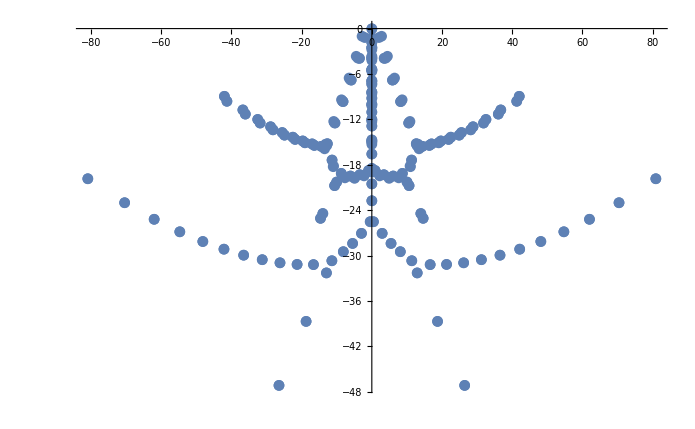

```mathematica
QNMroots[50,9/(5 √3),1/2,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{-45.729418726484702334950845329,-12.785765701752456029174835057},{45.7294187264847023258777680013,-12.785765701752455985536471481},{45.7294180325956864240294249415,-12.785767228269811171679186129},{-45.7294180325956864168418673619,-12.785767228269811126914621944},{-37.0604564494627169729520199986,-15.217221329478390104468217727},{37.0604564494627169639674858309,-15.217221329478390105550057214},{37.060450764518922812619126869,-15.217221418872586894082448645},{-37.060450764518922803592802528,-15.217221418872586895131561339},{30.1834734730677575932256735004,-16.754668343728627389368623594},{-30.1834734730677575208877572143,-16.754668343728627401070446582},{-30.1834623560777987188455047909,-16.754664995240394718499388872},{30.183462356077798646515678821,-16.754664995240394730305908815},{-24.2684023564031696987280090159,-17.805598269082144192761950327},{24.2684023564031696836163818931,-17.805598269082144145979129611},{-24.2683838835222119097287984444,-17.805588372269784856613390173},{24.2683838835222118911220693142,-17.805588372269784879887404007},{13.974021580586637459367588739,-26.0693093126197130995532132973},{-13.974021580586637460959461174,-26.0693093126197130961687142091},{-13.97402464394267306488067972,-26.0692917227316553906383069727},{13.97402464394267306289939603,-26.0692917227316553848998653808},{-18.9488371618554904731318782102,-18.521880736185667292860188071},{18.9488371618554904731230428527,-18.521880736185667292851587493},{18.9488061651142015094906423017,-18.521859897150622399320078232},{-18.948806165114201509532854277,-18.52185989715062239869373277},{-24.3996018139989222883676220695,-5.5440518228214614491148752042},{24.3996018139989222883694476398,-5.5440518228214614490134591929},{-24.3996014748664650278399326948,-5.5440514768206568142426491244},{24.3996014748664650273254499432,-5.54405147682065681380719054},{23.6849603202804045671315957299,-6.1070337219060077022424295489},{-23.6849603202804045671300256195,-6.1070337219060077022353647654},{-23.6796157572472147303289824439,-6.1271663837397145974585138236},{23.6796157572472147300349739246,-6.127166383739714596225158128},{14.010865815389733002976984495,-18.8974243470386187892473890555},{-14.0108658153897330016534389,-18.8974243470386187886183400965},{14.010815905443538589630310549,-18.8973903589904517718960961161},{-14.0108159054435385785960763,-18.897390358990451772475042536},{-9.5728511592590326375042751242,-19.1200472599746514378152196777},{9.5728511592590326569080538719,-19.1200472599746512582753435593},{9.5728172721119313759039660604,-19.1199904059296807332476418725},{-9.5728172721119277404833209387,-19.1199904059296766897981406502},{20.0205931046831874187533037888,-7.0443808120094878286903642764},{-20.0205931046831874187111282276,-7.0443808120094878287355239954},{-20.0205923263745654803273816781,-7.0443803063886137521476530178},{20.0205923263745654798049585047,-7.0443803063886137516284303064},{19.3338169426916814816853909489,-7.4914503534645282475020966266},{-19.3338169426916814805689330061,-7.4914503534645282459940397112},{-19.3396633607154141833303514793,-7.4680642674529234574800810634},{19.3396633607154141830827167816,-7.4680642674529234563834263099},{7.2282949464428957058199374939,-19.4233267460879671736309926195},{-7.2282949464428963850167424942,-19.4233267460879667304624930554},{-7.2281184938905824223412566196,-19.4232929072304053946691631854},{7.2281184938905802213441233275,-19.4232929072303996188787937336},{-16.5430790863192998344588723445,-8.0290190476842707466481129388},{16.5430790863192998317486332777,-8.0290190476842707470937561109},{-16.5430775437533573773392225032,-8.0290186830278584022931425765},{16.5430775437533573770264801854,-8.0290186830278584020599629802},{-4.6168454447623347187771503259,-17.7125428325591208366534132992},{4.6168454447623349520874791089,-17.712542832559120461614744234},{-4.6167973945405917457331382719,-17.7124854774023583382406813844},{4.6167973945405920279558799995,-17.7124854774023582269147247941},{15.8832574938120787989706729465,-8.3707125029149345819320184823},{-15.8832574938120787977986219896,-8.3707125029149345813446605044},{15.8885501409527296632816212977,-8.3439411981527092275918269716},{-15.8885501409527296619968505214,-8.3439411981527092275288274475},{1.8818266611677977533712529634,-16.5596117566994180440214676539},{-1.8818266611677977469307890699,-16.5596117566994180378313009389},{1.8816871432495891437855726937,-16.5595261341412846560228270149},{-1.8816871432495891369777118624,-16.5595261341412844503089818399},{-8.2664918798481808804685975236,-14.467982809505072194317852985},{8.2664918798481809309757757401,-14.4679828095050721140937940454},{8.2664868221096748366962557229,-14.4679785820253746891481550308},{-8.2664868221096739903213118894,-14.4679785820253747643955036922},{-13.5464658984616922975334477554,-8.731319712749173267192172223},{13.5464658984616922586871680656,-8.731319712749173245544926334},{-13.5464636593466214894603266191,-8.7313201072510048640177075966},{13.5464636593466214469471123176,-8.7313201072510048203095103628},{-7.6698560065797902856808844806,-13.8940491046924776236283132854},{7.6698560065797905856224226607,-13.8940491046924772850627580015},{7.6426488776488829536478377494,-13.8686507032575387189475629528},{-7.6426488776488825446489673373,-13.868650703257538773695398737},{12.9119777090523509484979390676,-8.985363358144535138430619861},{-12.9119777090523507870935500818,-8.9853633581445351987321314069},{12.9157830754593809965599537195,-8.9550930183456365100564518245},{-12.9157830754593808022697551003,-8.9550930183456364327321946317},{-1.2575604×10^-21,-15.4030437770315040569168688968},{1.90653991×10^-20,-15.4028667830063686363322262489},{10.8498109983948971223549806465,-9.2426221125748698539126461201},{-10.8498109983948971633614985306,-9.2426221125748697313490382726},{-10.8498141025328213762349700683,-9.2425977151687140275093310376},{10.8498141025328213769174800932,-9.2425977151687140229938438181},{10.212644117087415403983237717,-9.4252634326882589033673638644},{-10.2126441170874153864199452195,-9.4252634326882589128698816597},{-10.1957022542355013009225742668,-9.3922233441856532317438418804},{10.1957022542355012595297166138,-9.3922233441856530928792165764},{1.3891697839342×10^-15,-13.3000861235759052904820303634},{4.12688111774×10^-17,-13.2998503671130187209569804841},{-6.9072086032764559627878004288,-11.2975537668276413679612128691},{6.9072086032764559206132313866,-11.2975537668276413338009145024},{4.3113280976168221973041576428,-12.3249960375181348306890986223},{-4.3113280976168222103840717481,-12.3249960375181348223268879514},{6.7660507269376694567352933301,-11.1515277774612897055422185878},{-6.7660507269376687259013326606,-11.1515277774612890305358324809},{-5.2250444342879084922413190897,-11.8898437627190662625209993841},{5.2250444342879088119829053442,-11.8898437627190660636544758028},{5.2252598568657831120743084676,-11.8895147939686741075051098577},{-5.2252598568657833763728906721,-11.8895147939686739605923282924},{4.2351200014003411767151806187,-12.1780627997246513180655724067},{-4.2351200014003411794190866775,-12.1780627997246513154177787355},{-7.242088904686069167933445228,-10.4139880623964730998413760863},{7.2420889046860691678354363893,-10.4139880623964730997927456273},{-7.2419417474278482369455442365,-10.4133081048257763905089740825},{7.2419417474278482367424159215,-10.4133081048257763903068465482},{-8.4249124914065450795908241811,-9.30427290579171808156094302455},{8.4249124914065450523515143953,-9.30427290579171803750892652283},{8.4420645483918061714316605372,-9.28404341302244644791631077101},{-8.4420645483918061038874508546,-9.28404341302244641337439334967},{-8.4007153607395117215478687947,-9.31130474070169593403889854577},{8.4007153607395117006331763261,-9.31130474070169594550514156478},{8.229198452015527482453326844,-9.35879550241791452473145649313},{-8.2291984520155274430807280602,-9.35879550241791451890326036463},{1.6407547212350980036508986893,-12.2483560981883925356753049857},{-1.6407547212351008552950831176,-12.2483560981883892220961487263},{-2.8787867783868647697916435444,-11.980558760263531587079173759},{2.878786778386864865866911278,-11.980558760263531454825862405},{-2.8792343588814153073533150613,-11.9800955255518279711958001251},{2.8792343588814114652666509493,-11.9800955255518287874350247119},{-1.5803669720775439337233436641,-12.1078790641298575067505331959},{1.5803669720775433467691605644,-12.1078790641298568049120040587},{-1.96295037840188×10^-14,-11.6732442061731670776475144629},{-8.0619139304×10^-18,-11.6717788357629531673231248262},{-6.5973472×10^-21,-11.1453242422312377539019175221},{9.0628810150132×10^-16,-11.1435166401653694659995463009},{-1.5097560653736×10^-15,-10.8386653451394125697157615908},{-2.7005362×10^-21,-10.4952293552613129344066490941},{4.723505308×10^-19,-10.4166130884802021431954210848},{-2.1735454109×10^-18,-10.4159455163684559930741762758},{-4.8768991808542×10^-15,-9.21393098098174221573273375115},{9.3722017498×10^-18,-9.21391688787938434719837282767},{-6.4734965559231380509301522665,-6.53598850386438490227601924094},{6.473496555923137952326316252,-6.53598850386438482004285214116},{-6.1570402570881412646364806639,-6.74721115350738395538973871971},{6.1570402570881409899555952321,-6.74721115350738385844075239799},{-5.8792317017665167298667347494,-6.80706952821839422638150188315},{5.8792317017665167233113317372,-6.80706952821839422259627536219},{5.8791852563911716752006097769,-6.80710623734816104039245237562},{-5.8791852563911714001268043446,-6.80710623734816108729627835098},{-1.22083386571269×10^-14,-7.60101410543001111887278063395},{-1.404774367531713×10^-13,-7.36117913293000585393092097952},{3.12097501174931×10^-14,-7.35668862682283658291230019551},{2.81854706906×10^-17,-7.33575296351290010910487694698},{-3.2283827×10^-21,-7.26310044879764018752192848796},{-4.63266×10^-22,-7.26265928880161771280608506716},{-4.44541194176155357961205767049,-3.6609792637732103744536309856},{4.44541194176155357771317768504,-3.6609792637732103727068595824},{3.07726342143×10^-17,-5.69365884844793738412369597916},{-3.97516071692869997497668153433,-3.9012952722858204983742943793},{3.97516071692869996802722431043,-3.9012952722858204951721800041},{3.53101822411×10^-16,-5.52012093347619482683111248969},{-4.3857639248×10^-19,-5.51970163736247310575057038001},{1.84034329×10^-20,-5.45998785168997699357384721435},{-2.260971301×10^-19,-5.41467822179991790026408862195},{2.6162813704×10^-17,-5.41456527939547303726571713117},{-3.5294058183859020596213242679,-3.92870847126394644132139942594},{3.5294058183859020594184620221,-3.92870847126394644141462568534},{3.5293308656935581614894751018,-3.92876375405385384951813488665},{-3.5293308656935581571409406026,-3.92876375405385385143452089778},{-2.606132438705×10^-16,-4.20784597538528890603833922088},{1.6711257×10^-19,-3.94742945499130603202706090674},{2.1027374903706×10^-15,-3.92425653740536598366544790164},{-1.01909628992×10^-17,-3.92421552214105358987300677605},{-5.903488564027×10^-17,-3.68000046440831053203230982837},{-8.57212212085×10^-18,-3.68000044930435128719693240212},{2.78126005113465282573684710786,-1.0120934714641660197453444169},{-2.78126005113465282573617587682,-1.0120934714641660197459297229},{-5.797396087×10^-19,-2.79429131009858325923093971921},{-1.289183×10^-22,-2.53189096212742486172137371213},{9.773421825×10^-20,-2.53185339793982467336433094246},{7.77021825361×10^-18,-2.47863577730938526003011415185},{2.01561899842956391020678687705,-1.1863356741498826171486083795},{-2.01561899842956391020929872084,-1.1863356741498826171277130397},{-9.95428248×10^-21,-1.83999999986334678336242158645},{-2.007959623×10^-20,-1.83999999952758990403205751299},{-3.628×10^-24,-1.23552741907474338232723624127},{-1.750592071×10^-20,-1.2355054658045591435404456504},{-1.09825351×10^-22,-0.036585484578249098660265384223},{-2.526656405×10^-22,-0.0201978712225239265509604033466}}

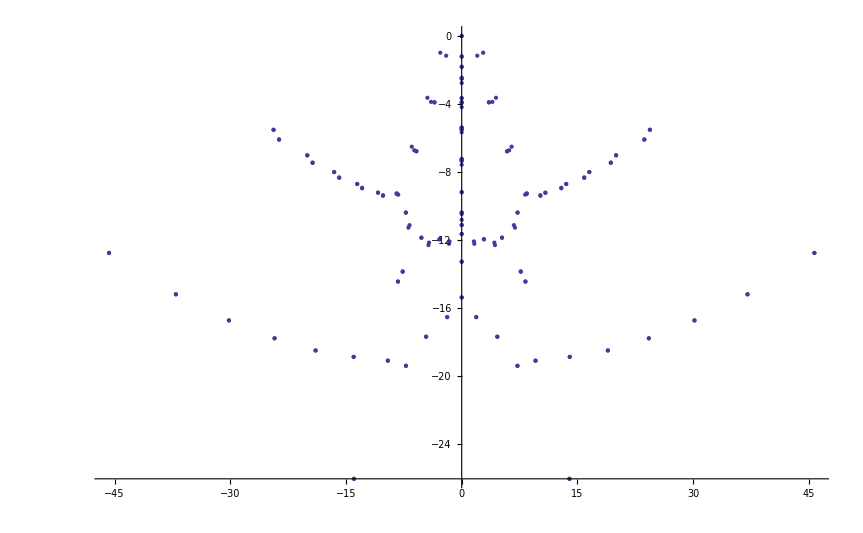

```mathematica
QNMroots[30,9/(5 √3),1/2,30][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

```mathematica
9/(5 √3)//N
```

1.03923

{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{7.7352923187255367×10^-31,-258.23071483847714900850956956497949070973258452798},{-7.7353069875923503×10^-31,-258.23071483847714900850956956497948915451337876409},{-1.2176731271×10^-36,-77.829301096198643683869014723034220027548953970817},{1.36429989684×10^-36,-77.829301096198643683869014723034202801606691877764},{-31.296204595387634247647282797904990021755790427295,15.12089023447026533285867893606354761633597563692},{31.296204595387634247647282797904990021739497005858,15.12089023447026533285867893606354761631963339072},{-31.296204595387634247647282797904991136719908162658,15.12089023447026533285867893606354141692704774113},{31.296204595387634247647282797904991136475037893289,15.1208902344702653328586789360635414166954017036},{-24.39697504553726705552463803663189351948642383721,-5.544416509160205156299503083564506654562548251426},{24.396975045537267055524638036631893519483432424587,-5.544416509160205156299503083564506654561997324322},{24.396975045537267055524638036631893519473114119964,-5.54441650916020515629950308356450665455588261628},{-24.396975045537267055524638036631893519473114098453,-5.544416509160205156299503083564506654555882623733},{-20.017648533199899297409146439747087470833154749625,-7.045003925835551265675683164994033605084502542111},{20.017648533199899297409146439747087470832882844979,-7.04500392583555126567568316499403360508429825922},{-20.017648533199899297409146439747087470821863276753,-7.04500392583555126567568316499403360507836386181},{20.017648533199899297409146439747087470819610557552,-7.04500392583555126567568316499403360507300547622},{-6.416518×10^-42,-19.538170852308107411397416946449004137585517965566},{-7.2383090553×10^-38,-19.538170852308107411397416946449004118139829084044},{-16.539838281138770436577665354302015749383595329908,-8.0299366075899843857915933987474222171215039627},{16.539838281138770436577665354302015749383595329908,-8.0299366075899843857915933987474222171215039627},{-16.539838281138770436577665354302015749371936733329,-8.029936607589984385791593398747422217117103584326},{16.539838281138770436577665354302015749372264489281,-8.029936607589984385791593398747422217115589774902},{8.264005097167615404379167144184716010310030290631,-14.471711902103577625509307608492177459067341497567},{8.26400509716761540437916714418471600998684408405,-14.471711902103577625509307608492177458585301830779},{-8.264005097167615404379167144184716009986844084047,-14.471711902103577625509307608492177458585301830776},{-8.264005097167615404379167144184716009947563614866,-14.471711902103577625509307608492177458574518719785},{-13.54293978711992071750858669265299665618292618297,-8.732584476319238888013361763042447198972795284115},{13.542939787119920717508586692652996656182926144025,-8.732584476319238888013361763042447198972795294297},{13.542939787119920717508586692652996656173409009741,-8.732584476319238888013361763042447198966268839599},{-13.542939787119920717508586692652996656166152268757,-8.73258447631923888801336176304244719892910660642},{-6.851343722012689257868522465925348645788664229192,-13.788643615064237955895635294151233047940649831698},{6.851343722012689257868522465925348646440736376843,-13.788643615064237955895635294151233044267920065923},{6.851343722012689257868522465925342543156871699621,-13.788643615064237955895635294151230306310579226179},{-6.851343722012689257868522465925342543156871144215,-13.788643615064237955895635294151230306310578344941},{10.846132786394856572957122223296636457555833536287,-9.24417742843932875064637498364039477237266222092},{-10.846132786394856572957122223296636457583392587061,-9.244177428439328750646374983640394772301001123453},{10.846132786394856572957122223296636457583392565983,-9.244177428439328750646374983640394772301001123461},{-10.846132786394856572957122223296636457548987568005,-9.244177428439328750646374983640394772302925384935},{12.362767585225618364108427617529056650808234850273,5.048351959277500095738591757813588835808504699833},{-12.362767585225618364108427617529056650807117294386,5.048351959277500095738591757813588835808822192593},{-12.36276758522561836410842761752905568521523050095,5.04835195927750009573859175781358990626492818319},{12.362767585225618364108427617529055685204418067332,5.048351959277500095738591757813589906258353697804},{5.219171139100374622601207974730677987010133670757,-11.887824650097091017773608532095887395836568167209},{-5.219171139100374622601207974730677987010366213832,-11.887824650097091017773608532095887395835057195605},{-5.219171139100374622601207974730677987041260509084,-11.887824650097091017773608532095887395818337860504},{5.219171139100374622601207974730677987041278232135,-11.88782465009709101777360853209588739581830521852},{7.230770525950869485825384089274112066217719045351,-10.410986159074479480493665583241500505707021769865},{-7.23077052595086948582538408927411206621771904535,-10.410986159074479480493665583241500505707021769575},{7.23077052595086948582538408927411206620586464005,-10.410986159074479480493665583241500505714259336674},{-7.230770525950869485825384089274112066190973064589,-10.410986159074479480493665583241500505719661468088},{8.41715697316866101379655611245151490651895298534,-9.3109024467464325675367906304613013270511424318041},{-8.417156973168661013796556112451514906518952985023,-9.3109024467464325675367906304613013270511424314989},{8.41715697316866101379655611245151490651285231368,-9.3109024467464325675367906304613013270482457174713},{-8.417156973168661013796556112451514906516283235403,-9.3109024467464325675367906304613013270394718652956},{2.874602550662233771510984436010243632677839238834,-11.976718728414047778565784135824798525901335245196},{-2.874602550662233771510984436010243632677838732213,-11.976718728414047778565784135824798525901335348164},{2.8746025506622337715109844360102436339020730313,-11.976718728414047778565784135824798525249292296765},{-2.874602550662233771510984436010243633892003928845,-11.976718728414047778565784135824798525250685895182},{0,-11.675071597094735062847245159349293575770221171024},{-9.7×10^-48,-11.675071597094735062847245159349293575710052787035},{-0.152500322880588017124609241337484970437062477496,-11.55664864600805285293588991730633967709615046827},{0.152500322880588017124609241337484970437062487406,-11.556648646008052852935889917306339677096150459026},{-0.152500322880588017124609241337582972915818598579,-11.556648646008052852935889917306070466693195161293},{0.152500322880588017124609241337582972915818544674,-11.556648646008052852935889917306070466693194911133},{3.168199810648517982327305516102971946631069629877,-10.39678884657891798551798693625907006458948920148},{-3.168199810648517982327305516102971946631013098154,-10.396788846578917985517986936259070064589436668017},{3.168199810648517982327305516101730314425894759236,-10.396788846578917985517986936258670198689565152194},{-3.168199810648517982327305516101733505768880472793,-10.396788846578917985517986936258662827695241385459},{0,-10.396253950718234700885223304492733726897832243014},{0,-10.396253950718234700885223304492733726891780775576},{-3.231394862214195727278395480501487667436775443781,-9.5108650450565345914498838269902553446846362631224},{3.231394862214195727278395480501488493121225988613,-9.5108650450565345914498838269902532141304204822742},{-3.231394862214195727278395480500276019409701154649,-9.510865045056534591449883826989384861630032433355},{3.231394862214195727278395480500276019409701154649,-9.510865045056534591449883826989384861630032433355},{5.867572046949826422381014315670426863176046937432,-6.8170530023509999744454206103725287077344143915126},{-5.867572046949826422381014315670426863177143960063,-6.8170530023509999744454206103725287077308129155363},{-5.867572046949826422381014315670426863178164245825,-6.8170530023509999744454206103725287077294653492197},{5.867572046949826422381014315670426863178157564126,-6.8170530023509999744454206103725287077294684477853},{-3.815662941607536054034219371736169768936585169424,-6.9204346193531705387499769211660731359817276347436},{3.81566294160753605403421937173616976893658603397,-6.9204346193531705387499769211660731359817262665231},{3.81566294160753605403421937173594385068386955293,-6.9204346193531705387499769211657803490626552596929},{-3.815662941607536054034219371735943851389469482501,-6.9204346193531705387499769211657803460165395829688},{-7.2844769956361067688330410892820204547565909691258,-1.35461781206250236370092428103766395713428757088},{7.2844769956361067688330410892820204547790484943216,-1.354617812062502363700924281037663956943206399318},{-7.2844769956361067688330410892820186762529685535475,-1.354617812062502363700924281037665342920405760234},{7.2844769956361067688330410892820186762529680115581,-1.35461781206250236370092428103766534292040816418},{0,-7.2503126795681786833162797489818926526946580309866},{0,-7.2503126795681786833162797489818926526942657013924},{4.65405043544730172401670100090983010081617786672,-4.8619854874463681909978389085602077861809488746598},{-4.654050435447301724016701000909830100816176000306,-4.8619854874463681909978389085602077861809430401844},{4.654050435447301724016701000909792977597435354118,-4.8619854874463681909978389085600902344949979165611},{-4.654050435447301724016701000909792977597434512264,-4.8619854874463681909978389085600902344949979393003},{-7.75×10^-47,-5.4040332203841329196899170353833008297041490706152},{0,-5.4040332203841329196899170353833008272378892440534},{3.511290036885756299427798465945922857552210941112,-3.9439133008691956302389264993529844132184246497617},{-3.511290036885756299427798465945922857552210956414,-3.9439133008691956302389264993529844132184245229199},{-3.51129003688575629942779846594592285755262573393,-3.9439133008691956302389264993529844132169612366663},{3.511290036885756299427798465945922857552580841956,-3.9439133008691956302389264993529844132169085052945},{2.529798652109923520388581434747718180912201395932,-3.4511430372586411924806674379350043798433671041787},{-2.529798652109923520388581434747718180912201385537,-3.4511430372586411924806674379350043798433670905651},{-2.529798652109923520388581434747743981782783881158,-3.4511430372586411924806674379349823562317898737241},{2.529798652109923520388581434747743981782762986215,-3.4511430372586411924806674379349823562317416663694},{4.6269×10^-45,-3.9127097471578797354776636784477032609249859346334},{0,-3.9127097471578797354776636784477032584137428945161},{3.22036028×10^-41,-2.5197560574046590219409987571386856033977391590875},{-3.78737189×10^-41,-2.5197560574046590219409987571386856033958786924431},{-2.306×10^-46,-1.22307250288316511529322700404831135575633229186},{1.6114×10^-45,-1.2230725028831651152932270040483113557563303980352},{0,0},{0,0}}

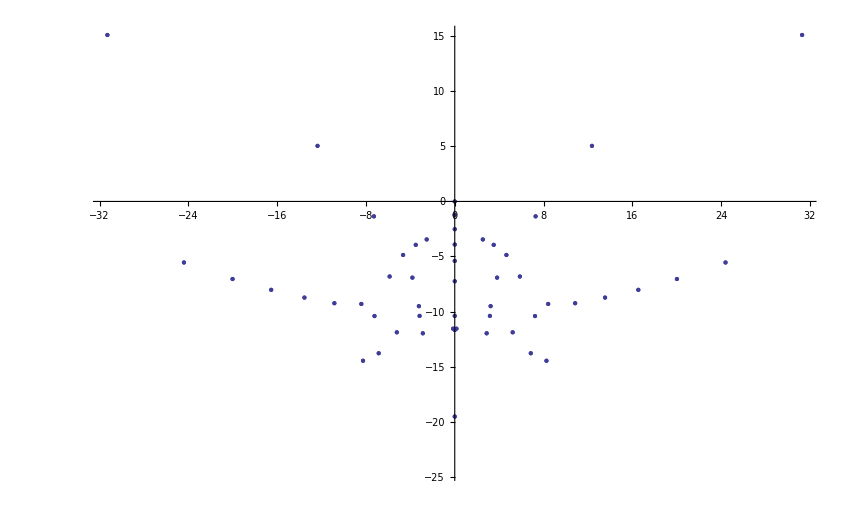

```mathematica
QNMroots[30,9/(5 √3),0,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{-80.889378096228594506695869335342534624239791156875,-19.84457874444748226067300881235504617959114530781},{80.889378096228594506695869303064069148794859359157,-19.84457874444748226067300871146698021520631307914},{-70.404090481624307443563961304590824901965245103529,-23.01396505910408024771766514461684737692306046775},{70.404090481624307443563961276272957790619651075573,-23.01396505910408024771766503587712066168597789872},{-61.990512084026808717506633594474676191984805917964,-25.20345374700982698633349297279109307769387339178},{61.990512084026808717506633570499415903152636688625,-25.20345374700982698633349285561833817347768489688},{-54.691627475949224522274858936271029028766850809252,-26.85459946422434997697118127091432905864643103492},{54.691627475949224522274858916633183090506346752743,-26.85459946422434997697118114394941330823283878022},{-48.133706529944315864515240981850703673788277022807,-28.14152367349530990361023163853001831924914559749},{48.133706529944315864515240965682014250524631659361,-28.14152367349530990361023150025531600738113304045},{-26.43976524785204071102785399877459515851684485297,-47.156662027183848939483202425754395906521555060979},{26.43976524785204071102785387311643860686976104107,-47.156662027183848939483201746814171955108299852269},{-42.115100860617321906969157964834918559851162381588,-29.15504231014113736273957510271311431622486081869},{42.115100860617321906969157950073563252337315808601,-29.15504231014113736273957495220393445296725389613},{-36.504806654073525415298912825320900047184030422648,-29.94669452921909771994345757859365718734613656842},{36.504806654073525415298912808606962287732260625179,-29.94669452921909771994345741615003214384339297402},{-31.208162504973409130347210244153719593880372393698,-30.54257749224043195679725569442836067064488782925},{31.208162504973409130347210220970067377776591965226,-30.54257749224043195679725552166624139708248126668},{-18.71707219547806902175992047623321664934514693031,-38.699383652403421012463426548655679785776390225852},{18.71707219547806902175992016123710958122994999922,-38.699383652403421012463425722740008593276027960906},{-41.987458008201688941801244050957559845849547194152,-8.952392221761922090898887440764830028731339743161},{41.987458008201688941801179194023531771580035258187,-8.95239222176192209089884712338470595488728425349},{-41.27210416039759498653225386222381946346777062545,-9.605864246023156110943446074870080411651447019206},{41.272104160397594986532253847334822359940001771758,-9.605864246023156110943446098929651208873568489331},{-26.15441055048824178922281154065066025604052616737,-30.952725368512770674036853483047888483425026189239},{26.15441055048824178922281150592859209317829111838,-30.952725368512770674036853303884030104461587640553},{-36.722091480749479110940164882796174461385854885147,-10.75042306454922955539429217406877427722051298125},{36.72209148074947911094011879225362563881393429081,-10.75042306454922955539426053608783746307255172651},{-36.024101403837447547103142335340940428730953841959,-11.30145059309602709530571789434798227789899216521},{36.024101403837447547103142315494524193027038197206,-11.30145059309602709530571794029387127529746644865},{-21.28281152686049185373461612185586362790918721696,-31.169016386981817533484527685088452550739489133669},{21.28281152686049185373461606427867753620037687163,-31.169016386981817533484527507717169709389247039045},{-16.61937292139557645046668806082784528456941332205,-31.193178274990825356568381126038253586690318541464},{16.61937292139557645046668799567132723283297809421,-31.193178274990825356568380924909243793247593525222},{-12.92661906183182552674065879873247300117655092404,-32.290080061621119605026668566308642795560041176595},{12.92661906183182552674065837950639668428258711961,-32.290080061621119605026667829407395493734395309679},{-32.495807894699593495526696384505780490284037877916,-12.01001544969786146678252016107180153250592950054},{32.495807894699593495526660663923073094284703306342,-12.01001544969786146678248668527438234074347243261},{31.811983611427518715648887794345224003016966740624,-12.48110136572516115363725210812121730033455369736},{-31.81198361142751871564888780586533104435119292742,-12.48110136572516115363725204501486976588732261969},{-11.37865757650860881642597396165691156719594998829,-30.681050158955978779250145199672103291256908308224},{11.37865757650860881642597357400064804192845859806,-30.681050158955978779250145202942456585590264268613},{-28.826341905293086955924324012317447654955490152309,-12.97478737586921194046053983735247215007760761795},{28.82634190529308695592429339144986884186593414541,-12.97478737586921194046050376951438095252263774663},{28.156042160635204888754105788250374460368511003335,-13.3778534653137248206626141701897567612052927821},{-28.156042160635204888754105789120830781794748102896,-13.37785346531372482066261409567709340572745811279},{-8.115881142955431015608047813872701438411514854283,-29.485708078332822460176025893065948062652911983163},{8.115881142955431015608047476906243258399249762589,-29.485708078332822460176025721681639628398001973804},{-14.61312907808668897449739175043605688564771250167,-25.078957106675225105274588126412930298257021787329},{14.61312907808668897449733606815746674312054145276,-25.07895710667522510527437323231870773711001993099},{-25.526177675119509043841022739625299720188201907045,-13.74038137821586547497742313778057791803633588293},{25.526177675119509043840995533332591840365779765315,-13.74038137821586547497738559904575452761115481185},{-5.472188068059959575808313443038211768237059845433,-28.394789437172454587539379091550555145224878740287},{5.472188068059959575808313092709588118654472016947,-28.394789437172454587539378963321592868968837452315},{24.869377436019278043992071354710387842697961201697,-14.08337228663342228335331619623296049353722372118},{-24.869377436019278043992071345706773106140801055981,-14.08337228663342228335331611171268672636099088007},{-13.95644567332971030218663747007202419892227069411,-24.445790269871632282065007544975658342887926641824},{13.95644567332971030218663810292489279216726373384,-24.445790269871632282065007076129798548439893514416},{-2.944722580067600823834863117418497421901350138943,-27.062025414157489629268070248493128520238042140299},{2.944722580067600823834862831705189814130037620592,-27.062025414157489629268070140640208791601875046599},{-22.495000628059107688356642597060794202556343653835,-14.3562667219347031606809942936211272965892551982},{22.495000628059107688356618740525070460397184285001,-14.35626672193470316068095595782693564112195424033},{21.851585361418872013618987903806277481149610127205,-14.64526206005146576360195513092658233122167621255},{-21.851585361418872013618987885048377032612434298789,-14.64526206005146576360195503546288558205069569493},{-0.457976128639411110298649222839617226750687108124,-25.524602452623203346446753266736860378670772731097},{0.457976128639411110298649054911510344126953145428,-25.524602452623203346446753027687906251891219004455},{-19.668736366233871549677420167527569507975247806974,-14.85061519674298822244506734046014060707094712635},{19.668736366233871549677399894770151166824547513125,-14.85061519674298822244502830956335192758437570044},{19.037987202473040465376390991859255411051488214063,-15.09051095673203110939759184341976427324874440594},{-19.037987202473040465376390962739693841473357771775,-15.09051095673203110939759173597752101914583329531},{-10.60113519614492989350369765383158404255434777184,-20.75812865594609005274064801361883253396503228065},{10.6011351961449298935036269277371314363250527595,-20.758128655946090052740402347402933366503369500657},{-17.003373737899736970610231184000346929733247754792,-15.23912725745154804538361535687653631968591177079},{17.003373737899736970610214509011710662878127986362,-15.23912725745154804538357550258670932333219769847},{-8.49165091781661906127×10^-28,-22.756748077763409608058852386660042994620849099076},{-10.02158926134918105971087170955070123422872088424,-20.285640892864626406343260051734025375057622583244},{10.02158926134918105971087223803354597446580483995,-20.285640892864626406343259275293202863187260653483},{16.3868600348880092426153652037779295038601522126,-15.43711391231329628008349480939820790750742726677},{-16.386860034888009242615365162283410533113136776351,-15.43711391231329628008349469043034286387652354187},{10.92924046876247571234167779730122552079312388997,-18.202251573381004150816844189574725015566499385681},{-10.92924046876247571234167761877154571914136648267,-18.202251573381004150816844069657000333246655957998},{-14.41587505713100552048675370087917041540803282011,-15.565508219629080096969545781610266795309632133359},{14.41587505713100552048673883420488257353536515926,-15.565508219629080096969500227218177258848869054288},{-7.627619356096562309554314505826680203240938507251,-19.662005230233313692831968409218234067989116094226},{7.627619356096562309554314271162517424069483469416,-19.66200523023331369283196798947731006941239094986},{-8.698943514285536727951185999522690500877544378964,-19.132629416500749030660371084949909686494840386979},{8.698943514285536727951047948073833491614871477137,-19.132629416500749030660307797805759502235180052323},{13.5132777576100001021989052278360028836321049159,-15.77901394974561449128249762345471926025456094549},{-13.51327775761000010219890510180083898155726397706,-15.77901394974561449128249733961809809099868549438},{-11.31757643249233507670483272326261454530451534782,-17.374935226231028908278616737501426416481695910342},{11.31757643249233507670478134219105860679025341809,-17.374935226231028908278585551916730855190951592773},{-7.8479481541801434412×10^-29,-20.52374665182446120143596959440655842336833568154},{-6.088404604451608963889603596968875463833814093485,-19.482743384538565068994078740501373867779333249254},{6.088404604451608963889413092885583516169339272243,-19.482743384538565068993983990738659286124677067262},{-4.890433327329509925776911969976352047284110338967,-19.72932165136929892990072153695115024748551846436},{4.890433327329509925776911606787994270076501616601,-19.729321651369298929900721114511051460954783331766},{-13.00341181867633348541697771965432911321572696855,-15.429342825400969616390665663696643642399773324899},{13.00341181867633348541697773251992774747811660708,-15.42934282540096961639066551493150795627725314655},{-12.65648634233918159134712486355825761718824852973,-15.21929821131913608890108823419136751161743161723},{12.65648634233918159134711259395440984218725660755,-15.219298211319136088901080675351358446923011187162},{-3.43788240546209659035306653049494074803650067343,-19.310187170915171933241199818367094582017810672949},{3.437882405462096590352852902454176274567597905021,-19.310187170915171933241114713195865498052956607476},{-2.190660754880821097572581354480973506172917280931,-19.39726669407358612427655221769928037028334441824},{2.190660754880821097572580843929531533768240147347,-19.397266694073586124276551896979449755375947100708},{-2.32146475092499095554018×10^-25,-18.886332782227559197989903834868999591446958653484},{-0.926583683172905757719035615592480230882916396079,-18.753492052638827029174325877058970797894256733711},{0.926583683172905757718843259242786530834180723012,-18.753492052638827029174251535715296372456234663199},{4.15261213781805531612×10^-28,-18.483813221039643649209910963633433814177883009385},{-3.147195383121659462×10^-30,-16.575712523440230508102915581560376920102894076761},{-10.74414043730813363382092001395236144823403679788,-12.363953491514520039879064747024830455582677940225},{10.74414043730813363382092001393265114582928474845,-12.363953491514520039879064747018182501981094362379},{-10.49583206683986659636452709194380685158424473505,-12.485077167173362055890436572865759820795932897308},{10.49583206683986659636452708489499951642424974567,-12.485077167173362055890436575590138711171419512373},{-1.3102150218528210044195×10^-26,-15.138656121159521452953166684884746576372779285875},{-3.080937130405375621591533×10^-24,-14.88995166964195197793810159437818701773603935741},{2.1988648541617592448×10^-29,-14.721772560889393290820971393331216560190210223899},{1.4820442091577897×10^-32,-12.880115498427586272053239301690248019349944229132},{-8.498485803145476665722517006235655384014598937644,-9.5195808367029325787913580075100269536085915050222},{8.498485803145476665722517006235652433015534201492,-9.5195808367029325787913580075100266856055773364171},{-8.187609194096101794413504002583636335220709841235,-9.6560655552348170940969482002998717122630132339101},{8.187609194096101794413504002582747949314017078581,-9.6560655552348170940969482003000447036390940441512},{-6.781530716988096489734×10^-27,-12.168464817031113362039831637236323196675618552437},{-1.337774694529327410269213×10^-24,-11.996386443110441078600142657316115352427926867905},{3.0193150705844998×10^-32,-11.04000557395179307874605287564312314177170687877},{-2.087251747391476151963×10^-27,-10.113005302682730494426082799960881826103861137817},{-1.144413634446427982104637×10^-24,-9.979898731587200549648315005289777817905484560785},{7.7389950310225918×10^-33,-9.200000197365805590985210122270601076531429692386},{6.288568717642335196996574145402124777747880980979,-6.6644531097859989499118037119076264795052815140808},{-6.288568717642335196996574145402124775698632869565,-6.6644531097859989499118037119076264779807552241456},{5.867498041169608418633558141472779774194968785115,-6.8171385018357544019144810810602197570847453814503},{-5.867498041169608418633558141472779419680195827176,-6.817138501835754401914481081060218989556577321509},{9.76821968940629028902×10^-29,-8.5060041824793123388954844694010679004577357888868},{-2.884866446594619003329497×10^-24,-8.379557044585603723838765879398630467632861879103},{-1.4733929645462387356×10^-29,-7.3599999969636944787606530417024285566839203172478},{-5.8626327700377395555×10^-30,-7.0070972135075434547745600718498799462077816813564},{-6.638426768070057579129701×10^-25,-6.872335151806798991493334372854151498772463737991},{4.1755036936820959344033265638411491528413823539553,-3.801099613129451950151248903592831989217238085669},{-4.1755036936820959344033265638411491499118708116372,-3.801099613129451950151248903592831987022071252704},{-3.08227232732814026075×10^-28,-5.5236098781934931434646202514294991046709275887583},{6.19970497901396×10^-34,-5.5200000062054978056835609361763155488952003619055},{-9.8885757299238480646987×10^-27,-5.3787893374118437189841417452017421618531685397049},{3.511290111888700492797663440695843533607196217001,-3.9439133792291562965080980015800039787224275697735},{-3.511290111888700492797663440695837932105760411257,-3.943913379229156296508098001580001396663437407788},{1.7137207154038139×10^-32,-4.0558483789140261494825224467057019766613881933789},{-3.49999679862177671838×10^-29,-3.9124320919775002321930484121544633535478549069303},{-1.4349287767345×10^-35,-3.6800000000000477994420007165755141426345398589909},{2.3823751187242341217166734013555966821393877376891,-1.093159114795900121856234698453521164798228611128},{-2.3823751187242341217166734013555966821392311077638,-1.093159114795900121856234698453521164797831684018},{-9.317511111468756×10^-34,-2.617608070182248204391616977495991710891464630739},{4.810115830728692874×10^-31,-2.519755702131604286730783833341436479263091768765},{-1.393771×10^-43,-1.8399999999999999933288601350913933651868432860403},{-2.069925268077547×10^-34,-1.223072502868802237063303824483819695432266764995},{1.42254345815402502403524594615061075040470921976×10^-43,-1.8083400061448593907393397969830827669459123147668×10^-41}}

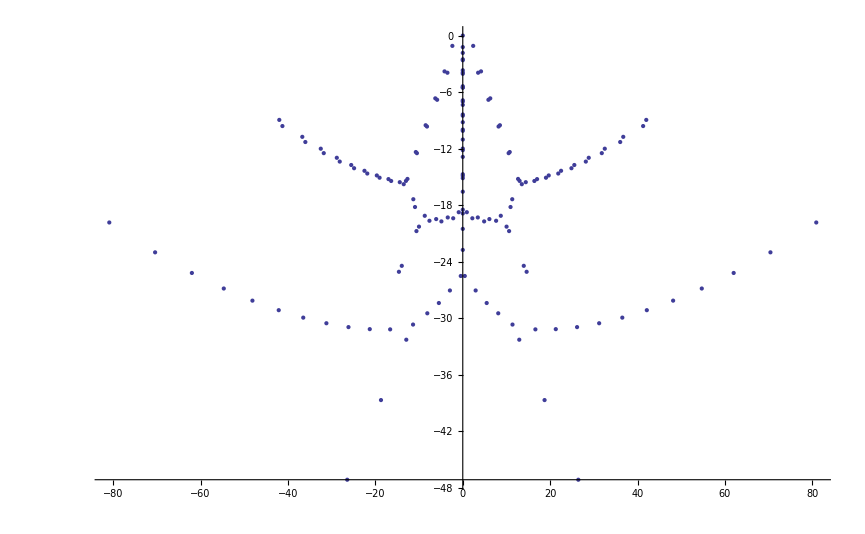

```mathematica
QNMroots[50,9/(5 √3),0,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

```mathematica
Solve[x^2 + 4 x + 4==0, x]
```

{{x→-2},{x→-2}}

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((two/.{XZsub[MM],VXsub[MM],AAsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,16][[1,1]];
%/.Ω->-QNMroots[20,0,0,16][[2,1]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(-1.3232130998138×10^-16+1.829508274405×10^-17 ⅈ
-1.3098474446658×10^-16+4.205351131383×10^-17 ⅈ
-1.112502351476×10^-16+1.036960662192×10^-16 ⅈ
-3.923616420115×10^-17+1.545175481468×10^-16 ⅈ
7.946446619879×10^-17+9.739808062759×10^-17 ⅈ
1.276186245707×10^-16-9.00712657403×10^-17 ⅈ
-1.49877899068×10^-17-1.718238368865×10^-16 ⅈ
-1.556553716024×10^-16+6.97313674339×10^-17 ⅈ
2.55822431319×10^-17+2.105157178592×10^-16 ⅈ
1.801432640323×10^-16-1.44216312678×10^-16 ⅈ
-1.21128659509×10^-16-1.79941550232×10^-16 ⅈ
-1.26175367317×10^-16+2.83984126061×10^-16 ⅈ
2.34580754313×10^-16-2.3936633275×10^-17 ⅈ
-7.7322925656×10^-17-2.89265144376×10^-16 ⅈ
-1.56812481473×10^-16+3.15873183689×10^-16 ⅈ
2.25260920454×10^-16-3.5480996069×10^-17 ⅈ
-9.3570613175×10^-17-2.88142840029×10^-16 ⅈ
-7.3951755472×10^-17+3.82078723322×10^-16 ⅈ
1.2302816613×10^-16-1.9320448108×10^-16 ⅈ
-6.333476609×10^-17-9.443233751×10^-17 ⅈ
-6.1173611983×10^-17+7.98145526563×10^-16 ⅈ)

```mathematica
cofMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((one/.{XZsub[MM],VXsub[MM],AAsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub
cofMatrix[20,16].QNMroots[20,0,0,16][[1,1]];
%/.Ω->-QNMroots[20,0,0,16][[2,1]]/.{Q->0, θ->0}//MatrixForm//Simplify
```

(1.3231361125231×10^-16-1.8303673244445×10^-17 ⅈ
1.2899668775422×10^-16-1.7865745340926×10^-17 ⅈ
1.0395822439826×10^-16-1.445118163098×10^-17 ⅈ
2.69839035771×10^-17-3.813720329395×10^-18 ⅈ
-8.8328542656159×10^-17+1.226539684948×10^-17 ⅈ
-1.217807196399×10^-16+1.705633729678×10^-17 ⅈ
2.909059480427×10^-17-4.01311218042×10^-18 ⅈ
1.526140782687×10^-16-2.149591887677×10^-17 ⅈ
-4.331117488576×10^-17+6.03800234377×10^-18 ⅈ
-1.762255015383×10^-16+2.498760501683×10^-17 ⅈ
1.4582399574×10^-16-2.06389190388×10^-17 ⅈ
1.18401727357×10^-16-1.69217072972×10^-17 ⅈ
-2.881631166721×10^-16+4.10864003138×10^-17 ⅈ
1.39908836246×10^-16-1.99142565549×10^-17 ⅈ
2.22100477541×10^-16-3.18440021248×10^-17 ⅈ
-4.79488780772×10^-16+6.86965003707×10^-17 ⅈ
3.53867884495×10^-16-5.06916104731×10^-17 ⅈ
2.24606780774×10^-16-3.2311451712×10^-17 ⅈ
-1.1595025541×10^-15+1.6656231929×10^-16 ⅈ
2.9247672844×10^-15-4.2018468181×10^-16 ⅈ
7.19418340426×10^-15-1.03385699193×10^-15 ⅈ)

```mathematica
bigMatrix[MM_, prec_]:=Transpose[Join[xzMatrix[MM,prec], vxMatrix[MM,prec], aaMatrix[MM,prec]]]
QNM[MM_,prec_, qq_, kk_]:=Solve[0==Block[{Q=qq, θ=kk}, Det[bigMatrix[MM, prec]]], Ω]
```

```mathematica
QNMroots[40,0,0,50][[2]];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

$Aborted

Transpose::nmtx: The first two levels of the one-dimensional list {Re[$Aborted], Im[$Aborted]} cannot be transposed.

Transpose[{Re[$Aborted],Im[$Aborted]}]

ListPlot::lpn: Transpose[{Re[$Aborted], Im[$Aborted]}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Re[$Aborted],Im[$Aborted]}]]

{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{2.0000000000006,-1.9999999999988},{-1.9999999999998,-1.9999999999997},{-4.,-4.},{4.0000000000857,-3.9999999999381},{-5.9999999999551,-6.0000000000098},{5.999999999846,-6.0000000002367},{-0.26773961121947,-8.5560915984091},{-0.19822594596139,-9.8728608477848},{8.0000000170264,-7.9999999886799},{-8.0000000168164,-7.9999999890794},{9.9514898356104,-9.8351244476547},{-10.000071799608,-10.000131697275},{10.00007204565,-10.000131787102},{-11.701256340022,-11.955502437889},{11.701305837498,-11.955790524462},{10.715565531823,-13.706732716225},{-10.715555872768,-13.708126521955},{-12.995381100904,-11.671238258401},{12.997518275939,-11.671915898559},{-9.141873029982,-15.622086767627},{9.1474506710789,-15.625337608692},{14.941914624806,-11.127811727775},{-14.957254194622,-11.129947252693},{6.7867685070568,-17.481144783501},{-6.8166412128349,-17.51733785943},{-3.6037823026744,-18.712392842488},{0.1046253114036,-19.145300538874},{3.5445939705775,-18.843236842713},{-16.793678106651,-10.842992458002},{16.845209382028,-10.85586070888},{-21.499034046267,0.88862730801658},{9.2409458272746,-19.557050364588},{-9.2409458272746,-19.557050364588},{19.495738556674,-11.034437929338},{-19.58621921114,-11.15163325151},{-22.427014463536,-9.9426901281582},{22.823489136628,-9.836800065023},{-21.434846757973,14.459238722274},{21.702494498121,14.999536057601},{-14.738653221757,22.265626341815},{15.226307893484,22.12377745372},{26.305882604253,5.9643847379264},{-26.730583404899,5.4375515704911},{5.9855751322174,27.469187584071},{-5.8482191027101,27.570909610896},{25.930845122369,-12.113633425164},{18.993389671618,-21.952752831331},{-15.134311221941,-26.025405415916},{9.7622413263822,-29.27692969942},{0,-31.283841932103},{-4.5560741808856,-31.608932464719},{-25.166302665874,-22.471155650307},{-28.297410211091,-19.341009574823},{36.3152219616,-10.601176867255},{0.0070354546966584,43.102401600351},{0,-44.868508496135},{-0.0202549560612,54.692243081425},{0,-58.493445357751},{0.46359122694944,-58.971752063594},{139.07646994249,265.22727573363},{-139.00647350953,273.56872660622},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

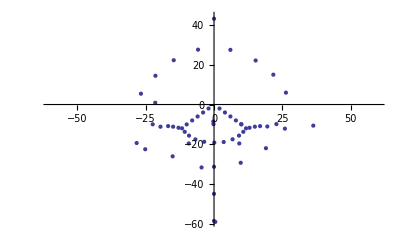

```mathematica
QNMroots[40,0,0,20];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{0,0},{2.,-2.00000000000000000000001},{-2.,-2.00000000000000000000001},{3.11945159116590141025656,-2.74667574434060639904851},{-3.11945159116591199776311,-2.74667574434060044096191},{3.99999999999999999146361,-3.99999999999999999835787},{-3.99999999999999999146373,-3.99999999999999999835792},{-2.75364925371169883465208,-5.4564725778726768814724},{5.16952097576210589434467,-4.76357011692093363199665},{-5.16952097581194652152387,-4.76357011687996369543613},{-6.00000000000015097237349,-5.99999999999927975481449},{6.0000000000001509723737,-5.99999999999927975481443},{-7.18793086459300495715872,-6.76956479807878535682873},{7.18793081499075547128272,-6.76956490672488023298977},{8.00000001455615416405737,-8.00000000435795637816529},{-8.00000001455615416405736,-8.00000000435795637816529},{-9.19715533608910089786472,-8.77221169867869140404963},{9.19722295761422876521686,-8.77239248859572572754784},{-9.99995719385547169849531,-10.0001047708336843476994},{9.99995719385547169849531,-10.0001047708336843476994},{11.4665875334820484319005,-10.5898528173298229315517},{10.8347521235680467740036,-11.3615243925237389531965},{-11.3686807620649363440952,-10.8757091628381466576668},{1.17350245501116283084414,-15.7229721861387085336852},{-1.17350217115189265851023,-15.7229723182647286855938},{-11.0124135702195573026449,-11.356458992011042740237},{-3.49978510774728494197287,-15.4936176279981669879415},{3.49979477984683372111731,-15.4936254345241409412432},{-5.76402408069362058133349,-15.0505631150080033353511},{5.76395203541354812413335,-15.0508372893251120476947},{9.53733199703945324387264,-13.1856452010564393814516},{-9.55210938235073867127316,-13.1913883423464376046256},{-12.8278244775214083629453,-10.2126069217451681528881},{7.86733373955378580245035,-14.3959782100841043664876},{-7.8707103192484398646281,-14.3953956307723927850018},{11.8275390517459552094709,-11.8734367394864470955163},{-11.8275390517459660326859,-11.8734367394865285142432},{13.5044361495998339563958,-10.2782739930907946773747},{-15.055382534687565353399,-8.73981287745715442639948},{-10.9984153081878068129967,-13.5338635143719630112815},{10.9984153081874674039315,-13.533863514372264339512},{13.33725552636397758775,-11.7373847862482710102858},{-13.3372555263639762426524,-11.7373847862482858130445},{2.07319351017203391710406×10^-16,-17.7694787186676758753096},{2.40400463776213749293991,-17.6412911717834660967779},{-2.40400463776213530545969,-17.6412911717834673126679},{4.75734439287627174276913,-17.2658152431288516499937},{-4.75734439287626836367293,-17.2658152431288565992758},{7.03363739612486010674622,-16.6572416535028240643656},{-7.03363739612512965618104,-16.657241653503343733882},{-9.46815511144563416844062,-15.4478059862258889801997},{9.46815511144597158105313,-15.4478059862258589347816},{15.5608861947632863270152,-9.70243675751157441966755},{-15.3978264663606578265661,-11.1978552942982455361442},{15.3978264663611753423031,-11.1978552942982552087491},{-17.8028432897420494562664,-7.08325147389668585267323},{-9.62594356095384464410963,-16.7620853236213702556269},{9.62594356095510824920941,-16.7620853236231184194228},{-10.6611267769723902458947,-16.3001463772701154519395},{10.665015974907935750626,-16.3132634745310851219737},{17.7477990562853687856879,-9.05628177743360913193154},{-17.5670317718838461727813,-10.5962664237311172251541},{17.5670317718569637507757,-10.5962664238384493835111},{-21.1453182528860876411715,-5.02623761179664938378051},{20.0971977848674002551032,-8.31774408055978150067888},{-19.9027126958772815829517,-9.90328256421197591171748},{19.9027128964521967677212,-9.90328266828173483137634},{-18.8699322314577131535251,-13.6095078111890138458657},{22.6523915196352684032909,-7.45964167418682618183803},{-22.4406484470245521632145,-9.08528949105098075659551},{22.4407094156735100999089,-9.08522934158708696963628},{-25.5522834114926963631336,-2.605614434943778321021},{25.481483925372489785742,-6.43772522743763437071736},{25.2033224324531386972587,-8.14534382257036785866864},{-25.2079454459181249770011,-8.14258939205814305379707},{28.7129597976938776589545,-5.1674067645884750636908},{-28.519701050696597017852,-7.24334454170860646778583},{28.5895517329967787539789,-7.11496007554207250533493},{32.681043534926624849697,-3.4279059995494356178659},{-29.2323232243968782008066,-21.8928053853271931108283},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

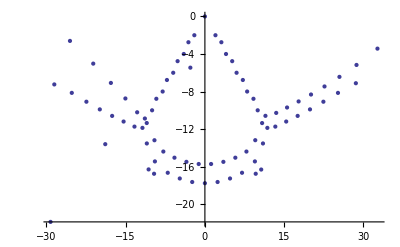

```mathematica
QNMroots[40,0,0,30];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{1.999999999999999999999999219499211469544687162811716228013671519463396326535815247477571936112,-2.000000000000000000000009482357079444414686570135051120614519052041580158410563094296602639153},{-1.999999999999999999999999219499211469544687162811716228013671519463396326535815247477571936112,-2.000000000000000000000009482357079444414686570135051120614519052041580158410563094296602639153},{-3.119451591165901410307019268712711105493081528453232182386258369393795717893634640841179351487,-2.746675744340606399195139850331807106675753220831541047145053919881201643935630374678420603631},{3.119451591165901410307019268712711105493081528453232182386258369393795717893634640841179319003,-2.746675744340606399195139850331807106675753220831541047145053919881201643935630374678420700868},{3.999999999999999991463604999349444593375200650469208894901631355015194936114324298735281865925,-3.999999999999999998357853232878781740090850648589613803200969594216530811836469322084920520429},{-3.999999999999999991463604999349444593375200650469208894901631355015194936114324298735281865925,-3.999999999999999998357853232878781740090850648589613803200969594216530811836469322084920520429},{5.169520975762106155474411511879271514116776850603660540181860768975580587012032658235155974993,-4.763570116920933683564144364775416933547395903138168737292707962154753392797882149131937612504},{-5.169520975762106155474411511879271514116776850603660540181860768975580587012032658235155974993,-4.763570116920933683564144364775416933547395903138168737292707962154753392797882149131937612504},{-6.000000000000150972373725143591340465442895998706255313941806236045310721889569649028770530631,-5.999999999999279754814438226235198369365499089167772628862937818625136921597485531660235337195},{6.000000000000150972373725143591340465442895998706255313941806236045310721889569649028770530631,-5.999999999999279754814438226235198369365499089167772628862937818625136921597485531660235337195},{7.187930814990081867281810334186124059839954096224359358510324012762147837527354972174673402184,-6.7695649067310985347811967109028096802413793710516370597670779304009229097118429084818695374},{-7.187930814990081867281810334186124059839954096224359358510324012762147837527354972174673594424,-6.769564906731098534781196710902809680241379371051637059767077930400922909711842908481869499812},{8.000000014556154176847813309179682570352738578896543374310214565702261428703097638650619761643,-8.000000004357956382053558278102829694073675302176368836031200415394929532245493399898601574396},{-8.000000014556154176847813309179682570352738578896543374310214565702261428703097638650619761643,-8.000000004357956382053558278102829694073675302176368836031200415394929532245493399898601574396},{-9.197222905195154985088756748294967168936020558275135362436818223138174166902684366906853633039,-8.772392482490069197861411184031321042154231321523386792414525704660778947475317316091518544574},{9.197222905195154985088756748294967168936020558275135362436818223138174166902684366906853633039,-8.772392482490069197861411184031321042154231321523386792414525704660778947475317316091518544574},{9.999957193853585784962270450916130817020148388922790650834033406823347081208750923428096533171,-10.00010477082987522932661113112896690399585445330129569873584175166836939040624568575690835035},{-9.999957193853585784962270450916130817020148388922790650834033406823347081208750923428096533171,-10.00010477082987522932661113112896690399585445330129569873584175166836939040624568575690835035},{-11.46645125796176693533243004650914759121951534570048409093946616848964063277722132609112698255,-10.58984690161487553396433390939518667920893985107354048062092446818908217616060347326643700946},{11.46645125796176693533243004650914759121951534570048409093946616848964063277722132609112698255,-10.58984690161487553396433390939518667920893985107354048062092446818908217616060347326643700946},{-10.83470315441938664439962600106208564473853176030756995642399934764600002374374984110081413225,-11.36174372874332620689497302323908174200555017739358898955598900894372732523557416516047674154},{10.83470315441938664439962600106208564473853176030756995642399934764600002374374984110081413225,-11.36174372874332620689497302323908174200555017739358898955598900894372732523557416516047674154},{1.173436103760693922154127252431896996607476276101682494137822534150519002598455346814431551057,-15.72406933699247162731610223231056707809502539440634192303232288221228892695866260674527148002},{-1.173436103760693922154127252431896996607476276101682494137822534150519002598455346814431550526,-15.72406933699247162731610223231056707809502539440634192303232288221228892695866260674527148009},{3.499598324959684536723108546641343226575953506013269849799522166868367290859230238098663111742,-15.49469087450706494861596279490094308332997654034913283487768796094843901601889917010903160084},{-3.499598324959684536723108546641343226575953506013269849799522166868367290859230238098602291668,-15.4946908745070649486159627949009430833299765403491328348776879609484390160188991701090546467},{-5.763627017890297023834394434723054101705538164069186528118774712818024835523143068640929790926,-15.05183968497205934965937100552362828410636499671396197231290796687965262950913867497317840076},{5.76362701789029702383439443472305410170553816406918652811877471281802483552314306864091663702,-15.05183968497205934965937100552362828410636499671396197231290796687965262950913867497326312064},{9.537108912033280821768160820187835335415571276136145355537059249308817001074459213436533946286,-13.18593428040231845537391882567824653890271832838740187408736920583251317095905253938865417676},{-9.537108912033280821768160820187835335415571276136145355537059249308817001074459213436533946286,-13.18593428040231845537391882567824653890271832838740187408736920583251317095905253938865417676},{7.866897191378862058822900471848052556825314944279114003712001057143343515394017063620567211898,-14.39675566039355285703053727354302151961126689054809162774158394565623128959770637150495551865},{-7.866897191378862058822900471848052556825314944279114003712001057143343515394017063620567211898,-14.39675566039355285703053727354302151961126689054809162774158394565623128959770637150495551865},{11.82753904391046369313822878350203074766163030919230114197320205601013051545265000554869892797,-11.8734369062259101671833791503986313067656631622910244421946349253452995653689995997359242808},{-11.82753904391046369313822878350203074766163030919230114197320205601013051545265000554870047057,-11.87343690622591016718337915039863130676566316229102444219463492534529956536899959973592414516},{13.50427057330123248694277011480939077891782818071405467745162320787935901113175874103950941898,-10.27837071185783988192129682223685797030131802766118532843725067313135602434766216559640327264},{-13.50427057330123248694277011480939077891782818071405467745162320787935901113175874103950941898,-10.27837071185783988192129682223685797030131802766118532843725067313135602434766216559640327264},{-10.99841497493486895635519485619999148559282448247903154508281774507814738849487344420338985021,-13.53386327399238802334051341261051309272580687035437304434509051992679070127632994497028624657},{10.99841497493486895635519485619999148559282448247903154508281774507814738849487344420339079884,-13.53386327399238802334051341261051309272580687035437304434509051992679070127632994497028632967},{13.33725629876254294776585980526969409692561472232450909680300791150882296938723222493563515284,-11.73738722717944613462025566162428043095858885750853846197550544593968825190260716994389814851},{-13.3372562987625429477658598052696940969256147223245090968030079115088229693872322249356351253,-11.7373872271794461346202556616242804309585888575085384619755054459396882519026071699438983153},{-4.048427262746433627222974934249875142184984807645608110053238186316326906850987691466065499393×10^-95,-17.76943232341656209383535002185347955229655425916972664020034829334679015679546815839697429912},{2.403987699282312122466159164429463249884721835488513200081681808146437365709896553820603938491,-17.6413310522220585182180564863628196402248978569105584481139705040472371663971882420873250543},{-2.403987699282312122466159164429463249884721835488513200081681808146437365709896553821115086986,-17.64133105222205851821805648636281964022489785691055844811397050404723716639718824208776035202},{4.757369750578252227234542849058653835187185741947247159985439919451285875793535208279175260484,-17.26579056030163275536092079367904898191060395570641567901427652010898076622778295892706993457},{-4.757369750578252227234542849058653835187185741947247159985439919451285875793535208278713730901,-17.26579056030163275536092079367904898191060395570641567901427652010898076622778295892725485061},{7.033614732440777614032188106693053872493017229975255984655632609073015683729990684746424524895,-16.65725300033562087664146596909320714224382884104396404384001145620171790778658232456589471078},{-7.033614732440777614032188106693053872493017229975255984655632609073015683729990684746424832421,-16.6572530003356208766414659690932071422438288410439640438400114562017179077865823245658988695},{9.468153173161170902090408745171753926948328603648702733863485559222587234585747371385822514332,-15.4478017923206405056478823765586201818168022445448080791357302854687396312317320532109343166},{-9.468153173161170902090408745171753926948328603648702733863485559222587234585747371385822359361,-15.44780179232064050564788237655862018181680224454480807913573028546873963123173205321093449783},{-15.56072438770520024240747943186069047529581851773705959472441462972912489823291240771349606941,-9.702545504580966877789669375146864677290615999096059261676903202560929206714529933290381047293},{15.56072438770520024240747943186069047529581851773705959472441462972912489823291240771349607626,-9.702545504580966877789669375146864677290615999096059261676903202560929206714529933290381046801},{-15.39784678265369274375461017626584730522021973258417055209930624324094045362282766173493828535,-11.1978467940674590091562748719654731519740768366631406043889638590543362503057446923949828408},{15.39784678265369274375461017626584730522021973258417055209930624324094045362282766173489955001,-11.19784679406745900915627487196547315197407683666314060438896385905433625030574469239504789728},{9.626034442858599343797875870056357839777736895947224798375988799858982014532262215624268296289,-16.76215940539308297928149384677833265739022352554079023935469592500662331398702236066547644516},{-9.626034442858599343797875870056357839777736895947224798375988799858982014532262215624267985908,-16.762159405393082979281493846778332657390223525540790239354695925006623313987022360665477568},{-10.66358796848178467559224651078855516365083570044119559289271354494817043651950217421470978858,-16.31320495277743800092785263940003463936897549247296070517094731220773861488590028050713932464},{10.66358796848178467559224651078855516365083570044119559289271354494817043651950217421494027779,-16.31320495277743800092785263940003463936897549247296070517094731220773861488590028053128876175},{17.74764216830884783275809904682446030301548144229695720836658843011023359664182270751151867305,-9.056403967436020120113813915710716177129083743276184370001069422059573186195308874401965936694},{-17.74764216830884783275809904682446030301548144229695720836658843011023359664182270751151867305,-9.056403967436020120113813915710716177129083743276184370001069422059573186195308874401965936694},{17.56696038256327092199843421597292625392561597886916065967408014122926374691258031214126936053,-10.59610582566498235228013322449528396233124844732636109824796997586560601396644305532880828726},{-17.56696038256327092199843421597292625392561597886916065967408014122926374691258031214131413023,-10.59610582566498235228013322449528396233124844732636109824796997586560601396644305532881150343},{-20.0970472287061747965076093379934469134210795128806207041292680593271378539823639728899725491,-8.317878865381539155047430145921869975730264534695155811327217827225887325709930651501107908616},{20.0970472287061747965076093379934469134210795128806207041292680593271378539823639728899725491,-8.317878865381539155047430145921869975730264534695155811327217827225887325709930651501107908616},{-19.90152246204786158148690437060070589310869156263928707990690849072239888527172603549564155645,-9.903788350127376053963946381095412201930819275048733258682135286813063454926003726582123392107},{19.90152246204786158148690437060070589310869156263928707990690849072239888527172603606322621693,-9.903788350127376053963946381095412201930819275048733258682135286813063454926003726422717922611},{-22.65224814330473327339532458025302998427348254995548043908205922370189737042756902295478565523,-7.459788327362278002578096131391430348334927678089478065974713567786055121235978567105420909709},{22.65224814330473327339532458025302998427348254995548043908205922370189737042756902497120480296,-7.459788327362278002578096131391430348334927678089478065974713567786055121235978564742532002466},{22.44388802340341040757843812039953596259929769763955681306432460834009198652609689793246420219,-9.093683729693639668411707059812624520147228657052631941202610146296225671699410759176526421741},{-22.44388802340341040757843812039953596259929769763955681306432460834009198652609691318624969447,-9.093683729693639668411707059812624520147228657052631941202610146296225671699410757275130337095},{-25.48134829362469080559048708646666481520311812408024157279599596420948521599661710962114022785,-6.43788355735544854051545232478366814283268002261949654287115727040842222031100084037491923268},{25.48134829362469080559048708646666481520311812408024157279599596420948521599661726483253403122,-6.437883557355448540515452324783668142832680022619496542871157270408422220311000671472336434042},{-25.26169031442256021285317375907481673093538529541409273224817483328400083387430820253841320531,-8.122722161419285602523434801815689147550779369385842563137748972585060674143225200998493831038},{25.26169031442256021285317375907481673093538529541409273224817483328400083387430820253943459167,-8.122722161419285602523434801815689147550779369385842563137748972585060674143225201002607808437},{-28.7128324270425729849346612381788735500358381127856220649956028802338133075898219800712164964,-5.167577548085809607569388572194840415269729551298334419865048822345110394655307046575396028952},{28.71283242704257298493466123817887355003583811278562206499560288023381330758986791037629283659,-5.16757754808580960756938857219484041526972955129833441986504882234511039465524521082835182583},{28.48298129632224920738849853038604445997597987149251269883332171946855210061092351317554063493,-6.908983562200674898997179800843507748632232838975276331610009669609880186015807604910163817624},{-28.48298129632224920738849853038604445997597987149251269883332171946855210061092351317554063492,-6.908983562200674898997179800843507748632232838975276331610009669609880186015807604910163818029},{-32.68091445409094389633431655328427803227045469784287170574808299879329968906552401967790909799,-3.428147856868977352178687818849480073431382947682087688275031342571467490700203585187095741927},{32.6809144540909438963343165532842780322704546978428717057480829987932996890703471558041349741,-3.428147856868977352178687818849480073431382947682087688275031342571467490702195567667716730097},{32.44093385533188048545381487995496022784615033046452604774816810409939046479295223971030690912,-5.238817587340166292467807679137686110645409862865988241974624550888307844459334268965411056867},{-32.44093385533188048545381487995496022784615033046452604774816810409939046479295223971030690912,-5.238817587340166292467807679137686110645409862865988241974624550888307844459334268965411056867},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

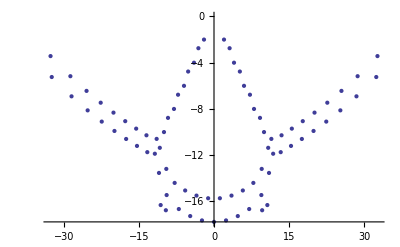

```mathematica
QNMroots[40,0,0,100];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{0,0},{1.9999999999999999999999999999999999993286139961147,-1.9999999999999999999999999999999999997422417326689},{-1.9999999999999999999999999999999999958468614673037,-2.000000000000000000000000000000000048604930324022},{-2.836753×10^-43,-4.0000000000000000000000000000000000013850194444148},{-3.119451591165901406677270195818347804199667824285,-2.74667574434060639673424111055691521504570956668},{3.1194515911659014066772701958183478041996640543167,-2.746675744340606396734241110556915215045713936566},{-4.0000000000000000000000000000002618732249347214769,-3.999999999999999999999999999997787430793254938516},{4.0000000000000000000000000000002688109310763196245,-3.999999999999999999999999999997790081648488925739},{-5.1695209757622296807430578994742774016479895966321,-4.763570116920460430468632656039809702065552187644},{5.1695209757622296807430578994742774016479913100388,-4.763570116920460430468632656039809702065551608498},{-1.012601455×10^-39,-7.9999999999999999999999999999996998747430188234777},{-6.0000000000000000000000006471924423079602509516378,-5.9999999999999999999999998973706489915654848225046},{6.0000000000000000000000006471924425276288041934885,-5.9999999999999999999999998973706496794787397484899},{7.1879308259996117388526360614015866612168725528252,-6.769564909076202323559978557203040828751056956522},{-7.1879308259996117388526360614015866619655543318198,-6.769564909076202323559978557203040829133491259104},{8.0000000000000000000141277166557377554722124064988,-8.0000000000000000000466635226050243170213110950917},{-8.000000000000000000014127716655739418732534149845,-8.0000000000000000000466635226050253663459255640825},{1.396796838×10^-39,-12.000000000000000000000000013641963513920930841696},{9.1971992904841208785460515729258700938177849525984,-8.772481103020287807698982939902503707735732904614},{-9.1971992904841208785460515729258759070826053022579,-8.772481103020287807698982939902502094822337655676},{9.9999999999999987059034478347600409334159328107364,-10.000000000000000438037717821430037674075392431715},{-9.9999999999999987059034478347601602328824939891841,-10.000000000000000438037717821430114120995573364261},{11.202675789970207181862039403435637200554205176093,-10.77416239650981779159273611838015610603735036627},{-11.202675789970207181862039403463675232474023694626,-10.7741623965098177915927361184923544564405188112},{1.484551×10^-42,-15.999999999999999999998538529687255235275253068268},{11.999999999994754208450811054328937824517655793461,-11.999999999983025965559671104916724052624901029585},{-11.99999999999475420845081105432894189292518088013,-11.999999999983025965559671104916784051678034252572},{-13.206246516656160899241244228374605107241546699604,-12.77523898318297705173309042744312226931564896183},{13.20624651665616089924124536204714230967138576697,-12.77523898318297705173309030677800721329022076307},{14.000000117745982227327325231278154041582457257728,-13.99999996943815410141177639560224863318954825852},{-14.000000117745982227327325231278102787636193519842,-13.99999996943815410141177639560238467140871470739},{2.3485391507×10^-38,-20.000000000000000245121107100459900215735739661125},{-15.208734789474495095747841603776718140638927582338,-14.77597396193128460533443973784662431431417573773},{15.208734789474495095747484896386422938345477275553,-14.77597396193128460534043039344945438833865965821},{-16.00010589858118407547710569745116484387709596673,-16.000465160880241250321367339936240578190584696875},{16.00010589858118407547710569865470531558511289474,-16.00046516088024125032136734079954756981763018416},{-1.17587417905×10^-36,-23.999999999980039436843049816401606505334609635217},{17.22809559054018073999381896347474108551932874342,-16.7729122361875709322783861836078278604714338507},{-17.228095590540180758800772584913403135426232852765,-16.77291223618757093399957096816732624576074333303},{-17.59968975438877009082372311624313716771083453542,-17.831038657483929887487493275850985556369659872985},{17.5996897543887700908237231162430001961732661572,-17.831038657483929887487493275858316678339645408639},{-17.74894922144411196842576744081540556666534055156,-18.215784966086893586122954676270175543583563320695},{17.74894922144411213880593705104481559887608743973,-18.215784966086893917889094138660669716112065704995},{-16.50902745167173457470585648163383450964189303998,-19.538271790464415547251933467775222938690906452339},{16.5090274516717345747058564816367403686503992382,-19.53827179046441554725193346777568423720077675351},{-19.061734044851292939830327466317710743753330093492,-17.43417667797701057834980849502918099632064807278},{19.061734044851292939830327466317640061487909956812,-17.43417667797701057834980849502926274624801213978},{-16.35242185562109702415857518546361085225868665962,-20.052346536278240515315859786743887346379407235839},{16.35242185562109723091084305403643728427169996873,-20.05234653627824080605775273672535714491780232289},{-19.609034215509139418803332402064622639184796264424,-17.24196579529183070471500518145566923874154629603},{19.60903421550913937733105587876559263204306097096,-17.24196579529183102106349878443056683394932055193},{-15.0976195643522986413762011089564494936879549939,-21.375991478165286216802498006764678310171932230437},{15.09761956435229864137620110895671318827443119383,-21.375991478165286216802498006765155724019224479015},{1.5975322104053×10^-34,-26.210873655828149235790161691225913439889959360055},{-2.449761380113438473304203371426518202612974104674,-26.121369673280025616038136099635199979098594123179},{2.449761380113438473304203371430341609256669143153,-26.121369673280025616038136099636298752810850045133},{-4.874591094137399939108648936036627531970296099649,-25.855908350661414456057262383895392236250590352291},{4.874591094137399939108648936036705675767224146089,-25.855908350661414456057262383895425718884629186377},{5.62304804188610558414695653909131×10^-16,-26.330069687559859742402908159935722740040526923555},{-2.429943088760887043797604832166107586202369531983,-26.243807352249560371219552187198017205882636799836},{2.429943088760888156853821401321477314444232433899,-26.243807352249560531756649624305956923506177456326},{-4.836924446630761458134089822760728938643771774011,-25.987756914771304748481685535427614381343957540952},{4.836924446630762536688131776914097066096464178998,-25.987756914771305067402260432022812410925120219977},{-7.250925903294981710561996662007647759704124867131,-25.423680546261921835676033758044240414034890672242},{7.250925903294981710561996662007647360951223452612,-25.423680546261921835676033758044242405017328559886},{-14.94068496429215421915004787575109727361811454235,-21.87154165260777498176016390928862442616503833033},{14.94068496429215439583240586736428157990518303943,-21.871541652607775305386195453688171531805969860404},{-7.199249949296539819382508282200303733419651337258,-25.570138486855629598698755072190783512338881869133},{7.19924994929654084111094815506930075422674623004,-25.570138486855630071878089693738878578067286346894},{-9.556237376777756554016263565065757624619076756375,-24.840646631941627960988521700033644352368430425123},{9.556237376777756554016263565065757439113244761588,-24.840646631941627960988521700033644789037460413598},{-13.57517317633640089935815241706591204368770086975,-23.027824558562900594116904348451687515085542359584},{13.57517317633640089935815241706674995747611498651,-23.02782455856290059411690434845157157939395272126},{-9.497433417749149350320412447801924781295759492954,-25.005851936954633508876261795810004458494835818004},{9.497433417749150293918527835877108457539883164203,-25.005851936954634133952749751681813140324299188416},{-11.73334480607708149827854991561638788824807984529,-24.116558619447585500679258391359547666458810603289},{11.73334480607708149827854991561640317877594905053,-24.116558619447585500679258391359561330321859821277},{-11.6883978832130851221345980181523575578908915299,-24.328970271269247696523073208960628575011309356496},{11.68839788321308590743802059654522343955721949534,-24.328970271269248504904176327387231637460447329224},{-13.49392020652836353184819456409112062236440490195,-23.428788460149669068044512378111828628365924850487},{13.49392020652836380598597545188161339458589184511,-23.42878846014966975160723550694406146077523397857},{21.100805300436772477727438127951133989017499661504,-16.9585567415052404827932394983675550678970177369},{-21.100805300436772477727438127951123741366393678452,-16.95855674150524048279323949836756865794077333615},{-21.614849072370566328962899027831144023543320173494,-16.7294604006599097944411710892009842834677917232},{21.614849072370566261293812503375684535739602609549,-16.72946040065991012198013378082563820987182632447},{1.96991080815771×10^-33,-28.000000897608965643859005648508998886842683308054},{23.198909064637769381661505327164234674849578247396,-16.42549795593959953034951638930400335567143776307},{-23.198909064637769381661505327166091505441272939326,-16.42549795593959953034951638930253585828566800789},{-23.717860478414485557855507250404895572267969303488,-16.17213097218631453496168116246747827135539605334},{23.717860478414485470606502178810589551956726525392,-16.17213097218631486237922050886371726483423603564},{-25.391049395779400058008910175564827079537842113078,-15.84329091086234571340657780132535742245710399258},{25.391049395779400058008910175564827265413865691568,-15.84329091086234571340657780132535728770892209934},{-25.913834212562307935915768676139932451995648523711,-15.56315111691233606849292321700008474831240617133},{25.913834212562307828034192164934235127377362944217,-15.56315111691233638962463687532635349433010536081},{-15.2933617574205819324114753015271086098984469491,-26.113070542963798573929524065100339723642592315755},{15.29336175742058193241147530152438460765568972226,-26.113070542963798573929524065134745153490858420974},{-15.82623454041940443556874240152732927840141236431,-26.670119119257687874795607258998177884781635318729},{15.82623454041940373977771003016942324462408030679,-26.670119119257689288515504335954124999238947436885},{-27.691319871610147491602124354113612278889421431728,-15.203436699746225955681339929728977220546471073},{27.691319871610147491602124354113612287756059321844,-15.20343669974622595568133992972897721176779044675},{-28.217094640030448083090826992364112879795174862426,-14.8947069403012593700209400192023882095208229324},{28.217094640030447956237267224726937133165644886221,-14.89470694030125967885512433772859075110569287977},{1.4250507494118×10^-34,-31.977083596605525921936456376118625265622035979312},{-30.117120437654726967711229276290133302568911543011,-14.49571940926655329593059317125579343274890276305},{30.11712043765472696771122927629013330140577222432,-14.49571940926655329593059317125579344230335949085},{30.644935741046278326721991014952299411624399214007,-14.15642065446257874932682790546903630156276559395},{-30.644935741046278468648721631897143215726809757123,-14.15642065446257845689425721984518627039508756977},{1.34009454539525657537662177794405830407120634016,-33.784958961540882768693041065208044495312250206642},{-1.3400945453952565753766217779476629896081591189,-33.784958961540882768693041065210833372159128789862},{3.742660080557354791174385395336917205169074332678,-34.449903569367689365622345665609038284547993530192},{-3.742660080557354791174385395335819958275937491937,-34.449903569367689365622345665610221598625167045571},{-32.690983679150793998238669072616310524343515438282,-13.70669453883077910945046832661476165481782869899},{32.690983679150793998238669072616310524343556176233,-13.70669453883077910945046832661476165481789822525},{-6.170007092573602569352652065932761802758533230907,-35.110364689146887075983669938525055560858303184514},{6.170007092573602569352652065932765131195718026754,-35.110364689146887075983669938525086896649889871255},{33.219791552976442958041645130155981751916952383274,-13.33453707361381086402792727018747112624684623759},{-33.219791552976443110795726124412859624354991149955,-13.33453707361381058895682419532398211159761864764},{-8.649782621318145704322278173556959163279933762785,-35.731190838953163001251933356144813854386078845366},{8.649782621318145704322278173556959129299419280359,-35.731190838953163001251933356144813947222876292332},{35.444006199085768728413640312444688959594566308811,-12.81773285138178726104417297588032586214117085054},{-35.444006199085768728413640312444688959594836617819,-12.81773285138178726104417297588032586214123736345},{-11.18331876719876425461696825242186789077730761826,-36.307007204289768565538996930498214514756539696123},{11.18331876719876425461696825242183615878866190072,-36.307007204289768565538996930498231611949950108564},{35.972641449992932855719772600395223008493874215455,-12.40987725008061575322778117848384362847090188026},{-35.972641449992933017388795499943239420568054744086,-12.40987725008061549473137455476711892132450484427},{13.78725617530249262710710052972664599293256582089,-36.844829450458952324967037419732131812493137973059},{-13.78725617530249262710710052972676398502218179514,-36.844829450458952324967037419732178217032199680146},{38.422455747926272804839776394369451639863407813995,-11.80107204821062579260670476499610220178284561237},{-38.422455747926272804839776394369451639863407815014,-11.80107204821062579260670476499610220178284561614},{38.949596382976688568981041478723228279499273873826,-11.35373796338635846225852724207078150993465590308},{-38.949596382976688739102967593883721775419074155146,-11.35373796338635822222853989187979736641308915295},{16.40137784226444335557027364959658943508596278832,-37.428702704574136676449231681938738634419638998782},{-16.40137784226444335557027364959197403401759234768,-37.428702704574136676449231681948248360040333784831},{18.76116482862561818318201960262386709337623979501,-37.681640896487503427854878098972280312312238737836},{-18.7611648286256181831820196026240959269054607163,-37.681640896487503427854878098972383720085190349211},{-41.702492652661267835145533575694906063885473295386,-10.61092514435698590011411122591937403055175381634},{41.702492652661267835145533575694906063885473295386,-10.61092514435698590011411122591937403055175381634},{-21.74138439235161569262051622296327898341444429542,-37.257469327644348816975059908936777458219644435709},{21.7413843923516156926205162229632787115973629896,-37.257469327644348816975059908936781450308128434198},{42.226612146606588049698871445636638213422897103765,-10.11864573565045657058908286118488302487246328011},{-42.226612146606588220425339004233706049910753148431,-10.11864573565045635298574215762318659841186519811},{-25.28515051874015267179698048382397070099047184697,-36.667256294477413148231496802454413997157856163845},{25.28515051874015267179698048382397070090500024306,-36.667256294477413148231496802454413997370257382822},{28.96269357465645442010370507546341360244814609896,-35.948356846373791702847787595631353479319800582194},{-28.96269357465645442010370507546341360970018137003,-35.948356846373791702847787595631353485117123291304},{-45.430899000997958481484275856233177739797036428409,-9.158958895806396594824005112832043908121849712063},{45.430899000997958481484275856233177739797042235209,-9.158958895806396594824005112832043908121848788484},{45.9502744408855963621562392783627132061427972204,-8.612858539845672372698683316706463371485505808429},{-45.950274440885596516897850954590412860661974179863,-8.612858539845672161253061681091149832917125704241},{-32.73745261447395989672193721633162546951631283499,-35.160847806070816138562855192291985690473799007205},{32.73745261447395989672193721633162546949333826586,-35.160847806070816138562855192291985691344900289883},{22.97253230396701048257736290265059054821141020164,-42.683569116045293268706351945753018962355543239044},{-22.97253230396701048257736290265059057310456152183,-42.683569116045293268706351945753018990995950825211},{36.633505912483365799929910138798945524664673325553,-34.30658102808888077208375698679924423632846139587},{-36.633505912483365799929910138798945524694262805956,-34.30658102808888077208375698679924423634475483076},{-49.991995075540537425712261225253495912649840266542,-7.215317128990241006932030235176509287849893046826},{49.991995075540537425712261225253495912649840266542,-7.215317128990241006932030235176509287849893046826},{50.50521575707465368558088163494908804952958853118,-6.597656846566105286175380532785693127208859968583},{-50.505215757074653859461207516037181884847422244957,-6.597656846566105032937659036001745206980096163815},{40.671117178664511654576749132550724246837868664903,-33.37851508037871775947574055589160866693121308107},{-40.6711171786645116545767491325507242468378696138,-33.37851508037871775947574055589160866693121280977},{44.87242596915376192485246714669315765873692657399,-32.36760942329516838645938152187611589266880656507},{-44.872425969153761924852467146693157658739441301299,-32.3676094232951683864593815218761158926709978265},{49.262566209230064340839249297874555126946744686299,-31.26166188757528916279468090171418058380295800198},{-49.262566209230064340839249297874555126951832887077,-31.2616618875752891627946809017141805838059922394},{-29.34409112346137110367930682346214788889596321065,-50.71919135042697287405725999768450670407884799255},{29.34409112346137110367930682346214788889257228682,-50.719191350426972874057259997684506704118809432172},{-53.870597132479795335362908553678285140468043482205,-30.04494450971362046750658982586258485615902930542},{53.870597132479795335362908553678285140483511358695,-30.04494450971362046750658982586258485614710237765},{-58.731823527876826178922443033082524484302800933001,-28.6974838746775077460407675289296136338875251878},{58.731823527876826178922443033082524484300677261362,-28.69748387467750774604076752892961363390881276519},{63.891824521940784623061816722115416313035119341077,-27.19321833554422912134903105431684093951801744603},{-63.891824521940784623061816722115416313039024205476,-27.19321833554422912134903105431684093953032945792},{-69.413406966419831837394663330858935950117563540803,-25.49627352175697010844714879226011308746122350866},{69.413406966419831837394663330858935960013450130755,-25.49627352175697010844714879226011307836297524206},{75.389920741766177501444622002720636016417544430477,-23.55345894670838604078658479020076787932136658133},{-75.389920741766177501444622002720636017205787593755,-23.55345894670838604078658479020076793413578893821},{-81.974845582108145145163242276606766182442724230954,-21.27738816287524220597577201118293599495169735356},{81.974845582108145145163242276606766182502565211148,-21.27738816287524220597577201118293599594432613576},{89.463449257139504636442673035662259926928815923317,-18.49994419687261399874481099758278653465084674308},{-89.463449257139504636442673035662259926929443983721,-18.49994419687261399874481099758278653465149475575},{-98.626595370539202367698203141069740242488413879445,-14.78408972955848945126801636583375616311983488323},{98.626595370539202367698203141069740242488413879496,-14.78408972955848945126801636583375616311983488347}}

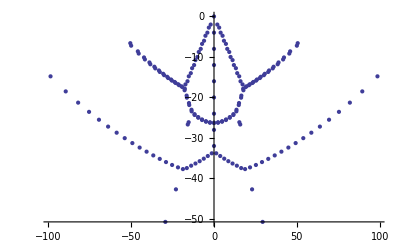

```mathematica
QNMroots[60,0,0,50];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{-4.509482727440382203969809×10^-34,-2.5000000009589150612909474586864926533787745527055×10^-9},{2.0000000040562502950547056522501171095793751952395,-1.999999998664040250719255456255924887555157978528},{-2.0000000040562502950547056522501171095764478413845,-1.99999999866404025071925545625592488755877210355},{1.349395744775424×10^-33,-4.0000000000000000000000010506168521011395561623069},{-3.1194515923540293741321446186119196858641899222359,-2.746675743980378685839817538552655903937166630228},{3.119451592354029374132144618612545724955188413068,-2.746675743980378685839817538552661983573052295361},{4.0000000026516400901052932229199456162236734837972,-3.9999999992257246414510465649106975598006841062193},{-4.0000000026516400901052932229230903727149057731991,-3.9999999992257246414510465649117800164184259627001},{-5.1695209766051871709699118854301747318880813423171,-4.763570116685742283505768776315176325472972576336},{5.1695209766051871709699117632209838661282639544594,-4.763570116685742283505768974694053988719596256673},{1.75213139878646546×10^-31,-8.0000000000000000008800503462367645602017055220878},{6.0000000020409833766683499021519570241238924923038,-5.999999999423821925043954282691151870643984477675},{-6.0000000020409833766683499023582034272702571367913,-5.9999999994238219250439542827947533663473808698635},{7.1879308266099526600708156803509767205322898283103,-6.769564908887186386480214745913158398391198793704},{-7.1879308266099526600758088496127377835739917965817,-6.769564908887186386486244400819532851946593061167},{-8.0000000162469798765697948252989936796841024000272,-8.0000000038887276935993668269973610416940682341998},{8.0000000162469798765697948253023658637777912054686,-8.0000000038887276935993668270048619937972956046845},{7.0352520574137507846×10^-29,-12.000000000000273564701576910860008938198018653781},{-9.1971995435994260850674847309001753824059791499865,-8.7724802596582871788467961214971865164833663651},{9.1971995435994261643475377692140067114904163669317,-8.772480259658287145707564557913691397791060221932},{-9.999957195314069835580999470526566844979257879292,-10.000104770428504097669139703816290718283789883743},{9.999957195314069835580999470551776637218796505521,-10.0001047704285040976691397038468078756407166357},{-11.206928115494755918785365722796885913046941484541,-10.77628283133017473374079066081644583208231530872},{11.206928115494804034818730165098644025825264682968,-10.77628283133057641325947763268295049136361824581},{-1.347696887944279401718827×10^-24,-15.999999967464214945294101226746905593850006449611},{-11.82753904484221515297894079916559998666976116708,-11.873436906263973258435540401779161516591569656353},{11.82753904484221515297894087232391831576932019164,-11.873436906263973258435540486529625751671005892414},{12.20348524278677882251992918824008771325747583243,-12.323405623332933652284448375431267602326398606642},{-12.20348524278022355876591219151476119253343627375,-12.323405623356557547888297645699814437643055552141},{10.99841497547743907783778564943872236953475756091,-13.533863274827494712617759103532924729381344155118},{-10.99841497547743907783778548016945449595109603656,-13.533863274827494712617759292139393904925265783525},{10.84800755256328434190564024642317211133326447984,-14.043227808977543039873841749826987361972833430186},{-10.84800755256370538823299050088970617746665085354,-14.043227809003540132568700464316174982130335227678},{13.337256298797830239536450199095430318140426004721,-11.73738722711944864987616121693696440793651725428},{-13.337256298797830239536450199098032492702721991084,-11.73738722711944864987616121693642454155828370375},{-7.604113349439705484×10^-30,-17.76943232434296688636233550281958600790256182634},{-2.403987699311771632969995831220983477814480140209,-17.641331053142455226655050880199021832265000348589},{2.403987699311771632969996113101995616791582147057,-17.641331053142455226655051327440849509628386419929},{-2.5883676649576301681015742500866673724×10^-11,-17.907085158896288783773952687035466073922228957447},{-4.757369750634796488128165962526504742620140887027,-17.265790561205292240448001227003226362999940642993},{4.75736975063479648812816559610518904060151999374,-17.265790561205292240448001677037894870035596693278},{2.378511220529055664027147495630068059108246974447,-17.785238029600396149981902712627817213864835658211},{-2.378511220577672485758812704992248728497171178454,-17.785238029623044347027476091469264916174387045009},{-13.879953707397099645653580023253007962051373469648,-11.51261092169871281897906543226306430782725367232},{13.879953707416555318828530089476850247773617154765,-11.5126109216826220033392110380184781370427352991},{4.711382264937646129314249817278611064376952044015,-17.427352571735271823761858824899538375785865527437},{-4.711382264977019440841545403754897825170101720992,-17.427352571778642928051462370600485850644341745195},{7.033614732523526694306776355539112489091377356386,-16.657253001243164781693619014310209897568153375693},{-7.033614732523526694306776343602236573007268829594,-16.657253001243164781693619021815203726422485664678},{9.468153173775517488263533650567546332996082978161,-15.447801793338478955496257509449858822995915394445},{-9.468153173775517488263533650569417098727573732434,-15.447801793338478955496257509452064693658825442365},{6.961471028475917350080312440714909453948192144383,-16.842544396368836374456894221814756086498826598933},{-6.961471028501584983148181093500363108846788590625,-16.842544396427675878020645990044445931053785146822},{9.184302968375263853889969666810289597038872530319,-15.823693136892654198424449748318087988649268142979},{-9.184302968400848660895653816867953466973345984965,-15.823693136935125486689016293817897390095655658179},{15.397846782758267386118612068544449934861208522743,-11.19784679402908396202288988297741654317225821345},{-15.397846782758267386118612068648957448226895600171,-11.1978467940290839620228898828397881140293785098},{-15.913012732068680568816643471643119982886838930452,-10.96021265457458304901214335058781893840421511264},{15.913012732091794496696839362975870109379064636467,-10.96021265455860846164155092521517074917038749972},{-9.626034442778090136550429391753674157292109073036,-16.7621594052903895527016198113703374481704677001},{9.626034442778090136550429391752293091983893329283,-16.762159405290389552701619811372204018759848095534},{1.4333829606717594970283268221×10^-19,-20.001432685813839480479396176523463386123038770082},{-10.16831071133924837593057745150748685129537157628,-17.263441816507187076913024467840045272293626950546},{10.16831071144275776596111083530477485860621693907,-17.263441816460462718722914722204340755422801585814},{17.566960382663487790149557010883420067226219385234,-10.59610582563382384470823394460750184756803695349},{-17.566960382663487790149557010883420067648925555072,-10.5961058256338238447082339446075018469218645615},{-18.088971322056794060507780908385424111266268123005,-10.31901405164093139815154582642397403297479689983},{18.08897132208293409299309790210572120144100220338,-10.3190140516264968746704347466185521577432343297},{-19.901522462143714597657218621894934694601071141142,-9.903788350103557254968750581088414215464718729162},{19.901522462143714597657218621894934694601071954713,-9.903788350103557254968750581088414215464718616065},{-20.427953582114329538490696480390696820447349003985,-9.582772765946425976430023290280146633692081969427},{20.427953582143254121309869126521882817066648397623,-9.582772765934862835487408860038368955482775209919},{-3.4792489113690679537687401405089×10^-17,-22.644156750874117675863127344360821785294683969937},{2.233540901640278657857543480588732067587730503503,-23.089225555902514618368205389067797309113112060883},{-2.233540901640278733456482281177159895717357383898,-23.089225555902514641501228407838244070718503214518},{4.638646755109309307197290544200143883874515461039,-23.736782021038660079605109326816978887689748375356},{-4.63864675510930938797646133587084628163733881181,-23.73678202103866010709272134526014545218021229691},{-22.443888023494474365267466613480944527279536180813,-9.093683729676233185236797540792302827404599207414},{22.443888023494474365267466613480944527279536186793,-9.09368372967623318523679754079230282740459920556},{-22.972850149813341683282199697785655155483871347157,-8.723710887391963053348202709759964885898675481078},{22.972850149843836731918006087004187751785898571416,-8.723710887385156638769590076826404372131952910677},{7.136074775426602362011763376247723467641671724602,-24.314673580601273909515590560298244147094927459823},{-7.136074775426602445321290220124673481886694175051,-24.314673580601273943373649075831936563391804332517},{-25.261690314508540072100237782457247478664487800108,-8.12272216140746108892558065431283298680420969421},{25.261690314508540072100237782457248808265167179648,-8.122722161407461088925580654312833442102753807192},{9.774147834353867447639257483345454956263832501484,-24.850194211956576455494252384821766713623420932243},{-9.774147834353867538618552070834029406472935472077,-24.850194211956576492234817995073931835097381039737},{-25.791121984073206533158689257850413223969702475887,-7.696841620565981053492183817569362476269859525175},{25.79112198410166436297542349917158569693195839756,-7.696841620565639084473705803456385565971884395541},{12.24830892041940010296624123714265889442758246186,-25.646952569932524749034670116295464734296441623729},{-12.24830892041940020669635280864157061875805819703,-25.646952569932524858402351897810142516572075683036},{14.33296916102698096852804423625781942048682343011,-25.254070621681960364483730438943171281982225627943},{-14.33296916102698096610144035074601432255417659806,-25.254070621681960426624573909549512017560509169045},{28.482981296402897449741238786165862253411369188381,-6.908983562193753139540041459114605094590219826112},{-28.482981296402897449741238786165862253411369266349,-6.908983562193753139540041459114605094590219814238},{-29.010756561642581631280996902277260842482193036746,-6.415899675787097532281780595891704084837343919616},{29.010756561661879480737287693398842893976793561044,-6.415899675791125052647613543093574302545295909411},{17.67296747155618809265830114028623291266149057092,-24.493220571567412387232777425980263592261789290111},{-17.67296747155618811167028643847923742862479743426,-24.493220571567412416403221508416270313804543221402},{21.35088485505958198448825900360910853541369192888,-23.741732322711480496787396073680597966030990058251},{-21.35088485505958200710337060341433114308656172011,-23.741732322711480525398941005766043839218809691941},{-32.440933855406794140544190897828827444366184200074,-5.238817587337784103610507100525154029334385239465},{32.440933855406794140544190897828827444389933947684,-5.238817587337784103610507100525154029308654158771},{-32.966186279852335202383140593969808929734334282238,-4.655464453130587412295532277839645238908808163474},{32.966186279857118186270318554714619121647497175327,-4.655464453124772903360553406066065281337920222231},{25.217063031237950193849697709659314741557419756094,-22.87582673396036325123922075192039637564268707681},{-25.217063031237950220488959014475438044407682957831,-22.8758267339603632848055863846413590178715131536},{29.295766577581762953660216382328281101283164777664,-21.89650048544809572421564191842703533643863501405},{-29.295766577581762984396707008721527455095959977264,-21.89650048544809576421380218985037010871468074624},{18.16303553785397194887873872192426731384509156486,-32.009550197057777436141440570933612639623117492412},{-18.16303553785397196271039970588394879181741330719,-32.009550197057777658082806804279591095633561965388},{33.642945452513071515698434831715547784314792510547,-20.78274611918398877851372513752164693556235678357},{-33.64294545251307154914901199567268816779804727416,-20.78274611918398882587039465187720656821800470702},{38.323834472520461164373457355139587775408372491684,-19.49795382869529485291470862082436581149974012121},{-38.323834472520461199431817497637998826959491577296,-19.49795382869529490791442660643064727556449768988},{43.425611006282103668924976664135231559284074385947,-17.99017156813561514063062327293689558251485500123},{-43.425611006282103706950848761483920978806616125929,-17.99017156813561520467634344603716238696504787601},{49.085349517414945637357872672408653608710253155114,-16.1780871497792611980581490505288151498932639476},{-49.085349517414945680127478498808491177445094235072,-16.17808714977926127999898214140157447749757451651},{55.561718843691411995970818914421346997354249902957,-13.90880492285233415906466468004573020827571810292},{-55.561718843691412029544715354674536445189498003827,-13.90880492285233427641984901144462832078026803996},{63.523836287141262974911948699510587090613824898111,-10.78571283746046531944186852683619706178976795011},{-63.523836287141262959807584132186544417779855298182,-10.78571283746046545985066097545953477799801111446}}

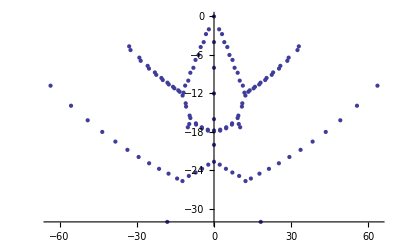

```mathematica
QNMroots[40,0,1/10000,50];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{0,0},{2.02330955955661230970750426183,-1.8657798871976120238414314269},{-2.02330955955661231048269103378,-1.8657798871976120239698844548},{-1.5345048×10^-21,-3.92000000000000000000141126626},{-3.08989754843239389567594535467,-2.8062341229523988363993024778},{3.08989754843239389568129204529,-2.8062341229523988364042199013},{4.02263115950071170711311420793,-3.8363600152389775135965202015},{-4.02263115950071201364095920175,-3.8363600152389774875421090593},{-5.10714530804506834760213680053,-4.8831580136075293889383305715},{5.10714530804506834760076513454,-4.8831580136075293890465357724},{1.1102752×10^-21,-7.84000000000000000249311354051},{6.01519389265317299523525163333,-5.8281271935257856700542100695},{-6.01519389265317821105512329463,-5.828127193525785763155231688},{7.09349744649522636028268831164,-6.9542099773818050527764067054},{-7.09349744649522636031805647068,-6.9542099773818050528403509229},{8.0040362001202533383641239131,-7.8327582042402499666724532301},{-8.00403620012029828611604876158,-7.8327582042402414397094641153},{1.3244422178×10^-16,-11.7600000000002863905112128342},{-9.07138467670377056166694389887,-9.0259416388358172207997605613},{9.07138467670377092466217351737,-9.0259416388358170332144262659},{9.99035205981701946239677151016,-9.8462513192409273434437660816},{-9.99035205981702646160899473702,-9.8462513192409535041910721189},{-11.055535128608249314005514537,-11.1103507387356113827390363006},{11.055535128608973031453348742,-11.1103507387377180355417620963},{-4.5535739633558×10^-14,-15.6799999838189617073612177717},{11.801095414568998240888989624,-11.8097565758666158962319293328},{-11.801095414568998222725480819,-11.8097565758666224064398477543},{11.875059574581802921148351842,-12.3167391097368181135004635497},{-11.875059574599206181500314864,-12.3167391097845468260977412081},{10.398889473387227690651611515,-13.9985477681071423492599073068},{-10.398889473425824457759561219,-13.9985477681520003216830216464},{-1.11227046340668331×10^-10,-17.465359272625320310766179043},{-10.968596375840915569439798277,-13.5985005294530082451895176802},{10.968596375869491399706551415,-13.5985005294992612149098028627},{2.2889896326727805302872510025,-17.3545143876227465511480193794},{-2.2889896328906713201553362798,-17.3545143876636707323931769921},{4.539862119903535368536299726,-17.028214064104685462954855604},{-4.5398621201040231426566840042,-17.0282140641837430447725706529},{13.195607575590807809361952808,-11.748463575798163291053419509},{-13.1956075755146208490923296428,-11.74846357590816380110378326},{-2.575178995523024×10^-13,-17.7730034002274566853450617634},{6.7110851653385175319599836121,-16.4933314857755163113405185228},{-6.7110851655094226033096594982,-16.4933314858837204525176255816},{-2.3967986244311260779390211329,-17.64683021552616618502012853},{2.396798624431102510405437345,-17.6468302155261700811923423441},{8.7523085176273149491741820073,-15.5834988566113587085679160233},{-8.7523085177357810982424065369,-15.5834988566867916319099509731},{-4.7446166573586210123563773963,-17.2764823361875507051530818222},{4.744616657359134393171404305,-17.2764823361874169358595509637},{13.7484192414086861200685695894,-11.530698429099490633018966865},{-13.7484192414043906650727683233,-11.53069842914131870363504183},{7.0155426856121992473243082162,-16.6719762279222337520697919762},{-7.0155426856124507246852247264,-16.6719762279370954495983938589},{-9.3971219470425832521617901825,-15.4956460485012222710748231415},{9.3971219470435121813413591066,-15.4956460485120943621096047371},{15.2757773112196241910972411249,-11.216733829825006030723411583},{-15.2757773112196234907593289469,-11.216733829825009703537898804},{15.7921759473710621602305383961,-10.982154104022974663667473095},{-15.7921759473659692568940004063,-10.982154104061860719798705291},{-9.7143479492527153680101266954,-16.8693461316378895452774889437},{9.7143479492527689665482777961,-16.869346131637867363583420279},{1.56695848×10^-20,-19.6006929145749349911596802635},{10.261647718927633306294356128,-17.3942208464685395387672144176},{-10.261647718841700430065136403,-17.3942208467429669488305099632},{17.4529398907708945402743327252,-10.629314592004381636669866599},{-17.4529398907708932577067085893,-10.62931459200438465072750942},{17.9769916664683045887626694246,-10.355316753412169562577082046},{-17.9769916664636464542713177216,-10.355316753447553020310486507},{-19.7965734343471946534856163927,-9.9523414207435050132010460577},{19.7965734343471963515581364475,-9.9523414207435027461842805116},{1.583428911748×10^-14,-22.4500804812452698575789984089},{20.3259845971344022974079474294,-9.6341150962849182564346984737},{-20.3259845971305098533766444531,-9.6341150963165734888375062498},{-2.1279072691019098876685377326,-22.9300028157029561355068308889},{2.1279072691018936072038227653,-22.9300028157029664739233823449},{-4.5178996003246966511659703318,-23.5969182047278339471706865248},{4.5178996003247057249007148982,-23.5969182047278363808736552486},{-22.3497613877542628542572483206,-9.1586394633699499414284363542},{22.3497613877542647935937892032,-9.1586394633699485064598116301},{22.8827893501074741475383331718,-8.7910143843585468716339551412},{-22.8827893501041761863892791138,-8.7910143843865147972180696636},{-6.9990201170152267008652198249,-24.1875072248499425902813788733},{6.9990201170152363928205438388,-24.1875072248499471666630802586},{-25.1813689570639568854427045018,-8.2051930092727163307761432566},{25.1813689570639587464190089709,-8.2051930092727158140869403138},{-9.6307506097349972061262971343,-24.7168226622844604960408403152},{9.6307506097350068307963040114,-24.716822662284467070975156339},{25.7161391316204045529574936349,-7.7810872213538465510123391697},{-25.7161391316167612023749612709,-7.7810872213775069588697157208},{-12.204310383849781673742058554,-25.6191784283112347476765445592},{12.204310383849790400358926901,-25.6191784283112523712371743607},{-14.032929062290890723212007937,-25.2725138353368606642518241877},{14.03292906229088504999837298,-25.2725138353368666034634197759},{-28.4216145209192403186171426015,-7.0102420558525835949851594178},{28.4216145209192415917039205327,-7.0102420558525838214863758469},{-28.9562991854851044734630423792,-6.5182388787821479507054124569},{28.9562991854905059263564339908,-6.5182388787656475446508342398},{-17.386033227951235982345798385,-24.4520057080081765665024622309},{17.386033227951235305831327949,-24.4520057080081801057711642665},{-21.075426903526989567250035873,-23.7259460184879519259918856936},{21.075426903526988705326078418,-23.7259460184879549640262376065},{-32.4091731445919973953991612681,-5.3610905942047207074725085052},{32.4091731445919978177094358479,-5.361090594204721007081762059},{-32.9434562083223766735879153712,-4.7780799482955577810605148784},{32.9434562083262330090248895848,-4.7780799482980292540753924691},{-24.9576813460372294666838083216,-22.889321078942457039329901921},{24.9576813460372282366730175011,-22.889321078942459635187950436},{-29.051808804137617135966508773,-21.938273532649625394999133953},{29.0518088041376157996584024067,-21.938273532649627505329006529},{-18.301174220415986448914970031,-32.2384715473387201544978092717},{18.301174220415980010735209586,-32.238471547338735522448802078},{33.4139465775960324944889305587,-20.854037787093014318991952579},{-33.4139465775960336936701989848,-20.854037787093012999023673344},{-38.1110761412188278620047277586,-19.600929292700534771044696715},{38.1110761412188274509200852488,-19.600929292700536263663337671},{43.2322495549865439194912347257,-18.127242430543410228260547459},{-43.232249554986544681471799157,-18.127242430543409189656052005},{48.9168935755623262146960690339,-16.351770684139128675254802686},{-48.916893575562326751508738187,-16.351770684139127753944434191},{55.4277271569795021702647076897,-14.121911353820452454715359033},{-55.4277271569795026410063961302,-14.121911353820451696024360172},{63.4442160593002677308369044537,-11.042681238867085099144992383},{-63.4442160593002679151030711144,-11.042681238867084131757194588}}

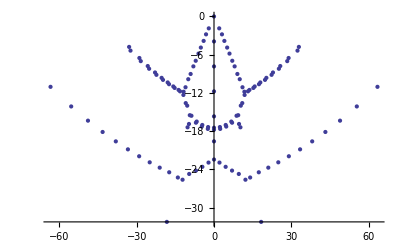

```mathematica
QNMroots[40,1/5,0,30];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{-2.15308093×10^-22,-0.0606387593402484490090154509419},{-2.1147509792175010731585858598,-1.8442297209782822387360267171},{2.11475097921750107315860094978,-1.8442297209782822387360267492},{-3.39594382×10^-21,-3.92000000000000000000464274106},{-3.11991211138350954784784732314,-2.7963686666723829815646918662},{3.11991211138350954784737279914,-2.7963686666723829815653416824},{-4.07939631903285983375639351151,-3.8252019920763768917566055956},{4.0793963190328598337566366033,-3.8252019920763768917566664022},{5.12889836568433821971107750641,-4.876234449058877563311425773},{-5.12889836568433821971138603588,-4.8762344490588775633158198295},{-9.6808724213×10^-19,-7.84000000000000000016413851078},{6.05725479120630670141991328335,-5.8205464995116140549350488474},{-6.05725479120630670144247184309,-5.8205464995116140549655966317},{7.11118757786342267668235637318,-6.9484258673300069012343447858},{-7.11118757786342275172396255158,-6.9484258673300069320222119005},{-8.03782677754179457578205789495,-7.8269635454311734243811358771},{8.03782677754179431556613889533,-7.8269635454311740036311468176},{6.18876564704×10^-17,-11.7600000000001958488728601442},{9.08655949989835485621365311406,-9.0207659025461896862966611377},{-9.0865594998983606119019067294,-9.020765902546187873919245977},{10.018792666177211988217409919,-9.8415162141295974649162437545},{-10.0187926661773472407328191089,-9.8415162141295183200872740593},{-11.069329709042425263080094106,-11.1051296381463638174044787754},{11.069329709042271154879274618,-11.1051296381475313733606300259},{-6.521906337950218×10^-13,-15.6799999799900366500044443555},{11.8210674862803793142300151592,-11.8128071679674728047541504},{-11.8210674862908171117322002418,-11.812807167957856717281718794},{11.878389814352119152360047134,-12.3209235446284077215613128051},{-11.87838981435849457230976862,-12.3209235446679966697218290337},{10.405196492019703898042298894,-14.0051865737156515348718181308},{-10.405196492031460447077811895,-14.0051865737379018646249172736},{-1.906437532303128868115×10^-7,-17.4751768047908794036762445219},{-10.977572321000931369932098623,-13.6125023900439441965334700966},{10.977572321016295722651868306,-13.6125023900429734530996882508},{2.2892071859059321834909579904,-17.3641841659960624472795340176},{-2.2892073354433406710112072965,-17.3641843112883449511822091225},{4.5403461241744487288931793905,-17.0374800709930107988187152367},{-4.5403461242477239862222785554,-17.0374800758734550882728202102},{13.1964498402050014380466789732,-11.746731898806118714519409469},{-13.196449840204806594384858206,-11.746731898812120057884985884},{2.7208772625691269165179×10^-6,-17.7855120645564671664512590549},{6.7120800625076752399290773127,-16.5019338970572089359259669891},{-6.7120800624647137983999026351,-16.5019338973566066932004985697},{-2.3975204887214668737322602593,-17.659341229641466852963305275},{2.3975234231842897484084946398,-17.6593409621177232475779884215},{8.7562144865234481169792274938,-15.5914788307469789376222583292},{-8.756214486531034209069548585,-15.5914788307849472901747317351},{-4.7459489376489131594565346317,-17.2889732562524922836961239136},{4.745948985795712779498547795,-17.2889732995286573748903503861},{13.7513647090244121175263951988,-11.529607010008424571582788425},{-13.7513647090123593578437430735,-11.529607010024340071575266622},{-7.0174300662383883926137757555,-16.6849501746861755806568586806},{7.0174300663274867944979806016,-16.6849501780756665467639196562},{-9.406443198877011570204837639,-15.5124382342151067911798953697},{9.4064431986725362377860526243,-15.5124382344443548683001992233},{-15.278398458366570587852815572,-11.215772850013331564293923247},{15.2783984583666591215695259263,-11.215772850013446767428493731},{-15.7948742563547038493815843195,-10.981225820973404459159560209},{15.7948742563670664625205943032,-10.981225820960120894443870524},{9.7142782365891065115042754436,-16.8658694777173151472903186214},{-9.7142782367165135971834999489,-16.8658694777345856847423550614},{1.335404868745477×10^-12,-19.6006927810383007689684736662},{10.263695815409934728039279006,-17.3909837043193530827103756157},{-10.263695815269419019292514813,-17.3909837045435866927157161805},{-17.4554557080663450101781861298,-10.628531685872014452209754027},{17.4554557080664210643930517418,-10.628531685872123915879702726},{-17.9795825453454720571245208574,-10.354593321677722518253432928},{17.9795825453578959649049299814,-10.354593321668165616287990162},{-19.7989788986383357823836055651,-9.9517413940335085754024696393},{19.7989788986383906052384469808,-9.951741394033598793247558486},{4.772566471808558×10^-12,-22.4502098734388288175090483311},{-20.3284537892987339440796298766,-9.6335693277820272962640313032},{20.3284537893108990177642957663,-9.6335693277766826106777604605},{2.1278465225216231158623076125,-22.9301423277260415183870032434},{-2.1278465225243806662051016281,-22.9301423277281600584122892432},{4.5178276208610965974786569242,-23.5970504843140057257109702015},{-4.5178276208625431632040290236,-23.597050484316095859322781576},{-22.3520461735022755312337676509,-9.1581990851174409466457799461},{22.3520461735023183409012156496,-9.1581990851175079117563667611},{-22.8851281812263724231922120623,-8.7906229624762149757477777923},{22.8851281812378312920822195646,-8.7906229624759501318755974321},{6.9989386453787003515227451558,-24.1876270937778662086119604016},{-6.998938645379045320105148831,-24.1876270937800613066972330985},{-25.1835259070810454059914228747,-8.204891520627148497906762455},{25.1835259070810954646508436872,-8.2048915206271971481223041062},{9.6306690675271082954954221861,-24.716923208275451370760897568},{-9.630669067526906943242311446,-24.7169232082773696287984848955},{-25.7183419789337190654176465295,-7.7808292417937948570239850289},{25.7183419789431637236046372483,-7.7808292418001083913666734839},{12.204250242855422078344269913,-25.6193280718523848931345547158},{-12.204250242853640322987898655,-25.6193280718545854493125736945},{-14.032760742556342521128811505,-25.2725960676591827881318066739},{14.032760742557356762530584278,-25.2725960676597008962819323347},{-28.4236375685771960390826663018,-7.0100625599123996342448955343},{28.4236375685772623442705741976,-7.0100625599124513477725835542},{-28.9583611506234840022550021881,-6.5180974092334157739793439898},{28.9583611506264323366824634196,-6.5180974092473856673243623544},{-17.385899453654112030452074448,-24.4520457516449801085018465255},{17.385899453654537887084464505,-24.452045751644980485995081122},{-21.075301937743328357460843766,-23.7259710410988426931079184548},{21.075301937743702834458229794,-23.7259710410989182774231201142},{-32.4110520641736929681420568046,-5.3610241290058749941327045532},{32.4110520641737697292915200878,-5.3610241290059608334803013405},{32.945367695363887222592441291,-4.7780458491772468492012823487},{-32.945367695373301171454863238,-4.7780458491631886792031484844},{-24.9575658604328036289333745686,-22.889336317787961987695063058},{24.9575658604331306188525501854,-22.889336317788147231867665443},{-29.0517038197190334837994517904,-21.938281189642351621203432794},{29.0517038197192735112668554077,-21.938281189642611566507655158},{-18.301081030485856903642016622,-32.2386746246275895210204219835},{18.301081030487607367529873285,-32.2386746246278748841675028468},{-33.4138520231851150999885908721,-20.854039602584083561989271},{33.4138520231852417637467884241,-20.854039602584361740404862842},{-38.1109915376498914232536296082,-19.600926856626876730970254615},{38.1109915376499170456336336467,-19.60092685662711024977504253},{-43.232174335232349691981633461,-18.127237135262883631433814057},{43.2321743352323165817018684816,-18.127237135263036404393823779},{48.9168272539889331657682492184,-16.351763752685524325562043613},{-48.9168272539889846110474001712,-16.351763752685467094928447853},{55.4276694661108440116800377227,-14.121903998812828280419544397},{-55.427669466110878191775088136,-14.121903998812897487831343427},{-63.4441671160762257079266184849,-11.042675098974310519404938657},{63.4441671160763806323374830417,-11.042675098974078506860005648}}

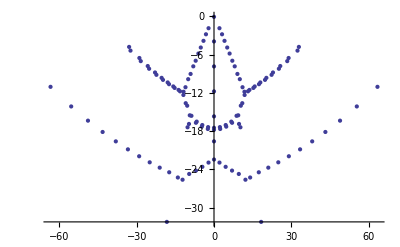

```mathematica
QNMroots[40,1/5,1/2,30];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

{{3.1796523×10^-9,-0.1287488439798268},{-3.819518×10^-9,-1.436743000778224},{5.6659677×10^-8,-1.999999550154666},{-2.603215439815368,-1.13908200667061},{2.603215443650127,-1.1390820061747},{4.589528916×10^-6,-2.929387102735623},{6.771368106×10^-6,-3.073453472341365},{-0.000055196611759,-4.00039462000871},{0.000554383637885,-4.615146573257895},{0.00001326857962,-4.799228522139181},{3.54962218618711,-3.836223235323709},{-3.54962253965115,-3.836223393946461},{-4.308631238237453,-3.73624818040303},{4.308631190627966,-3.7362482717131},{-0.000074298545005,-6.00701042166453},{-0.00289106728272,-7.345364694714295},{0.074641441028775,-7.454838381110659},{-0.089589582263888,-7.666275822501541},{0.00021611401181,-8.058598399717157},{-2.77442528657862,-8.087991866890313},{2.77434791603765,-8.088062807329529},{5.192289465706,-6.832180638609219},{-5.19231390724207,-6.832204739489588},{-1.59914215805062,-8.431131877761649},{1.60772400702852,-8.433938619323346},{6.310736107363948,-6.19493290019},{-6.310736588336706,-6.19493353517647},{6.596200432918593,-6.28319687563678},{-6.596202496335882,-6.28319556082839},{5.07478779208607,-7.772692333834379},{-5.07504468098162,-7.772800609376202},{-4.33502430197292,-8.808823475402726},{4.33512411872926,-8.809216569458699},{8.547190211199394,-6.0456324542605},{-8.54719030775497,-6.04563255868405},{5.17555005856739,-9.242469984271119},{-5.1755389430538,-9.242490321011165},{-0.50069553804717,-10.61410164763158},{0.50073959059866,-10.61414274905132},{9.164185866033594,-5.86749376632864},{-9.164185916156314,-5.86749400064865},{-2.83265257363177,-11.85012134906732},{2.83265574748699,-11.85012881456917},{-11.43688082700759,-5.37622465796207},{11.43688374904941,-5.3762235957848},{12.08614367463879,-5.06449911919672},{-12.08614384317626,-5.06449925426023},{-5.97070312094513,-12.48483002693056},{5.97069604642506,-12.48486134214356},{15.1077825576147,-4.24437545182634},{-15.10778256976161,-4.24437545891876},{15.81031689990649,-3.76140786412097},{-15.8103173746007,-3.76140796075337},{10.6042446100087,-12.6605418105128},{-10.6042535340559,-12.66054123265989},{8.01555999548956,-15.78619198298574},{-8.01556207028371,-15.78619240260549},{15.56642692634665,-11.9639823202643},{-15.56643244467164,-11.9639808153168},{21.28683405006427,-10.8681379867907},{-21.28683253348459,-10.8681475376526},{-28.59873130912018,-8.95475492931494},{28.59872750657381,-8.95476739605962}}

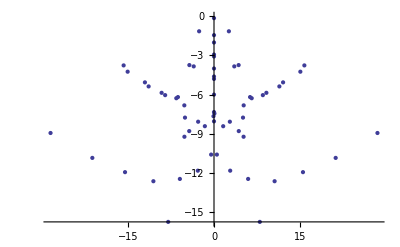

```mathematica
QNMroots[20,1,1,16];
{Re[%],Im[%]};
Transpose[%]
ListPlot[%]
```

#### Convergence test

```mathematica
XZsub[MM_]:=φxz:>Function[u,Sum[a[nn] cheby[nn,u], {nn,0,MM}]]
VXsub[MM_]:=φvx:>Function[u,Sum[b[mm] cheby[mm,u], {mm,0,MM}]]
AXsub[MM_]:=AX:>Function[u,Sum[c[kk] cheby[kk,u], {kk,0,MM}]]
YZsub[MM_]:=φyz:>Function[u,Sum[d[ll] cheby[ll,u], {ll,0,MM}]]
VYsub[MM_]:=φvy:>Function[u,Sum[e[ii] cheby[ii,u], {ii,0,MM}]]
AYsub[MM_]:=AY:>Function[u,Sum[g[jj] cheby[jj,u], {jj,0,MM}]]

grids[MM_,prec_]:=Table[1/2 (1-Cos[nn Pi/MM])//N[#,prec]&, {nn,0,MM}]
```

```mathematica
XZcof[MM_]:=Table[a[n],{n,0,MM}];
VXcof[MM_]:=Table[b[n],{n,0,MM}];
AXcof[MM_]:=Table[c[n],{n,0,MM}];
YZcof[MM_]:=Table[d[n],{n,0,MM}];
VYcof[MM_]:=Table[e[n],{n,0,MM}];
AYcof[MM_]:=Table[g[n],{n,0,MM}];
cof[MM_]:=Flatten[{XZcof[MM],VXcof[MM],AXcof[MM],YZcof[MM],VYcof[MM],AYcof[MM]}];
geneigs[mtx_]:=Eigenvalues[{mtx/.Ω->0,Coefficient[mtx,Ω]}]//Reverse;
```

```mathematica
QNMonly[MM_,que_,key_,prec_]:=SetPrecision[Block[{Q=que,θ=key},geneigs[Transpose[Join[xzMatrix[MM,prec], vxMatrix[MM,prec], axMatrix[MM,prec],yzMatrix[MM,prec], vyMatrix[MM,prec], ayMatrix[MM,prec]]]]],prec];
xzMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn1/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
vxMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn2/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
axMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn3/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u-> #)&/@grids[MM,prec]))/.chebysub;
yzMatrix[MM_,prec_]:=
(Coefficient[#,cof[MM]]&/@
((eqn4/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
vyMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn5/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u->#)&/@grids[MM,prec]))/.chebysub;
ayMatrix[MM_,prec_]:=(Coefficient[#,cof[MM]]&/@((eqn6/.{XZsub[MM],VXsub[MM],AXsub[MM],YZsub[MM],VYsub[MM],AYsub[MM]}/.u-> #)&/@grids[MM,prec]))/.chebysub;

chebysub={Derivative[0,m_][cheby][n_,u_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,u],
cheby[n_,u_?NumberQ]->ChebyshevT[n,u]};
```

```mathematica
QNMonly[2,0,0,3]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
qnm[30]=QNMonly[20,0,0,30];
```

```mathematica
qnm[30]=QNMonly[20,0,0,30];
qnm[35]=QNMonly[20,0,0,35];
qnm[40]=QNMonly[20,0,0,40];
qnm[45]=QNMonly[20,0,0,45];
qnm[50]=QNMonly[20,0,0,50];
qnm[55]=QNMonly[20,0,0,55];
```

```mathematica
qnm[60]=QNMonly[20,0,0,60];
qnm[65]=QNMonly[20,0,0,65];
qnm[70]=QNMonly[20,0,0,70];
```

Eigenvalues::lconv: QR algorithm failed to converge.

Convergence of the true solution:

```mathematica
qnm[30]
```

{0,0,2.00000000010145866298551421573-2.00000000000896057081618316094 ⅈ,2.00000000010145866298756346612-2.00000000000896057081542057171 ⅈ,-2.00000000010145866298756346619-2.00000000000896057081542059053 ⅈ,-2.00000000010145866298868367438-2.00000000000896057081477818191 ⅈ,-9.4×10^-28-4.00000000006437738177564457241 ⅈ,-4.0000000000643773817756445745 ⅈ,-3.11945159664383661849999108581-2.7466757277160200466426192785 ⅈ,3.11945159664383661849962987401-2.746675727716020046643102672 ⅈ,-3.11945159664383661849987959175-2.7466757277160200466428249199 ⅈ,3.11945159664383661849987962546-2.74667572771602004664282492 ⅈ,-3.9999923400431795687382037716-4.00000864916282739462928654415 ⅈ,-3.9999923400431795687378265878-4.00000864916282739462990318576 ⅈ,3.9999923400431795687415838879-4.00000864916282739462633333006 ⅈ,3.9999923400431795687403254327-4.00000864916282739462896896624 ⅈ,5.16998035224286569941050470722-4.7641398684669715199718153444 ⅈ,-5.16998035224286569955199155562-4.7641398684669715200006418127 ⅈ,-5.16998035224286569955199191231-4.7641398684669715200006416387 ⅈ,5.16998035224286569955199208351-4.7641398684669715200006416196 ⅈ,0.-7.99994301175551064451386923812 ⅈ,-7.99994301175551064451387133802 ⅈ,5.95470364884195256998834778318-5.9291458387556648675110479307 ⅈ,-5.9547036488419525701508780358-5.9291458387556648677882982808 ⅈ,-5.95470364884195257015092833088-5.9291458387556648677883405119 ⅈ,5.9547036488419525701400497641-5.9291458387556648678074198135 ⅈ,6.5858500663969088829963138602-6.4449521793323292387504622032 ⅈ,6.58585006639690888299863896158-6.4449521793323292387789691415 ⅈ,-6.58585006639690888299869608642-6.4449521793323292387792718536 ⅈ,-6.58585006639690888299869892356-6.4449521793323292387792693204 ⅈ,5.5821403282120721161855576977-7.46952899111846210878501563157 ⅈ,-5.5821403282120721161879226737-7.46952899111846210878460661988 ⅈ,-5.5821403282120721161882662177-7.46952899111846210878487136132 ⅈ,5.5821403282120721157703926646-7.46952899111846210946388307959 ⅈ,-2.×10^-28-9.35021828558983554472613259015 ⅈ,-2.0001011×10^-21-9.35021828558983554472838497527 ⅈ,2.2671233810932492394676675569-9.13485933320856987983287902908 ⅈ,-2.2671233810932492394660342027-9.13485933320856987983458342968 ⅈ,2.2671233810932493154097322786-9.13485933320856988133332653844 ⅈ,-2.2671233810932492405639015717-9.13485933320856993813261392794 ⅈ,1.535690537×10^-19-9.53017353371601463048742771274 ⅈ,-1.44481625273×10^-17-9.53017353371601464157463035526 ⅈ,2.241864097135261160762220356-9.32767642015403912215621476413 ⅈ,-2.2418640971352611781848927494-9.32767642015403912200327269978 ⅈ,2.2418640971352611781282381291-9.32767642015403912226718567182 ⅈ,-2.2418640971352611781255504269-9.32767642015403912227740975725 ⅈ,-4.2664892909100925601455948265-8.60726137032825396934337989388 ⅈ,4.2664892909100925601143740024-8.60726137032825396937232369911 ⅈ,-4.2664892909100925601143740029-8.6072613703282539693723237003 ⅈ,4.2664892909100925580130332759-8.60726137032825397544052474767 ⅈ,7.59944529817102024195975520596-6.0015130234936485366814440821 ⅈ,-7.59944529817102024195976011026-6.0015130234936485366814384571 ⅈ,7.59944529817102024195976011899-6.0015130234936485366814384745 ⅈ,-7.59944529817102024195977087381-6.0015130234936485366814336307 ⅈ,-5.5407400187478552638775400569-7.9880629931420914851526784749 ⅈ,5.5407400187478552638769724882-7.98806299314209148515327637441 ⅈ,-5.5407400187478552638769731268-7.98806299314209148515328022792 ⅈ,5.5407400187478552633035648577-7.98806299314209148767715845317 ⅈ,4.3169108447074533880564064624-8.87682979840011085589881841361 ⅈ,-4.3169108447074533880564267898-8.87682979840011085589882482749 ⅈ,-4.3169108447074533880564279003-8.87682979840011085590075939369 ⅈ,4.3169108447074533879417618877-8.87682979840011085595826911916 ⅈ,-8.11083571659139854753157330401-5.7657529132266942197591634291 ⅈ,8.11083571659139854753157331818-5.7657529132266942197591634321 ⅈ,-8.11083571659139854753157332555-5.765752913226694219759163436 ⅈ,8.11083571659139854753157332555-5.765752913226694219759163436 ⅈ,-9.71077687826770393038044024572-5.3146920578586932780468673732 ⅈ,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,9.71077687826770393038043820878-5.3146920578586932780468767697 ⅈ,10.2321297704807696818459357633-5.0437836885533711920497226558 ⅈ,-10.2321297704807696818459357633-5.0437836885533711920497226558 ⅈ,-10.2321297704807696818459357818-5.043783688553371192049722661 ⅈ,10.2321297704807696818459357818-5.0437836885533711920497226609 ⅈ,0.8048295337049071244024991913-11.6544764900449914396838192667 ⅈ,-0.8048295337049071374821389357-11.6544764900449914591233530177 ⅈ,-0.8048295337049070271592488949-11.6544764900449915182500377693 ⅈ,0.8048295337049070271592496647-11.6544764900449915182500382724 ⅈ,3.1049437963009613017408923922-12.3039142314249373309133457755 ⅈ,-3.1049437963009612900057633734-12.3039142314249373422819718499 ⅈ,-3.104943796300961308275181105-12.3039142314249373513069857579 ⅈ,3.1049437963009613083048782371-12.3039142314249373513379788592 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,-12.166040535821124924416592541-4.4372717593693833994805954023 ⅈ,12.6990073116983382587467753683-4.0709620700283630158901508218 ⅈ,-12.6990073116983382587467753683-4.070962070028363015890150822 ⅈ,12.6990073116983382587467753794-4.0709620700283630158901508265 ⅈ,-12.699007311698338258747662219-4.0709620700283630158899951405 ⅈ,5.8934597076962899439802294955-12.8197894843043961944011518598 ⅈ,-5.8934597076962899441093245444-12.8197894843043961943519173228 ⅈ,5.8934597076962899441094725674-12.8197894843043961943518870435 ⅈ,-5.8934597076962899441082887917-12.8197894843043961943544794887 ⅈ,15.237902656769271218199263367-3.1413383779034106651564416126 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992638872-3.1413383779034106651564403766 ⅈ,10.062562283589727022579944904-12.3710399916108125816429759781 ⅈ,-10.062562283589727022612964718-12.3710399916108125816450646428 ⅈ,10.062562283589727022620189685-12.3710399916108125816454864305 ⅈ,-10.062562283589727022616339744-12.3710399916108125816849053049 ⅈ,7.5598149606212357172377629327-14.0454561413520789478674683341 ⅈ,-7.5598149606212357172281598115-14.0454561413520789478812868206 ⅈ,7.5598149606212357172281597868-14.0454561413520789478812868654 ⅈ,-7.5598149606212357172419638921-14.0454561413520789478813205654 ⅈ,15.7848887723836075045793800727-2.6461300415071409558800835439 ⅈ,-15.7848887723836075045835932864-2.6461300415071409558668979786 ⅈ,15.784888772383607504583593288-2.646130041507140955866897979 ⅈ,-15.7848887723836075045836025438-2.6461300415071409558668719174 ⅈ,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,-13.7946244384640236073846796232-11.409654122626602282215719338 ⅈ,-13.7946244384640236073846796325-11.40965412262660228221571935 ⅈ,13.7946244384640236073846796325-11.40965412262660228221571935 ⅈ,-18.0103692245611220069853158292-10.274932299862540383001431795 ⅈ,18.0103692245611220069853158047-10.274932299862540383001431853 ⅈ,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,-18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,22.9467566450003876473993740697-8.7552799187331369515198719036 ⅈ,22.9467566450003876474010008207-8.7552799187331369515219906259 ⅈ,-22.9467566450003876474010008172-8.7552799187331369515219906359 ⅈ,-22.9467566450003876474014293047-8.7552799187331369515311848063 ⅈ,29.1333371250947823249696051869-6.4904858141305597766172839525 ⅈ,-29.1333371250947823249840091814-6.4904858141305597766487094885 ⅈ,29.1333371250947823249843693733-6.4904858141305597766497985489 ⅈ,-29.1333371250947823249843695017-6.4904858141305597766497982946 ⅈ}

```mathematica
Table[Select[qnm[pp],Abs[Re[#]-2]<10^-5&],{pp,30,70,5}]
```

{{2.00000000010145866298551421573-2.00000000000896057081618316094 ⅈ,2.00000000010145866298756346612-2.00000000000896057081542057171 ⅈ},{2.0000000001014586629875634286363837-2.0000000000089605708154205094608704 ⅈ,2.0000000001014586629875634716730984-2.0000000000089605708154205877035146 ⅈ},{2.000000000101458662987563471672730547577-2.000000000008960570815420587702880591049 ⅈ,2.000000000101458662987563471672731684297-2.000000000008960570815420587702885683451 ⅈ},{2.00000000010145866298756347167273168430190246-2.00000000000896057081542058770288568344758418 ⅈ,2.00000000010145866298756347167273168430149751-2.00000000000896057081542058770288568344942568 ⅈ},{2.0000000001014586629875634716727316843019024647538-2.00000000000896057081542058770288568344758418008 ⅈ,2.0000000001014586629875634716727316843019024648534-2.0000000000089605708154205877028856834475841801419 ⅈ},{2.000000000101458662987563471672731684301902464853424929-2.000000000008960570815420587702885683447584180141906361 ⅈ,2.000000000101458662987563471672731684301902464853427234-2.000000000008960570815420587702885683447584180141907058 ⅈ},{2.00000000010145866298756347167273168430190246485342492913516-2.00000000000896057081542058770288568344758418014190636134319 ⅈ,2.00000000010145866298756347167273168430190246485342492913516-2.00000000000896057081542058770288568344758418014190636134319 ⅈ},{2.0000000001014586629875634716727316843019024648534249291341510026-2.0000000000089605708154205877028856834475841801419063613431862088 ⅈ,2.0000000001014586629875634716727316843019024648534249291351592478-2.000000000008960570815420587702885683447584180141906361343193534 ⅈ},{2.000000000101458662987563471672731684301902464853424929135159252882675-2.000000000008960570815420587702885683447584180141906361343193535918766 ⅈ,2.000000000101458662987563471672731684301902464853424929135159255955118-2.000000000008960570815420587702885683447584180141906361343193537455887 ⅈ}}

{{-3.38011359089262771398211980696×10^-21,-2.12165839782774124242591398275×10^-21},{5.70581117113533966744168579139×10^-30,-1.09889552117874930849794645712×10^-24},{1.4321130280672075219988407821×10^-33,-8.24170353814233974823853121584×10^-32},{5.4598151008381460403494653099×10^-37,0.},{8.86378900023645414476025490997×10^-45,3.41197192211060721121890179245×10^-49},{0.,1.4039953238801230654134122652×10^-50},{0.,0.},{3.00803106095506103211686575978×10^-61,-1.05660725420833129909902362928×10^-62},{0.,0.}}

{{-47.13637763717176011454420516349,-47.60208890687307329232245064538},{-67.33606763061386694455941357702,-55.16773662812607476641587127709},{-75.62615707316534878918349986488,-71.57351591319004603375305166798},{-83.49823351591164337556257933979,Indeterminate},{-101.43435485913539922962798242407,-111.59937915627133869443086635105},{Indeterminate,-114.7899326746739240998733994449},{Indeterminate,Indeterminate},{-139.35640494048712796373799078011,-142.70521269429177433976196961263},{Indeterminate,Indeterminate}}

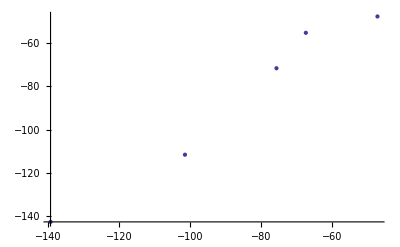

```mathematica
Table[Select[qnm[pp],Abs[Re[#]-4]<10^-5&],{pp,30,70,5}];
SetPrecision[Table[%[[9]]-%[[ww]],{ww,1,9}],30];
Re[%]
Log[Abs[%]]
ListPlot[%]
```

```mathematica
list={2,3,4,5,6,7,8,9}
```

{2,3,4,5,6,7,8,9}

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[list,{#<7,#>4}&]
```

```mathematica
Select[Select[list,#<7&],#>3&]
```

{4,5,6}

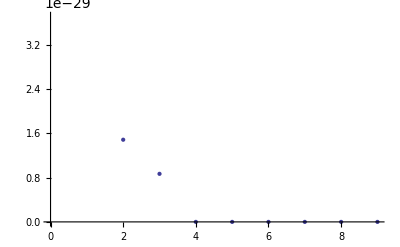

```mathematica
Table[Select[Select[qnm[pp],Abs[Im[#]+4.764139868466971519971815344392779962849017121647065850928]<10^-12&], Re[#]<0&],{pp,30,70,5}];
Abs[Im[SetPrecision[Transpose[Table[%[[9]]-%[[ww]],{ww,1,9}]][[1]],30]]];
ListPlot[%]
```

Convergence of the settlet solutions that does not satisfy the constriant

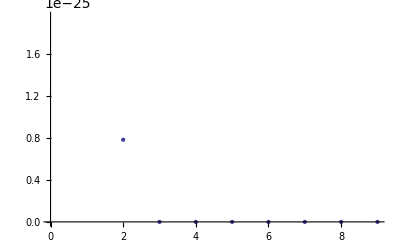

```mathematica
Table[Select[qnm[pp],Abs[Re[#]-2]<10^-5&],{pp,30,70,5}];
Abs[Im[SetPrecision[Transpose[Table[%[[9]]-%[[ww]],{ww,1,9}]][[1]],30]]];
ListPlot[%]
```

```mathematica
QNMonly[20,0,0,30]
```

{0,0,2.00000000010145866298757107184-2.00000000000896057081541063804 ⅈ,2.0000000001014586629875634712-2.00000000000896057081542058679 ⅈ,-2.00000000010145866298756347171-2.00000000000896057081542058778 ⅈ,-2.00000000010145866298757501087-2.00000000000896057081540923663 ⅈ,-7.×10^-29-4.00000000006437738177564456938 ⅈ,-4.00000000006437738177564457445 ⅈ,-3.11945159664383661849987962545-2.74667572771602004664282492 ⅈ,-3.11945159664383661850208220147-2.7466757277160200466407594458 ⅈ,3.11945159664383661850382875289-2.7466757277160200466422187208 ⅈ,3.11945159664383661850139672765-2.7466757277160200466460708868 ⅈ,3.9999923400431795687378198977-4.00000864916282739462957003582 ⅈ,-3.9999923400431795687382036765-4.00000864916282739462928635424 ⅈ,-3.9999923400431795687382031613-4.00000864916282739462928743596 ⅈ,3.9999923400431795687382218676-4.00000864916282739462930493476 ⅈ,5.16998035224286569965258989658-4.7641398684669715198059691897 ⅈ,5.16998035224286569950179008756-4.7641398684669715199967177116 ⅈ,-5.16998035224286569955181522836-4.7641398684669715200008227554 ⅈ,-5.16998035224286569955199239067-4.7641398684669715200006401684 ⅈ,-7.99994301175551064451391815859 ⅈ,-1.543019327×10^-19-7.99994301175551064475947307998 ⅈ,5.95470364884195257012094297251-5.929145838755664866740470973 ⅈ,5.95470364884195257015050631261-5.9291458387556648677880807758 ⅈ,-5.95470364884195257015092968969-5.92914583875566486778834066 ⅈ,-5.95470364884195257015092960332-5.9291458387556648677883409282 ⅈ,6.58585006639690888299869603155-6.4449521793323292387792722123 ⅈ,-6.58585006639690888299869483684-6.4449521793323292387792791909 ⅈ,-6.58585006639690888299918074242-6.4449521793323292387796923198 ⅈ,6.58585006639690888276450723412-6.4449521793323292415471163918 ⅈ,5.5821403282120721160280238765-7.4695289911184621085623605675 ⅈ,5.5821403282120721161879223622-7.46952899111846210878460661028 ⅈ,-5.5821403282120721161879279445-7.46952899111846210878464037701 ⅈ,-5.5821403282120721161880292147-7.46952899111846210878460661184 ⅈ,-2.18167065×10^-20-9.35021828558983554466169428549 ⅈ,1.9764×10^-24-9.350218285589835544726139201 ⅈ,2.267123381093249239471146235-9.13485933320856987976510090845 ⅈ,-2.2671233810932492394609443881-9.13485933320856987982505878134 ⅈ,-2.267123381093249239467667557-9.13485933320856987983287902923 ⅈ,2.267123381093249239467665954-9.13485933320856987983288560288 ⅈ,-1.402778×10^-22-9.53017353371601463072075837671 ⅈ,-3.813858×10^-22-9.53017353371601463072122830538 ⅈ,-2.2418640971352611781282380995-9.32767642015403912226718569934 ⅈ,2.2418640971352611781282381075-9.32767642015403912226718573237 ⅈ,2.2418640971352611781282381068-9.32767642015403912226718573531 ⅈ,-2.2418640971352611781282374977-9.32767642015403912226718594234 ⅈ,-4.2664892909100925631466147366-8.60726137032825396569049965679 ⅈ,-4.2664892909100925600587419372-8.60726137032825396933652134309 ⅈ,4.2664892909100925601143740024-8.60726137032825396937232370073 ⅈ,4.2664892909100925599343279689-8.60726137032825396962037713857 ⅈ,7.59944529817102024195984381593-6.0015130234936485366812437619 ⅈ,7.59944529817102024195975584824-6.0015130234936485366814401204 ⅈ,-7.59944529817102024195976011026-6.0015130234936485366814384571 ⅈ,-7.59944529817102024195976011032-6.0015130234936485366814384572 ⅈ,-5.540740018747855263876973218-7.98806299314209148515328009559 ⅈ,-5.5407400187478552638769732183-7.98806299314209148515328009612 ⅈ,5.5407400187478552638769732141-7.98806299314209148515328011897 ⅈ,5.5407400187478552638766567163-7.98806299314209148515436103089 ⅈ,-4.3169108447074533880564267328-8.87682979840011085589882486161 ⅈ,4.3169108447074533880564267315-8.87682979840011085589882486359 ⅈ,-4.3169108447074533880564267315-8.87682979840011085589882486359 ⅈ,4.3169108447074533880560825488-8.876829798400110855899324453 ⅈ,8.11083571659139854746201944603-5.7657529132266942197234473535 ⅈ,-8.11083571659139854753052502519-5.7657529132266942197586654744 ⅈ,-8.11083571659139854753157331675-5.7657529132266942197591634335 ⅈ,8.11083571659139854753342416973-5.7657529132266942197597888973 ⅈ,9.71077687826770393038043791158-5.3146920578586932780468768192 ⅈ,9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,-9.71077687826770393038043800258-5.3146920578586932780468767984 ⅈ,-9.71077687826770393038043800262-5.3146920578586932780468767985 ⅈ,10.2321297704807696818433003438-5.0437836885533711920490900144 ⅈ,-10.2321297704807696818459357754-5.0437836885533711920497226548 ⅈ,-10.2321297704807696818459357758-5.0437836885533711920497226589 ⅈ,10.2321297704807696818459357758-5.0437836885533711920497226589 ⅈ,0.8048295337049070271596541245-11.6544764900449915182492779201 ⅈ,-0.80482953370490702715924891-11.6544764900449915182500378377 ⅈ,0.8048295337049070154470773959-11.6544764900449915227151678038 ⅈ,-0.8048295337049068453683283072-11.654476490044991703543830827 ⅈ,-3.1049437963009610784898529476-12.3039142314249372027004700182 ⅈ,3.1049437963009612851914635392-12.3039142314249373337042088118 ⅈ,-3.1049437963009613074083737367-12.3039142314249373522125815655 ⅈ,3.1049437963009614048767064977-12.3039142314249374733736136682 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832807 ⅈ,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,-12.1660405358211249244165719222-4.4372717593693833994805832809 ⅈ,12.6990073116983382587467753793-4.0709620700283630158901508255 ⅈ,-12.6990073116983382587467753793-4.0709620700283630158901508254 ⅈ,-12.6990073116983382587467753826-4.0709620700283630158901508172 ⅈ,12.6990073116983382587467753827-4.0709620700283630158901508171 ⅈ,5.8934597076962899427066589384-12.8197894843043961905724199467 ⅈ,-5.8934597076962899441093237007-12.8197894843043961943519176893 ⅈ,5.8934597076962899399639326706-12.8197894843043961963828622719 ⅈ,-5.8934597076962899428553836008-12.8197894843043961964289804908 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,15.2379026567692712181992634244-3.1413383779034106651564413708 ⅈ,-10.062562283589727022612973844-12.3710399916108125816450821803 ⅈ,10.062562283589727022612926845-12.3710399916108125816451801181 ⅈ,-10.062562283589727022613043922-12.3710399916108125816451056034 ⅈ,10.062562283589727023271846704-12.3710399916108125816634898726 ⅈ,7.5598149606212357170315996871-14.0454561413520789470977237148 ⅈ,-7.5598149606212357172215171429-14.045456141352078947856651779 ⅈ,7.5598149606212357172281597862-14.0454561413520789478812868654 ⅈ,-7.5598149606212357172281597868-14.0454561413520789478812868654 ⅈ,-15.7848887723836075045835932908-2.6461300415071409558668979793 ⅈ,15.7848887723836075045835932908-2.6461300415071409558668979793 ⅈ,15.7848887723836075045835933045-2.6461300415071409558668979724 ⅈ,-15.7848887723836075045835933045-2.6461300415071409558668979724 ⅈ,-13.7946244384640236073846795117-11.409654122626602282215719086 ⅈ,13.7946244384640236073846796231-11.409654122626602282215719338 ⅈ,13.7946244384640236073846796325-11.40965412262660228221571935 ⅈ,-13.7946244384640236073846796325-11.40965412262660228221571935 ⅈ,18.0103692245611220069853151563-10.274932299862540383001431344 ⅈ,-18.0103692245611220069853154121-10.274932299862540383001431574 ⅈ,18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,-18.0103692245611220069853158335-10.274932299862540383001431857 ⅈ,-22.9467566450003876473998972651-8.755279918733136951523374768 ⅈ,-22.9467566450003876474010008206-8.7552799187331369515219906259 ⅈ,22.9467566450003876474010008206-8.7552799187331369515219906259 ⅈ,22.9467566450003876474010073352-8.7552799187331369515219941642 ⅈ,-29.1333371250947823249827964767-6.4904858141305597766494662847 ⅈ,29.1333371250947823249843359271-6.4904858141305597766494996459 ⅈ,-29.1333371250947823249843695082-6.4904858141305597766497982587 ⅈ,29.1333371250947823249781111829-6.4904858141305597766980669775 ⅈ}

```mathematica
qnm1[30]=QNMonly[20,1/2,1/2,30];
qnm1[35]=QNMonly[20,1/2,1/2,35];
qnm1[40]=QNMonly[20,1/2,1/2,40];
qnm1[45]=QNMonly[20,1/2,1/2,45];
qnm1[50]=QNMonly[20,1/2,1/2,50];
qnm1[55]=QNMonly[20,1/2,1/2,55];
qnm1[60]=QNMonly[20,1/2,1/2,60];
qnm1[65]=QNMonly[20,1/2,1/2,65];
qnm1[70]=QNMonly[20,1/2,1/2,70];
```

```mathematica
0.041992055724129482398163011716393582902277917269724898802848485523872653608261292334926258830762`70.15051499783199 ⅈ-0.041992055724129482398192460845453112594189734731741671599`30.15051499783199 ⅈ
```

-2.9449129×10^-23 ⅈ

```mathematica
qnm1[30];
Transpose[{Re[%],Im[%]}];
ListPlot[%]
```

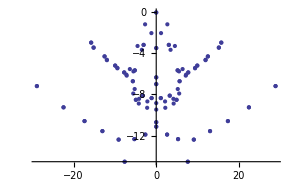
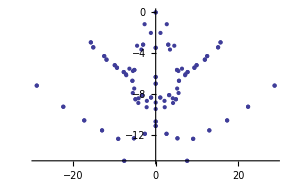

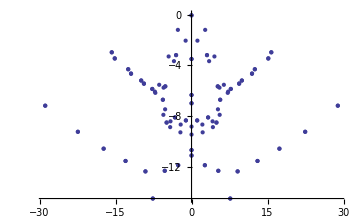

```mathematica
qnm1[70];
Transpose[{Re[%],Im[%]}];
ListPlot[%]
```

```mathematica
Table[Select[qnm1[pp],Abs[Im[#]-0.0419920557]<9 10^-1&],{pp,30,70,5}]
```

{{-2.1066525×10^-23-0.0419920557241294823981924608455 ⅈ,-2.936185×10^-24-0.0540146929129890877864171549235 ⅈ},{5.74097095×10^-28-0.041992055724129482398163011979464283 ⅈ,5.2495623×10^-29-0.054014692912989087786419408095627368 ⅈ},{2.470622×10^-34-0.04199205572412948239816301171639393213191 ⅈ,-1.858676×10^-34-0.05401469291298908778641940810141229100166 ⅈ},{-4.3×10^-45-0.0419920557241294823981630117163935829022779043 ⅈ,2.61×10^-43-0.0540146929129890877864194081014123220318722673 ⅈ},{0.-0.041992055724129482398163011716393582902277917269725 ⅈ,0.-0.054014692912989087786419408101412322031872760048392 ⅈ},{-6.0433×10^-52-0.04199205572412948239816301171639358290227791726972444017 ⅈ,1.6413×10^-51-0.054014692912989087786419408101412322031872760048395641 ⅈ},{3.6879×10^-57-0.0419920557241294823981630117163935829022779172697248988516932 ⅈ,6.036287×10^-55-0.0540146929129890877864194081014123220318727600483918405292717 ⅈ},{0.-0.041992055724129482398163011716393582902277917269724898802848485524 ⅈ,0.-0.054014692912989087786419408101412322031872760048391840587160748162 ⅈ},{0.-0.04199205572412948239816301171639358290227791726972489880284848552387265 ⅈ,0.-0.05401469291298908778641940810141232203187276004839184058716074816155749 ⅈ}}

## Result

k=1

```mathematica
{{0,-0.02718527},{0,-0.165850542},{0,-1.271566824},{0,-1.27306113490},{0,-1.839999999},{0,-2.398436987},{0,-2.56810825027},{0,-2.56842619},{0,-2.9883187},{0,-3.680000},{0,-3.8967198}}
```

```mathematica
{{1.758119062,-1.29749545},{3.5829889758,-3.883250677},{3.87346657,-3.94073495},{4.76232399,-3.5089319},{5.91376969,-6.7770466}}
```